# nemiss-pload4d code v1.0

## simulating high energy astrophysical neutrinos

Calculates neutrino emission from Special Relativistic MHD hydrocode data, in binary format.

This is the nemiss code, version 1.0. This program is released under the LGPL-3.0-or-later licence, Copyright 2015-2019 Theodoros Smponias. 
Please see the COPYING files in this distribution for copies of the licences. Part of this program, is based on the pload.m data loading program, by A. Mignione, that came with the PLUTO hydrocode distribution. nemiss works for a point source.  pload4d, an evolution of pload3d, based on pload.m, employs nemiss to calculate nemission from hydrodata.

### Code description

This program comprises two parts, nemiss and pload4d. nemiss (neutrino emission) is based on the formalism of Kelner et al. 2006 Ph. Review (ref here) and on the formalism of Reynoso and Romero (2008/9 paper ref here). pload4d is based on the pload.m, supplied with PLUTO, and on its evo by TS, pload3d.m (2015). The structure and function of  these two parts of the current program is now presented in brief.

#### nemiss

This program first defines a number of physical quantities that are constants during the calc. It then reads a further number of such quantities off two parameter files, one is rlos’s rlos_params(...), the other being specific to nemiss. This is for the user’s convenience, and it also feeds params to pload4d. Be careful to update the names of those files in case there is a new version of rlos. 

nemiss is prepared as a series of functions, calling one another in a series of operations. This reflects the fact that nemiss is calced through solving a sequence of transfer equations, representing a cascade of particle populations within the jet. Please see the relevant paper for that. The net result is a multiple numerical integration. The parameters of the last function call are then passed up the line to the first series of functions (parameter passing). Those params are essentially hydro quantities and also viewing angles. This may calc from a point source, where one-off params are assigned. Or, this may be part of a loop, or array-op, where params are now array-elements of a hydrodata array. Angles are also calced in the loop, based on its indices (loop indices i, j, k represent x, y, z gtid positions. CAREFUL x and z are interchanges when read, i.e. Bfield and velocity X and Z. This is because rlos reads xz reversed vs this one ).

nemiss_pload4d (npl) may work together with rlos, in order to produce relativistic, time-delayed synthetic images of RMHD jets. Hydro data are imported to npl and then nemission in calced and stored to an array. Due to the heavy load of the nemiss calc, a filter is employed, calcing only from those cells whose velocity direction is closer to the LOS going through that cell. The relevant LOS’s direction may be calced either for radiograph case (all LOs’s parallel to each other, resulting to an X-ray-like image) or camera obscura (focused beam, with a focal point residing either on-grid or out of it). The results are then dumped to a dummy var data file, already included in the hydrocode run. That file is then opened automatically from rlos’s pload.pro (came with PLUTO) and thus nemiss emission coefficients become available to rlos. It is then a matter of one assignement to do the relat. imaging calc within rlos! 

Or, nemiss_pload4d may work as a standalone program. In the latter case it calculates the total sum of emission from the hydrojet (a simple summation of the elements of the resulting array).

#### pload4d

The second part of the program, is pload4d. This one loads hydro sim data from PLUTO and then runs nemiss on them. The results are written back to one of the dummy files pre-created from PLUTO. The result from each time instant, are writtent to a dummy file of that time instant. Naming conventions from PLUTO are maintained. Then, rlos should open those dummy files automatically, when using pload.pro. Thus, pload4d uses nemiss on a 4D hydro data set, calcs nemission globally, using a filter, and outputs the emission coefficients to a pre-existing dummy file, to be read by rlos. Then, rlos does relat. imaging using the new nemiss coefficients! Alternatively, within nemiss_pload4d itself, contents of the resulting nemission array may be summed, for a given freq., the output being the result for a point source. This way, spatial detail is lost. Also, a 3D plot of the nemissivity data for a given time instant may be created within nemiss_pload4d.

#### Testing nemiss

In order to test the functions of nemiss, we run two parallel calcs. One using the functions and another using regulara expressions. The regular one is only valid on the initial set of values assigned to the various params. After that is verified and correct, we then repeat that using the functions structure of calc, WHILE CALLING THE FUNCTIONS with the SAME values of params as the regular calc, When a match is achieved, this means the finctions work like the regular calc. But the functions can now operate on any other set of param values, without re-typing their assignements, only we have to call functions with the new values!

#### Multiple functions

nemiss has many functions for the same calculation. Each one is a different version of the same thing: the one currently employed is the last one, normally the best one. Some of therm are also compiled functions.

#### Scales and units

Values of params are application-dependent. Constants and units in general, are aimed to be in CGS. It is best to check size scales of results for all intermediate steps along the calculation, in order to verify correct size scales. This may include plotting intermediate functions.

#### A very short guide on how to practically use this code

First, prepare your data. In this version of the program, this means run a PLUTO hydrocode simulation and save the results. Last run was with float data. Binary data files MUST be saved in MULTIPLE FILES format, set up this in pluto.ini param file of the PLUTO code. This code opens the binary data files, either .dbl or .flt for double or single accuracy, respectively. PLUTO must be set, in userdef.c, in src folder, to also save some dummy user-defined vars. These shall be used by nemiss to werite the nemiss result. Then, these may be opened for e.g. by rlos, or any other program. We just make sure that the nemiss result is also written to disk in the same format as the hydrocode results. It is then just a nother data file. 

Then, plese make available the two external param files of rlos and of nemiss. These are necessay for the run, even when rlos is not present or is not to be used anyway. But its param file is required. From there, nemiss shall read the first and last datafile to open, etc many other things. Then, we may begin to run the notebook of nemiss_pload4d.

In order to run nemiss_pload4d  on the data, we must employ one of the nested loop cells towards the ends of the code. Only one of those is needed. All of them at the moment can do  the radiograph geometry, but only the one within the triple thick lines can do the camera obscura geometry as well!

### IMPORTANT PRACTICAL TIP!

For some reason, we must re-do the t_adb cell, else it blocks all the subsequent calcs. So: eval whole notebook, abort at some later point, then go back and re-eval t_adb  cell alone, then ready to correctly eval notebook again.

## Path determination

#### Hydro data and param files are taken to be in the same directory ONLY EDIT THE FOLLOWING PATH RIGHT HERE!

```mathematica
$HistoryLength=1;
```

```mathematica
(*020120 path generalization ONLY EDIT THE FOLLOWING PATH!!! REST 'AS IS'!*)
(*SAMPLE: pathlocation="Q:\\gitstuff\\torblobgoodhope\\"; 
 SAMPLE2: O:\\PLUTO_DATA\\torblobgoodhope\\*)

"/media/teodor/adbeaead-8c4a-4c60-a05b-5093f9411de1/applications/scrange/lowres_55_deg_losu/torblob18dummies/rlos_params_v253.txt"
pathlocation="/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/";

(*020120 next some verification stuff*)

pathlocationstring=ToString[pathlocation];
Print[pathlocation,"   ",pathlocationstring];
rlosparamfilen="rlos_params_v253.txt";
nemissparamfilen="n_emiss_param_v116.txt";pathone=StringForm["`1``2`",pathlocationstring,rlosparamfilen];
pathonestring=ToString[pathone];
pathtwo=StringForm["`1``2`",pathlocationstring,nemissparamfilen];
pathonestring=ToString[pathone];
pathtwostring=ToString[pathtwo];
Print[pathone," tsa  ",pathonestring," edo to path to the first file "];
Print[pathtwo,": edo to path to the second file ",pathtwostring];

 
"Q:\\gitstuff\\torblobgoodhope\\""   ""Q:\\gitstuff\\torblobgoodhope\\"
"Q:\\gitstuff\\torblobgoodhope\\rlos_params_v245.txt"" tsa  ""Q:\\gitstuff\\torblobgoodhope\\rlos_params_v245.txt"" edo to path to the first file "
"Q:\\gitstuff\\torblobgoodhope\\n_emiss_param_v101.txt"": edo to path to the second file ""Q:\\gitstuff\\torblobgoodhope\\n_emiss_param_v101.txt"
(*020120 SOS use this as a blueprint! (from stack exchange)*)
var1="Tree";
var2=10;
aaasssd=StringForm["The `1` is about `2` feet tall...",var1,var2];
Print[aaasssd];
"The Tree is about \!\(10\) feet tall..."
```

/media/teodor/adbeaead-8c4a-4c60-a05b-5093f9411de1/applications/scrange/lowres_55_deg_losu/torblob18dummies/rlos_params_v253.txt

/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/   /home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/

/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/rlos_params_v253.txt tsa  /home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/rlos_params_v253.txt edo to path to the first file

/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/n_emiss_param_v116.txt: edo to path to the second file /home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/n_emiss_param_v116.txt

Q:\gitstuff\torblobgoodhope\   Q:\gitstuff\torblobgoodhope\

Q:\gitstuff\torblobgoodhope\rlos_params_v245.txt tsa  Q:\gitstuff\torblobgoodhope\rlos_params_v245.txt edo to path to the first file

Q:\gitstuff\torblobgoodhope\n_emiss_param_v101.txt: edo to path to the second file Q:\gitstuff\torblobgoodhope\n_emiss_param_v101.txt

The Tree is about 10 feet tall...

The Tree is about 10 feet tall...

```mathematica
"Q:\\gitstuff\\torblobgoodhope\\rlos_params_v245.txt"" tsa  ""Q:\\gitstuff\\torblobgoodhope\\rlos_params_v245.txt"" edo to path to the first file "
```

Q:\gitstuff\torblobgoodhope\rlos_params_v245.txt tsa  Q:\gitstuff\torblobgoodhope\rlos_params_v245.txt edo to path to the first file

```mathematica
"Q:\\gitstuff\\torblobgoodhope\\n_emiss_param_v101.txt"": edo to path to the second file ""Q:\\gitstuff\\torblobgoodhope\\n_emiss_param_v101.txt"
```

Q:\gitstuff\torblobgoodhope\n_emiss_param_v101.txt: edo to path to the second file Q:\gitstuff\torblobgoodhope\n_emiss_param_v101.txt

## intro stuff

## inert but important part: current status overview and in-code links to ongoing work

(*160123 SUPER SOS changed sign of los directional vectors,
since LOS is APPROACHING, not receding! Now we get boost on the approaching
jet and de-boost on the receding jet! *)

080122 seems to work step by step for 240*400*200, but says lacks ram when going gets biggy. Two options: 1. dload a smaller calc, re-do it for that, and then be sure and proceed with verification and ram upgrade. else, go directly . Perhaps select 1, in order to spend less time at the higher and costlier config.

(*080122 SOS nout is a test run for a given snapshot. SOS for this big spatial run, we only keep 0 and 1 temporal snapshots, therefore nout can only be set to 0 or 1! SOS we do 1. *)

080122 SOS tried to conditionalize, with pottestplots, most plots that were added in order to publish the 2021 paper to mdpi galaxies. that is we added many plots AFTER running the sims, and those plots sort of fucked it up a bit. So, we made their plotting conditional, using the r plottestplots, which is read from the param file of this code. So, set the var to 0, and no plots are messing with the code. But, if you want those plots, set it back to ON. SOS also, keep this mathem code updated, and only supplemment each other with the new code. SOS this is handier, that is faster.

070122 added if plottestplot==1.0 to the manipulate plots of paper plotted quantities, in order to only call them if plots are required. SOS THEY MIGHT BE MESSED from the if, so might have to un-if them manually in order to plot them for a future paper, just in case! SOS!

260621 SOS did plots for qpp injection fn SOS and also did polish the resr

(*210621 sos mixed the names of the plots sos  we did other and called it otherwise sos we plotted q and called it u, etc just a couple got messed do them finally!*)

(*200621 SOS it works but takes a while. also, careful to prepare all previous things before running this*)

(*190621 romr polish fig and frame it ULTRASOS here lies the solution to scinetific notation as well we already did it over here,for sigma inelastic sos,  we just need two arrays,  FrameTicks→{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-28,"10^-28"},{10^-27,"10^-27"},{10^-26,"10^-26"}}}*)

180621 SOS Frame->True, FrameTicks, etc check out figs sos polisdhing em aka romr comm

(*ultra sos 311020 here set delay to moar than 100000. cause we leave it for a couple of days to run and if it exceeds a day plus something, i.e. 100000 sec, then it goes on running test stuff below, potentially ruining the whole thing!*)Pause[10000000]

110820 SOS added following three params to v115 param file! Now, we may conditionally inert ze calcs, in order to paint’ the filtered cells using the ‘space test value’.  Next, proceed to normalization, using whole jet calc, without velocity filter! (filter at very low speed, thus get jet volume!)
protonexpo Param to control wether we employ expo cut off for proton p-law distro. Additional term that is, after E^(-a).
0.0
spacetest Param to calc null result for filtered cells, in order to find out which those cells are!
0.0
spacetestvalue Test value for above result: I.e. a null calc result. 
123456789

100820 SOS added bxx,byy,bzz dependence to varpindex version of ndens (not retroactively to all ndens’s! only the latest varpindex one! It seems to work, and we now have the cutoff and its dependence on local bfield! Cutoff now varies from point to point, IF we conditionally employ the ecutoff! Seems to work!)

(*090820 SOS Ecutoff is now too large, 10^15 GeV! No! Need smaller!*)
(*090820 see plots below! cutoff works like a charm, only the Ecutoff nedds become smaller! See to it!*)
Print[emaxprotonexpo[bxx,byy,bzz,rjetparam]/GeV];

050820 SOS we conditionally added expo term to fast proton power law, aka args19. REMAINS to add relevant params to the external param file!
also, remains to do the tesc thingy, again conditionally, either or not using the hillas energy! eBRjet!.
also fixed tloss relic make sure not used at all any moar!

020820 SOS major correction to tdepthpp, we canceled the dependence of tpion on edash1! ARGS eqn 40. tpion is only a function of parameter E, not edash2 integration var! SOS! also, swapped eee, eeedash1, to match the symbols in eqn 40 of args09! 

ALSO, almost there in adding OPTIONAL tppion support, though it seems rather trivial, as plotted tppion is much smaller than the others. Still, do it optional! SOS!

tppndens=Function[{EEE,ndensity},1.0/(ndensity*c*σinelaspp[EEE]*K_pp)] ;
(*010820 we now add the proton pion thingy after all!SOS inherit from function call the FRACTION! SOS!!! MAYBE USE IT! for VHE! SOS!*)
tppion=Function[{EEE,ndensity,xxx},(ndensity*c*σinelaspp[EEE/xxx])/2.0];
tsa!
σinelaspp[0.9*1000GeV]
tppion[1000GeV,ndens,0.9]
(*SUPER SOS HERE LIES SLOW PROTON DENSITY WE MUST FIX THIS FOR SLOW PROTON DENS UPCOMING FUNCTIONALIXZATION!*)
(*sync time*)

(*091019 SUPER SOS ADD HERE BBB DEPENDENCE SUPER SOS DO IT HERE!!!*)

(*010820 ADDED tppion check it need call xxx for bbpion as well! check effects! SOS times!*)
(*SOS ADD MINUS TO ALL BBP's SOS DO IT REGARDLESS OF tppion! SOS!*)
bbπtroisndensvarmagneticxxx=Function[{Epi,bxxvar,byyvar,bzzvar,ndensity,xxxi},-Epi*((tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(t_adb)^-1+(tppion(Epi,ndensity,xxxi))^-1)];

(*010820 SOS here we put a minus! was in the paper all along!*)
bbπtroisndensvarmagnetic=Function[{Epi,bxxvar,byyvar,bzzvar,ndensity},-Epi*((tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(t_adb)^-1)];

310720b SOS now playing with plotparams for uanal, in order to achieve a match with a larger y-axis span, i.e. fall over the desired number of OOM! almost there! play with the times as well!TOO SENSITIVE WITH SOME OF THE TI”ME”S THE RES”ULTS! SOS! SEE a little  BELOW EARLIER NOTES!

(*310720 we use statcoulomb , no Coulomb, since CGS our units! SOS*)
taccel=Function[{ett1,etaaccelefficiency,bxxvar,byyvar,bzzvar,uxxvar,uyyvar,uzzvar},(ett1) /(etaaccelefficiency*c*(1.6*10^-27*c*2997919999.934)*bfieldfn[bxxvar,byyvar,bzzvar])];

(*310720 we should use a higher ndens for tpp only, as it is at jet base. None other t is affected from density! SOS*)
ndens
tppndens=Function[{EEE,ndensity},1.0/(ndensity*c*σinelaspp[EEE]*K_pp)] ;

300720 this works with both 3 dummies and 18 dummis. However, when setting it to BOTH (allowed in 18 dummies only), i.e. activate both single calc and spectral as well, scale of single calcs appears many OOM smaller than similar-E spectral calc. Check scaling again! ALSO scaling of times! Rest, seem to start getting together!

290720 it works! both for dummy3 and dummy18! But, we need to edit path in here, and also the param file! SOS for dummy 3, it wont print the calcs! C to it! But it will (TSETSE LUP!) reach inside the if condition! maybe it wont print? or what? check!

270720 SOS trying to make a common version, where we select params from param file either 3 dummies, or 18 dummies. SOS originally, 3 dummies also could run with lemission spectrale, without saving spectra, though. NOW, we group lemspectralle with 18 dummies, so now we either do spectra (18 dummies), or not (3 dummies)!. SOS 3, 18 is RELATIVE! it is MAXDUMMY that sets up things in nemiss, in auto mode. BUT: in pload.pro, and in rlos2, thingies are not auto yet. SOS TRY TO automate things there as well, calling params etc! ELS E DOCUMENT STUFF!

260720 SOS remains to do threeeighteenfactor SOS 3 or 18 dummies selection. ALSO:  conditionally run the various tests! DO IT AS WELL!
(*260720 here we set the bfactorcompilec selection: if set to on, the activate C compilation. If OFF, then general compilation only!*)
(*260720 we get to keep C-calls ONLY! WE conditionally assign to it either  B, or non-B!*)
(*260720 WE also get to keep all old defs! We merely add a new def, the C-one, AND ALTER CALLS IN THE ACTION LATER ON, to be only C-calls! So we only call the conditionally-defined C-ones! varpindex-ed, or non-varpindexed! THIS ONLY GOES FOR THE LATEST VERSES, not the simpler ones!*)
If[bfactorcompilec == 1.0,

(*260720 if bfactorcompilec eq 1.0, then employ C-compiler. Else, proceed with general, non-specific compilation, after the separating comma!*)

#### SOS we need to fins the correct units for tacceleration, ARGS08,09,begelmanetal90 SOS stracoulomb etc stuff! (*240720 reversed it! we also reverse it below! taccel, not to the minus1 here! SOS!*) (*240720b 1coulomb=(c/10) stC SOS stC is CGS for electric charge! nearly 3 billion! we only assumed a thousand! SOS were wrong! WTF solved this 240720b! So now we have: electron or proton charge=1.6*10^(-27)C=1.6*10^(-27)*2,997919999.934 stC=*) etaaccelefficiency1=0.1; (*240720B ULTRA SOS, FROM BEGELMAN et al. 1990: FSC=(FERMI MFPATH)/(LARMOR RADIUS)*) (*ARGS08 apparently set FSC=1.0: *) FSC=1.0; (*SOS 240720b where we have (ARGS08): etaaccelefficiency1=(beta(beam))^2 SO FOR FASTER BEAM, a larger eta occurs! SOS connect it to the beam speed for tadb SOS !!!*) etaaccelefficiency1=ubeamnozzlefortadbcalc*ubeamnozzlefortadbcalc*FSC; etaaccelefficiency1 (*240720b coulomb to statcoulomb, i.e. SI to CGS el. charge conversion!*) 1.6*10^-27*(c/10.) c (*240720b 1coulomb=2,997919999.934 stC SOS stC is CGS for electric charge! nearly 3 billion! we only assumed a thousand! SOS were wrong! WTF solved this 240720b! So now we have: electron or proton charge=1.6*10^(-27)C=1.6*10^(-27)*2,997919999.934 stC=*) (*240720B taccel: the existing c is meant to be the convertion factor, divided by 10! SOS MAYBE e is in coulombs then! From statcoulomb definition! CHECK AGAIN! SUPER SOS!*) taccel=Function[{ett1,etaaccelefficiency,bxxvar,byyvar,bzzvar,uxxvar,uyyvar,uzzvar},(ett1) /(etaaccelefficiency*c*(1.6*10^-27*c*0.1)*bfieldfn[bxxvar,byyvar,bzzvar])]; Print[taccel[100GeV,etaaccelefficiency1,bxx,70*byy,bzz,u_xx,u_yy,u_zz]]; Print[1./taccel[100GeV,etaaccelefficiency1,bxx,70*byy,bzz,u_xx,u_yy,u_zz]]; (*210720B LogLogplots of times! SOS shape is similar, scales are not all same ! SOS!!! CORRECT THEM!! ALSO do sinelpp comparison, ct1 fixation, etc*) (*210720B SOS tpp in the args09 paper is around 10^1, HERE it is 10^(-4). WTF? investigate! ALSO, tadb is kinda different, also check that out!*) (*240720 nailed tsync vs ARGS08, was just a matter of multiplying byy default value by 70.0(byy is 10 times moar than bx, bz, in default values that is!)!*) (*240720 also, tadb is OK, just a matter of assumed ubeam ans zj size of system! so tadb also nailed it!*) (*240720 SOS taccel is different in ARGS09 (defined as here) and in ARGS08 where it is just the sum of the other times, ALL INVERTED! check and do!*) Print[bxx,byy,bzz]; LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,70.0*byy,bzz,u_xx,u_yy,u_zz],1./t_adb,(1./tppndens[et11,ndens]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz])},{et11,1GeV,100000000GeV},PlotRange→All,PlotPoints→8,MaxRecursion→0,PlotLabels→Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsyncfvarmagnetic^-1"},Above]]

(*240720 nailed tsync vs ARGS08, was just a matter of multiplying byy default value by 70.0(byy is 10 times moar than bx, bz, in default values that is!)!*)
(*240720 also, tadb is OK, just a matter of assumed ubeam ans zj size of system! so tadb also nailed it!*)
(*240720 SOS taccel is different in ARGS09 (defined as here) and in ARGS08 where it is just the sum of the other times, ALL INVERTED! check and do!*)

230720B tries increasing tesc first to 30 then to 400, and it made uanal drom by6-7 OOM. Then, start playing with tloss! This one more sensitive!. PRobably wrap them times up, and prepare for practical runs. Also, do the constants: ct1, normalization, etaslash, proton percentage of energy, proton to electron energy ratio, etc. Fix these and set the times and then from notebook mag fields, density expression, etc. SOS write it up from then on!

230720 (*230720 SOS add tesc,tloss to outside param file! SUPERSOS*)
tlossexact fn is NOT used, only tloss param! SOS!

(*171019 sos moved this BEFORE the tpion fn def! else wont work as tesc is NOT a fn param! 161019 SUPER SOS this little value tesc=(zmax-z)/c (from reynoso romero paper) affects wether we get any emission at all! too small and it cools off rapidly, particle escape time from the jet system! A tenner works fine as it is now, a unit not so much!!*)

(*230720 SOS add tesc,tloss  to outside param file! SUPERSOS*)
tesc=0.01;
tesc=10.0;
(*230720 try make uanal drop faster!*)
tesc=1.0;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
tloss=0.01;

(*171019 sos moved this BEFORE the tpion fn def! else wont work as tesc is NOT a fn param! 161019 SUPER SOS this little value tesc=(zmax-z)/c (from reynoso romero paper) affects wether we get any emission at all! too small and it cools off rapidly, particle escape time from the jet system! A tenner works fine as it is now, a unit not so much!!*)
(*230720 SOS add tesc to outside param file! SUPERSOS*)
tesc=0.01;
tesc=10.0;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
tloss=0.01;
tlossexact=Function[{mm},1/mm];

220720B WE did TR13 fig. 2 as well match. We now have to match times Figure from ASRGS1=09 and 19. Last, but not least, match Qpp from ARGS19, make it drop for moar scales over energy span. And then , qneutrino al long last verification.

TR13 match:
(*220720 something with the alignement in 3D, find out and verify vs TR13 fig. 2*)
(*220720B SOS phi1 is X,Y angle (azimuth in XYZ cartesian). phi2 is elevation. So just stick with X axis velocity for now, try to nail the orientation for simple case of TR13 paper figure! Need to achieve a match!*)
(*220720 gammalorentz 5, 10 in TR13. i.e. u=0.9798 (gamma=5.001), and u=0.995 (gamma=10.01)*)
(*220720B MATCH! TR13 fig. 2 TOP (gamma=10). NXT, we do it for gamma=5, bottom fig. 2 of TR13.*)
(* *** *)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)

220720B SOS we corrected sinelastic pp with 10 times smaller, i.e. barn’s value. Now it matches kelner et al’s fig 11.  Also, we got Fpinj right, matching Kelner’s Figure for that as well! We now have to match angles for TR13 ratio figure, and also times Figure from ASRGS1=09 and 19. Lqast, but not least, match Qpp from ARGS19, make it drop for moar scales over energy span. And then . qneutrino al long last verification.

(*210720B LogLogplots of times! SOS shape is similar, scales are not all same ! SOS!!! CORRECT THEM!! ALSO do sinelpp comparison, ct1 fixation, etc*)
(*210720B SOS tpp in the args09 paper is around 10^1, HERE it is 10^(-4). WTF? investigate!
ALSO, tadb is kinda different, also check that out!*)

210720 added varpindex in ps01 and also cascaded it. Now add selection for wholelot qneutrino B(compile with C) or non-B (simply compile). Also, plot the times. Also, ct1 constant read (Jpp and its K1 not used by now any moar!) Alos, type in TI comments from edited draft.

(*200720B:  B version OF THE FOLLOWING FUNCTION (main current qneutrino function) just includes direct C compilation, only works at computer with C compiler available though! Else, omit the B SOS! NON-B version of the function is compiled in general, not only for C specifically! Therefore, works anywhere! But we must then edit  the two function calls in the big calc loop! SOS! Else, create a selection over there! SOS! ALSO, add a reading for protonindex1, to be read from file!*)
(*180720 this seems to do the trick!*)

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB=

200720 SOS added dependency on proton power law index, to many single functions (not all though, interims maybe excluded from this upgrade). SOS remains to add to function calls. Easy-peasy it was, cause wholethingy uanal and qneutrino directly call ndens...gamma, the latter having the protonindex facility incorporated all along! Only difference, we now call ndens....amma using a rptonindex var of mother wholethingy fn, instead of the fixed value of 2.
SOS VERIFIED for single functions 
 SOS remains to add to function calls. Also, type-in comments from HWritten.

190720 general behavior is similar to kelner06, args09, args19. Remains to check times, and also to do exact match using same params. Then, re-comment and re-shape flow-diagrams and then run it!

(13-19) /07/20 SOS fixed dummy thingy, had typed twice in pluto.ini/pload one of the dummy numbers, was an issue there!

130720 we did it right this time in pluto and rlos. Still, there is a dummy1 between dummies 14 and 15. So, no, pluto data still not coming out correctly. WTF is it doing there, dummy1 repeated? see flt.out for verification and FIND OUT A WAY TO FIX THIS, IN PLUTO! SOS DO IT!!! LAST THINGY ALMOST THERE!

100720 SOLVED! EASY PEASY! dummy15 in pluto, overwrites the same name as dummy1. So, when dumping, first it writes coslosu on dummy1, then overwrites that with bno 15’s contents. Therefore, we see at dummy 1 the same stuff as in dummy15, i.e. at nvar=11 the same as nvar=25! SOLVED! Just do the following :
1. fix dummy1/15 thing in pluto. 
2. make rlos read all of them dummies (not just 12 as is the case now), preferably as a function of maxdummy. MAYBE add maxdummy to rlos, or else read it from nemiss param file into rlos.

;080720 SOS coslosu_4d is same as mathemaTICa, BUT DUMMY1 IS OTHER THAN NVAR=11 OR DUMMY1 IN MATHEMATICA, IT IS SMALLER! sos CHECK HOW IT IS WRITTEN
;FOR NOW, USE COSLOSU4D HERE, NOT DUMMY1! OTHER DUMMIES ARE THE SAME, DUMMY IS IS NOTABLY SMALLER THAN EITHER COSLOSU, OR MATHEM DUMMY1! 
;DUMMY1 AND COSLOSU DISAGREEMENT FOUND! in SPECTRAL THINGY!

060720 SOS THIS DATASET AND ALSO nemiss and rlos both param files give the nice result of JUST four points to be calced, out of many thousands! (filter setup, jet setup). SO it is easy to work with, so do save the whole setup (PLUTO 3 files, both param files, both codes!)

060720 VERIFIED data orientation. Only an occasional datafile is written to zero size, SOS CHECK THAT about DATA INTEGRITY. BUT DATA ORIENTATION: WE READ, WE CALC, WE WRITE. THEN WE RE-READ, THEN WE flatten, transpose, etc et voila! aligned, just like huraaah! AND THAT IS  BEFORE RE_ASSIGNEMENT OF HURAAAH! SOS! SOS OLNY huraaaah is assigned to nvar no 10 AND no 20, this bit do make it conditional, so it also runs for 3dummies only, not only for 15 dummies. I.E. TRY TO UNIFY 3dummies and 15dummies SOS DO IT! ALSO CHECK DATA INTEGRITY!

(*050720b IT WORKS!!! re-read and transposed stuff aligned with calced stuff! now check again after first execution(look for logical error in repetition) and also look in PRINTOUT!rlos2 for same point when loaded! ALMOST THERE IN 5D . LU 050720b for all added notes! IT WORKS at first run of events incl. in-Mathem re-read!

050720 SOS we had  ERROR in order of databig indices in spectral loop assignement , within the big loop. Fixed it for ya now! Yet, a problem appears with data orientation, use huraaaah to fix that as well!. ALMOST THERE NOW, it WORKS, orient data and done with it!

030720 BUT nemiss writes ZEROS to databig componenrts. FIND out what is going on there, we try to print but RAM explodes slowly! WTF! investigate! ALMOST THERE NOW!

280620 it works OK for running but it fails (zero file size) to save results properly to disk. Actually, it saves only some of the files, while others are zero size!!! SOS try again maybe without corrupted dataset? SOS check vs old one that worked. Could it be dummy1 repating itself from PLUTO? CHECK!

270620 SOS ps01 now CORRECTED, goes from 1 to 3, cause in param file was 1 to 3, put in selection in-code was from zero to two, so no 3 gave problems! SOS! CORRECTED !!! SEEMS TO WORK NOW! SOS 



 this is D version, for ps01=1, it works. Check again for ps01=3 though! Also, this code works first time! run till calc loop, let it calc some, then abort, then do tadb, th en redo. No moar. For moar, first qu8it kernel and redo. Else, Ram saturates. Now, if historylength is set to on e, ram reduces, and can redo. But themn , tadb thingy stops working!. Unless, only first time, then it works! Careful with histlength anyhow. And, gather together various versions and save them with appropriate names!!!

270620 SOS till C version of this, it works just fine. Whern we try to place ps2001 reaving rearly on, then it saturates RAM! Which it clearly did not when ps selector was set to 3 and then read (to no avail of course) later on. Weird! It was NOT maxdummy the culprit, since noC of this works just fine, with maxdummy as a var, first intpart then real!

210620 SOS done ps01 selection, remains to be checked vs paper. ALSO, PUT into external param file the params for spectrum and for ps01 selection. SOS PARAMS SOS. and then normalixzation and mem constraining. SOS 
(*210620 SOS put this param onto external PARAM FILE, THIS one sets the PS01 funvtion to be used. simple, ps2001 or TR13, the latter being the best probably. zero means simle, one means ps2001 and 2 means TR13.*)
PS2001selector=1.0;
210620 In the following three cells we also declarethe above as different functions, so as to compare them when needed. but we only use a single name, after the above selection, in order to not have to change the names of the function call all over the code. 
....
Print["  PS2001selector=  ",PS2001selector];
PS2001feppndepend[1000GeV,u_xx,u_yy,u_zz,phi1,phi2]
PS2001feppndependgamma[1000GeV,u_xx,u_yy,u_zz,phi1,phi2]
PS2001simplified[1000GeV,u_xx,u_yy,u_zz,phi1,phi2]
PS2001original[1000GeV,u_xx,u_yy,u_zz,phi1,phi2]
PSTR13[1000GeV,u_xx,u_yy,u_zz,phi1,phi2]

190620 SOS itt seems to WORK, writes back all data in binary files. BUT: overqrrites twice the dummy1 thing, repaeated around dummy 15! SOS correct it in PLUTO userdef. ALSO: do a selection for ps01, to either use tr13 or ps01 or simple, in lieu of the same function name. AND, do ze normalization . And also do run rlos and test all together.

160620 SO FAR SO GOOD, it reads whole thingy! BUT dummy15 is dummy 1, in principle it wont matter, as it shall be overwritten! Thing is, we need moar RAM! another 16 GB perhaps, but it COSTS! SOS ! NEXT step wont work with existing RAM limitations, as we now have double the nvar params here!, ALSO, create a para in the external file to control wether we have .flt (as is the case now here) or dbl, which raises accuracy but at a further cost or additional RAM required!

(*110620 in lemissionspectrale, time is first coord and var number is last. DIFFERENT than databigtrans! SOS ALSO CHANGED fname2 to the correct fname3! else it overwrites the old one!
SOS IT WORKS PARTIALLY, nowhere does the dummy4, etc appears! to be improved therefore! SOS NAMES ADAPT, etc do it!*)
BinaryWrite[fname3,lemissionspectraletrans[[indicim,;;,;;,;;,n ]],”Real32”];

NEW SECTION FOR 15dummies!

SOS this bit to run only when 15 dummies is ON, in which case perhaps it will complement previous thing, which runs till nvar, but only caters till 3rd dummy. This shall takeover from the fourth dummy onward, without touching the results of the previous one. SOS the previous, existing structure, should be able to operate with the 15 dummies structure activated in pluto.ini! SOS!

(*100610 set this up to run from dummy3 onward, i.e. from n=14 onward! OR, moar generally, from (nvar-15) onward(test it to find exact setup that works OK!). After all, this section shall only run when the ‘15dummies’ (write15dummiestodisk==1.0) switch is active!*)

(*090620 here we do a secondloop, from where the first loop stops plus one, till the end of the spectral calc range of index i1
SOS REMAINS TO DO fname3 assembly! WHAT is this  varnames[[n]] thingy? SOS assemble 15 dummies prefix etc! do we need pre-existing from pluto the 15 additional dummies for this whole thing to work? Perhaps! if varnames is read from pluto param setup files from existing run data files!? 
*)

(*040620 it works! KEEPS DIMS AND falls with E along i1 loop! Also, works reasonably fast! But huge value disparity among points! so, SAMPLE AND TEST MANUALLY RUN IT!*)



If[ calcqneutrinospectralarray==1.0,
indexxx=0.7;
Print[" we test here, spectral loop, at  tt,ii,jj,kk= ",tt,ii,jj,kk];
Print[Dimensions[lemissionspectrale],"  point0 "];

Table[
Print[Dimensions[lemissionspectrale],"  point1 "];
tempovalue={CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[GeV(10)^((i1+0.01)^(indexxx)),databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]]};
Print[Dimensions[lemissionspectrale],"  point2 "];
Print[" i1= ",i1];
Print[" tempovalue= ",tempovalue];
Print[" lemissionspectrale[[tt,ii,jj,kk,i1]] (PRIN)= ",lemissionspectrale[[tt,ii,jj,kk,i1]]   ];
lemissionspectrale[[tt,ii,jj,kk,i1]]=tempovalue;
Print[" lemissionspectrale[[tt,ii,jj,kk,i1]] (META)= ",lemissionspectrale[[tt,ii,jj,kk,i1]]   ];
Print[Dimensions[lemissionspectrale],"  point3 "];
,{i1,1.00,15,1}


];
,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
Pause[0.2];
(*250120 SOS here the ELSE case should put lemissionFIVE to zero, NOT lemissiontwo, as was leftover from c-paste and editing the above uanal thingy! Careful!*)
(*SOS 040620 outside the table loop, we do the whole slice of lemissionspectrale, i.e. ;; symbol. Else, it wont recognize the loop index, namely i1, outside table loop!*)
lemissionspectrale[[tt,ii,jj,kk,;;]]=0.0;
]

(*030620 SOS it WORKS! we assign, as part of lemissionspectrale, current datasbigtesting dummy slice. In the actual loop above, we shall do that for DIFFERENT energires. SUPERSOS SOS SOS SOS! we do the loop over i in integer steps! BUT, the calc of spectrum takes place in steps of i+0.01! DONT FORGET TO SET THIS up like that! else it takes forever! SOS! sensitive integral! ALMOST THERE! ALSO, do make all that CONDITIONAL AND ADD THEM TO THE BOG LOOP! DO NOT LEAVE THEM HERE AT THE END OF IT ALL!*)
i=3
Print[i];
lemissionspectrale[[;;,;;,;;,;;,i]]=databigtesting[[;;,12,;;,;;,;;]]  ;
Print[Dimensions[lemissionspectrale],”  tsagia  “,Dimensions[databigtesting],Dimensions[lemissionspectrale[[;;,;;,;;,;;,i]] ], Dimensions[databigtesting[[;;,12,;;,;;,;;]]     ]];

(*020620 SOS taking advantage of accelerated calc for spectrum at inexact energies, we next calc WHOLE spectrum, i.e. at 15 different energies, per point in space-time! BUT: we shall keep that result in a sparse array, and use that to sum up for each energy the intensities from all over the group of (filtered) points. We shall not output all those data to dummies, cos then we would need 15 additional dummies to be defined in the first place fro PLUTO. Can be done, all data would then be collectively available, but huge burden in data management. So: we only output for one given frequency and, optionally, we calc the whole lot and store the result to a sparse array. The latter can then be used to add up per energy and get 15 numbers, 15 sums, from the sparse array! No need to define and save huge, near-empty arrays any moar! So we keep it manageable! We can only save, for RLOS, etc, just one E! But we can also do sparse array for many energies, i.e. save a spectrum per (filtered) point! Then add that up to get 15 numbers! But no saving the spectral data per point to disk for now! Could do that if 15 moar dummies existed!   Just double the ram needed! (databig grows from 15 to 30 in first dimension!) Maybe!*)
(*020620 SOS following quantity is parameter, to be read from disk! If active, we do spectral calc! Consider 1 dummies vs just a sparse array! SOS! As long as it is zero, it runs OK! SOS lemissionspectrale has elements of 15-element vectors! NO MOAR! it now has an extra dimension and should only contain scalar elements if OK! BUT WE MUST DEFINE lemissionspectrale! SOS PREFEDINE IT ABOVE! then proceed! *)
calcqneutrinospectralarray=0.0
If[ calcqneutrinospectralarray==1.0,
indexxx=0.7;
Table[lemissionspectrale[[tt,ii,jj,kk,i]]={CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[GeV(10)^(i^(indexxx)),databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]]},{i,0.01,15,1}]
,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
Pause[0.2];
(*250120 SOS here the ELSE case should put lemissionFIVE to zero, NOT lemissiontwo, as was leftover from c-paste and editing the above uanal thingy! Careful!*)
lemissionspectrale[[tt,ii,jj,kk]]=0.0;
]

(*SOS CRAZY STUFF GOING ON! 010620 When we calc using indexxx+0.01, it runs nearly 10 times as fast , compared to exact integer indexxx values! What is moar, the whole loop over the spectrum, see right above, goes very fast, perhaps bcause it is calcing NOT at exact indexxx values! SOS! we can do the plots very fast like that! each point, WHOLE PLOT, at around 20-30secs! BUT MUST MODIFY loop and BIG array, to include the whole plot!Maybe do an array the same size as the rho4D for e.g., but with a small array as each element! ADD this array and assign there the results for each point calced! 010620 
Also when calving in the above table kinda loop, it goes much faster than alone! ESPECIALLY at high energies! alone it takes in excess of 400 secs, in the loop 0.02 secs at ABOUT 10000GeV! SOS exploit this thing and we are set! DO THE BIG ARRAY! Alternatively, make it a SPARSE ARRAY, only filling the few filtered points, yet mainaining original huge 4D array's coordinates!*)
i=9.01
Print[(GeV(10)^(i^(indexxx))),"   ",(GeV(10)^(i^(indexxx)))/GeV,"   ",1000GeV,u_xx,u_yy,u_zz,phi1,phi2,bxx,byy,bzz,ndens];

010620 SOS old one from 2016 runs fast, with its own params! Dirt fast!. Then, with current params, it runs much slower! What is this? SOS try comparing params and values line-to-lie with the old one, doing plots along the way vs the paper! This way, find out where it stalls! Also, add TR13 two indices SOS., Also TRY args09, SK14 simpler TR13 substitude! But do use TR13! And use correct sizing of params (employing constants, etc) in order to get it to run using reasonably sized scale values, in order to run in much less than a second! Solution, SOS! 
ALSO SOS do corrent epion for triple function older implementation! SOS!

(*270520 this one*) WE DID WHOLE integration of Qpp, Uanalytic, Qneutrino in one triple integral. In mathem 12, we get 9 secs on a ryzen 5 1600, triple faster than before!

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes→{Listable},Parallelization→True];

(*080420 SOS way to go: Leave it AS IS using Table. Then, at the very end, repeat, AFTER the loop, the calc for uanal and qneutrino, using MAP. Then, compare the two inj terms of performance and parallelization! If map (or scan, or array, etc) is then better than the current Table implementation, then we use that, and switch off the current one within Table. BUT DO KEEP TABLE FOR ALL THE REST PREP. ASSIGNEMENTS ONLY ALTER THE VERY END CALLS! SOS! NOT ALL OF IT! *)

070420 SOS we tried to study Table, Map, Array, Scan, etc. Table is reasonably fast, Array ans Map are functional programming stuff! We could re-write it in ‘array-op’ shape and it would be faster? Array compiles all? Table only the outer? For nowm we keep Table maybe try Map?

060420 SOS we have now run both parallel ans serial versions of the current version and only the serial one works. The paralleltable works but no result, zero data12! So, despite having shared the vars all of them, still we stick with the serial version for now! And maybe try to run parallel in future mathem version, and also try to improve the serial version’s efficieny, e.g. with map, etc etc!

(*050420*)
taratatzum=Names[$Context<>”*”];
Print[OutputForm[taratatzum[[;;]]   ]   ];


(*050420 we did it finally: outputform of taratatzum prints them in non quoted form. then, 1-2 clicks selects them all, without the agyles. Then, paste them into the setshared command et voila! SOS ALSO DO IT WITH F”UNCTIONS SOS SHARED AS WELL! NO SEPARATE? CHECK!!*)
Print[OutputForm[taratatzum[[;;]]   ]   ];
SetSharedVariable[ ta, aaa, aaaaafun, aaaaafunfn, aaaaafunfnreversexz, aaasssd, aaa$, adb, adbold, af, aferim, aferimbirom, aferimcalcenergy, aferimcalcqneutrino, aferimcalcuanal, aferimcommentsfew, aferimc

050420 CAREFUL when setting threshold for coslosu at 0.58 and velocity filter at 0.7 then only 865 points calced in total! Sweet spot!

$SharedVariables
$SharedFunctions
SetSharedVariable[a,aaa]
$SharedVariables
{Hold[a],Hold[aaa]}
taratatzum=Names[$Context<>"*"];
taratatzum[[3]]
(* 040420 SOS toexpression creates ARRAYS of full size, same as the var!!! NO! we only seek the var name, as var name, NOT as text. NOT its content
bitnic1=ToExpression[taratatzum[[3]] ];
*)
Print[Dimensions[taratatzum],Dimensions[bitnic1]];

010420 It works with a parallel outside PArallelTable, but we only assign a couple kernels, else out of RAM! But it gives some error messages, yet it seems almost there!

(*260320 plot a 3D array, i.e. a component of bigdata!*)
Print[Dimensions[databig[[2,1,;;,;;,;;]] ]];
ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]

(*260320 this creates a vtk file of sorts, but I could not plot it in visit so far!*)
Export[“teletub.vtk”,ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]];

260320 This way we can plot a 3D array in 3D color, no need to go to vtk, etc necessarily! 
Print[Dimensions[databig[[2,1,;;,;;,;;]] ]];
ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]

(*240320 counter operation: the current snippet is executed whenever both criteria, velocityfilter and coslosu, are satisfied. No comments on, etc conditionals should affect it. Therefore, this is a suitable location to place a counter that increments whenever both criteria are satisfied, i.e. calcs are actually performed! counterparty var is initialized to zero BEFORE the main loops begin, a while ABOVE!*)
counterparty=counterparty+1.0;

240320 we only print ONE outer var after loop cycles: t, kk are inner! jj,ii are outer and only ii is  printed, see very end of main loops! 
240320B we now also print jj as well, but only every so many (currently 20) points, using modulo function!

;210320B it seems to actually WORK! using sample data points from all 4 geometry cases!

;210320 rlos comment: seems to work for sample data point, especially using array indices, as above! vs the mathematica corresponding result!
;************************************************************

180320C something not ok with reading dummy14d in rlos? other than what read here?
180320B case 2 it works, but: look ABOVE iii,jjj,kkk values pos, not after! (cause those are at THE END of the nested loops, so look above!). 
SOS way to find specific coords in output of mathematica: DO SEARCH FOR THE FIRST 4-5 DIGITS OF COSLOSU! IT WORKS USUALLY, after a few tries!

;180320 case 1 agrees with nemiss_pload4d, 
;but look into how case 1 (here in RLOS2) works at the moment, phi1fixed vs phi1, 
;cause resulting pic looks kinda weird, fo case 1 with both angles near zero!
;

170320B seems to work at the moment for case4: those at the very end of the loop, give the same numbers as rlos, for a randomly selected cell from the output of this code’s main calc nested loops. Remain to check geometries 1 and 2 and then again perhaps a quick all cases random few checks thing! Then do commentary!

170320 there are two pairs of nested ifs for thresholds of velocity filter and of aaaaafun (prop to coslosu). One is within the image geometry ifs, the other outside.

160320B CASE 4: aaaaafun here is calced differently than rlos: rlos now is OK, array op and element by element give apparenlty same. Yet, here in mathem, aaaaafn gives other, even though vi and lxi are the same between the two codes (verified same). So aaaaafun here is calced somehow differently, FOR imaging geometry CASE 4 that is!

;160320 RLOS NOTE BUT REFERS TO HERE AS WELL!

CASE GEOM 4 (jet from the side, focused beam) lxi’s and vxi;s are the same among rlos and pload4D, ands also rlos is consistenty in calcing aaaaa.
; Yet, pload4d gets aaaaa alitlle higher, for some reason! Angles also seem to be the same, but due to differing aaaaa, coslosu
;  for this case 4 appears alittle different! just 1-2 percent. 
;  Why aaaaa from pload is different? perhaps it is calced based of ii instead of iii, etc
;; i.e. not decreasing by one the coords to make same as idl rlos? PERHAPS CHECK aaaaa calc details in pload4d in mathem!

150320  Apparently fixed the imaging case 4 loop, using pauses inserts.

 Print[“As a test: pause for 4.3”];
Print[“sqrt,vel filter  “,( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  ),velocityfilter ];
Pause[4.3];

110320 criteria repeated in main loop. It now works. Yet, complexity there is a bi....ch!. tidy things up where possible!

SOS do not mess with old similar loop at proxeirio at end!

080320 SOS COMPLEXITY IN MAIN LOOP, do comment and tidy it up meatly sos do it nicely, else chaos!

080320 SOS REMAINS TO REPEAT CRITERIA SEPARATION FOR ALL FOUR COMBOS OF GEOM and REVERSIBILITY! SO SDO IT AND THEN LEAVE IT, do finish it! SOS IT WORKS NOW, apart from the kkk vs kk glitch mentioned right below! 

080320 ALSO, when kk equals 30, then kkk is not 29, but also 30!  should be one less! WEIRD! UPDATE THOUGHT maybe has to do with how the nested loops are advancing? 

080320 did it!!! (*****************************************)
(*SOS 080320 phi1 unitadded criterion (same as in rlos's tanphi1_global_calcXZ ) and calc! SOS keep this 0.0001 as is, same as in rolos's tanphi'i routines!!! SOS*)
unitadded=0.0001;
If[iii==XZfpointx,unitadded=1.0];
phi1=ArcTan[(jjj-XZfpointy)/(iii-XZfpointx+unitadded)];

(*080320 SOS IN RLOS WE HAVE phi1, phi2 calcs in SEPARATE routines, THEREFORE SEPARATE CRITEWRIA ARE NEEDED FOR EACH CASE! ALSO, REPEAT THE FOLLOWING CRITERIA SEPARATION FOR ALL FOUR CASES OF GEOMETRY AND REVERSIBILITY HERE!! SOS DO IT 080320 ! CASE SOLVED !!! two criteria, one for each angle (cause when fixed phi23, the n phi1 was slightly off, whereas before it was the opposite! so, SEPARATE CRITERIA SOS!)

080320 EARLIER! Replaced the above criterion here! ALL DENOM MUST BE ZERO IN ORDER TO ACTIVATE UNITADDED!The one from rlos! careful to add this to the rest of the cases around here if it works!*)

unitadded=0.0001;
If[iii==XZfpointx,
If[jjj==XZfpointy,
unitadded=1.0]];


phi2=ArcTan[(kkk-XZfpointz)/(Sqrt[(jjj-XZfpointy)^2+(iii-XZfpointx)^2]+(*020320 shall never need the larger 1.0

inter1=Dimensions[databig,4][[4]];
(*020320 make it the same to rlos, where we work with a margin of 6. *)
inter1=inter1-6; OS ONLY CHANGER inter0,1,3 HERE, NOT IN RLOS!!! so we work in both programs with the margin of 6! eelse, fpoints weere DIFFERENT! SOS NOW APPARENTLY FIXED!

020320 IT ALMOST WORKS, but there is a discrepancy left with phi2. Not big, but it is there! use angles’ stuff to check it! lx1, lx2 very similar! lx3, slightly different!(phi2 related)

WE DID GEOM 3 BOTH REVERSE AND NO REVERSE printing the internals of tans  here in mathem. NOW: do the same for geom 4 and then compare those with rlos’s tans etc! DO IT, in order to INVESTIGATE side by side!

(*020320 case geom. 3, reverse = NO: here we conditionally(i.e. only when velocity and coslosu filters are satisfied) print the internals of the tans etc, in order to comp vs idl!*)

010320 still, leave it as such, in order to be the same as idl! i.e. repeat their coarseness!*)unitadded)];

also unitero thingy add to comments! At last, it seems our work is a benefit to the public! Angles do differ, perhaps due to the unitero, or due to the adding onf a unity in a slightly different manner between the two programs! If this is the case, raising the res and also moving  away from the edges should improve accuracy and do the job! hopefully! 


sos some times the angles seem to have opposite signs: check how the  ARCtans are calced, in detail, in both codes! therein lie the reason for certain, ahem, slight, discrepancies! 010320 out!

(* 290220 unitero to be read from param file: It only alters geom calcs, where it does  ‘em the idl way, i.e. array indices starting from zero! cause those calcs are destined for rlos, so it is suitable for it! Also, when we start at zero, distance is value of index! So idl seems more ‘correct’ geometrically!*)
unitero=1.0;

290220 velocities do match, same with other vars. BUT angles seem to be inverse signed between tyhe two programs! Also, phi1, phi2 are unclear. COMMENTS ON IN MATHEM ARE MISLEADING! TURN COMMENTYS OFF in mathem param file and perhaps add some comments to the general case, with comments turned off! look into angles, lxi’s, aaaaa, bbbbb, ccccc!  DO IT!

250220
Here flatbigall creation and databig overwrite with it! Data alignement to idl format. No 10 var is gradient array, used as a guide.
SOS: To be written to data the same way as huraaaah! SOS DO THAT writing thing SOS!

(*240220 here we go careful with ram usage ans aldo with extra singular dimension eliminagtion! almost there now!*)flatbigall=MemoryConstrained[Flatten[  databig  ],3*10^9 ];

(*220220 SOS IT FINALLY WORKS!! IDL AND MATHEMATICA DATA ALIGNEMENT PROCESS! So that coslosu etc calcs are done the same, per cell, in both mathem and idl! SO: 

A. AFTER CONFIRMING THE ABILITY TO CALC HURAAAAH WITHIN MATHEMATICA AND THEN writing it to disk and then reading it CORRECTLY from within IDL, we have shown that IDL may import disk data in the format desired. But, can mathematica do the same? 


B.  In order to prove it,one thingy remains: To demonstrate the ability to READ ORIGINAL DATA into MATHEMATICA in the exact same format as IDL! The following process proves exactly that:

First, we calc huraaaah (gradient test array): thousands along x axis, units along y axis, cents along z axis!  (right before the calc loop of nemiss)! 

Then, we assign huraaaah to databig var no 10 (same location, right after the above thingy)!

Then, we write that to disk (WRITE loop of nemiss, the one aftern the calc loop)!

Then we READ from disk databig, i.e. overwriting all of databig, including var no 10! Databig now has data read from disk! NOT OK ordered (Not as the original huraaaah)!

Then, we do the following process of flatten, partition, transpose 1, transpose2. ET voila, var no 10 data are now ordered exactly as in the original!

DONE!

*)


(*210220*)
martuftemp=Partition[databig[[1, 10,;;,;;,;;  ]],nx];
martuf=martuftemp[[1,;;,;;,;;]];
flattartuf=Flatten[  databig[[1, 10,;;,;;,;;  ]]  ];
tartuf=Partition[Partition[Partition[flattartuf,nx],ny],nz][[1,;;,;;,;;]];
 

(*210220 SOS it ALMOST works! these taryf, martuf, etc are based on the stuff TREAD FROM DISK!!! using readfloatmatrix! THEY ORK AFTER FLATTENING, only x,y,z are WEIRDLY TRANSPOSED! DE-couple'em! LAST FRIGGING STEP!!*)
Print[nx*ny*nz,"  hi  ",Dimensions[flattartuf], "  fff ",Dimensions[tartuf],Dimensions[martuf],Dimensions[tartuf[[1,1,1  ]],10]]  ;
transtartuf=Transpose[tartuf];

(*220220  this last step! it now works, re-construction of huraaaah FROM DATA READ FROM DISK!*)
trans2tartuf=Transpose[transtartuf,{2,3,1}];
Print[SetPrecision[tartuf[[50,11,11]],9],"  peewee  ",SetPrecision[transtartuf[[80,21,50]],8]   ];
Print[Dimensions[transtartuf]," ff" ,Dimensions[trans2tartuf]];
Print[SetPrecision[trans2tartuf[[50,81,11]],9] ];

300000"  hi  "{300000}"  fff "{50,100,60}{60,100,50}{}
11011.5"  peewee  "50080.211
{100,50,60}" ff"{60,100,50}

(*220220 SOS this shows the result for trans2tartuf's point: (50,81,11)! It is same as in original huraaaah! DONE!*)
50081.1094

(*210220*)
martuftemp=Partition[databig[[1, 10,;;,;;,;;  ]],nx];
martuf=martuftemp[[1,;;,;;,;;]];
flattartuf=Flatten[  databig[[1, 10,;;,;;,;;  ]]  ];
tartuf=Partition[Partition[Partition[flattartuf,nx],ny],nz][[1,;;,;;,;;]];
 
(*210220 SOS it ALMOST works! these taryf, martuf, etc are based on the stuff TREAD FROM DISK!!! using readfloatmatrix! THEY ORK AFTER FLATTENING, only x,y,z are WEIRDLY TRANSPOSED! DE-couple'em! LAST FRIGGING STEP!!*)
Print[nx*ny*nz,"  hi  ",Dimensions[flattartuf], "  fff ",Dimensions[tartuf],Dimensions[martuf],Dimensions[tartuf[[1,1,1  ]],10]]  ;
transtartuf=Transpose[tartuf];
Print[SetPrecision[tartuf[[50,11,11]],9],"  peewee  ",SetPrecision[transtartuf[[80,21,50]],8]   ];

200220 almost there?  (having done directions from 190220!)

Print[huraaaah[[1,2,32,22]],” bets  “,transdatabig[[1, 10,2,32,22  ]],Dimensions[transdatabig], Dimensions[databig],Dimensions[huraaaah],Dimensions[databig[[;;,1,;;,;;,;;]]],”  perp “,SetPrecision[databig[[1, 10,2,32,22  ]],10] ,”  bip “,SetPrecision[databigtrans[[1, 10,2,32,22 ]],10],” tsa  “,databig[[1, 1,1,11,1  ]]];

results to : 

2032.22 bets  52076.2{5,13,50,100,60}{5,13,60,100,50}{5,60,100,50}{5,60,100,50}  perp 32010.01953  bip 22032.02000 tsa  339017.

first is kinda transposed of one after bip? check it out!

(*190220 SOSSOSOS found out how to check!

 first, calc huraaaah! (right before the calc loop!)
 
 then assign it to databig no 10! (right after the above, same location roughly!)
 
  then, write that to disk (spanim WRITING loop, last one of working nemiss code, before proxeiro!).
  
  Then, run the spanim READING loop, READING LOOP! JUST THAT, do not assign huraaaah to any part of databig!  
  
  So in databig no 10 var, we now have huraaah, AS READ BY READFLOATMATRIX! 
  
  then, compare to original huraaah! 
  
  AND... it is different! 
  
  So, readfloatmatrix messes things somehow! 
  
  find out how to fix that and get back huraaah at var no 10 from the above process! 
  
  then, you should be good to go!!!
  
   Since already we have a way of sending huraaaah to idl intact! 
   
   rest is easy, if we re-read huraaah into mathematica as original, through readfloatmatrix!!! SOSARA! SOS HERE!!!*)

180220 either we revert the stuff below, or we revert in readfloatmatrix partition x,z order! either way, it refuses to read data in the corret order, aka it crashs the kernel when asked to do so! WEIRD! this is obstacle!

180220 : within spanim minim maxim loop!

(* 140919 temp disable this bit as well step by step checkin’g how it goes!*)

(*OLD WAY:  datan = readFloatMatrix[fname,nx,ny,nz,1,type];*)
(*040120 POSSIBLE SOLUTION FOUND HERE!! 

SOS reverse x,z here, in order to read the data compatible with the above definition of data!! SOS!!*)

(*180220 SOS bring it back to normal! see hoe it goes, cos we got data alignement problems with idl later on!
SUPER SOS

No! it crashes the kernel when put into the correct order! only works in reverse!*)
datan = readFloatMatrix[fname,nz,ny,nx,1,type];

170220 SOS seems now that only huraahh stuff (i.e. dummy vars) are same as idl. Rest of databig, in time and also in vars, is all in name same dims, yet written DIFFERENTLY! So, for e.g. density, does not match idl-mathem, even when accounting for plus one array numbering diff!

 So:
 Try the following: 
 TRY TRANSPOSING WHOLE OF DATABIG, in x-z swap mode, when first reading it! But do not re-write all, just use a temp to replace it? THINK IT OVER, we must read it SAME AS IDL, yet end up with SAME DIMS! not swaped dims!

following paragraph’s text copied FROM OUTPUT PORTION, NOT FROM CALCING PORTION! 

FIRST BIT FROM BEFORE the LOOP(of output cell stuff):

(*150220 here define a transpose of whole databig!!! Try to use that to get correct sizing in idl! !*)
databigtrans=Transpose[databig,{1,2,5,4,3}];



NEXT, from WITHIN THE LOOP of output portion:

(*150220 try writing transpose of databig here! REVERSING X,Z! SOS!!! 

update it works with gradient array! idl show it properly! OK! xz stuff correct! But first index, third index, other thingy! hass to do with calculation, i.e. how angles etc are calced. That, still need to do try/error! but this one portion, seems done! gradient OK! 150220! 
BinaryWrite[fname2,databig[[indicim,n,;;,;;,;; ]],”Real32”];*)

BinaryWrite[fname2,databigtrans[[indicim,n,;;,;;,;; ]],”Real32”];



FIRST tried assigning to databig the transpose of huraaaah, but it altered dims and ended up with databig partially consisting of 2D arrays, i.e. a MESS!

************************************************************************************************
WRONG ATTEMPT RECORDED HERE!!
(*150220 have a go at transposing it in mathem b$ dumping in to file. Then, pload will open it ending to the correct form in idl?  

SOSOSOS AKYRO: CANT DO THAT COS DATABIG IS THEN \MESSED UP  NEED TO KEEP DATSBIG’s correct sizing!*)
(*SOS COMMENT THIS OUT databig[[;;,10,;;,;;,;;]]=huratrans;*)
databig[[;;,10,;;,;;,;;]]=huraaaah;
Print[huraaaah[[ 2,4,61,1  ]] ,”   “,Dimensions[databig[[2,10,1,1,2  ]] ]   ];
************************************************************************************************

;100220 DID IT IN IDL EVENTUALLY, trasposed xz ansd it worked for vortz!SOS here example 2 from idl help, shows how to transpose an array SPECIFICALLY swapping dims!

;Example 2 
;This example demonstrates multi-dimensional transposition: 
;
;; Create the array:
;A = INDGEN(2, 3, 4)
;
;; Take the transpose, reversing the order of the indices:
;B = TRANSPOSE(A)
;
;; Re-order the dimensions of A, so that the second dimension
;; becomes the first, the third becomes the second, and the first
;; becomes the third:
;C = TRANSPOSE(A, [1, 2, 0])
;
;; View the sizes of the three arrays:
;HELP, A, B, C 
;
;IDL prints: 
;
;A   INT  = Array[2, 3, 4] 
;B   INT  = Array[4, 3, 2] 
;C   INT  = Array[3, 4, 2] 

; 100220 based on the above example, we do the following AND IT FRIGGIN WORKS! vortz is tyransposed so as to only swap x,z. WE GOTTA DO THIS HERE, leave MATHEM out and PERHAPS TURN OFF THOSE xz reversal params in nemiss param file SOS!
;trans_vortz_4d=transpose(vortz_4d,[0,3,2,1])
;print, size(trans_vortz_4d,/dimensions),size(vortz_4d,/dimensions),size(dummy1_4d,/dimensions)
;SOS it works! from mathem array huraaaah, increasing x increments value in thousands, y in units and z in percents. 
;When checking that with the transpose above, it WORKS THE SAME AS IN MATHEM!!! 
;SO WE GOT IT! 
;(FOR some reason swap x,z not worked in mathem, perhaps huraaaah was BE4 loop, in array op! SO switch off x,z reversal, for starters. 
;;ALSO: DO CHECK REST OF DUMMIES, IN RELATION TO XZ REVERSAL IN MATHEM MEDDLING WITH IDL TRANSPOSITION EFFECTS! 
;ALIGN EVERYTHING, NOW ALMOST THERE!)
;ALL DUMMIES MUST NOW BE TRANSPOSED
;in rlos, after being re-read, after having being influenced from mathem, in order to have
;the correct form! FRom then on, we may employ em as intented, aka emission coeff, cell metrics, etc!

CELL BEFORE LOOPS: (*090220b array-op assignement for vortz gradient tasble, defined just above!*)
databig[[;;,10,;;,;;,;;]]=huraaaah;
Print[huraaaah[[ 2,11,31,22  ]] ,”   “,databig[[2,10,11,31,22  ]] ];

090220b CELL WITHIN LOOPS:

If[ writebacksomethingtovortz==1.0,
(*(*280120 conditional write back going on here! *)
vortis=10.0;
(*080220 here write gradient array to the 10th slot of databig, aka vortz!*)
vortis=lemission2[[tt,ii,jj,kk]]-lemission2[[tt,ii,jj,kk]];*)

Print[“vortis arbitrarily, conditionally and also manually assigned here=”, vortis];
Print[“Honestly, an EMPTY SLOT available here!”];
Print[“090220b: here we assign bit by bit the huraaaah gradient thingy to vortz aka databig no 10! For the ske of completeness, that is! Cos we already did that assignement array-oriented at the top, before those loops! “];
databig[[tt,10,ii,jj,kk]]=huraaaah[[tt,ii,jj,kk]];
Print[“writebacksomethingtovortz  “,writebacksomethingtovortz,”  tt,10,ii,jj,kk  “, tt,10,ii,jj,kk, “  databig[[tt,10,ii,jj,kk]] “, databig[[tt,10,ii,jj,kk]],  “  huraaaah[[tt,ii,jj,kk]]  “,huraaaah[[tt,ii,jj,kk]] ];
]

(*090220 SOS this defines an array same size as original DID IT! NOW USE IT TO INVESTIGATE HOW dummies TRANFORM FROM MATHEM TO IDL! FINAL STEP, SOS! HURAAAAH HAS VALUES THAT SHOW THE IDICES OF THE VALUE HOLDERS! IF IT TRANSFORMS STANGELY, then the order shall be disturbedf and it will show immediately! MAke it relative to param no 10, i.e. vortz*)
huraaaah=Table[(1000.0 iiii+1.0jjjj+0.01kkkk),{spanim},{iiii,nx},{jjjj,ny},{kkkk,nz}];
Print[spanim,nx,ny,nz,Dimensions[lemission2],Dimensions[vortis],Dimensions[huraaaah]];
Print[vortis[[ 1,1,1,1  ]]  ];
Print[huraaaah[[ 1,1,1,2  ]]  ];
56010050{5,60,100,50}{5,60,100,50}{5,60,100,50}
1.
1001.02

(*080220 SOS IN RELATION TO THE DEFINITION OF VORTIS ARRAY, TO BE assigned to vortz aka part 10 od databig, imitate the following, from ther web page, to make a 3D gradient array, use a separate scale for each dim! so it is distiguishable who is who among the array elements!*)
Table[10 i+j,{i,4},{j,3}];
MatrixForm[%]
result of above:
(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)

050220 Things to do now:


.do the remaining RLOS example for relat. test! RE_RUN A SPECIAL RUN AND RAISE THE DATA RESOLUTION SOS! (for setup, try to imitate the germans on that one!)

.output emission of pions and neutrinos to vtk, pref from idl, else from mathem!

.put params from init.c into pluto.ini: disk diameters, etc!

.  SOS 050220 idl seems to read ok some elements and differ in some others! SUPER SOS! MIGHT NEED TO DOTHE MINUS ONE CALCAFTER ALL, to preventstuff being sent to the ‘wrong’ coords? CHECK WHAT GOES WHERE WHEN 
A DUMMY DATA FILE IS WRITTEN ANDTHEN OPENED IN BOTH CODES!!! SOS!!!

SHIFT ONE POS IN TIME AND ALL 3 SPACE DIMS, WITIHN IDL, FOR THE 3 DUMMIES ANDTHE VORTZ! DO NOT TOUCH MATHEMATICA CALCS!! DO IT WITHIN IDL, nice and cleanly! SOS

(*050220 here set to zero the databig dummy components!*)

For [asdfg=10,asdfg <= nvar, asdfg++,
databig[[;;,asdfg,;;,;;,;;]]=0.0000000000000000000000*databig[[;;,asdfg,;;,;;,;;]];
];

;010220 SOS adapted pload to accomodate 4 dummies total:dummies 1 to 3 AND vortz, also used as a dummy!
;ALSO COMPARED TO IDL AND DUMMIES ARE READ OK, JUST MINUS 1 in every dim, when 
;comparing, as idl begins array size at ZERO, whereas MAthemca BEGINS AT ONE!
;DO BACKUP PLOAD AS WELL! 
;REMAINS TO SEE COMPARISON OF coslosu etc as calced from IDL and also as calcxed in mathem and then dumped to dummies SOS cpmparison DO!

(*300120 here we write back the corresponding thingy, to the terkenlis2 carrier! For n=13,12,11,10! It will then output that to the corresponding fname file, which should by now be auto produced, base , among others, on the n ‘magic’ number! So that should do it! Let’s see!*)

280120 added assignement of results to the 3 dummy components of databig: namely, 11(coslosu),12(uanal) and 13(qneutrino). Subject to the two thresholds (threshold1 and velocityfilter) of course! Vortz (no 10) is also ‘ready to go’ as a backup.

250120 Added params to param file, which now reached v. 104! Set up uanal, qneutrino selective calcs, also added bfield reverse xz axes and also added energy as a para in the aforementionded file! Also added write back external params, BUT REMAINS TO ADD WRITE BACK OPTIONS TO CODE!! SOS DO IT NEXT THINGY!!!  

hehe notice adding a tiny Pause for when there is no calc, but there is printing, to allow aborting it at will!

(*250120 added option to reverse, also option to calc! Both parametrized from external file!*)
If[ calcuanal==1.0,
lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,7,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,5,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
Pause[0.2];
lemission2[[tt,ii,jj,kk]]=0.0;
]

(*220120 SOSapart from adding velocityfilter to nemiss param file.SOS DO MAKE PRDER OF VEWLOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)



(*SOS 210120 

(*210120 SOSARA add a second criterion a veloctiy filter, we do not need to get all the slowest tcells whose velocity vector almost coincides with the los’s! only those that are both rather fast and also nearly along the los!!*)
(*210120 SOS ADD velocityfilter to nemiss param file ASAP!!! SOS DO IT!!*)
velocityfilter=0.5;

Do[
Do[
Do[Do[



(*210120 SOS YOU DUMB #@$%^@$%!!! DIVIDE BY THE LENGTH OF THE VELOCITY VECTOR TO GET THE COSINE!! FORGOT THAT!!*)
(*210120 added another velocity threshold: velocityfilter*)
If [ (  (  (aaaaafunfn[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  ))> threshold1),
If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,

(*091119 we now REVERSE X and Y (velocity:2 and 4,  Bfield: 5 and 7)(vx=part 2,vz=4,bx=5,bz=7,dens=1) in the call to each databig element, SO AS TO MATCH THE SETUP of RLOS*)lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2,databig[[tt,7,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,5,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];





(*210120 image geometry cases 1,2: phi1, phi2 are fixed! Cases 3, 4 phi1, phi2 are DETERMINED by the XZfpoint, fpoint location relative to current cell, respectively! That determination defines the focused beam (camera obscura) rlos calculation!) *)
If[imagegeometryselector==1,
(*210120 SOS WE JUST CUT ALLstuff from fixed angles portions, since we only do ze angles in all these, which angles are fixee for cases 1 and 2. Rest we calc angles. BUT EMISSION CALC IS DONE AT END, subject to aafunFN being over threshold! NO NEED TO REPEAT CALC AND IF IN HERE!! *)
 phi1=phi1fixee;
phi2=phi2fixee;
]

If[imagegeometryselector==2,
(*210120 SOS WE JUST CUT ALLstuff from fixed angles portions, since we only do ze angles in all these, which angles are fixee for cases 1 and 2. Rest we calc angles. BUT EMISSION CALC IS DONE AT END, subject to aafunFN being over threshold! NO NEED TO REPEAT CALC AND IF IN HERE!! *)
 phi1=phi1fixee;
phi2=phi2fixee;
 ]


Basically here we reproduce some of the calcs from rlos. The purpose for so doing is to compare those results here to the ones in rlos,.To do that, after calcing. we shall, in the next section, WRITE INTERIM RESULTS, SUCH AS COSLOSU, aaafun, etc, TO SOME OF THE DUMMY FILES> THOSE ARE THEN READ FROM RLOS AND COMPARISON ISPERFORMED WITHIN RLOS, comaring rlos’s own calcs todummy arrays read from mathematica’s calcs!

For image case 4, we employ FPOINT (lying on or behind the YZ plane!) Related quantities are plain-named, such as fpointx, etc. YZ-plane, therefore: y,z coords are calced from the percentages. The x location is directly read. 

For image case 3 , we employ XZ_FPOINT! (lying on or behind the XZ plane!) related quantities are calced above, from param file reads, and have XZ as a prefix! XZ-plane, therefore:x,z coords are calced from the percentages. The y location is directly read.

(*180120 ULTRA SOS DO ADD THE FP_XZ READING HERE!!! ELSE WE ALWAYS REALLY DO CASE 4, no matter what! MUST READ FPOINT_XZ COORDS AS WELL IN HERE! NOT HARD! Do IT!*)
(*SOS 180120 NEED TO USE FPOINT_XZ HERE!!! ESLE WE GET SAME RESULTS AS IN IMAGING CASE 4 WRONG!!! USE FPOINT_XZ for imaging case 3 which is here!*)

150120 image case 3 works! MOVED lemission stuff to end (proxeiro!). Set up also rest of imaging cases! Careful when cant abort when printing too many cases! abort kernel then! 

USE COMMENT SELECTION to leave out comments when not useful! For now it works without comments for imaging case 3. Do and check rest cases as well! 
Also it writes back! Check and compare with RLOS, vs geometry cases stuff, etc! PAtiently! Do it nice and easy to do!

110120 begun sorting this code out! SOS updated to nemiss param file ver. 102, added two params threshold and commentsprint

pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

(*060120 SOS HERE WE ATTEMPT TO WRITE BACK DUMMY 3 to the corresponding data file *)
If [n==13, 
             terkenlis2=databig[[indicim,n,;;,;;,;; ]]];

(*050120 SOS here assign result to dummy 3 part of databig!*)
databig[[tt,13,ii,jj,kk]]=lemission2[[tt,ii,jj,kk]];
Print[databig[[tt,13,ii,jj,kk]],” EDO TO DUMMY 3 equal to lemission2 aka uanal!”];

(*050120 SOS FOR NOW, THIS ONE GETS STUCK. FOR NOW: PROBLEMATIC!  AVOID IT!!!!!*)


(*161019 IT WORKS !!! REPLACING FOR LOOPS WITH DO LOOPS! DO LOOP NOW !!! SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)

040120 readfloatmatrix defines x,z, opposite order than ConstantArray!!! SOS!


(*OLD WAY:  datan = readFloatMatrix[fname,nx,ny,nz,1,type];*)
(*040120 POSSIBLE SOLUTION FOUND HERE!! 

SOS reverse x,z here, in order to read the data compatible with the above definition of data!! SOS!!*)
datan = readFloatMatrix[fname,nz,ny,nx,1,type];

Print[Dimensions[datan],”ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l’operation”];
Print[Dimensions[data[[1,1,1,1]]],”ici un element seul de la data dans la loop AVANT l’operation”];
Print[Dimensions[datan[[1,1,1,1]]],”ici un element seul de la datan dans la loop”];
Print[Dimensions[data[[1,1,1,1]]],”ici un element seul de la data dans la loop”];

(*040120 SOS NAILED IT: HERE LIES A PROBLEM SOS!!! THIS WONT WORK ANY MOAR, After raising the var to 13 in pluto.ini!*)

(*040120 GOTCHA! 50,60 vs 60,50!!! SOS XZ MESSED UP SOS!! CORRECT IT! readfloatmatrix defines x,z, opposite order than ConstantArray!!! SOS! *)
data[[n,;;,;;,;;]]=datan[[1,;;,;;,;;]];

030120 So far it works with the pathy set above and also it does not cover all RAM!!! No more of that anymoar! Also, it loops as intended with the threshold and also it writes back to dummy data files.
 FROM NOW ON: MAKE IT CALC UANALYTICAL IN THE BIG LOOP AND THEN WRITE THAT BACK TO THE DUMMY FILES. 
 
 ALSO: IMPORTANT: MAKE IT PERHAPS WRITE BACK THE DUMMY FILES TO A SUBFOLDER, IN ORDER TO NOT TOUCH, AT LEAST INITIALLY, THE ORIGINAL DATA FILES. SO THAT WE MAY OVERWRITE THE DIMMY FILES AT WILL. PERHAPS!
 
 IN GENERAL: TIDY IT UP A BIT, MAKE IT WORK NEATLY, REDUCE CLATTER AND VERIFY THINGS ONE LAST TIME!

ALSO: VERIFY INTERMEDIATE RESULTS WITHIN NEMISS ITSELF, VERSUS THE PAPER OF THE ARGS!!! 
ALSO REMEMBER  RLOS EXAMPLES AT HIGH RES OR ALTERNATIVELY DO SIMPLER ONES!

ET VOILA?

(*311219 SOS to 13 NA TO DIABAZEI AYTOMATA, OXI ME TO XERI, dioti an allaksoume arithmo dummy vars, tote gemizei ti RAM kai krasarei SOS. NA GINEI AYTOMATO.*)
(*010120 here we insert spanim, fur GENERALITE*)(*010120  SOS here reset data array, in order to avoid it expanding in size every temporal loop step!!
010120 SOS our error back then with pluto.ini, declaring 4 inst of five user vars, MASKED this end of inner spatial loop error, where data is defined to HUGE size at the end of the spatial (ineer triple) loop! SOS we NEED the following RESET of data before the next spatial step!! THIS FIXES, the data expansion and MEM consuimption
*)
         
         
         
         
         
         
SUPER SOS CORRECTED THIS FUNCTION SOS: ADDED GAMALORENTZ FUNCTION, (was a constant), DO ADD IT TO THE CODE NOT YET ADDED !!, TO IT SOS!! PS2001feppndependgamma=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},((Γlorentzfn[uxx,uyy,uzz])^(-α+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(m_p)^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-α)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(m_p)^2*c^4)))^2))];

091119 SOS in order for it to run properly, first set it to run all notebook. After it reaches pload4d, then ABORT! Then GO BACK and re-eval the cell where tau adiabatic(tau_adb) is evaluated. Then re-eval the whole thingy, and ur good 2 go!

091119 SOS in order for it to run properly, first set it to run all notebook. After it reaches pload4d, then ABORT! Then GO BACK and re-eval the cell where tau adiabatic(tau_adb) is evaluated. Then re-eval the whole thingy, and ur good 2 go!



(*121119 check where and if az bz are used in the code! Else, just leave them as is and if ever called, do call them with passing them the data values! 

SOS following functions must be called using magnetic field squared magnitude from data. XZ interchange does not matter for magnitude calcs!*)
a_z=Function[{BB},1.333*(m_e/m_p)^3*(σ_T*BB^2*τ_π0)/(8*Pi*m_e*c*(m_π*c^2)^2)];
b_z=Function[{uu,yy},0.667*uu/yy*τ_π0/(m_π*c^2)];

081119 also betafn is symmetric,  to x z interchange, i.e. the magnitude of velocity. 

081119 OK looked up across  code and found that uanal is called with velocity and magnetic field components. Just reverse x z components for both of those and should be fine! 
NOT YET REVERSED, DO IT!! and also correct those  ZEROS! MAKE A SIMPLIFIED VERSION OF THAT LOOP, based on the working next one!!! NO zeros SOS!! unless zero dens or something!! check those zeros after reversing components! NEARLY THERE BY NOW!  

081119 SUPER SOS FINALLY DO CALL THE uanalytic and qneutrino functions with mag field and velosity COMPONETNS for X, Z INTERCHANGED!!! AND we should BE ok then! RETHINK THAT OVER ONCE AGAIN THOUGH, angles vs xz reverse! but it should work, since rlos has same angles, reversed x and z! angles exist BEFORE data are read! they are then matched to the data sort of! 

081119 the follwowing facts are easily explained based on the idea that lxi’s and phi1,phi2 are calced independently of the data, using only coords. BUT: phi1, phi2 are NOT. So how come phi1, phi2 are the same? their calc should vary from x to z and vice versa! NO it does not! phi1, phi2 are caled using this loop’s geometry only! then they are adapted to pluto’s grid! We have not read the data yet! So, when data are read, onl then does it matter which is which x and z! Essentially, rlos and mathematica differ in their rotation 90 degrees around the y axis, i.e. around the jet axis. No big deal, just a matter of prior agreement! Alsoremotely  related to the forward in time LOS drawing while still being symmetric! That too required such a rotation somehow, albeit only in principle, to satisfy theoretical requirements! Next sentence is therefore useless! just NO REVERSE for angles calc and call EXISTING functions with X and Z components of VEWLOCITY and MAGNETIC FIELD interchanged. AND then we are good to go! SOS magnetic field functions call then too, according to this convention! SOS track those mag field calls earlier on the code! do it now!


Try calling those using inverted x and z for both MAGNETIC field and velocity! 


071119 it works!!! we have the following: 
lxi’s: the same x and z between rlos and nemiss.
vi’s:  OPPOSITE (x of rlos is z of nemiss and vice-versa)
phi1,phi2 the same from rlos to nemiss
aaaaafun: OPPOSITE z and z among rlos and nemiss
cccccfun:the same
SO we did a ‘reverse’ function for aaaaa and there we reversed vx and vz. We then also created a cososureverse which finally MATCHED rlos’s one!

Do tidy up here and make it nice 

SOS after some points here, uanl gives ZERO! WTF? CHECK it out, esp. vs above loops! What vould it be?





061119 yesteray at laptop VM it wokred!!! rlos matchhed speeds and lxi’s, so it was an rlos later than toay’s!!! SOS check andd compare laptop’s latest in VM with this one!!! 
;it worked there, only asaaaa,bbbbb,cccc were left out! Now speeds wont match here!!!! ALMPOST THERE, do it!!!

051119 copy this inside the loop so these change for each cell and los! (camera obscura!)

051119 SOS discovered what was wrong!! phi1,phi2 and lxi’s are ok same as rlos, but coslosu is NOT! nor are aaaaafun, bbbbbfun,etyc coslosu related stuff.  Why? 

lx1,lx2,lx3 are functions of phi1, phi2. So when phi1, phi2 are updated in the nested loops, then lxi’s do change accordingly. BUT aaaaafun, bbbbbfun, cccccfun etc coslosu-related quantities ARE NOT FUNCTIONS! THEY ARE therefore NOT UPDATED within the loops, but retain old, fixed-angle values (radiograph values). MUST PUT THEM IN LOOPS to have them updated per cell . THEN FIND OUT possible optimization strategies!

lx1fun=Cos[phi2]*Cos[phi1];
lx2fun=Cos[phi2angle]*Sin[phi1];
lx3fun=Sin[phi2];
aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);
bbbbbfun=Sqrt[lx1fun*lx1fun+lx2fun*lx2fun+lx3fun*lx3fun];
cccccfun=Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)];
coslosu4dfun=aaaaafun/(bbbbbfun*cccccfun+0.000001);
coslosu4dfunsimpler=aaaaafun/(cccccfun+0.000001);

041119 we now got(SOS FOR THE SAME COORDINATES MINUS ONE< SINCE IDL STARTS loop indexing AT ZERO INDEX AND MATHEMATICA AT ONE) the same with rlos2 lx1,lx2,lx3, phi1, phi2,, vx1,vx2,vx3. Yet we still got a different coslosu. LOOK INTO IT! compare how coslosu, v squared, lxi’s, are calced in both programs. COMPARE STEP BY  STEP THAT CALC!! SOS DO IT!! ALMOST THERE!! 
(*SOS 041119 dimension size 12 of databig is the number of vars! SOS depends on number of dummy vars used! SOS this is used-defined in PLUTO simulation!!!*)

(*3001019 SOS We finally got a very near match for velocity components between rlos and nemiss. SOS velocities X, Z are also REVERSEDSOS careful!! RE-consider those calcs here! ALSO, we changed rlos to allow for start at later than shotmin in case of camera obscura! *)

271019 this nemiss code may work as a standalone emission calc, using two hypotheses! 1. no time-delay (i.e. stick to a single timeshot) and 2. No spatial resolution, simply add up all emissions for a point source. Else, need to work with rlos, in order to obtain time-delay effect and also spatial resolution!

(*271019 IT works ok for imaging case 4, left to do it for case 3 as well, no big problem. 
BUT comparison with rlos is as yet problematic, cause rlos wont keep aaaaafun, lx1, etc in 4D format: CHECK rlos’s COSLOSU_4d function. 
Perhaps make a special compoarison procedure out of that function, in order to keep interim results for comparison with nemiss. 
Almost there, dont forget to DOCUMENT al lthis s...t!*)

(*261019 FROM HERE CAM OBSCURA CALC OF PHI’s BEGINS!!!
IT SEEMS TO WORK OK FOR IMAGE CASE 4 AND FOR PHI1 SO FAR withh uanal in place of qneutrino for rapid testing! MUST FINISH rest of cases (phi2, and case imaging 3 for both anggles! Do them, then ORGANIZE and CLARIFY this part of code! )*)



251019 trying to get it to work with variable angles per cell!
241019 started doing coslosu calc for camera obscura. Also, when running, the tadb cell often does not interpret! must then do that manually (right enter press when in cell)

170919 moved tesc=10  definition BEFORE tpion fn def, else it keeps ols tesc=0.1 value. Cause tesc in a constant of the calc, NOT a fn param! Now it works from scratch!

171019 2 moar points to do:

1moar. Verify plots and scale,units,  dimensions for intermediate quantities in nemiss.

2moar.  Parallelize the do loops.
 



161019 3 points to do:

1. coslosu for camera obscura geometry do here and then compare to idl’s same calc.

2. DONE 231019 !Make the focal point of camera obscura possible to be outside the grid,towards infinity (very far should give same results as radiograph!). 
231019 to do this! When done, copy that to mathematica as well!

3. Set up a dummy backup switch into the n_emiss _param _v100.txt external param file,to allow the option of creating a second,slightly different named,set of backup copies of dummy files of the nemiss coefficients.4.Check units an dimensions to geg a full result,no normalization needed!

(*261019 FROM HERE CAM OBSCURA CALC OF PHI’s BRGINS!!!
IT SEEMS TO WORK OK FOR IMAGE CASE 4 AND FOR PHI1 SO FAR withh uanal in place of qneutrino for rapid testing! MUST FINISH rest of cases (phi2, and case imaging 3 for both anggles! Do them, then ORGANIZE and CLARIFY this part of code! )*)



251019 CARRY ON WITH THIS! Here we attempt to calc the focal point-related phi1,phi2 per cell, using in-loop indices as coords! Towards the very end, above one of the two multi-do loops!

*)
aferimfocalpointyaxispercentage=ToExpression/@pinakaki[[74]]
focalpointyaxispercentage=aferimfocalpointyaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointyaxispercentage/2.0

aferimfocalpointzaxispercentage=ToExpression/@pinakaki[[76]]
focalpointzaxispercentage=aferimfocalpointzaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointzaxispercentage/2.0






(*241019 we do this for image geom selectoe eq 4, i.e. pinakaki old element no 78 to eq 4. and for non zero Dx else one moar nested if! see abive commented out formulae. If it works, then we do the rest cases along the same lines. *)
lemission2=lemission;
Do[
Do[
Do[Do[If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),
If[imagegeometryselector==4,tanphi1[[;;,ii,jj,kk]]=(jj-fpointy)/(ii-fpointx+0.0001);

phi1=ArcTan[tanphi1];]


lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2,databig[[tt,5,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,7,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];

Print[      “threshold1=”,threshold1,” aaaaafun[[tt,ii,jj,kk]]=   “ ,aaaaafun[[tt,ii,jj,kk]],”tt,ii,jj,kk= “,tt,” “,ii,” “,jj,” “,kk,” uanal= “,lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ], {tt,1,spanim-1,1}    ],{kk,1,60-1,1}  ]  ,{jj,1,100-1,1}    ],  {ii,1,60-1,1}   ];

161019 SOS get grid dimensions from pluto, NOT by hand , 60, 100, 60!! already we get timeshots  from param file!!!
(*161019 MENTION THIS APPROXIMATION IN PAPER! IMPORTANT! pion mean lifetime, i.e. decay time. To be added to tesc to get a time scale for pion measly existence as an intermediate emission facilitator! SOS 161019 we has assigned a small tesc. based on the esc time from just a cell. But this means it cools off too fast i.e. no emission!We need tesc larger, i.e. consider zj the size of the whole system, not just a cell! Here we do a simplification! a pion from a cell moves on to another cell, etc, and may cause emission there! In order to properly track all those, a 3D calc turns out to be 6D, double D. IMpossible to perform! So we just take each cell to be huge, same size as the system, for pion tesc calculations! This has an effect of losing some accuracy, flattenning the spatial detail of pion distro, yet it is a meaningful approx, as we base the calc on slow proton hydrodynamic density! Travelling pions, from bits of higher energy shall raise emission from lower energy and velocity pieces and vice versa! But we localize this emission moar than in reality through our simplification here! A SIDE EFFECT OF CONVERTING CALCS FOR ST. STATE WHOLE SYSTEM JET TO A HYDROCODE BASED SIMULATION!*)

tesc=0.01;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
tloss=0.01;
tlossexact=Function[{mm},1/mm];
Γ_π=Epion/(m_π*c^2);
τ_π0=2.6*10^-8;
τ_π=τ_π0*Γ_π;
τ_π=τ_π0*(Epion/(m_π*c^2));
(*tpion function: TAUPION implied! A mere functionalization of the above! *)

151019 SOS we commented out all those qneutrino stuff, to be used at will by uncommenting.Reason is to be able to run all code from start at first.*)


(*151019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*151019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

lemission2=lemission;
threshold1=0.62;
For[ii=1,ii<60,ii++,
For[jj=1,jj<100,jj++,
For[kk=1,kk<60,kk++,For[tt=1,tt<spanim,tt++,If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2,databig[[tt,5,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,7,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];Print[      "threshold1=",threshold1," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ]     ]   ]      ]    ];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
(*141019 SOS we corrected cfiuanal, since we had the old version of bbpi at use at its denominator! No! use the new one instead! This has the result that unal goes down by some tens of thousands, or so.*)

(*111019 SOS so far we can see that in using the tpp in addition to tsync and tadb, brings taupion opt depth to lower levels! then, putting dependencies on density and then using tpion^-1 as a fn of energy, brings it down to 0.023 for 1000 GewV. Now, carry on with uanalytical versions of those here! Match them all!*)

101019 partially nailed it: we now get a higher tdepth, yet we now begin to include tpp, according to paper included in folder. Then, we bring it down. A matter of sizes apparently. PRoceed with checks and verifications, no big thing here, try to get sensible values for unalytic, qneutrino, etc.

t_adb=1.0/(2/3*(ubeamnozzlefortadbcalc*c)/z_j);
t_adbold=1.0/(2/3*(u_b*c)/z_j); SUPER SOS 091019 If we use in the definition of tadb, ubeam*c then tdepth goes low low and all work fine. Else, it kinda hangs. Problem is, it hangs with the correct definition of t_adb, while it works with the old one, whjich is apparenlty very wrong! And it gives ZERO uanal. while it hangs at qneutrino. SOLVE THIS! all else seem OK so far! it is just a minor thingy, could even be left out as an approxim, just a cooling rate really. Yet, it affects uanal., etc. So deal with it somehow, and you should be good to go! 091019 out!



(* 091019 WTF with tlossexact? check paper! for now, leave at 0.01, but do check it!
tesc=0.01;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
tloss=0.01;
tlossexact=Function[{mm},1/mm];

(*SOS 091019 HERE ALSO INTRODUCE ubeam FUNCTIONALIZATION SUPER SOS ubeamdependence SOS!!!*)
(*NONONO! 091019 LEAVE tadb as is, because ubeam is the jet beam speed at nozzle, tadb is just OOmagnitude calc, no need to alter it from cel to cell! LEAVE tadb alone, JUStmakesure ubeam stays at JET SPEED SOSARA SOS!!! *)

(*SOS uncovered ERROR tadb was being calced based on ubeam in CGS, NOT in c units! HUGE difference NOW!!! WTF MAN! 
after all it was ok, OK cause tsyncf dominates the sum, apart from very high energies SO no big deal after all! tiny error, no problemo!*)*)
SOS 091019 z_j is VITAL for tadb SOS!!!

(*081019 SOS inside the innermost of the 4D loop of data processing we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right there (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)

081019 do document both this mathem. code and also the rlos2 code now that we are almost there! DOCUMENT YOUR CODES NOW!

081019 after all neutrino-related stuff are done, consider adding the gamma ray thingy to this frame work as well, to have it available for comparison runs!

(*081019 functionalized qneutrino powerlaw!*)

(*071019 functionalized uanal. powerlaw!*)

071019 VERIFED both the above this functionalizations. General method for those checks /verifications:  u_xx etc are values, uxx etc are integr parameters, which are passed as params values the aforementioned indexed ones! After assigning values to indexed ones, WE MUST NOT CHANGE THEM THROUGHOUT, for checks to be correct! called values, on the other hand, are assigned as function call values!

*071019 MUST verify this ndensefastfn power law fast proton density  functionalization! *)
(*071019 after here, IT IS IN QPP SOS DO IT!!! SOS ALSO CONSIDER REPLACING PS2001 with Torres reimer etc 2011-13! check relebant paper! SOS direct replacement and comparison vital for paper results compare different models focus on that!SOS*)

051019 We altered coslosufn, si2jdepends, losufn, etc to only depend of velocity components and on angles. PS2001 WORKS OK! FUNCTIONALIZATION IS FINALLY BASED AROUND ANGLES, imitating rlos2 for cam obsc. For radiograph, piece of cake!*)

(*051019 WTF here! lx1,lx2,lx3 cant be a function of phi1,phi2! we use them to calc phi1, phi2 in the camera obscura case! This is not general enough!for each cell there is a different phi1, phi2 in general! This looks easy, but then we gotta get phi1 phi2 from lx1,lx2,lx3! So reading from param file, phi1, phi2 not so good eventually! Unless we calc the phi1,phi2 as in rlos2, then we proceed like here, based on angles. Lets do exactly that! Stick with angles, and get them  from elsewhere!

FOR EXAMPLE, CAMERA OBSCURA tanphi code snippet FROM RLOS2: OK THAT IS ALSO BASED ON ANGLES! OK STICK WITH ANGLES THAT IS! CARRY ON FROM PS2001 then! 051019!

RLOS2 angle calc for a cam obsc case:
*******************************************************************************************************************************************************
if (sqrt((xindigo-focal_pointXZ_x_fun)^2.0+(yindigo-focal_pointXZ_y_fun)^2.0) eq 0.0) then begin
tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_pointXZ_z_fun)/(sqrt((xindigo-focal_pointXZ_x_fun)^2.0+(yindigo-focal_pointXZ_y_fun)^2.0)+1.0)
*)
lx1fn=Function[{phi1,phi2},Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},Sin[phi2]];
*******************************************************************************************************************************************************


041019 SOS ADD also ze density to the functionalized arguments cos dens is data-driven!SOS

041019  WAY to do those functionalization tests: first manually, or externally, from file, assign certain values to angles and velocity components, etc. Then, wortk through the corresponding cells and do it calc the non-function results. Then, usinghe same vsalues as function inputs, calc ze functionized results. If they are the same, then ok. Fn now workds with other results as well, automatically!



(*031019 SOS do the dependency on ANGLES all over code till QPP! INITIAL HAS BEEN DONE, but no testing so far! do the testing! VERIFY it! STEP BY STEP! ALSO, how come xxxi is not a declared VAR of the above qpp function? HOW IS THAT?*)

300919 threshold filtering connection file pload4d is now ready and tested. Remains to prepare this code to be called and executed at the discretion of the threshold criterion. DO THAT!

First do a second param file, to include many values for this code. Replacing the hardwired ones, such as density, emin, emax, etc. Keep the default/current ones both here and in the odd, ‘comment’ lines of the new param file!


290819 we did read the param file. Also, we added text blocks with the pro’s and fn’s from rlos2 (idl), which have to do with coslosu calculation. THEN WE NEED TO LOAD THE DATA
FROM THE DATAFILES, ALA PLOAD3D. i.e. ADD, HERE, PLOAD3D FUNCTIONALITY!

## nemiss: calculation from a point source

```mathematica
(*161019 pinakaki reads from the external parameter file rlos_params_v245.txt that accompanies the rlos2 idl code.*)
(*300919 CAREFUL pinakaki elements are read as 1 element arrays, so we must take the first element of that array, in order to obtain simple scalar number results*)
(* 290819 Here we read the stuff from rlos_param external parameter file! We then convert them to numbers, at least the even line ones! (odd lines are just comments in the param file!)  *) 
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
```

```mathematica
(*161019 pinakakioldcode reads from the external parameter file n_emiss_param_v100.txt that accompanies the nemiss neutrino emission mathematica code.*)
(*300919 CAREFUL pinakaki elements are read as 1 element arrays, so we must take the first element of that array, in order to obtain simple scalar number results*)
(* 290819 Here we read the stuff from rlos_param external parameter file! We then convert them to numbers, at least the even line ones! (odd lines are just comments in the param file!)  *)
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
(*110120 how convenient this is here! just edt the 102 file! for threshold and comments! SOS DO EXPAND THE COMMENTS FACILITY IN THIS CODE!*)

(*250620 params here*)
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];

aferimphi1=ToExpression/@pinakaki[[24]]
phi1=aferimphi1[[1]]
(*300919 verify it is a real number indeed*)
phi1/2.0

aferimphi2=ToExpression/@pinakaki[[22]]
phi2=aferimphi2[[1]]
(*300919 verify it is a real number indeed*)
phi2/2.0

phi1fixee=phi1;
phi2fixee=phi2;


aferim=pinakaki[[6]]
aferim[[1]]
Print[Dimensions[pinakaki]," ", Dimensions[pinakakioldcode]];
aferimbirom=ToExpression/@pinakakioldcode[[2]]
aferimbirom[[1]]
aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0

aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0


aferimvelocityfilter=ToExpression/@pinakakioldcode[[46]]
velocityfilter=aferimvelocityfilter[[1]]
velocityfilter/2.0


aferimreversexzaxesrlosnemiss=ToExpression/@pinakakioldcode[[40]]
reversexzaxesrlosnemiss=aferimreversexzaxesrlosnemiss[[1]]
(*300919 verify it is a real number indeed*)reversexzaxesrlosnemiss/2.0
(*300919 CAREFUL pinakaki elements are read as 1 element arrays, so we must take the first element of that array, in order to obtain simple scalar number results*)



aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

aferimreversexzaxesthreshold=ToExpression/@pinakakioldcode[[48]]
reversexzaxesthreshold=aferimreversexzaxesthreshold[[1]]
reversexzaxesthreshold/2.0

If[reversexzaxesthreshold == 1.0,
firstoneindex=4;
secondoneindex=2;
firstoneindexbfield=7;
secondoneindexbfield=5;
,
firstoneindex=2;
secondoneindex=4;
firstoneindexbfield=5;
secondoneindexbfield=7;
]
firstoneindex
secondoneindex
firstoneindexbfield
secondoneindexbfield

aferimcalcuanal=ToExpression/@pinakakioldcode[[50]]
calcuanal=aferimcalcuanal[[1]]
calcuanal/2.0

aferimcalcqneutrino=ToExpression/@pinakakioldcode[[52]]
calcqneutrino=aferimcalcqneutrino[[1]]
calcqneutrino/2.0

aferimwritebackcoslosutodummy1=ToExpression/@pinakakioldcode[[54]]
writebackcoslosutodummy1=aferimwritebackcoslosutodummy1[[1]]
writebackcoslosutodummy1/2.0

aferimwritebackuanaltodummy2=ToExpression/@pinakakioldcode[[56]]
writebackuanaltodummy2=aferimwritebackuanaltodummy2[[1]]
writebackuanaltodummy2/2.0

aferimwritebackqneutrinotodummy3=ToExpression/@pinakakioldcode[[58]]
writebackqneutrinotodummy3=aferimwritebackqneutrinotodummy3[[1]]
writebackqneutrinotodummy3/2.0

aferimwritebacksomethingtovortz=ToExpression/@pinakakioldcode[[60]]
writebacksomethingtovortz=aferimwritebacksomethingtovortz[[1]]
writebacksomethingtovortz/2.0

aferimcalcenergy=ToExpression/@pinakakioldcode[[62]]
calcenergy=aferimcalcenergy[[1]]
calcenergy/2.0

(*230320 added commentsfew*)
aferimcommentsfew=ToExpression/@pinakakioldcode[[64]]
commentsfew=aferimcommentsfew[[1]]
commentsfew/2.0

aferimsomanyouterlooppoints=ToExpression/@pinakakioldcode[[66]]
somanyouterlooppoints=aferimsomanyouterlooppoints[[1]]
somanyouterlooppoints/2.0
(*220620 here we read additional params for spectral calc and for ps01 function selection*)
aferimcalcqneutrinospectralarray=ToExpression/@pinakakioldcode[[68]]
calcqneutrinospectralarray=aferimcalcqneutrinospectralarray[[1]]
calcqneutrinospectralarray/2.0

aferimcommentaryforcalcqneutrinospectralarray=ToExpression/@pinakakioldcode[[70]]
commentaryforcalcqneutrinospectralarray=aferimcommentaryforcalcqneutrinospectralarray[[1]]
commentaryforcalcqneutrinospectralarray/2.0

aferimmaxdummy=ToExpression/@pinakakioldcode[[72]]
maxdummy=aferimmaxdummy[[1]]
maxdummy/2.0

(*240620 missed this one!*)
aferimPS2001selector=ToExpression/@pinakakioldcode[[74]]
PS2001selector=aferimPS2001selector[[1]]
PS2001selector/2.0


aferimmaxtimelimitforneutrinocalcinsec=ToExpression/@pinakakioldcode[[76]]
maxtimelimitforneutrinocalcinsec=aferimmaxtimelimitforneutrinocalcinsec[[1]]
maxtimelimitforneutrinocalcinsec/2.0

(*260720 these are read also earlier in nemiss, cause they are needed early on!*)
tsoi
aferimbfactorcompilec=ToExpression/@pinakakioldcode[[78]]
bfactorcompilec=aferimbfactorcompilec[[1]]
bfactorcompilec/2.0
aferimthreeeighteenfactor=ToExpression/@pinakakioldcode[[80]]
threeeighteenfactor=aferimthreeeighteenfactor[[1]]
threeeighteenfactor/2.0
```

{0.347198}

0.347198

0.173599

{5.×10^-7}

5.×10^-7

2.5×10^-7

{0.0}

0.0

{138} {98}

{2.1×10^11}

2.1×10^11

{4}

4

2.

{0.}

0.

0.

{0.08}

0.08

0.04

{0.2}

0.2

0.1

{0.}

0.

0.

{0.}

0.

0.

{0.08}

0.08

0.04

{0.}

0.

0.

2

4

5

7

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1000}

1000

500.

{0.}

0.

0.

{1.}

1.

0.5

{1.}

1.

0.5

{0.}

0.

0.

{15.}

15.

7.5

{3.}

3.

1.5

{100.}

100.

50.

tsoi

{1.}

1.

0.5

{18.}

18.

9.

```mathematica
(*260720 these are also re-read later on, should be OK!*)
aferimbfactorcompilec=ToExpression/@pinakakioldcode[[78]]
bfactorcompilec=aferimbfactorcompilec[[1]]
bfactorcompilec/2.0
tsu
aferimthreeeighteenfactor=ToExpression/@pinakakioldcode[[80]]
threeeighteenfactor=aferimthreeeighteenfactor[[1]]
threeeighteenfactor/2.0

aferimindexxx1=ToExpression/@pinakakioldcode[[82]]
indexxx1=aferimindexxx1[[1]]
indexxx1/2.0
```

{1.}

1.

0.5

tsu

{18.}

18.

9.

{0.7}

0.7

0.35

```mathematica
(*280720 these control test calcs and plots, for the functions of nemiss, below.*)
aferimprinttestresults=ToExpression/@pinakakioldcode[[84]]
printtestresults=aferimprinttestresults[[1]]
printtestresults/2.0

aferimplottestplots=ToExpression/@pinakakioldcode[[86]]
plottestplots=aferimplottestplots[[1]]
plottestplots/2.0

aferimprintloopcalcs=ToExpression/@pinakakioldcode[[88]]
printloopcalcs=aferimprintloopcalcs[[1]]
printloopcalcs/2.0
(*300720 ct1, the normalization constant that counts!*)
aferimct1param=ToExpression/@pinakakioldcode[[90]]
ct1param=aferimct1param[[1]]
ct1param/2.0
```

{0.}

0.

0.

{0.}

0.

0.

{0.}

0.

0.

{1.}

1.

0.5

```mathematica
(*110820 here read 3 moar params!*)
aferimprotonexpo=ToExpression/@pinakakioldcode[[92]]
protonexpo=aferimprotonexpo[[1]]
protonexpo/2.0

aferimspacetest=ToExpression/@pinakakioldcode[[94]]
spacetest=aferimspacetest[[1]]
spacetest/2.0

aferimspacetestvalue=ToExpression/@pinakakioldcode[[96]]
spacetestvalue=aferimspacetestvalue[[1]]
spacetestvalue/2.0
(*140820 added a muter even for the most useful, basic comments!*)
aferimmuteall=ToExpression/@pinakakioldcode[[98]]
muteall=aferimmuteall[[1]]
muteall/2.0
```

{0.}

0.

0.

{0.}

0.

0.

{123456789}

123456789

6.17284×10^7

{1.}

1.

0.5

```mathematica
(*300919 CAREFUL pinakaki elements are read as 1 element arrays, so we must take the first element of that array, in order to obtain simple scalar number results*)

(*290819 Here we did it, using toexpression thing! Reading first as strings, then convert to numbers using toexpression! Voila!*)

pinakaki[[6]]
pinakaki[[64]]/2.0
ToExpression/@pinakaki[[64]]/2.0
(pinakaki[[124]]/20.0)
ToExpression/@pinakaki[[124]]/2.0
ToExpression/@pinakaki[[104]]/2.0
ToExpression/@pinakaki[[104]]/2.0
Select[pinakaki,EvenQ]
Select[{1,2,4,7,6,2},EvenQ]

{"1.0"}
{0.5 "0.15"}
{0.075}
{0.05 "10000000000000000.0"}
{5.*^15}
{0.25}
{0.25}
{}
{2,4,6,2}
```

{0.0}

{0.5 0.15}

{0.075}

{0.05 10000000000000000.0}

{5.×10^15}

{0.25}

{0.25}

{}

{2,4,6,2}

{1.0}

{0.5 0.15}

{0.075}

{0.05 10000000000000000.0}

{5.×10^15}

{0.25}

{0.25}

{}

{2,4,6,2}

```mathematica
(*bcup table 1.24221e+012 3.31515e+011 2.95296e+011 2.87875e+011 2.92204e+011 3.65582e+011 1.16272e+011 2.60369e+009 1.41579e+009 1.37984e+009*)

(*280819 Seems best to just put rlos's coslosu calc into this matematica code, for focused beam.In order to do that,we merely have to copy-paste, from idl into matematica, the relevant functions that calc tan phi1,2,etc,then lx1,lx2,etc and finally the coslosu.In the meantime, we shall neeed the focal points! Not a bad idea to get those from the rlos param file! So,we are set! DO IT!*)

(*280819 we sall also need to do 3-4 separate cases, one per geometry case of rlos imaging. Ten, we ave better read here that rlos_param text file, in order to automatically acquire the value of thhose params!
DO THAT NOW, READ THE PARAM FILE, FIRST OF ALL!*)

(*SOS 110816 AVOID CALLING a function before its definition returns negs etc garbage*)
(*DENSITY*)

(*SOS 140916 in order to VOID DISTURBING THINGS, WE  normalize to the lowest value of density of the 10 points along the jet axis*)
(*1.24221e+012 3.31515e+011 2.95296e+011 2.87875e+011 2.92204e+011 3.65582e+011 1.16272e+011 2.60369e+009 1.41579e+009 1.37984e+009*)
(*set fff=1.0 to correspond to 1.37984*10^9. kinda like the GeV thingy*)
(*JUST SET HERE DENSITYCURRENT TO EQUAL ONE OF ZE ABOVE and off u go*)
(*densitycurrent=1.24221*10^12;
*)
```

```mathematica
(*300919 keep old value here for reference: rho=2.1*10^11;*)
aferimrho=ToExpression/@pinakakioldcode[[2]]
rho=aferimrho[[1]]
(*300919 verify it is a real number indeed*)rho/2.0
```

{2.1×10^11}

2.1×10^11

1.05×10^11

```mathematica
(*
reversedensitylast=1.0/(1.37984*10^9);
fff=1.0;
(*and here we go boyz*)
fff=densitycurrent*reversedensitylast;
reversedensitylast;
*)
densitycurrent=rho

fff=rho;(* 160720 SOS fff eq densitycurrent i.e. no moar normalized*)
(*SET NUMBER DENSITY, ndens, TO EQUAL fff*)
ndens=fff;


(*300919 MAGNETIC FIELD old value for ref: fffbscalar=1.0;*)
aferimfffbscalar=ToExpression/@pinakakioldcode[[4]]
fffbscalar=aferimfffbscalar[[1]]
(*300919 verify it is a real number indeed*)fffbscalar/2.0




(*set magnetic field units SOS CHECK AGAIN WITH PLUTO MA?N?UAL SOS*)
(*160720 SOS drop this constant perhaps? for calibration/normalization purposes!
OF COURSE THIS DOES NOT AFFECT THE CALCS using arrays of B, later on. IT MERELY AFFECTS THE TESTS!
BBB=fffbscalar*100000000/30;*)
BBB=fffbscalar;


BB=BBB;


Pause;
```

2.1×10^11

{1.}

1.

0.5

### back to nemiss point source calculations!

```mathematica
(* 230419 some params to be used for preparing a run
ndens=3*10^7
ndensefast=ndens/1000000
BB=10^7
BBB=BB
fff=ndens
fffbscalar=BBB
fffvscalar=0.26*)

(*
POINT 1
Subscript[u, xx]=0.000141;
Subscript[u, yy]=0.799998;
Subscript[u, zz]=0.000141;
rho=2.1*10^11

POINT 2
Subscript[u, xx]=-0.378;
Subscript[u, yy]=0.448;
Subscript[u, zz]=0.0124;
rho=3.2*10^6

*)
```

```mathematica
(*160720 here re-read params(already done above)*)
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
(* 300919  uxx uyy uzz old values for ref:
Subscript[u, xx]=-0.378;
Subscript[u, yy]=0.448;
Subscript[u, zz]=0.0124;
*)
(*0991019 sample mag field component values USE REAL NUMBERS WITH DECIMAL point SOS!*)
bxx=100000.0;
byy=1000000.0;
bzz=100000.0;
BBB=Sqrt[bxx*bxx+byy*byy+bzz*bzz];
Subscript[aferimu, xx]=ToExpression/@pinakakioldcode[[6]]
Subscript[u, xx]=Subscript[aferimu, xx][[1]]
(*300919 verify it is a real number indeed*)
Subscript[u, xx]/2.0

Subscript[aferimu, yy]=ToExpression/@pinakakioldcode[[8]]
Subscript[u, yy]=Subscript[aferimu, yy][[1]]
(*300919 verify it is a real number indeed*)
Subscript[u, yy]/2.0

Subscript[aferimu, zz]=ToExpression/@pinakakioldcode[[10]]
Subscript[u, zz]=Subscript[aferimu, zz][[1]]
(*300919 verify it is a real number indeed*)Subscript[u, zz]/2.0
```

{-0.378}

-0.378

-0.189

{0.548}

0.548

0.274

{0.124}

0.124

0.062

```mathematica
rho

(*160720 β is meant to be dim(ension)less*)
Subscript[β, b]=√((Subscript[u, xx])^2+(Subscript[u, yy])^2+(Subscript[u, zz])^2);
(*160720 βbfn is meant to be dim(ension)less*)
βbfn=Function[{uxx,uyy,uzz},√((uxx)^2+(uyy)^2+(uzz)^2)];
(*230419 careful V has implied dimensions of CGS(was SI, corrected it 160720), cos it is used later on with Jsp flux calcs.*)
V=Subscript[β, b]*c;
(*160720 βbfn is CGS, multiplied by c, which is meant to be in CGS cm/s*)
Vfn=Function[{uxx,uyy,uzz},βbfn[uxx,uyy,uzz]*c];

Subscript[u, y]= Subscript[u, yy]
(*fffvscalar=V*)
(*fffvy=V*)
V(*220419 THIS SPEED MUST BE LESS THAN ONE*)
(*SOS 091019 altered Vfn to include velocity components!!! these are in the data!*)
(*(*160720 fffvscalar is CGS*)*)
fffvscalar=Function[{uxx,uyy,uzz},Vfn[uxx,uyy,uzz]];
(*160720 commented this out, cause it contradicts its def below! WE JUST KEPT THE LATEST ONE DEF!Subscript[u, y]=V;*)
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Vfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],V]
(*Jet speed for SS433*)
(*SOS THIS TAKE FROM PLUTO SUPER SOS*)
(* V=(VX^2+VY^2+VZ^2)^(0.5), where VX, VY, VZ come from PLUTO. we care about value, not direction at this point, so no vector angles used here. *)

Subscript[u, y]=V/c;

Subscript[u, b]=V
V
```

2.1×10^11

0.548

0.677174 c

ici elegxos0.6771740.6771740.677174 c0.677174 c

0.677174 c

0.677174 c

```mathematica
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Vfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],V,Subscript[u, xx],"ff" ,Subscript[u, y]," d ",Subscript[u, yy],Subscript[u, zz],"bib  ",Subscript[u, xx]^2,Subscript[u, yy]^2,Subscript[u, zz]^2,"bib bib",Subscript[u, xx]^2+Subscript[u, yy]^2+Subscript[u, zz]^2]
```

ici elegxos0.6771740.6771740.677174 c0.677174 c-0.378ff0.677174 d 0.5480.124bib  0.1428840.3003040.015376bib bib0.458564

```mathematica
(*160720 SOS *)
(*040519 phi1 and phi2 determine the direction of the LOS*)
(*The Mass of the Black Hole in Cygnus X-1
Jerome A.Orosz,Jeffrey E.McClintock,Jason P.Aufdenberg,Ronald A.Remillard,Mark J.Reid,Ramesh Narayan,Lijun Gou*) (*The above ref. says LOS to Earth and orbital plane of Cyg X1 have angle of around 30 degrees, i.e. orbital plane has 30 degrees, so jet has 60 degrees, jet is 
generally perpendicular to orbital plane. In total, jet incl. angle is a tad bit above a rad presumably...*)


(*300919 keep old value for ref phi1=1.05 phi2=0.0; *)

aferimphi1=ToExpression/@pinakaki[[24]]
phi1=aferimphi1[[1]]
(*300919 verify it is a real number indeed*)
phi1/2.0

aferimphi2=ToExpression/@pinakaki[[22]]
phi2=aferimphi2[[1]]
(*300919 verify it is a real number indeed*)
phi2/2.0

(*040519 we may select any cylindrically symmetric, around jet axis, rotated orientation of our xyz CFD axis system, so we opt for zero phi2(160720 this is old rlos argument, since focused beam implies phi1,phi2 to both vary from los to los), i.e. imply that (LOS and jet axis) plane coincides with the xy plane, LOS belonging to xy plane. 
So no z component for LOS, i.e. lx3=0 SOS 160720 this only if phi2=0*)

Sin[phi1]
Sin[phi2]
```

{0.347198}

0.347198

0.173599

{5.×10^-7}

5.×10^-7

2.5×10^-7

0.340264

5.×10^-7

```mathematica
cosphi1=Cos[phi1];
cosphi2=Cos[phi2];
sinphi1=Sin[phi1];
sinphi2=Sin[phi2];
(*160123 SUPER SOS changed sign of los directional vectors,
since LOS is APPROACHING, not receding! Now we get boost on the approaching
jet and de-boost on the receding jet! *)
```

```mathematica
lx1=-Cos[phi1]*Cos[phi2];
lx2=-Sin[phi1]*Cos[phi2];
lx3=-Sin[phi2];
(*
051019 WTF here! lx1,lx2,lx3 cant be a function of phi1,phi2! we use them to calc phi1, phi2 in the camera obscura case! This is not general enough!for each cell there is a different phi1, phi2 in general! This looks easy, but then we gotta get phi1 phi2 from lx1,lx2,lx3! So reading from param file, phi1, phi2 not so good eventually! Unless we calc the phi1,phi2 as in rlos2, then we proceed like here, based on angles. Lets do exactly that! Stick with angles, and get them  from elsewhere!
*)
(*SUPER SOS 160720 lxi's define angle but they vary from los to los in geom cases 3,4, i.e. focused beams! For case 1,2 they fixed, though.*)

(*
FOR EXAMPLE, CAMERA OBSCURA tanphi code snippet FROM RLOS2: OK THAT IS ALSO BASED ON ANGLES! OK STICK WITH ANGLES THAT IS! CARRY ON FROM PS2001 then! 051019!

if (sqrt((xindigo-focal_pointXZ_x_fun)^2.0+(yindigo-focal_pointXZ_y_fun)^2.0) eq 0.0) then begin
tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_pointXZ_z_fun)/(sqrt((xindigo-focal_pointXZ_x_fun)^2.0+(yindigo-focal_pointXZ_y_fun)^2.0)+1.0)
*)*)
(*160123 SUPER SOS changed sign of los directional vectors,
since LOS is APPROACHING, not receding! Now we get boost on the approaching
jet and de-boost on the receding jet! *)
(*lx1fn=Function[{phi1,phi2},Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},Sin[phi2]];
*)

lx1fn=Function[{phi1,phi2},-Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},-Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},-Sin[phi2]];


(* Following vector length must be unity*)
√(lx1^2+lx2^2+lx3^2)
```

1.

```mathematica
(*041019 ok works ok the lxi and their function counterparts. WAY to do those tests: first manually, or externally, from file, assign certain values to angles and velocity components, etc. Then, wortk through the corresponding cells and do it calc the non-function results. Then, usinghe same vsalues as function inputs, calc ze functionized results. If they are the same, then ok. Fn now workds with other results as well, automatically!*)
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],lx1,lx2,lx3,lx1fn[phi1,phi2],lx2fn[phi1,phi2],lx3fn[phi2]]
```

ici elegxos0.6771740.677174-0.94033-0.340264-5.×10^-7-0.94033-0.340264-5.×10^-7

```mathematica
Γlorentz=1/(√(1-(Subscript[β, b])^2))
```

1.35902

```mathematica
(*SOS 170720 moved this here from the PS01 area, for clarity. But was already here! *)
Γlorentzfn=Function[{uxx,uyy,uzz},1/(√(1-(βbfn[uxx,uyy,uzz])^2))];
```

```mathematica
(*Lorentz gamma factor SOS 220419 big code already has function for gammaL, so this is only a preview kind of thing*)


(*BEAM's Lorentz gamma factor*)
Γ=1/(√(1-(Subscript[β, b])^2));
```

```mathematica
(*041019 Gammalorentz works ok, as does betafn*)
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentzfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentz,Γ]
```

ici elegxos0.6771740.6771741.359021.359021.35902

```mathematica
Γlorentz
Γ
```

1.35902

1.35902

```mathematica
coslosufn=Function[{uxx,uyy,uzz,phi1sub,phi2sub},(((lx1fn[phi1sub,phi2sub])*uxx)+( (lx2fn[phi1sub,phi2sub])*uyy)+((lx3fn[phi2sub])*uzz))/(βbfn[uxx,uyy,uzz]+0.000001)];
coslosu
```

coslosu

```mathematica
(*041019 this functionalization test works ok!*)
Subscript[β, b]=√((Subscript[u, xx])^2+(Subscript[u, yy])^2+(Subscript[u, zz])^2);
coslosu=((lx1*Subscript[u, xx])+(lx2*Subscript[u, yy])+(lx3*Subscript[u, zz]))/(Subscript[β, b]+0.0000001)
coslosu=((lx1*Subscript[u, xx])+(lx2*Subscript[u, yy])+(lx3*Subscript[u, zz]))/(Subscript[β, b]+0.0000001)

(*051019 elegxos of functionalization part works like a charm!*)
Print["ici elegxos0 ",lx1,lx2,lx3,lx1fn[phi1,phi2],lx2fn[phi1,phi2],lx3fn[phi2]]
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentzfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentz,Γ,coslosu,coslosufn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]]
Print["u_xx,u_yy,u_zz", Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]]
Print["coslosu",coslosu, "(lx1*u_xx),(lx2*u_yy),(lx3*u_zz)",(lx1*Subscript[u, xx]),(lx2*Subscript[u, yy]),(lx3*Subscript[u, zz])]
```

0.249537

0.249537

ici elegxos0 -0.94033-0.340264-5.×10^-7-0.94033-0.340264-5.×10^-7

ici elegxos0.6771740.6771741.359021.359021.359020.2495370.249537

u_xx,u_yy,u_zz-0.3780.5480.124

coslosu0.249537(lx1*u_xx),(lx2*u_yy),(lx3*u_zz)0.355445-0.186465-6.2×10^-8

```mathematica
0.9950041651775204
```

0.995004

```mathematica
0.9950041651775204
```

0.995004

```mathematica
losu=ArcCos[coslosu];
losufn=Function[{uxx,uyy,uzz,phi1,phi2},ArcCos[coslosufn[uxx,uyy,uzz,phi1,phi2]]];
si2jdepend=Function[{uxx,uyy,uzz,phi1,phi2},Sqrt[1.0-(coslosufn[uxx,uyy,uzz,phi1,phi2])^2 ]];
(*angle of LOS and jet axis, in radians*)
Subscript[i, j]=losu;
(*Trigonometric stuff*)
sij=Sin[Subscript[i, j]];
si2j=Sin[Subscript[i, j]]*Sin[Subscript[i, j]];
(*coslosufn=Function[{uxx,uyy,uzz,lx1,lx2,lx3}*)

Cos[Subscript[i, j]]
 coslosu
 losu
Subscript[i, j]
V
```

0.249537

0.249537

1.31859

1.31859

0.677174 c

```mathematica
(*170720 Moved this here from below! ij is set equal to losu, right above!*)
(*angle of LOS and jet axis, in radians*)
(* 230419 set at start Subscript[i, j]=1.48;*)
(*Trigonometric stuff*)
sij=Sin[losu];
si2j=Sin[losu]*Sin[losu];

(*BEAM's Lorentz gamma factor*)
Γ=1/(√(1-(Subscript[β, b])^2));
```

```mathematica
(*051019 functionalization test works ok*)
Print["ici elegxos",Subscript[β, b],βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentzfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],Γlorentz,Γ,coslosu,coslosufn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],losu,losufn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],si2jdepend[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],"    ",(si2jdepend[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2])^2+ ( coslosufn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2])^2]
(*041019 os edo functionalized. Now replace the above beta, coslosu, etc with their corresponding function form. SOS ADD also ze density to the functionalized arguments cos dens is data-driven!SOS *)
```

ici elegxos0.6771740.6771741.359021.359021.359020.2495370.2495371.318591.318590.968365    1.

```mathematica
(*140916 directions: first assign, from the hereby given table of 10 rhos along the first laptop pluto snapshot, one of them rhos. Then run, and where it says girlz, there you get your qneutrino results. copy them and paste em as required*)
```

```mathematica
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
(*300919  OS EDO EGRAPSA PARAMS TBCONTINued!*)

(*The following is one of the main parameters of this work. It is the energy of the 
relativistic protons, aka 'fast' protons, fp. 
It ranges widely, along orders of magnitudes, 10^0 to 10^8 *)
(*1 electron volt=1.60217646×10-12 erg*)
(*1 GeV=1.60217646×10-3 erg*)
(*Use the following factor to multiply energies xpressed in GeV, in order to automatically convert those to ergs, i.e. to CGS energy units*)

(*WE OPT TO USE CGS SYSTEM AND CONVERT ALL ENERGIES TO GeV AND AT END TO CGS*)
(*GeV=1.60217646×10^-3;*)
GeV=1.60217646×10^-3;

(*Next, is 100000 GeV, xpressed in ergs, the latter being CGS energy units*)
100000*GeV;
(*SOS HERE SET EGAMMA SOS OUR OBSERVING FREQUENCY, EXPRESSED AS ENERGY, FOR GAMMA RAYS SOS*)

(*IGNORE THIS COMMENT FOR NOW
IN ORDER TO MATCH sinelaspp we need trillion range densities aka jet base
else tpp goes too high and 1/tpp too low so sigma is too low. i.e. need
trillion range ndens SOS jet base SOS 22-08-14*)

(*Relativistic Equation for energy 
Ep=Γp*(Subscript[m, p]*c)^2 so Γp=Ep/(Subscript[m, p] c)^2
Initial Value for Ep=400 GeV why?In paper a=100 we obtain equation 15
In Reynoso's paper Γp=γ *)


(*PROSOXI WE BASE THE CALCULATION OF GAMMAp on setting the ratio Epion/Eproton*)
(*160720 SOS Ep/Eproton is later on used as fraction xxxx SO HERE IS JUST FOR TESTS!*)
Epion=0.9Ep;
Ep=400GeV;
(*Maybe Epion in Γp?*)
Γp=Ep/(Subscript[m, p] c^2);
(* epp why 400GeV?? eppp=Ep?
Ep=400GeV;
eppp=400GeV;
*)




aferimEp=ToExpression/@pinakakioldcode[[12]]
(*0110 SOS must multiply the following with GeV, else chaos!*)
Ep=aferimEp[[1]]*GeV
(*300919 verify it is a real number indeed*)Ep/2.0
eppp=Ep
```

{400.}

0.640871

0.320435

0.640871

(*THE END! 110619 it ends here, rest stuff are merely kept for reference!.*)



The equation for tsync equation 9(paper Reynoso & Romero)*)
eppp=400GeV;

```mathematica
(*magnetic field sample value. 2 b dependent on position*)
Epmax=3.4*10^6*GeV;

aferimEpmax=ToExpression/@pinakakioldcode[[14]]
(*0110 SOS must multiply the following with GeV, else chaos!*)
Epmax=aferimEpmax[[1]]*GeV
(*300919 verify it is a real number indeed*)Epmax/2.0
```

{3.4×10^6}

5447.4

2723.7

```mathematica
Subscript[m, p]
```

m_p

```mathematica
(*011019 c value in CGS cm/s*)
c=30000000000;
(*30 04 12 SUPER SOS ORE EDO WE MUST REPLACE THE PRESET 0.2c WITH THE PLUTO VELOCITY DATA AND THEN PUT VY IN PLACE OF BETA IN PS2001 SUPER SOS *)
(*HERE SET jet velocity*)

(* ETOIMO a=2.0 fast protons' spectral index from paper Reynoso et al. 08*)

(*prosoxi alpha elliniko einai, alliotiko apo to a aggliko*)
α=2.0;
(*160720 this precedes P-law fur protons!*)
aferimα=ToExpression/@pinakakioldcode[[18]]
α=aferimα[[1]]
(*300919 verify it is a real number indeed*)α/2.0
(*210730 here we set protonidex1 equal to alpha, read from the param file!*)
protonindex1=α;
protonindex1
```

{2.}

2.

1.

2.

```mathematica
(*CGS electron mass, in gr*)
Subscript[m, e]=9.11*10^-28;
(*CGS proton mass, in gr*)
Subscript[m, p]=1.67*10^-24;
(*CGS pion mass, in gr*)
Subscript[m, π]=2.38*10^-25;
(*SOS ADDED MUON MASS 12-09-14*)
(*CGS muon mass, in gr*)
Subscript[m, μ]=1.88*10^-25;
(*DEFINE rpi 12-09-14*)
Subscript[r, π]=(Subscript[m, μ]/Subscript[m, π])^2;
```

```mathematica
(*proton Lorentz factor, 2 b used mainly in the tsync time scale
sos gammap is roughly equal to the GeV number (GeV value of of Ep), since proton rest mass
is almost 1 gev. so that many gev, that many proton rest masses
i.e. Ep is Gev almost equal to gammap*)
(*sos UsE PaRENTHEses IN dENOmINaTOR Else chaos*)
Γp=Ep/(Subscript[m, p] c^2);
Γp=Ep/(Subscript[m, p] c^2)
```

426.394

```mathematica
426.3942674650699
(*160720 OS EDO CORRECTED FROM HWRITTEN SOS*)
```

426.394

```mathematica
Eth=1.22*GeV;
aferimEth=ToExpression/@pinakakioldcode[[16]]
(*0110 SOS must multiply the following with GeV, else chaos!*)
(*170720 SOS read in GeV, but calced in CGS ergs!*)
Eth=aferimEth[[1]]*GeV
(*300919 verify it is a real number indeed*)Eth/2.0
```

{1.22}

0.00195466

0.000977328

```mathematica
(*The following constant shall emerge from normalization. 
Now we give it an arbitrary value, one that looks nice*)
(*170720 SOS FIRST NORMALIZATION CONSTSANT SOS! READ FROM PARAM FILE SOS*)
(*ARGS 19, i.e. Reynoso et al 2019, there K1 multiplies proton P-law calc: Li=4pi*DV*int(DE*E*Qi(E)),between eqns 1 and 2. So do normalize things using this K1 and also examine possible effect from etaslash, though latter probably for gamma rays only. *)
(Subscript[K, 1]=1.2 10^7;)
Subscript[aferimK, 1]=ToExpression/@pinakakioldcode[[20]]
Subscript[K, 1]=Subscript[aferimK, 1][[1]]
(*300919 verify it is a real number indeed*)
Subscript[K, 1]/2.0

(*011019 os edo converted to file-read vars those deemed suitable for that.*)
```

{1.2×10^7}

1.2×10^7

6.×10^6

```mathematica
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
(* Jemmisionoffastprotons(E'(fp)) proportional to: E'(fp)^(-alpha)*n(sp)

The emission of fast protons, or fp's, in the jet flow frame of reference, at a given fp energy of E', or Edash, is proportional to the flux of slow protons, along the jet, at the emission point considered, aka PLUTO cell. It is also proportional to the Edash^-α
DILADI 'ME TO XERI' TA RPOTONIA PROS TO PARON*)
(*170720 Not any moar, cause for a while now we already have proton P-law in this code!*)


(*IN reality, it is a transport equation to be solved in order to get the fast proton 
population. But the analytical expression used so far is a reasonable approximation, widely in use in recent decades. Still, the 2012 paper (Vieyro et al. 2012) uses the transport eqn.*)

(*etaslash is another normalisation constant in the args08 paper used to join the 
results of the gamma-ray formulae below and above 100Gev.*)
(*170720 SOS this perhaps only used for gamma rays normalization adjustment (join two integrals, b elow and above 100MeV), yet keep an eye on it!*)
(ηslash=0.0015 67;)  
aferimηslash=ToExpression/@pinakakioldcode[[22]]
ηslash=aferimηslash[[1]]
(*300919 verify it is a real number indeed*)
ηslash/2.0
```

{0.1005}

0.1005

0.05025

```mathematica
(*Constant from Kelner et al. 2006 and Args 2008.*)
(Subscript[K, π]=0.17;)
Subscript[aferimK, π]=ToExpression/@pinakakioldcode[[24]]
Subscript[K, π]=Subscript[aferimK, π][[1]]
(*300919 verify it is a real number indeed*)
Subscript[K, π]/2.0
```

{0.17}

0.17

0.085

```mathematica
(qqq=0.01;) 
aferimqqq=ToExpression/@pinakakioldcode[[26]]
qqq=aferimqqq[[1]]
(*300919 verify it is a real number indeed*)
qqq/2.0
```

{0.01}

0.01

0.005

```mathematica
(xxmax=1.;)  
aferimxxmax=ToExpression/@pinakakioldcode[[28]]
xxmax=aferimxxmax[[1]]
(*300919 verify it is a real number indeed*)
xxmax/2.0
```

{1.}

1.

0.5

```mathematica
(*170720 SOS these dims of PLUTO cells are commented out for now! *)
(*SUPERSOS THIS IS PLUTO RESOLUTION DEPENDENT*)
(*dvcell is set to 10^9 cm (cubic cell length) then ^3 (volume of said cell) *)
(*plutocellx=10^9;
plutocelly=10^9;
plutocellz=10^9;
Subscript[dV, cell]=(plutocellx*plutocelly*plutocellz);*)





(*Classical electron radius, in CGS cm units*)
Subscript[r, e]=2.81794*10^-13;
(*Thompson cross section, from Rybicki Lightman 1979, Chapter 7*)
Subscript[σ, T]=(8*Pi/3)*Subscript[r, e]^2;
(*for optimization purposes, we may assign the value of sigma_thompson directly: 6.65*10^-25cm^2*)

Lf=Function[{uu},Log[uu/(1000*GeV)]] ;
(*we use L  in the following function*)
(*DIFFERENT SYMBOLS af and αf *)
af=Function[{LL},3.67+0.83*LL+0.075*LL^2];
αf=Function[{aaa},(0.98/√(aaa))];
rf=Function[{llf},2.6/√(llf)];
Subscript[B, π]=Function[{qq},af[Lf[qq]]+0.25];


(*Subscript[x, π]=Subscript[E, π]/Subscript[E, p]*)
xπf=Function[{Eπ, Ep},Eπ/Ep];
(*Subscript[x, ν]=Subscript[E, ν]/Subscript[E, p]*)
xνf=Function[{Eν2,Ep2},Eν2/Ep2];
(*Subscript[B, π]=a[Lf[Subscript[E, p]]]+0.25*)

(*SOS TO tpion EINAI FUNCTION TOU GAMMAPION POU EINAI FUNCTION TOU EPION ARA TPOIN FN TOU EPION  NOT FIXED GAMMAPION !!! DO IT USE GAMMA PION VS EPION DO IT 
E_k=E-E_0=(\gamma-1) m_0 c^2
*)
```

```mathematica
(*021019 this one is debase da few lines later on, from a simplification! 0.9*Eproton et voila! So this is INACTIVE after all!*)
Epion=Subscript[Γ, π]*Subscript[m, π]*c^2;
Epion=Subscript[Γ, π]*Subscript[m, π]*c^2
(*INACTIVE the above, replaced from 90 percent of proton below!*)
```

0.0002142 1.35902_π

```mathematica
(*arbitrarily set a value to Subscript[β, π] (it does not appear
elsewhere) SOS  CHECK AGAIN SOS beta pion SOSARA*)
(*DEN XREIAZOMASTE MPLEKSIMO ME BETApion, dioti linoume os pros to gamma(Epion).An baloume kai beta, tote epilysi os pros B(G(E)), ara polyploko.*)
(*021019 This beta pion also rendered inactive by the following simplification! Careful!*)
Subscript[β, π]=0.99;
(*
Subscript[Γ, π]=1/(√(1-(Subscript[β, π])^2));
*)

(*PROSOXI WE BASE THE CALCULATION OF GAMMAp on setting the ratio Epion/Eproton*)
Epionpercentage=0.9;
aferimEpionpercentage=ToExpression/@pinakakioldcode[[30]];
Epionpercentage=aferimEpionpercentage[[1]];
(*300919 verify it is a real number indeed*)
Epionpercentage/2.0
Print[Epion,Epionpercentage,Epion/Ep,Ep,"edo"]
Epion=Epionpercentage*Ep;
Print[Epion/Ep,Ep,"edo"]
Subscript[Γ, π]=Epion/(Subscript[m, π]*c^2);
```

0.45

0.0002142 1.35902_π0.90.000334233 1.35902_π0.640871edo

0.90.640871edo

```mathematica
(*inelasticity coefficient*)
Subscript[K, pp] =0.5;
Subscript[aferimK, pp]=ToExpression/@pinakakioldcode[[32]]
Subscript[K, pp]=Subscript[aferimK, pp][[1]]
(*300919 verify it is a real number indeed*)
Subscript[K, pp]/2.0
```

{0.5}

0.5

0.25

```mathematica
(*
Subscript[n, p]=fff;
*)
(* PROSOXI maybe ub, zj not needed we shall see*)


(*zj should be given in cm here, i.e. CGS*)
Subscript[z, j]=100000000000;
Subscript[aferimz, j]=ToExpression/@pinakakioldcode[[34]]
Subscript[z, j]=Subscript[aferimz, j][[1]]
(*300919 verify it is a real number indeed*)

(*091019 SOS here Subscript[z, j] in CGS cm apparently should be the size scale of the jet system, perhaps laterally, i.e. width kata platos *)
Subscript[z, j]/2.0
Subscript[u, b]
(*170720 SOS solv ed double run ! we defined this, read from param file, AFTER its first use. THAT'S why we needed double run! NOW brought here! SOLVED!*)
(*091019 HERE read jet speed at nozzle for tadb  OOM calc!*)
aferimubeamnozzlefortadbcalc=ToExpression/@pinakakioldcode[[38]]
ubeamnozzlefortadbcalc=aferimubeamnozzlefortadbcalc[[1]]
ubeamnozzlefortadbcalc/2.0
ubeamnozzlefortadbcalc*c
```

{1.×10^11}

1.×10^11

5.×10^10

2.03152×10^10

{0.8}

0.8

0.4

2.4×10^10

```mathematica
Subscript[t, adbold]=1.0/(2/3*(Subscript[u, b]*c)/Subscript[z, j]);
(*091019 SOS here Subscript[z, j] in CGS cm apparently should be the size scale of the jet system, perhaps laterally, i.e. width kata platos *)
tadbfn=Function[{uxx,uyy,uzz},1.0/(2/3*Vfn[uxx,uyy,uzz]/Subscript[z, j])];
```

```mathematica
Subscript[t, adb]=1.0/(2/3*(ubeamnozzlefortadbcalc*c)/Subscript[z, j]);

Subscript[t, adb]
```

6.25

```mathematica
6.250000000000001
```

6.25

```mathematica
disks
```

disks

```mathematica
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
(*SOS following functions must be called using magnetic field squared magnitude from data. Data-orientation (IDL vs Mathem, 170720,  etc) related XZ interchange does not matter for magnitude calcs!*)
Subscript[a, z]=Function[{BB},1.333*(Subscript[m, e]/Subscript[m, p])^3*(Subscript[σ, T]*BB^2*Subscript[τ, π0])/(8*Pi*Subscript[m, e]*c*(Subscript[m, π]*c^2)^2)];
Subscript[b, z]=Function[{uu,yy},0.667*uu/yy*Subscript[τ, π0]/(Subscript[m, π]*c^2)];
(*PS2001 functions to be replaced by TR13 SOS SOSARA REPLACE AFTER WORKING ORDER IS ACHIEVED SOS*)
```

```mathematica
(*PS2001 functions to be replaced by TR13 SOS SOSARA REPLACE AFTER WORKING ORDER IS ACHIEVED SOS*)

(*PS2001 expresses Lorentz transform from jet moving ref. frame to observer stationary frame*)

PS2001fn=Function[{mm},(Γ^(-α+1)((En/mm)-Subscript[β, b]*√((En/mm)^2-(Subscript[m, p])^2*c^4)*coslosu)^-α)/(√((si2j)+Γ^2*(coslosu-(Subscript[β, b]*(En/mm))/(√((En/mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*epp format is suitable for the second integral, below 100 GeV *)
(*170720 SOS this refers to gamma-rays, probably!*)
```

```mathematica
coslosu
Subscript[β, b].
coslosu
Γ^(-α+1)
Epion=Subscript[Γ, π]*Subscript[m, π]*c^2
(*170720 SOS energy fraction of pion to fast proton causing pion to emerge, is a variable of the big calc! THESE here are merely for the test calcs!*)
Subscript[Γ, π]
Subscript[m, π]
c^2
```

0.249537

0.677174.0.249537

0.735823

0.576784

2692.73

2.38×10^-25

900000000000000000000

```mathematica
(*
lx1fn=Function[{phi1,phi2},Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},Sin[phi2]];

βbfn=Function[{Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]},√((Subscript[u, xx])^2+(Subscript[u, yy])^2+(Subscript[u, zz])^2)];

coslosufn=Function[{Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],lx1,lx2,lx3,Subscript[β, b]},((lx1*Subscript[u, xx])+(lx2*Subscript[u, yy])+(lx3*Subscript[u, zz]))/(Subscript[β, b]+0.0000000001)];
coslosufn=Function[{uxx,uyy,uzz,lx1,lx2,lx3},((lx1*uxx)+(lx2*uyy)+(lx3*uzz))/(βbfn[uxx,uyy,uzz]+0.0000000001)];

*)
```

```mathematica
PS2001feppn=Function[{mm},(Γ^(-α+1)((mm)-Subscript[β, b]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosu)^-α)/(√((si2j)+Γ^2*(coslosu-(Subscript[β, b]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*wqe=(√((si2j)+Γ^2*(Cos[Subscript[i, j]]-(Subscript[β, b]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2    ))*)
```

```mathematica
Print[mm,uxx,uyy,uzz,phi1sub,phi2sub]
PS2001feppndepend=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},(Γ^(-α+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-α)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+Γ^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*210720 added protonindex var dependency*)PS2001feppndependvarpindex=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},(Γ^(-protonindex+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-protonindex)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+Γ^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
```

mmuxxuyyuzzphi1subphi2sub

```mathematica
(*210620 SOS put this param onto external PARAM FILE, THIS one sets the PS01 funvtion to be used. simple, ps2001 or TR13, the latter being the best probably. ONE means simple, TWO means ps2001 and THREE means TR13.*)
(*270620 read this from file!*)
aferimPS2001selector=ToExpression/@pinakakioldcode[[74]]
PS2001selector=aferimPS2001selector[[1]]
PS2001selector/2.0
(*270620 comment this out since read from file now (see right above)!
PS2001selector=1.0;
*)
```

{3.}

3.

1.5

```mathematica
(*210620 SOS here put SIMPLER expression SOS single-line one from args09*)
(*170720 SOS corrected case 1 to be the simpler one!*)
If[PS2001selector==1.0 ,
PS2001feppndependgamma=

Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},(Γlorentzfn[uxx,uyy,uzz])((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])];
(*210720 added varpindex. OF course, here it is just the same. But, we need the extra dependency on protonindex, but we do not use it in this case1! *)
PS2001feppndependgammavarpindex=

Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},(Γlorentzfn[uxx,uyy,uzz])((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])];
];
```

```mathematica
If[PS2001selector==2.0 ,

PS2001feppndependgamma=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},((Γlorentzfn[uxx,uyy,uzz])^(-α+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-α)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*210720 varpindex added. *)
PS2001feppndependgammavarpindex=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},((Γlorentzfn[uxx,uyy,uzz])^(-protonindex+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-protonindex)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];

]
```

```mathematica
(*210620 SOS here put TR13 expression, only a couple of indices change SOS*)
If[PS2001selector==3.0 ,
PS2001feppndependgamma=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},((Γlorentzfn[uxx,uyy,uzz])^(-α-1) (mm)^-α(1-βbfn[uxx,uyy,uzz]*√(1-(Subscript[m, p])^2*c^4/(mm)^2)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^(-α-1))/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*210720 varpindex added. *)
PS2001feppndependgammavarpindex=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},((Γlorentzfn[uxx,uyy,uzz])^(-protonindex-1) (mm)^-protonindex(1-βbfn[uxx,uyy,uzz]*√(1-(Subscript[m, p])^2*c^4/(mm)^2)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^(-protonindex-1))/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
]
```

```mathematica
PS2001feppndepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001feppndependgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
```

0.363193

0.236632

210620 In the following three cells we also declarethe above as different functions, so as to compare them when needed. but we only use a single name, after the above selection, in order to not have to change the names of the function call all over the code. 
170720 ULTRA SOS: A/4pi factor before the ps01 or tr13 thing! NOTE that for normalization! SOS!

```mathematica
(*170720 these three are solely used for test purposes and for plotting demos for the paper, etc. NOT for the big calc. That uses the previous three, from the selection case above.*)
PS2001simplified=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},(Γlorentzfn[uxx,uyy,uzz])((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])];
(*210720 no need for varpindex fur simplified case! we just did it in selection above, cause of using the same vars for all 3 cases. nN such thingy here!*)
```

```mathematica
PS2001original=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},((Γlorentzfn[uxx,uyy,uzz])^(-α+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-α)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
(*added varpindex*)
PS2001originalvarpindex=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},((Γlorentzfn[uxx,uyy,uzz])^(-protonindex+1)((mm)-βbfn[uxx,uyy,uzz]*√((mm)^2-(Subscript[m, p])^2*c^4)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^-protonindex)/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];

(*170720 corrected this SOS using the case3 from above!*)
```

```mathematica
PSTR13=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},((Γlorentzfn[uxx,uyy,uzz])^(-α-1) (mm)^-α(1-βbfn[uxx,uyy,uzz]*√(1-(Subscript[m, p])^2*c^4/(mm)^2)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^(-α-1))/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];

(*210720 added varpindex dependency*)
PSTR13varpindex=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,protonindex},((Γlorentzfn[uxx,uyy,uzz])^(-protonindex-1) (mm)^-protonindex(1-βbfn[uxx,uyy,uzz]*√(1-(Subscript[m, p])^2*c^4/(mm)^2)*coslosufn[uxx,uyy,uzz,phi1sub,phi2sub])^(-protonindex-1))/(√((si2jdepend[uxx,uyy,uzz,phi1sub,phi2sub])+(Γlorentzfn[uxx,uyy,uzz])^2*(coslosufn[uxx,uyy,uzz,phi1sub,phi2sub]-(βbfn[uxx,uyy,uzz]*(mm))/(√((mm)^2-(Subscript[m, p])^2*c^4)))^2))];
```

```mathematica
Print["  PS2001selector=  ",PS2001selector];
PS2001feppndepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001feppndependgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001feppndependgammavarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]

PS2001simplified[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001original[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001originalvarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]
PSTR13[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PSTR13varpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]
```

PS2001selector=  3.

0.363193

0.236632

0.236632

1.80946

0.363193

0.363193

0.236632

0.236632

```mathematica
(*220720 Plots of ps01 tr13 and simplified*)
(*240720 SOS divergence shows ARGS09 choice of simplified expression was a rather poorer one! it is not good at very high energies after all! ARGS03, 08 using ps01 (tr11/13 not available at that moment!) was better! CONSIDER PERHAPS PUBLISHING THIS PLOT AS WELL!!*)

If[plottestplots==1.0,LogLogPlot[{PS2001simplified[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],PS2001originalvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1],PSTR13varpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]},{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,Ticks->{Range[-0.0,3000.0*Pi,10000.0/624.0],Automatic},PlotLabels->Placed[{"simplified","original","TR13"},Above]
,PlotLegends->"Expressions"] ]
```

```mathematica
Plot[Evaluate[(((y[x])/.solutionNum))],{x,0,signalLength},PlotRange->{{0,signalLength},{All,All}},FrameLabel->{"time / s","temperature / .baC"},PlotLegends->{"Model"}];

Plot[Evaluate[(((y[60x])/.solutionNum))],{x,0,signalLength/60},PlotRange->{{0,signalLength},{All,All}},FrameLabel->{"time / min","temperature / .baC"},PlotLegends->{"Model"}];
```

ReplaceAll::reps: {solutionNum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value signalLength in {x,0,signalLength} is not a machine-sized real number.

ReplaceAll::reps: {solutionNum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value signalLength/60 in {x,0,signalLength/60} is not a machine-sized real number.

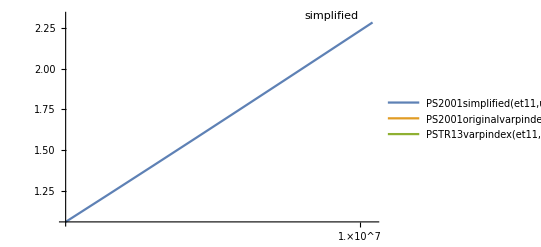

```mathematica
(*Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig0.txt",Cases[*)LogLogPlot[{PS2001simplified[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],PS2001originalvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1],PSTR13varpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]},{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"simplified","original","TR13"},Above]
,PlotLegends->"Expressions",Ticks->{{#,1000#}&/@FindDivisions[{0.,100000.0},13]//N,Automatic},ScalingFunctions->{"Log","Log"}](*,Line@x__->x,Infinity],"Table"]*)
```

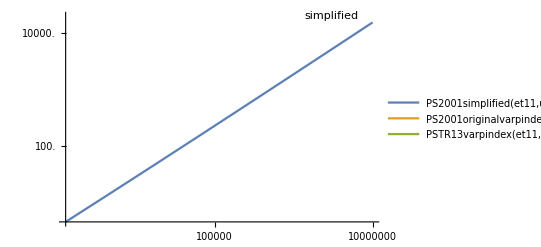

```mathematica
(*Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig0.txt",Cases[*)
(*250521 DID it stencil SOS It works!*)LogLogPlot[{PS2001simplified[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],PS2001originalvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1],PSTR13varpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]},{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"simplified","original","TR13"},Above]
,PlotLegends->"Expressions",Ticks->{{{0.0016,1 },{0.016,10 },{0.16, 10^2 },{1.6, 10^3 },{16.0, 10000},{160.0, 100000},{1600.0, 1000000},{16000.0, 10000000},{160000.0, 100000000},{1600000.0, 1000000000}},{0.0000001,0.00001,0.01,1.0,100.0,10000.0,1000000}},ScalingFunctions->{"Log","Log"}](*,Line@x__->x,Infinity],"Table"]*)
```

```mathematica
(*280421 SOS only run this for the plot. else,leave it out of the loop, cos it causes it to somehow get stuck! SOS*)
(*260421  it works center-right legend*)
(*Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig0.txt",Cases[*)
(*250521 DID it stencil SOS It works!*)If[plottestplots==1.0,Manipulate[LogLogPlot[{PS2001simplified[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],PS2001originalvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1],PSTR13varpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]},{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,(*PlotLabels->Placed[{"simplified","original","TR13"},Above],*)PlotLegends->Placed[{"simplified","original","TR13"},Center(*Center-Right works but it wont accept it as part of the big run. So use c-r only for plotting good fig, alse leave it as is for runs*)],AxesLabel-> {"E(GeV)","transform factor"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, 10^2 },{1.6, 10^3 },{16.0, 10000},{160.0, 100000},{1600.0, 1000000},{16000.0, 10000000},{160000.0, 100000000},{1600000.0, 1000000000}},{0.0000001,0.00001,0.01,1.0,100.0,10000.0,1000000}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["transform_factor" vs  "E" ["GeV"],Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*230621 sos adding now ticks etc correctly based on EXISTING figs which were already done like that! presetticks and their values, for each axis!*)
(*170621 SOS frames work now rom comments fig fix*)
(*280421 SOS only run this for the plot. else,leave it out of the loop, cos it causes it to somehow get stuck! SOS*)
(*260421  it works center-right legend*)
(*Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig0.txt",Cases[*)
(*250521 DID it stencil SOS It works!*)If[plottestplots==1.0,Manipulate[LogLogPlot[{PS2001simplified[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],PS2001originalvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1],PSTR13varpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]},{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,(*PlotLabels->Placed[{"simplified","original","TR13"},Above],*)PlotLegends->Placed[{"simple","PS","TR"},Center],Frame-> True,AxesLabel-> {"E(GeV)","transform factor"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},
FrameLabel->{"E(GeV)","transform factor"},FrameTicks->{{{0.0016,1 },{0.016,"10^1" },{0.16,"10^2" },{1.6,"10^3" },{16.0,"10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{ {0.00000001,"10^-8"},{0.000001,"10^-6"},{0.0001,"10^-4"},{0.01,"10^-2"},{1.0,"10^0"},{100.0,"10^2"},{10000.0,"10^4"} } },ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["transform_factor" vs  "E" ["GeV"],Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
33
```

33

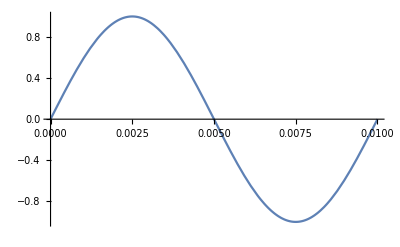

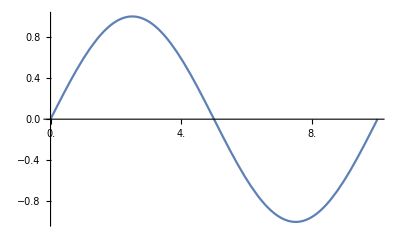

```mathematica
(*230421 SOS this is it SOS just copypaste it*)
(*https://mathematica.stackexchange.com/questions/78204/how-to-change-plot-unit-or-scale-the-number-of-axis*)
Plot[Sin[200 Pi t],{t,0.,.01}]

Plot[Sin[200 Pi t],{t,0.,.01},Ticks->{{#,1000 #}&/@FindDivisions[{0.,.01},5]//N,Automatic}]
```

```mathematica
(*220720 something with the alignement in 3D, find out and verify vs TR13 fig. 2*)
(*220720B SOS phi1 is X,Y angle (azimuth in XYZ cartesian). phi2 is elevation. So just stick with X axis velocity for now, try to nail the orientation for simple case of TR13 paper figure! Need to achieve a match!*)
(*220720 gammalorentz 5, 10 in TR13. i.e. u=0.9798 (gamma=5.001), and u=0.995 (gamma=10.01)*)
(*220720B MATCH! TR13 fig. 2 TOP (gamma=10). NXT, we do it for gamma=5, bottom fig. 2 of TR13.*)

If[plottestplots==1.0,
LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,
PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:1.2 rad","PSTR13vpind/PS2001varpind:0.5 rad","PSTR13vpind/PS2001varpind:0.1 rad"},Above]
,AxesLabel-> {"E(erg)","transform factor ratio"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""}]]
```

```mathematica
(*220720 something with the alignement in 3D, find out and verify vs TR13 fig. 2*)
(*220720B SOS phi1 is X,Y angle (azimuth in XYZ cartesian). phi2 is elevation. So just stick with X axis velocity for now, try to nail the orientation for simple case of TR13 paper figure! Need to achieve a match!*)
(*220720 gammalorentz 5, 10 in TR13. i.e. u=0.9798 (gamma=5.001), and u=0.995 (gamma=10.01)*)
(*220720B MATCH! TR13 fig. 2 TOP (gamma=10). NXT, we do it for gamma=5, bottom fig. 2 of TR13.*)

If[plottestplots==1.0,Manipulate[LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]},{et11,1GeV,10000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,
PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:1.2 rad","PSTR13vpind/PS2001varpind:0.5 rad","PSTR13vpind/PS2001varpind:0.1 rad"},Above]
,AxesLabel-> {"E(GeV)","transform factor ratio"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},
Ticks->{{{0.0000016,0.001 },{0.000016,0.01 },{0.00016,0.1 },{0.0016,1 },{0.016,10 },{0.16, 10^2 },{1.6, 10^3 },{16.0, 10000},{160.0, 100000},{1600.0, 1000000},{16000.0, 10000000},{160000.0, 100000000},{1600000.0, 1000000000}},{0.0001,0.0005,.001,0.005,0.01,0.05,0.1,0.5,1.0}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["transform_factor_ratio" vs  "E" ["GeV"],Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*260621b sos frames did with specific format for each, cpste from existing stuff sigmainel, ndens etc. applying it here now!*)
(*170621B SOS did it ticks, frames, etc all work well together. only some scientific noation units issue left, *)
(*220720 something with the alignement in 3D, find out and verify vs TR13 fig. 2*)
(*220720B SOS phi1 is X,Y angle (azimuth in XYZ cartesian). phi2 is elevation. So just stick with X axis velocity for now, try to nail the orientation for simple case of TR13 paper figure! Need to achieve a match!*)
(*220720 gammalorentz 5, 10 in TR13. i.e. u=0.9798 (gamma=5.001), and u=0.995 (gamma=10.01)*)
(*220720B MATCH! TR13 fig. 2 TOP (gamma=10). NXT, we do it for gamma=5, bottom fig. 2 of TR13.*)

(*160621 Gustavo,s suggestions on figs frames, less clutter, less talk within fig*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]},{et11,1GeV,10000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,
PlotLabels->Placed[{"TR/PS:1.2 rad","TR/PS:0.5 rad","TR/PS:0.1 rad"},Above]
,AxesLabel-> {"E(GeV)","transform factor ratio"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},
FrameTicks->{{{0.0000016,"10^-3"},{0.000016,"10^-2"},{0.00016,"10^-1"},{0.0016,1 },{0.016,"10" },{0.16, "10^2"},{1.6, "10^3" },{16.0, "10^4"},{160.0,"10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0,"10^8"},{1600000.0, "10^9"}},{ {0.0001,"10^-4"},(*{0.0005,"5x10^-4"},*){0.001,"10^-3"},(*{0.005,"5x10^-3"},*){0.01,"10^-2"},(*{0.05,"5x10^-2"},*){0.1,"10^-1"},(*{0.5,"0.5"},*){1.0,"1"}}},ScalingFunctions->{"Log","Log"},Frame->True,
FrameLabel->{"E(GeV)","transform factor ratio"},(*PlotLabel->Style["transform_factor_ratio" vs  "E" ["GeV"],Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
vf
```

vf

```mathematica
Ticks->{{{0.0016,1 },{0.016,10 },{0.16, 10^2 },{1.6, 10^3 },{16.0, 10000},{160.0, 100000},{1600.0, 1000000},{16000.0, 10000000},{160000.0, 100000000},{1600000.0, 1000000000}},{0.0000001,0.00001,0.01,1.0,100.0,10000.0,1000000}},ScalingFunctions->{"Log","Log"}
```

```mathematica
(*export plot data 230421*)
Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig2.txt",Cases[LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,
PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:1.2 rad","PSTR13vpind/PS2001varpind:0.5 rad","PSTR13vpind/PS2001varpind:0.1 rad"},Above]
,AxesLabel-> {"E(erg)","transform factor"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""}],Line@x__->x,Infinity],"Table"]
```

D:\archivedwl-126\data_results_nemiss_output\med_res\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\torblob18dummies\tr13multifig2.txt

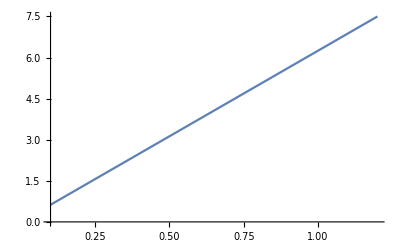

{{0.1,0.625},{0.11,0.6875},{0.12,0.75},{0.13,0.8125},{0.14,0.875},{0.15,0.9375},{0.16,1.},{0.17,1.0625},{0.18,1.125},{0.19,1.1875},{0.2,1.25},{0.21,1.3125},{0.22,1.375},{0.23,1.4375},{0.24,1.5},{0.25,1.5625},{0.26,1.625},{0.27,1.6875},{0.28,1.75},{0.29,1.8125},{0.3,1.875},{0.31,1.9375},{0.32,2.},{0.33,2.0625},{0.34,2.125},{0.35,2.1875},{0.36,2.25},{0.37,2.3125},{0.38,2.375},{0.39,2.4375},{0.4,2.5},{0.41,2.5625},{0.42,2.625},{0.43,2.6875},{0.44,2.75},{0.45,2.8125},{0.46,2.875},{0.47,2.9375},{0.48,3.},{0.49,3.0625},{0.5,3.125},{0.51,3.1875},{0.52,3.25},{0.53,3.3125},{0.54,3.375},{0.55,3.4375},{0.56,3.5},{0.57,3.5625},{0.58,3.625},{0.59,3.6875},{0.6,3.75},{0.61,3.8125},{0.62,3.875},{0.63,3.9375},{0.64,4.},{0.65,4.0625},{0.66,4.125},{0.67,4.1875},{0.68,4.25},{0.69,4.3125},{0.7,4.375},{0.71,4.4375},{0.72,4.5},{0.73,4.5625},{0.74,4.625},{0.75,4.6875},{0.76,4.75},{0.77,4.8125},{0.78,4.875},{0.79,4.9375},{0.8,5.},{0.81,5.0625},{0.82,5.125},{0.83,5.1875},{0.84,5.25},{0.85,5.3125},{0.86,5.375},{0.87,5.4375},{0.88,5.5},{0.89,5.5625},{0.9,5.625},{0.91,5.6875},{0.92,5.75},{0.93,5.8125},{0.94,5.875},{0.95,5.9375},{0.96,6.},{0.97,6.0625},{0.98,6.125},{0.99,6.1875},{1.,6.25},{1.01,6.3125},{1.02,6.375},{1.03,6.4375},{1.04,6.5},{1.05,6.5625},{1.06,6.625},{1.07,6.6875},{1.08,6.75},{1.09,6.8125},{1.1,6.875},{1.11,6.9375},{1.12,7.},{1.13,7.0625},{1.14,7.125},{1.15,7.1875},{1.16,7.25},{1.17,7.3125},{1.18,7.375},{1.19,7.4375},{1.2,7.5}}

```mathematica
Plot[x/(1.6*10^(-1)),{x,0.1,1.2}]
Table[{x,x/(1.6*10^(-1))},{x,0.1,1.2,0.01}]
```

```mathematica
Export["output.txt",Cases[Plot[Sin[x],{x,0.1,1.2}],Line@x__->x,Infinity],"Table"]
```

output.txt

```mathematica
(*220720 something with the alignement in 3D, find out and verify vs TR13 fig. 2*)
(*220720B SOS phi1 is X,Y angle (azimuth in XYZ cartesian). phi2 is elevation. So just stick with X axis velocity for now, try to nail the orientation for simple case of TR13 paper figure! Need to achieve a match!*)
(*220720 gammalorentz 5, 10 in TR13. i.e. u=0.9798 (gamma=5.001), and u=0.995 (gamma=10.01)*)
(*220720B MATCH! TR13 fig. 2 TOP (gamma=10). NXT, we do it for gamma=5, bottom fig. 2 of TR13.*)

If[plottestplots==1.0,Export["D:\\archivedwl-126\\data_results_nemiss_output\\med_res\\phi1_sixty_degrees_phi2_zero_img_geom_case_2_two\\torblob18dummies\\tr13multifig1.txt",Cases[LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,1.2,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.5,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.1,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,
PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:1.2 rad","PSTR13vpind/PS2001varpind:0.5 rad","PSTR13vpind/PS2001varpind:0.1 rad"},Above]
,AxesLabel-> {"E(erg)","transform factor"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""}],Line@x__->x,Infinity],"Table"]]
```

```mathematica
Quantity[GeVplot,0.00160217646]
```

0.00160218 GeVplot

```mathematica
data1344
```

data1344

```mathematica
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,LogLogPlot[{PSTR13varpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.9798,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.9798,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:0.349 rad gamma 10","PSTR13vpind/PS2001varpind:0.349 rad gamma 5","PSTR13vpind/PS2001varpind:0.1 rad gamma 30"},Above]]]
```

```mathematica
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{PSTR13varpindex[et11,0.9798,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"PSTR13vpind/PS2001varpind:0.349 rad gamma 5","PSTR13vpind/PS2001varpind:0.349 rad gamma 10","PSTR13vpind/PS2001varpind:0.349 rad gamma 30"},Above],PlotLegends->Placed[{"Γ=5","Γ=10","Γ=30"},Center-Right],AxesLabel-> {"E(GeV)","transform ratio"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, 10^2 },{1.6, 10^3 },{16.0, 10000},{160.0, 100000},{1600.0, 1000000},{16000.0, 10000000},{160000.0, 100000000},{1600000.0, 1000000000}},{0.0001,0.001,0.01,1.0,10.0,100.0,1000}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["transform_ratio vs E[GeV] @(los,u)=.349 rad" ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*230621 added ticks specific to notation*)
(*170621B fixed frame labels, etc thingy here *)(*170621 polished by rom dirs*)
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{PSTR13varpindex[et11,0.9798,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.995,0.0,0.0,0.349,0.0,protonindex1],PSTR13varpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]/PS2001originalvarpindex[et11,0.999446,0.0,0.0,0.349,0.0,protonindex1]},{et11,1GeV,1000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"TR/PS, γ=5","TR/PS, γ=10","TR/PS, γ=30"},Above],(*PlotLegends->Placed[{"Γ=5","Γ=10","Γ=30"},Center-Right],*)AxesLabel-> {"E(GeV)","transform ratio, θ=0.349"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},

FrameTicks->{{{0.0000016,"10^-3"},{0.000016,"10^-2"},{0.00016,"10^-1"},{0.0016,1 },{0.016,"10" },{0.16, "10^2"},{1.6, "10^3" },{16.0, "10^4"},{160.0,"10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0,"10^8"},{1600000.0, "10^9"}},{ {0.0001,"10^-4"},(*{0.0005,"5x10^-4"},*){0.001,"10^-3"},(*{0.005,"5x10^-3"},*){0.01,"10^-2"},(*{0.05,"5x10^-2"},*){0.1,"10^-1"},(*{0.5,"0.5"},*){1.0,"1"},{10,"10^1"},{100,"10^2"},{1000,"10^3"},{10000,"10^4"},{100000,"10^5"},{1000000,"10^6"}}},Frame-> True,FrameLabel->{"E(GeV)","transform ratio"},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["transform_ratio vs E[GeV] @(los,u)=.349 rad" ,Medium]*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
Subscript[aferimu, xx]=ToExpression/@pinakakioldcode[[6]]
Subscript[u, xx]=Subscript[aferimu, xx][[1]]
(*300919 verify it is a real number indeed*)
Subscript[u, xx]/2.0

Subscript[aferimu, yy]=ToExpression/@pinakakioldcode[[8]]
Subscript[u, yy]=Subscript[aferimu, yy][[1]]
(*300919 verify it is a real number indeed*)
Subscript[u, yy]/2.0

Subscript[aferimu, zz]=ToExpression/@pinakakioldcode[[10]]
Subscript[u, zz]=Subscript[aferimu, zz][[1]]
(*300919 verify it is a real number indeed*)Subscript[u, zz]/2.0
cosphi1=Cos[phi1];
cosphi2=Cos[phi2];
sinphi1=Sin[phi1];
sinphi2=Sin[phi2];
lx1=Cos[phi1]*Cos[phi2];
lx2=Sin[phi1]*Cos[phi2];
lx3=Sin[phi2];
sij=Sin[losu];
si2j=Sin[losu]*Sin[losu];

(*BEAM's Lorentz gamma factor*)
Subscript[β, b]=√((Subscript[u, xx])^2+(Subscript[u, yy])^2+(Subscript[u, zz])^2);
Γ=1/(√(1-(Subscript[β, b])^2));
coslosu=((lx1*Subscript[u, xx])+(lx2*Subscript[u, yy])+(lx3*Subscript[u, zz]))/(Subscript[β, b]+0.0000000001);
```

{-0.378}

-0.378

-0.189

{0.548}

0.548

0.274

{0.124}

0.124

0.062

```mathematica
Print[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]," angles ",phi1,phi2," speed ",Subscript[β, b] ,"tsa tsa tsa","  ",coslosu,lx1,lx2,lx3]

Print[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]," angles ",phi1,phi2," speed ",βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]] ,"tsa tsa tsa","  ",coslosufn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],lx1fn[phi1,phi2],lx2fn[phi1,phi2],lx3fn[phi2]]


PS2001feppn[500GeV]
PS2001feppndepend[500GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
(*261119 here we check the newly added gammafn dependence of ps2001 (was left with the constasnt gammalorentz! OOPS!)*)
PS2001feppndependgamma[500GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]
PS2001feppndependgammavarpindex[500GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,protonindex1]

(*SOS os edo edited 051019 We altered coslosufn, si2jdepends, losufn, etc to only depend of velocity components and on angles. PS2001 WORKS OK! FUNCTIONALIZATION IS FINALLY BASED AROUND ANGLES, imitating rlos2 for cam obsc. For radiograph, piece of cake!*)
(*
Subscript[β, b]=0.99
coslosu=0.0
PS2001feppn[1000GeV]

Subscript[β, b]=0.99
coslosu=0.99
PS2001feppn[1000GeV]
*)
```

-0.3780.5480.124 angles 0.3471985.×10^-7 speed 0.677174tsa tsa tsa  -0.2495370.940330.3402645.×10^-7

-0.3780.5480.124 angles 0.3471985.×10^-7 speed 0.677174tsa tsa tsa  0.249537-0.94033-0.340264-5.×10^-7

0.528159

1.45277

0.946526

0.946526

```mathematica
V
```

2.03152×10^10

```mathematica
(*VELOCITY IS BETTER COS IT IS IN C UNITS IN PLUTO's Relativistic modules*)

(*Expression for slow (thermal) jet proton flux.VY is local jet cells' speed component
parallel to jet axix (for non-precessing jet). For precessin jet, need to use component expression for ujet*)
(*SOS FOR NOW WE USE SCALAR VELOCITY< APPROXIMATELY EQUAL TO VY.*)
(Subscript[J, sp]=V *ndens;) 
(*091019 here we add slow proton density functionaslized dependence. MAy also need to do the same for magnetic field, cause both those stuff are location-dependent in the dataset.  *)
(*
βbfn=Function[{uxx,uyy,uzz},√((uxx)^2+(uyy)^2+(uzz)^2)];
(*230419 careful V has dimensions SI, cos it is used later on with Jsp flux calcs.*)
V=Subscript[β, b]*c;
Vfn=Function[{βbeam},βbeam*c];
*)
(*091019 SOS altered Vfn definition to directly incude velocity components*)
Jspfn=Function[{uxx,uyy,uzz,ndensity},Vfn[uxx,uyy,uzz] *ndensity];
(*Expression for slow (thermal) jet proton flux.VY is local jet cells' speed component
parallel to jet axix (for non-precessing jet). For precessin jet, need to use component expression for ujet*)
```

```mathematica
(*091019  density thingy works here OK in Jspfn. SOS also with velocity component structure of Vfn! *)
Print[Jspfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],ndens],"   ",Jsp,Subscript[J, sp]]
```

4.26619×10^21   Jsp4.26619×10^21

```mathematica
(*Fast (non-thermal) proton flux*)



Jp=Function[{mm},Jsp*(c/(4*Pi))*Subscript[K, 1]*PS2001fn[mm]];

Jpepp=Function[{mm},Jsp*(c/(4*Pi))*Subscript[K, 1]*PS2001feppn[mm]];
Jpeppdepend=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},Jsp*(c/(4*Pi))*Subscript[K, 1]*PS2001feppndepend[mm,uxx,uyy,uzz,phi1sub,phi2sub]];
(*261119 added the gamalorentzfn ps2001 version !*)
Jpeppdependgamma=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub},Jsp*(c/(4*Pi))*Subscript[K, 1]*PS2001feppndependgamma[mm,uxx,uyy,uzz,phi1sub,phi2sub]];
(*091019 here we add slow proton density functionaslized dependence. MAy also need to do the same for magnetic field, cause both those stuff are location-dependent in the dataset.  *)
Jpeppdependndens=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},Jspfn[uxx,uyy,uzz,ndensity]*(c/(4*Pi))*Subscript[K, 1]*PS2001feppndepend[mm,uxx,uyy,uzz,phi1sub,phi2sub]];
Jpeppdependndensgamma=Function[{mm,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},Jspfn[uxx,uyy,uzz,ndensity]*(c/(4*Pi))*Subscript[K, 1]*PS2001feppndependgamma[mm,uxx,uyy,uzz,phi1sub,phi2sub]];

(* 021019 commented this out, cos we now read this bit from the data file! Same value basically!
Eth=1.22*GeV;
*)
```

```mathematica
(*091019 Jpeppdependndens works OK *)
Print[ Jpeppdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],Jpeppdependndensgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],"   ",Jpeppdepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],"   ",Jpeppdependgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],,"   ",Jpepp[1000GeV]]
```

4.43886×10^372.89205×10^37   1.04047×10^16 Jsp   6.77901×10^15 JspNull   3.78266×10^15 Jsp

```mathematica
Jpepp[1000GeV]
Jsp
Subscript[J, sp]
ndens
fff
V
BB
BBB
tsip
fffvscalar
```

3.78266×10^15 Jsp

Jsp

4.26619×10^21

2.1×10^11

2.1×10^11

2.03152×10^10

1.

1.00995×10^6

tsip

Function[{uxx,uyy,uzz},Vfn[uxx,uyy,uzz]]

```mathematica
Eπ=0.9 Ep;
(*220720B  SOS was wrong! A barn is 10^-28 SI, i.e. 10^-24 CGS,not 27, as it was! Now it is 10 times smaller, so OK! *)
σinpp=Function[{vv},1/10^28(0.25 Lf[En/vv]^2+1.88 Lf[En/vv]+34.3) (1-(Eth/(En/vv))^4)^2];
σinelaspp=Function[{vv},1/10^28(0.25 Lf[vv]^2+1.88 Lf[vv]+34.3) (1-(Eth/vv)^4)^2];
```

```mathematica
(* 12-08-2014 SOS fast proton is a distro whose density is obtained either  through another transport eqn ot through the calcs of our previous paper. FOR NOW JUST SET IT TO A VALUE MUCH SMALLER THAN SLOW PROTONS' ndens*)
(*UPDATE THIS NDENSEFAST CAN BE EXTRACTED FROM Jp which is flux of fast protons. Jp 
we get from PS2001 or TR13 expressions. DO IT.

SOS MAJOR POINT VERIFY RELATION BETWEEN Np AND Jp COULD IT BE SOMETHING ELSE GOING ON HERE? CHECK!!
*)

ndensefast=ndens/1000000;

aferimndensefastdivisor=ToExpression/@pinakakioldcode[[36]]
ndensefastdivisor=aferimndensefastdivisor[[1]]
(*300919 verify it is a real number indeed*)
ndensefastdivisor/2.0
(*031019 we now do it the division*)
ndensefast=ndens/ndensefastdivisor;
(*SOS 091919 we must also functionalize ndensefast! fast proton density!! SOS!*)
ndensefastfnsnonplaw=Function[{ndensity,divisorlocal},ndensity/divisorlocal]

(*230419 SOS at some point around perhaps 2016 we introduced a power law for the fast proton distro, better than the above ndens/million*)
```

{1.×10^6}

1.×10^6

500000.

Function[{ndensity,divisorlocal},ndensity/divisorlocal]

```mathematica
(*091019 ndensefastfnnonplaw works OK!*)
Print[ndensefastfnsnonplaw[ndens,ndensefastdivisor],"    ", ndensefast]
```

210000.    210000.

```mathematica
Subscript[u, b]
```

2.03152×10^10

```mathematica
(*. 05 08AUG 2014. SOS OI KELNER ET AL 2006 EXOUN ALLOUS ORISMOUS GIA TA BP, KLP APO OTI OI ARGS 08. 
EMEIS EDO EXOUME BALEI TON ARGS 08, ALLA OI GRAPHIKES POU PAME NA MIMITHOUME EINAI APO TO 
KELNER ET AL 06, OXI TOUS ARGS08. EPOMENOS MALLON OI eksypnoi ARGS08 TA PSILOALLAKSAN TA RESULTS KAI TUBEKI FISIKA. NA BOUN KAI TON KELNER ET AL 06 NA 
GINEI SYGRISI.*)


(*ct1 is the normalization constant for this operation of power law 300720 SOS now read from param file!*)


(*ct1=1000000.0*)
ct1=ct1param

(*SUPER SOS 240419 added PS2001 to the end of fast proton distro power law approx.
HAD to, else it wont take into consideration PS2001 effect!!! SOS! *)
ndensefastfn=Function[{EEEE,aaa},ct1*ndens*EEEE^-aaa*PS2001feppn[EEEE]];

ndensefastfndepend=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub},ct1*ndens*EEEE^-aaa*PS2001feppndepend[EEEE,uxx,uyy,uzz,phi1sub,phi2sub]];
ndensefastfndependgamma=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub},ct1*ndens*EEEE^-aaa*PS2001feppndependgamma[EEEE,uxx,uyy,uzz,phi1sub,phi2sub]];
(*261119 
ndensefastfndependndens=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ct1*ndensity*EEEE^-aaa*PS2001feppndepend[EEEE,uxx,uyy,uzz,phi1sub,phi2sub]]*)
```

1.

```mathematica
(*210720 added varpindex*)
ndensefastfndependndens=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ct1*ndensity*EEEE^-aaa*PS2001feppndependvarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]];
(*060820 SOS added protonindex dependency in ps01 call! SOS replaced old one!*)
ndensefastfndependndensgamma=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]];


PS2001feppndependgammavarpindex;


(*071019 MUST verify this ndensefastfn power law fast proton density  functionalization! *)
(*071019 after here, next influence of angles and velocity variation from cell to cell! is in qpppowerlaw! SOS ALSO CONSIDER REPLACING PS2001 with Torres reimer etc 2011-13! check relebant paper! SOS direct replacement and comparison vital for paper results compare different models focus on that!SOS*)
```

```mathematica
(*210720 added varpindex
ndensefastfndependndensgammavarpindex=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]

(*210720 added varpindex ONLY to the subfunction (ndens already ha it SOS! CASCADE it from now on et voila! ct1 is a constant for normalization!)*)
ndensefastfndependndensgammavarpindex=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]*)

(*SOS 050820! proton power law additional exp term, from ARGS19*)
(*protonexpo is a param from file SOS add it to the relevant external param file!*)
(*050820SOS echarge in statcoulomb FIX HERE SOS! or, read from file! SOS!*)
echarge=0.001;
(*050820 from external file rjet estimated (for a given model run!) param read SOS!*)
rjetparam=1000000;
emaxprotonexpo=Function[{bxx,byy,bzz,rjet},echarge*(bxx+byy+byy)*rjet];
(*050820 SOS read proton expo from external param file!*)
protonexpo=0.0;
```

```mathematica
(*090820 SOS Ecutoff is now too large, 10^15 GeV! No! Need smaller!*)
(*090820 see plots below! cutoff works like a charm, only the Ecutoff nedds become smaller! See to it!*)
Print[bxx,byy,bzz," tf ",emaxprotonexpo[bxx,byy,bzz,rjetparam]/GeV];
```

100000.1.×10^6100000. tf 1.31072×10^12

```mathematica
(*050820 conditionally define fast proton power law, in order to (conditionally) accomodate for recent addition of expo term by args19 to this distro! *)
If [protonexpo==1.0,
ndensefastfndependndensgammavarpindex=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*Exp[-EEEE/emaxprotonexpo[bxx,byy,bzz,rjetparam]]*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]
,
(*100820 SOS added bxx,byy,bzz dependence on both versions of ndense! cant have two versions down below, simply bfields wont be used in zero-null protonexpo case!*)
ndensefastfndependndensgammavarpindex=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]
];
```

```mathematica
(*090820 test versions of ndense! ABOVE, added cutoff E, aka ARGS19. NOW, just testing it!*)
ndensefastfndependndensgammavarpindexnocutoff=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]];

ndensefastfndependndensgammavarpindexyescutoff=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*Exp[-EEEE/emaxprotonexpo[bxx,byy,bzz,rjetparam]]*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]];
```

```mathematica
(*090820 Conditionally plot no cutoff test ndens p-law fn from above*)
If[plottestplots==1.0,
LogLogPlot[Evaluate[ndensefastfndependndensgammavarpindexnocutoff[et,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,bxx,byy,bzz]],{et,100GeV,100000000000000GeV},PlotRange->All]//Print]
```

```mathematica
(*090820 Conditionally plot yes cutoff test ndens p-law fn from above*)
If[plottestplots==1.0,
LogLogPlot[Evaluate[ndensefastfndependndensgammavarpindexyescutoff[et,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,bxx,byy,bzz]],{et,100GeV,100000000000000GeV},PlotRange->All]//Print]
```

```mathematica
(*280421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[Evaluate[ndensefastfndependndensgammavarpindexyescutoff[et,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,bxx,byy,bzz]],{et,100GeV,100000000000000GeV},PlotRange->{{1,1000000000000},{10^-36,10^14}}(*All*),PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"ndens_cutoff"},Right],PlotLegends->Placed[{"ndenscutoff"},Center-Right],AxesLabel-> {"E(GeV)","hot p  density"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0,"10^9"},{16000000.0,"10^10"},{160000000.0,"10^11"},{1600000000.0, "10^12"},{16000000000.0,"10^13"},{160000000000.0,"10^14"},{1600000000000.0, "10^15"}},{0.00000000000000000000000000000000001,0.00000000000000000000001,0.0000000000001,0.0000001,0.0001,1.0,{1000.0,"10^3"},{10000000.0,"10^7"},{100000000000000,"10^14"}}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["ndens_cutoff vs E[GeV] @Ecutoff=1.3*e12 GeV" ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
(*280421 excerpt from code above! demoes how ecutoff is calced!

rjetparam=1000000;
emaxprotonexpo=Function[{bxx,byy,bzz,rjet},echarge*(bxx+byy+byy)*rjet];
(*050820 SOS read proton expo from external param file!*)
protonexpo=0.0;*)
```

```mathematica
(*230621 commented out legend*)
(*220621 polish and finish this!*)
(*280421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[Evaluate[ndensefastfndependndensgammavarpindexyescutoff[et,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,bxx,byy,bzz]],{et,100GeV,100000000000000GeV},PlotRange->{{1,1000000000000},{10^-36,10^14}}(*All*),PlotPoints->28,MaxRecursion->0,(*PlotLabels->Placed[{"ndens_cutoff"},Right],*)
(*PlotLegends->Placed[{"ndenscutoff"},Center-Right],*)AxesLabel-> {"E(GeV)","non-thermal p density"},FrameLabel->{"E(GeV)","non-thermal p density"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Frame->True,FrameTicks->{{{0.0016,1 },(*{0.016,10 },*){0.16, "10^2" },(*{1.6, "10^3" },*){16.0, "10^4"},(*{160.0, "10^5"},*){1600.0, "10^6"},(*{16000.0, "10^7"},*){160000.0, "10^8"},(*{1600000.0,"10^9"},*){16000000.0,"10^10"},(*{160000000.0,"10^11"},*){1600000000.0, "10^12"},(*{16000000000.0,"10^13"},*){160000000000.0,"10^14"},(*{1600000000000.0, "10^15"}*){16000000000000.0, "10^16"}},{{0.0000000000000000000000000000000000000001,"10^-40"},{0.000000000000000000000000000001,"10^-30"},{0.00000000000000000001,"10^-20"},{0.0000000001,"10^-10"},{1.0,"10^0"},(*{100000.0,"10^5"},*){10000000000.0,"10^10"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["ndens_cutoff vs E[GeV] @Ecutoff=1.3*e12 GeV" ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
(*280421 excerpt from code above! demoes how ecutoff is calced!

rjetparam=1000000;
emaxprotonexpo=Function[{bxx,byy,bzz,rjet},echarge*(bxx+byy+byy)*rjet];
(*050820 SOS read proton expo from external param file!*)
protonexpo=0.0;*)
```

```mathematica
xxxi
```

xxxi

```mathematica
Print[ndensefastfn[1000GeV,2],"   ",ndensefastfndepend[1000GeV,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],"    ",ndensefastfndependgamma[1000GeV,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],"  dds  ",ndensefastfndependndens[1000GeV,protonindex1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens]," ds  ",ndensefastfndependndensgamma[1000GeV,protonindex1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens]
ndensefastfndependndensgammavarpindex[1000GeV,protonindex1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,bxx,byy,bzz]]

(*071019 VERIFED both the above this functionalizations. General method for those checks /verifications:  Subscript[u, xx] etc are values, uxx etc are integr parameters, which are passed as params values the aforementioned indexed ones! After assigning values to indexed ones, WE MUST NOT CHANGE THEM THROUGHOUT, for checks to be correct! called values, on the other hand, are assigned as function call values!*)
(*091019 on top of the above, also VERIFIED ndensefastfnndens functionalization*)
(*091019 VERIFIED also qpp ndens*)
```

1.0802×10^10   2.97123×10^10    1.93585×10^10  dds  2.97123×10^10 ds  3.74752×10^20

```mathematica
(*SOS IN BOTH F AND Q WE USE EPION, NOT EPROTON
EPION=x*EPROTON SOS ARRANGE SUITABLY SOS*)

(*SOS F IS A FN OF EPION AND OF X WHERE  EPION=x*EPROTON. BUT IN L EPROTON IS USED SO WE RESORT TO epion/xxpi in place of eproton, avoiding introducing eproton directly or using it as a global var. seems OK*)

(*PROTI KYRIA SYNARTISI*)


Fπinjt=Function[{xππ,eproton},4 Subscript[B, π][(eproton)] αf[af[Lf[(eproton)]]] (1-(c^2 Subscript[m, π])/(xππ*eproton))^0.5 xππ^(αf[af[Lf[(eproton)]]]-1) ((1-xππ^αf[af[Lf[(eproton)]]])/(1+rf[af[Lf[(eproton)]]] xππ^αf[af[Lf[(eproton)]]] (1-xππ^αf[af[Lf[(eproton)]]])))^4 ((rf[af[Lf[(eproton)]]] (1-2* xππ^αf[af[Lf[(eproton)]]]))/(rf[af[Lf[(eproton)]]] (1-xππ^αf[af[Lf[(eproton)]]]) xππ^αf[af[Lf[(eproton)]]]+1)+1/(1-xππ^αf[af[Lf[(eproton)]]]))];
(*DEYTERI KYRIA SYNARTISI KAI PROTO OLOKLIROMA*)
Qpp=Function[{Eπ},ndens*ndensefast*c*NIntegrate[1/xxxi Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

Qpppowerlaw=Function[{Eπ},ndens*c*NIntegrate[ndensefastfn[Eπ/xxxi,2]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*031019 SOS do the dependency on NGLES all over code till here! VERIFY it! STEP BY STEP! ALSO, how come xxxi is not a declared VAR of the above qpp function? HOW IS THAT?*)

(*071019 xxxi is the integration variable you dumb piece of ...!*)

Qpppowerlawdepend=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub},ndens*c*NIntegrate[ndensefastfndepend[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*261119 added gamma fn in ps2001 dependence all the way to here!*)
Qpppowerlawdependgamma=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub},ndens*c*NIntegrate[ndensefastfndependgamma[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


(*091019 added ndensfn here!*)
(*260520 SOS found a bug here! ndensity, not ndens! ndensity is a variable of the function, whereas ndens is just a constant result! SOS!*)
Qpppowerlawdependndens=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ndensity*c*NIntegrate[ndensefastfndependndens[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*210720 added varpindex to ndens as well! rest happens auto as a cascade from here on, apart from wholethingy! ndensvarp... saves the day!*)
Qpppowerlawdependndensvarpindex=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex},ndensity*c*NIntegrate[ndensefastfndependndensvarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*260520 SOS found a bug here! ndensity, not ndens! ndensity is a variable of the function, whereas ndens is just a constant result! SOS!*)
Qpppowerlawdependndensgamma=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},ndensity*c*NIntegrate[ndensefastfndependndensgamma[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 SOS added dependency to Qpp on EXISTING (within ndensefastfndependndensgamma) proton index facility!*)
(*210720 added varpindex to ndens, in the sese that it now calls ps01varpindex, else even original ndensplaw has varpindex facility! the new one just calls pso1varpindex!*)
(*100820 SUPER SOS added b dependence to qpp as well, due to expo cut off!! dependent on B*)
Qpppowerlawdependndensgammavarpindex=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz},ndensity*c*NIntegrate[ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


CFQpppowerlawdependndens=Compile[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},Qpppowerlawdependndens[Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]];

CFQpppowerlawdependndensvarpindex=Compile[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex},Qpppowerlawdependndensvarpindex[Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex]];


CFQpppowerlawdependndensgamma=Compile[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity},Qpppowerlawdependndensgamma[Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]];
(*210720 oops added calling varpindex here as well!*)
CFQpppowerlawdependndensgammavarpindex=Compile[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz},Qpppowerlawdependndensgammavarpindex[Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz]];

(*
ndensefastfn=Function[{EEEE,aaa},ct1*ndens*EEEE^-aaa*PS2001feppn[EEEE]]

ndensefastfndepend=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub},ct1*ndens*EEEE^-aaa*PS2001feppndepend[EEEE,uxx,uyy,uzz,phi1sub,phi2sub]]
*)









(*SOS alpha=2 in ps2001 is other than the alpha function in the neutrino calculations SUPER SOS DISTINGUISH THR TWO SOS!!! *)

σinpp[0.1];

αf[af[Lf[Ep]]]-1

Subscript[B, π][Ep];
Fπinj[0.2];

(* DEYTEREYONTA SXOLIA EDO  -280714- SOS this bit seems to be behaving reasonably, drops with E, which it should, since it
is particles per given energy out of a given setup, which is less and less as their expected energy goes up*)
(*Double check everything so far and then we seem to be good to go from here. This injection function stuff
is to replace the 1/x source fn in the transport equation, RHS. double check and then insert it :). *)
```

-0.431581

```mathematica
xxxi=0.9
(*200720 added a variable protonindex, aka args19
protonindex1=2
*)
(*210720 protonindex1 now set equal to alpha early on in the code. Alpha is read from the param file.*)

Print[Fπinjt[0.8,1000GeV],"  ",Qpp[1000GeV],"  ",Qpppowerlaw[1000GeV],"   ",Qpppowerlawdepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2], "     ", Qpppowerlawdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],"   ",Qpppowerlawdependndensgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],Qpppowerlawdependndensgammavarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,protonindex1,bxx,byy,bzz],
CFQpppowerlawdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],"   ",CFQpppowerlawdependndensgamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens],CFQpppowerlawdependndensgammavarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens,protonindex1,bxx,byy,bzz]]
```

0.9

0.00617374  2126.85  1707.27   4696.08     4696.08   3059.643059.644696.08   3059.643059.64

```mathematica
0
```

0

```mathematica
Eπ
```

0.576784

```mathematica
xxxi=0.9
Print[Fπinjt[0.8,1000GeV],"  ",Qpp[1000GeV],"  ",Qpppowerlaw[1000GeV],"   ",Qpppowerlawdepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2], "     ", Qpppowerlawdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens]]
```

0.9

0.00617374  2126.85  1707.27   4696.08     4696.08

```mathematica
(*171019 sos moved this BEFORE the tpion fn def! else wont work as tesc is NOT a fn param! 161019 SUPER SOS this little value tesc=(zmax-z)/c (from reynoso romero paper) affects wether we get any emission at all! too small and it cools off rapidly, particle escape time from the jet system! A tenner works fine as it is now, a unit not so much!!*)
(*230720 SOS add tesc to outside param file! SUPERSOS*)
tesc=0.01;
tesc=10.0;
(*230720 try make uanal drop faster!*)
tesc=20.0;
(*230720B it works! tesc=20 makes it drop 6 OOM, instead  of just 4 with tesc=10! Now try 30 or something!*)
tesc=30.0;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
(*050820 SOS tesc do it here! conditionally employ the hillas energy! ARGS19!*)

(*050820 WTF! so crude the above! tloss^-1 is the sum of tloss times ^-1, calced with complex formulae in all this! And used through bbpi!*)
tloss=0.01;
tlossexact=Function[{mm},1/mm];
Subscript[Γ, π]=Epion/(Subscript[m, π]*c^2);
(*161019 pion mean lifetime, i.e. decay time. To be added to tesc to get a time scale for pion measly existence as an intermediate emission facilitator! SOS 161019 we has assigned a small tesc. based on the esc time from just a cell. But this means it cools off too fast i.e. no emission!We need tesc larger, i.e. consider zj the size of the whole system, not just a cell! Here we do a simplification! a pion from a cell moves on to another cell, etc, and may cause emission there! In order to properly track all those, a 3D calc turns out to be 6D, double D. IMpossible to perform! So we just take each cell to be huge, same size as the system, for pion tesc calculations! This has an effect of losing some accuracy, flattenning the spatial detail of pion distro, yet it is a meaningful approx, as we base the calc on slow proton hydrodynamic density! Travelling pions, from bits of higher energy shall raise emission from lower energy and velocity pieces and vice versa! But we localize this emission moar than in reality through our simplification here! A SIDE EFFECT OF CONVERTING CALCS FOR ST. STATE WHOLE SYSTEM JET TO A HYDROCODE BASED SIMULATION!*)
Subscript[τ, π0]=2.6*10^-8;
Subscript[τ, π]=Subscript[τ, π0]*Subscript[Γ, π];
Subscript[τ, π]=Subscript[τ, π0]*(Epion/(Subscript[m, π]*c^2));
(*tpion function: TAUPION implied! A mere functionalization of the above! *)

tpion=Function[{Epion},Subscript[τ, π0]*(Epion/(Subscript[m, π]*c^2))+tesc];

(*pp time*)
(*091019 SUPER SOS add here ndens depndence!!!*)
(* 01/04 Here we define the 
Subscript[t, πp]=Subscript[t, pp] in this case from equation 30 in Reynoso's paper where is t is t for the pion-proton decay.*)

(*tpp=Function[{EEE},1.0/((2/3)*ndens*c*σinelaspp[EEE]*Subscript[K, pp])] ;*)

(*161019 above is older version, has 2/3 in it. Below, later one, missing the 2/3. Chwck paper for this!!!*)

(*210720B SOS tpp is a function of ndens! THEREFORE dependant on plaw protonindex, etc! SOS UPDATE tpp ULTRA SOS!!!
NOPROBLEM this is slow (thermal, or bulk flow) proton density, not fast density. Therefore, no much need to apply to it conversions, etc, since it is only mildly relativistic. Also, not a distro in it, thus no distro conversion!*)
tpp=Function[{EEE},1.0/(ndens*c*σinelaspp[EEE]*Subscript[K, pp])] ;
(*310720 we should use a higher ndens for tpp only, as it is at jet base. None other t is affected from density! SOS*)
ndens
tppndens=Function[{EEE,ndensity},1.0/(ndensity*c*σinelaspp[EEE]*Subscript[K, pp])] ;
(*010820 we now add the proton pion thingy after all!SOS inherit from function call the FRACTION! SOS!!! MAYBE USE IT! for VHE! SOS!*)
(*020820 TWO CORRECTIONS! 
1.here we use Eproton=Epion/xxx!! 
tpion is a function of EPION, so we need to xpress eproton as a function of epion, which isd the argument of the function!(SEE ARGS09 eq. 30!)  
2. SOS divide by 3 , not two, cause: sigma ppion is 2/3 of sigma pp! Thus, 2/3 times 1/2 of the original, reslting to 1/3*)
(*020820 SOS corrected to to 1/t! SOS!*)
tppion=Function[{EEE,ndensity,xxx},3.0/(ndensity*c*σinelaspp[EEE/xxx]) ];
tsa!
σinelaspp[0.9*1000GeV]
1.0/tppion[1000GeV,ndens,0.99]
(*SUPER SOS HERE LIES SLOW PROTON DENSITY WE MUST FIX THIS FOR SLOW PROTON DENS UPCOMING FUNCTIONALIXZATION!*)
(*sync time*)

(*091019 SUPER SOS ADD HERE BBB DEPENDENCE SUPER SOS DO IT HERE!!!*)
```

2.1×10^11

tsa!

3.41047×10^-27

7.20697×10^-6

Eth=1.22*GeV;
(*01/04 Inelasticity coefficient from the Kelner paper 2006*)
K_pp =0.5;
(*01/04 Important functions for the t_pp based on equations 12 from the 
Reynoso's paper where σinelaspp is the corresponding cross section for inelastic pp interactions and L is a function of ln as it is given in equation 12*)σinelaspp=Function[{vv},1/10^27(0.25 Lf[vv]^2+1.88 Lf[vv]+34.3) (1-(Eth/vv)^4)^2];Lf=Function[{uu},Log[uu/(1000*GeV)]] ;



Qpp[1000GeV]

```mathematica
(*091019 verified ndens functionalization of tpp*)
Print[tpp[1000GeV],"  fgh ",tppion[1000GeV,ndens,0.99],"ippy ",tpion[1000GeV],"  ggg ",Subscript[τ, π],"    ",tppndens[1000GeV,ndens]]
```

92554.  fgh 138755.ippy 30.0002  ggg 0.0000700111    92554.

```mathematica
BBB
```

1.00995×10^6

```mathematica
(*091019 verified bfield total value functionalixation *)
Print[bfieldfn[bxx,byy,bzz],"   ",bxx,"   ",byy, "   ",bzz,"   ", Sqrt[bxx*bxx+byy*byy+bzz*bzz],"   ",BBB]
```

bfieldfn[100000.,1.×10^6,100000.]   100000.   1.×10^6   100000.   1.00995×10^6   1.00995×10^6

```mathematica
(*The equation for tsync equation 9(paper Reynoso & Romero)*)
    
Subscript[t, sync]=1.0/((4/3*(Subscript[m, e]/Subscript[m, p])^3*(Subscript[σ, T]*BBB^2)/(8*Pi* c *Subscript[m, e]))Γp);       
(*01/04 Remember how we use Function in mathematica:
Function[parameter,body of the function,in this case Subscript[t, sync]]. Not Subscript[Γ, p] because we want the independent parameter which is eppp*) 
tsyncf=Function[{eppp},1.0/((4/3*(Subscript[m, e]/Subscript[m, p])^3*(Subscript[σ, T]*BBB*BBB)/(8*Pi* c* Subscript[m, e]))((eppp)/(Subscript[m, p] c^2)))]  ;
bfieldfn=Function[{bxxvar,byyvar,bzzvar},Sqrt[bxxvar*bxxvar+byyvar*byyvar+bzzvar*bzzvar]];
(*240720 SOS tsync was WRONG ALL ALONG! It should be gammalorentz, NOT ((eppp)/(Subscript[m, p] c^2))! YET, gamma as a functio of E? hmmmm.... maybe it was correct after all! Γlorentzfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],E=Gamma|*mc^2, thus gamma=E/mc^2, correct after all! 240720 *)  

tsyncfvarmagnetic=Function[{eppp,bxxvar,byyvar,bzzvar},1.0/((4/3*(Subscript[m, e]/Subscript[m, p])^3*1/(8*Pi* c* Subscript[m, e])Subscript[σ, T]*bfieldfn[bxxvar,byyvar,bzzvar]*bfieldfn[bxxvar,byyvar,bzzvar])((eppp)/(Subscript[m, p] c^2)))]  ;

(*adb time SOS 22-08-14 use u*c COS u is in u/c units SOSARA*)
```

```mathematica
(*210720B*)
(*240720 reversed it! we also reverse it below! taccel, not to the minus1 here! SOS!*)

(*240720b 1coulomb=(c/10) stC 

SOS stC is CGS for electric charge! nearly 3 billion! we only assumed a thousand! SOS were wrong! WTF solved this 240720b! So now we have: 
electron or proton charge=1.6*10^(-27)C=1.6*10^(-27)*2,997919999.934 stC=*)
etaaccelefficiency1=0.1;
(*240720B ULTRA SOS, FROM BEGELMAN et al. 1990: FSC=(FERMI MFPATH)/(LARMOR RADIUS)*)
(*ARGS08 apparently set FSC=1.0: *)
FSC=1.0;

(*SOS 240720b where we have (ARGS08): etaaccelefficiency1=(beta(beam))^2 SO FOR FASTER BEAM, a larger eta occurs! SOS connect it to the beam speed for tadb SOS !!!*)
etaaccelefficiency1=ubeamnozzlefortadbcalc*ubeamnozzlefortadbcalc*FSC;
etaaccelefficiency1
```

0.64

```mathematica
(*240720b coulomb to statcoulomb, i.e. SI to CGS el. charge conversion!*)
1.6*10^-27*(c/10.)
c
```

4.8×10^-18

30000000000

```mathematica
(*240720b 1coulomb=2,997919999.934 stC SOS stC is CGS for electric charge! nearly 3 billion! we only assumed a thousand! SOS were wrong! WTF solved this 240720b! So now we have: 
electron or proton charge=1.6*10^(-27)C=1.6*10^(-27)*2,997919999.934 stC=*)
(*240720B taccel: the existing c is meant to be the convertion factor, divided by 10! SOS MAYBE e is in coulombs then! From statcoulomb definition! CHECK AGAIN! SUPER SOS!*)

(*310720 we use statcoulomb , no Coulomb, since CGS our units! SOS*)
taccel=Function[{ett1,etaaccelefficiency,bxxvar,byyvar,bzzvar,uxxvar,uyyvar,uzzvar},(ett1) /(etaaccelefficiency*c*(1.6*10^-27*c*2997919999.934)*bfieldfn[bxxvar,byyvar,bzzvar])];


Print[taccel[100GeV,etaaccelefficiency1,bxx,70*byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]]];
Print[1./taccel[1000GeV,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]]];
```

8.28417×10^-13

1.74162×10^9

100000.1.×10^6100000.

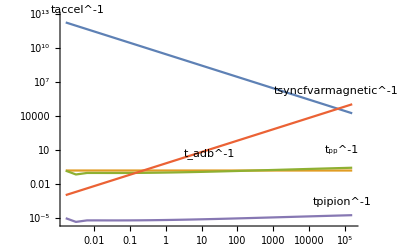

```mathematica
(*210720B LogLogplots of times! SOS shape is similar, scales are not all same ! SOS!!! CORRECT THEM!! ALSO do sinelpp comparison, ct1 fixation, etc*)
(*210720B SOS tpp in the args09 paper is around 10^1, HERE it is 10^(-4). WTF? investigate!
ALSO, tadb is kinda different, also check that out!*)

(*240720 nailed tsync vs ARGS08, was just a matter of multiplying byy default value by 70.0(byy is 10 times moar than bx, bz, in default values that is!)!*)
(*240720 also, tadb is OK, just a matter of assumed ubeam ans zj size of system! so tadb also nailed it!*)
(*240720 SOS taccel is different in ARGS09 (defined as here) and in ARGS08 where it is just the sum of the other times, ALL INVERTED! check and do!*)
(*310720 we should use a higher ndens for tpp only, as it is at jet base. None other t is affected from density! SOS*)

Print[bxx,byy,bzz];
LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],1./Subscript[t, adb],(1./tppndens[et11,ndens*10000.0]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz]),(1./tppion[et11,ndens,0.999])},{et11,1GeV,100000000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsyncfvarmagnetic^-1","tpipion^-1"},Above]]
```

```mathematica
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],1./Subscript[t, adb],(1./tppndens[et11,ndens*10000.0]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz]),(1./tppion[et11,ndens,0.999])},{et11,1GeV,100000000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Above],
PlotLegends->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Center-Right],AxesLabel-> {"E(GeV)","t^-1"},AspectRatio->1/1.0,
FrameLabel-> {"E(GeV)","t^-1"},
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{0.0001,0.001,0.01,1.0,10.0,100.0,1000, 10000.0, 100000.0, 1000000.0, 10000000.0, 100000000.0,1000000000.0, 10000000000.0, 100000000000.0, 1000000000000.0}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["t^-1 vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*190621 frame and polish it aka romr*)
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],1./Subscript[t, adb],(1./tppndens[et11,ndens*10000.0]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz]),(1./tppion[et11,ndens,0.999])},{et11,1GeV,100000000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,Frame->True, PlotLabels->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Above],
(*PlotLegends->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Center],FrameLabel->{"E(GeV)","t^-1"},*)AxesLabel-> {"E(GeV)","t^-1"},FrameLabel->{"E(GeV)","t^-1"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},FrameTicks->{{{0.0016,1 },(*{0.016,10 },*){0.16, "10^2" },(*{1.6, "10^3" },*){16.0, "10^4"},(*{160.0, "10^5"},*){1600.0, "10^6"},(*{16000.0, "10^7"},*){160000.0, "10^8"},(*{1600000.0, "10^9"},*){16000000.0, "10^10"}},
(*FrameTicks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-28,"10^-28"},{10^-27,"10^-27"},{10^-26,"10^-26"}}}*){{0.0001,"10^-4"},{0.01,"10^-2"},{1.0,"1.0"},{100.0,"10^2"}, {10000.0,"10^4"},{ 1000000.0,"10^6"},  {100000000.0,"10^8"}, {10000000000.0,"10^10"},  {1000000000000.0,"10^12"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["t^-1 vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
--
```

```mathematica
(*091019 verified tsyncf b-components' functionalization*)
Print[tesc, "  fgfsx ", tloss, Subscript[t, sync],"   ",tsyncf[1000GeV],"    ",tsyncfvarmagnetic[1000GeV,bxx,byy,bzz]]
```

30.  fgfsx 0.0110968.4   4387.34    4387.34

βbfn=Function[{uxx,uyy,uzz},√((uxx)^2+(uyy)^2+(uzz)^2)];
(*230419 careful V has dimensions SI, cos it is used later on with Jsp flux calcs.*)
V=β_b*c;
Vfn=Function[{βbeam},βbeam*c];

```mathematica
βbfn=Function[{uxx,uyy,uzz},√((uxx)^2+(uyy)^2+(uzz)^2)];
(*230419 careful V has dimensions SI, cos it is used later on with Jsp flux calcs.*)
V=Subscript[β, b]*c;
Vfn=Function[{βbeam},βbeam*c];
```

```mathematica
Print[Subscript[u, b]," ",βbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]] ,Vfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]]]
(*091019 verified new vfn component structure works*)
```

2.03152×10^10 0.677174-1.134×10^10

```mathematica
(*SOS 091019 HERE ALSO INTRODUCE ubeam FUNCTIONALIZATION SUPER SOS ubeamdependence SOS!!!*)
(*NONONO! 091019 LEAVE tadb as is, because ubeam is the jet beam speed at nozzle, tadb is just OOmagnitude calc, no need to alter it from cel to cell! LEAVE tadb alone, JUStmakesure ubeam stays at JET SPEED SOSARA SOS!!! *)
(*SOS uncovered ERROR tadb was being calced based on ubeam in CGS, NOT in c units! HUGE difference NOW!!! WTF MAN! OK cause tsyncf dominates the sum, apart from very high energies SO no big deal after all! tiny error, no problemo!*)

(*adb time SOS 22-08-14 use u*c COS u is in u/c units SOSARA
Equation 13 in Reynoso's paper*)
```

```mathematica
Print[Subscript[t, adb]];
```

6.25

```mathematica
(*091019 verified tadb functionalization, NO USE FOR FN, cause it is OOM calc, just use ubeam at nozzle from param file!!!*)
Print[tsyncf[1000GeV],"   ",Subscript[t, adb],"  fff ",Subscript[t, adbold],tadbfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],"   ",Vfn[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]]," ici ",Subscript[z, j],"   ",(ubeamnozzlefortadbcalc*c)/Subscript[z, j],ubeamnozzlefortadbcalc,Subscript[u, b],tppion[1000GeV,ndens,0.99]]
```

4387.34   6.25  fff 2.46121×10^-10-13.2275   -1.134×10^10 ici 1.×10^11   0.240.82.03152×10^10138755.

```mathematica
(*From Kelner et al. 2006, fit functions on corsika etc numerical results*)
(*approx se epp to epi, i.e. proton to pion energy, just for trying it out*)
(*tsyncf[Epi]*)


(*01/04 Here we define Subscript[b, π]=Subscript[bb, π]=b(paper)=-E*Subscript[t, loss]^(-1). Also I inserted tpp in the Subscript[b, ππ] function*)

(*01/04 Final Equation=Transport Equation of the jet*)
(*Same here about the value and not sure what Qpp is*)


(*bππ expresses the cooling rates. For pions we do not use tpp, that was for protons. We assume P-law spectrum for protons here, so no use for tπp that's why in bbπ we use only tadb kai tsync from equation 9 paper Reynoso & Romero (also see underline stuff in paper)*)

(*bpipi expresses the cooling rates. For pions we do not use tpp, that was for protons. We assume P-law spectrum for protons here, so no use for tpp*)
(*161019 SOS we did use tpp here!!! SOS leave it out now!*)

(* SOS TEST NO COOLING SOS
bbπ=Function[{Epi},Epi];*)
(*DEYTEROY EPIPEDOU BOITHITIKI SYNARTISI*)
(*010820 ADDED tppion check it need call xxx for bbpion as well! check effects! SOS times!*)
(*SOS ADD MINUS TO ALL BBP's SOS DO IT REGARDLESS OF tppion! SOS!*)
(*020820 SUPER SOS NO! we call this function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
bbπ=Function[{Epi},Epi*( (tsyncf[Epi])^-1)];
bbπtroisndens=Function[{Epi,ndensity},Epi*( (tsyncf[Epi])^-1+(Subscript[t, adb])^-1+tppndens[Epi,ndens])];
(* 161019 we leave out tpp, according to the above commentary, since it only refers to protons!! Not pions!
bbπtroisndensvarmagnetic=Function[{Epi,bxxvar,byyvar,bzzvar,ndensity},Epi*((tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adb])^-1+tppndens[Epi,ndens])]; *)
(*010820 SOS here we put a minus! was in the paper all along!*)
(*020820 SUPER SOS NO! we call this function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
bbπtroisndensvarmagnetic=Function[{Epi,bxxvar,byyvar,bzzvar,ndensity},Epi*((tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adb])^-1)]; 
(*020820 SOS we call tppion with argument Epion! but, within it, sigma needs to calc using EPROTON(ARGS09 eq 30!)! 
THUS, we need to add as argument the energy fraction xxxi to bbπ! AND pass that to it from mother functions calling bbπ later on! *)
(*010820 ADDED tppion check it need call xxx for bbpion as well! check effects! SOS times!*)
(*SOS ADD MINUS TO ALL BBP's SOS DO IT REGARDLESS OF tppion! SOS!*)
(*020820 SUPER SOS NO! we call this function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
bbπtroisndensvarmagnetictppion=Function[{Epi,bxxvar,byyvar,bzzvar,ndensity,xxxi},Epi*((tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adb])^-1+(tppion[Epi,ndensity,xxxi])^-1)]; 

(* 020820tppion=Function[{EEE,ndensity,xxx},(ndensity*c*σinelaspp[EEE/xxx])/3.0];*)

CFbbπtroisndensvarmagnetic=Compile[{Epi,bxxvar,byyvar,bzzvar,ndensity},bbπtroisndensvarmagnetic[Epi,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];
bbπold=Function[{Epi},Epi*( (tsyncf[Epi])^-1+(Subscript[t, adb])^-1)];

(*SOS ADD MINUS TO ALL BBP's SOS DO IT REGARDLESS OF tppion! SOS!*)
(*020820 SUPER SOS NO! we call this function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
(*020820 added this one! added xxxi dependence! FUR tppion in bbπ!*)
bbπvarmagnetic=Function[{Epi,bxxvar,byyvar,bzzvar},Epi*( (tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adb])^-1)];
(*010820 ADDED tppion check it need call xxx for bbpion as well! check effects! SOS times!*)
(*SOS ADD MINUS TO ALL BBP's SOS DO IT REGARDLESS OF tppion! SOS!*)
(*020820 added this one! added xxxi dependence! FUR tppion in bbπ!*)
CFbbπtroisndensvarmagnetictppion=Compile[{Epi,bxxvar,byyvar,bzzvar,ndensity,xxxi},bbπtroisndensvarmagnetictppion[Epi,bxxvar,byyvar,bzzvar,ndensity,xxxi],RuntimeAttributes->{Listable},Parallelization->True];



(*older stuff here! added the minus though, 020820!*)
(*020820 SUPER SOS NO! we call this function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
bbπold=Function[{Epi},Epi*( (tsyncf[Epi])^-1+(Subscript[t, adbold])^-1)];
bbπvarmagnetic=Function[{Epi,bxxvar,byyvar,bzzvar},Epi*( (tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adb])^-1)];

bbπvarmagneticold=Function[{Epi,bxxvar,byyvar,bzzvar},Epi*( (tsyncfvarmagnetic[Epi,bxxvar,byyvar,bzzvar])^-1+(Subscript[t, adbold])^-1)];
(*
tsyncf=Function[{eppp},1.0/((4/3*(Subscript[m, e]/Subscript[m, p])^3*(Subscript[σ, T]*BBB*BBB)/(8*Pi* c* Subscript[m, e]))((eppp)/(Subscript[m, p] c^2)))]  ;
bfieldfn=Function[{bxxvar,byyvar,bzzvar},Sqrt[bxxvar*bxxvar+byyvar*byyvar+bzzvar*bzzvar]]
  
tsyncfvarmagnetic=Function[{eppp,bxxvar,byyvar,bzzvar},1.0/((4/3*(Subscript[m, e]/Subscript[m, p])^3*(Subscript[σ, T]*bfieldfn[bxxvar,byyvar,bzzvar]*bfieldfn[bxxvar,byyvar,bzzvar])/(8*Pi* c* Subscript[m, e]))((eppp)/(Subscript[m, p] c^2)))]  ;


*)
```

```mathematica
(*091019 verified bpp var magnetic functionalization*)
(*101019 SOS here try to fix tdepthpion after correcting tsyncf SOS compare to paper values for those!! last value is integrand of tdepthpion!*)
(*110919 this shown tadb greatly raises bbp sos must wind it down*)
Print[bbπtroisndens[1000GeV,ndens],"   ",bbπ[1000GeV],"  dsc ",bbπtroisndensvarmagnetic[1000GeV,bxx,byy,bzz,ndens],"  dfcd ",CFbbπtroisndensvarmagnetic[1000GeV,bxx,byy,bzz,ndens],"edo ore taso! ",
CFbbπtroisndensvarmagnetictppion[1000GeV,bxx,byy,bzz,ndens,0.9999]," gbgb ",bbπvarmagnetic[1000GeV,bxx,byy,bzz],"  sdf ",bbπold[1000GeV], "  ddd ",bbπvarmagneticold[1000GeV,bxx,byy,bzz],"   ",BBB,bxx,byy,bzz,1.0/tpion[1000GeV]," hhh " ,Subscript[τ, π0],"  ddsgfr ",tpion[1000GeV]"  ddfdggf ",1.0/(tpion[1000GeV]*CFbbπtroisndensvarmagnetic[1000GeV,bxx,byy,bzz,ndens])]
(*161019 tpion is too big vs tpi0 here!!! for most energies!*)
```

148288.   0.000365182  dsc 0.256713  dfcd 0.256713edo ore taso! 0.256725 gbgb 0.256713  sdf 6.50971×10^9  ddd 6.50971×10^9   1.00995×10^6100000.1.×10^6100000.0.0333331 hhh 2.6×10^-8  ddsgfr 30.0002   ddfdggf 0.129846

```mathematica
Print[tloss]
```

0.01

```mathematica
(* 091019 WTF with tlossexact? check paper! for now, leave at 0.01, but do check it!
tesc=0.01;
(*tloss for now is fixed, later on we put in the physics in it
12082014 tloss is important for the result of babs, used in the analytical calcs. it must be somehow small, else tpi skyrockets!!!*)
tloss=0.01;
tlossexact=Function[{mm},1/mm];


*)

babs=Function[{mm},mm/tloss];
Q=Function[{nn},100/nn];
(*101019 SOS use this function from above, not (Subscript[τ, π])^-1 !
tpion=Function[{Epion},Subscript[τ, π0]*(Epion/(Subscript[m, π]*c^2))+tesc];
ALSO: (*pp time*)
(*091019 SUPER SOS add here ndens depndence!!!*)
tpp=Function[{EEE},1.0/(ndens*c*σinelaspp[EEE]*Subscript[K, pp])] ;
tppndens=Function[{EEE,ndensity},1.0/(ndensity*c*σinelaspp[EEE]*Subscript[K, pp])] ;
*)
tdepthpp=Function[{EEE,EEEdash1},NIntegrate[(Subscript[τ, π])^-1/bbπ[EEEdash2],{EEEdash2,EEE,EEEdash1},MaxRecursion->20]];
tdepthppold=Function[{EEE,EEEdash1},NIntegrate[(Subscript[τ, π])^-1/bbπold[EEEdash2],{EEEdash2,EEE,EEEdash1},MaxRecursion->20]];
(**091019 we magnetizevar this optical depth thingy! looks like a genuine per cell calc! So we do it, as opposed to the tadb that was global OOM calc!*)
tdepthppvarmagnetic=Function[{EEE,EEEdash1,bxxvar,byyvar,bzzvar},NIntegrate[(Subscript[τ, π])^-1/bbπvarmagnetic[EEEdash2,bxxvar,byyvar,bzzvar],{EEEdash2,EEE,EEEdash1},MaxRecursion->20]];

tdepthpptroisvarmagneticndens=Function[{EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[(Subscript[τ, π])^-1/bbπtroisndensvarmagnetic[EEEdash2,bxxvar,byyvar,bzzvar,ndensity],{EEEdash2,EEE,EEEdash1},MaxRecursion->20]];


(*111019 sos is it truly EEEdash2 in tpion? *)
(*020820 SOS CORRECTED AN ERROR HERE! tpion is NOT oa function of the integrated var, but of the EEE parameter passed to the fn!!*)
tdepthpptroisvarmagneticndenstpionfn=Function[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[(tpion[EEE])^-1/bbπtroisndensvarmagnetic[EEEdash2,bxxvar,byyvar,bzzvar,ndensity],{EEEdash2,EEEdash1,EEE},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]; 

(*020820 added tppion in bbpi!*)
(*020820 SOS CORRECTED AN ERROR HERE! tpion is NOT oa function of the integrated var, but of the EEE parameter passed to the fn!!*)
tdepthpptroisvarmagneticndenstpionfntppion=Function[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity,xxxi},NIntegrate[(tpion[EEE])^-1/bbπtroisndensvarmagnetictppion[EEEdash2,bxxvar,byyvar,bzzvar,ndensity,xxxi],{EEEdash2,EEEdash1,EEE},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]; 


cfitdepthpptroisvarmagneticndenstpionfn=Function[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[(tpion[EEE])^-1/CFbbπtroisndensvarmagnetic[EEEdash2,bxxvar,byyvar,bzzvar,ndensity],{EEEdash2,EEEdash1,EEE},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]; 
(*020820 added tppion's xxxi dependence!*)
cfitdepthpptroisvarmagneticndenstpionfntppion=Function[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity,xxxi},NIntegrate[(tpion[EEE])^-1/CFbbπtroisndensvarmagnetictppion[EEEdash2,bxxvar,byyvar,bzzvar,ndensity,xxxi],{EEEdash2,EEEdash1,EEE},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]; 

CFtdepthpptroisvarmagneticndenstpionfn=Compile[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity},cfitdepthpptroisvarmagneticndenstpionfn[EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

(*020820 added tppion's xxxi dependence!*)
CFtdepthpptroisvarmagneticndenstpionfntppion=Compile[{EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity,xxxi},cfitdepthpptroisvarmagneticndenstpionfntppion[EEEdash1,EEE,bxxvar,byyvar,bzzvar,ndensity,xxxi],RuntimeAttributes->{Listable},Parallelization->True];

(*tpion=Function[{Epion},Subscript[τ, π0]*(Epion/(Subscript[m, π]*c^2))+tesc];*)

tdepthppvarmagneticold=Function[{EEEdash1,EEE,bxxvar,byyvar,bzzvar},NIntegrate[(Subscript[τ, π])^-1/bbπvarmagneticold[EEEdash2,bxxvar,byyvar,bzzvar],{EEEdash2,EEEdash1,EEE},MaxRecursion->20]];
tpion[1000GeV]
(*SOS CHECK TDEPTH VS UANALYTICAL SOS DO IT 210814*)
tdepthpptest=Function[{EEEdash1,EEE},NIntegrate[(Subscript[τ, π])^-1/bbπ[EEEdash2],{EEEdash2,EEEdash1,EEE},MaxRecursion->20]];
```

30.0002

```mathematica
(*091919 verifed tdepthpp varmagnetic functionalization*)
(*111019 SOS so far we can see that in using the tpp in addition to tsync and tadb, brings taupion opt depth to lower levels! then, putting dependencies on density and then using tpion^-1 as a fn of energy, brings it down to 0.023 for 1000 GewV. Now, carry on with uanalytical versions of those here! Match them all!*)
Print[Subscript[z, j],"   ",Subscript[τ, π],"   ",tdepthpptest[100GeV,1000GeV],"     ",tdepthpp[100GeV,1000GeV],"  oldje ",tdepthppold[100GeV,1000GeV],"     ", tdepthppvarmagnetic[100GeV,1000GeV,bxx,byy,bzz], "  rg  ",tdepthpptroisvarmagneticndenstpionfn[100GeV,1000GeV,bxx,byy,bzz,ndens]," fff ",tdepthpptroisvarmagneticndens[100GeV,1000GeV,bxx,byy,bzz,ndens]," gfg ",tdepthppvarmagneticold[100GeV,1000GeV,bxx,byy,bzz],cfitdepthpptroisvarmagneticndenstpionfn[100GeV,1000GeV,bxx,byy,bzz,ndens],CFtdepthpptroisvarmagneticndenstpionfn[100GeV,1000GeV,bxx,byy,bzz,ndens],CFtdepthpptroisvarmagneticndenstpionfntppion[100GeV,1000GeV,bxx,byy,bzz,ndens,0.99] ]
```

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

1.×10^11   0.0000700111   5.63998×10^8     5.63998×10^8  oldje 8.09464×10^-6     205441.  rg  0.479436 fff 205441. gfg 8.09464×10^-60.4794360.4794360.479415

```mathematica
2
```

2

```mathematica
uanal=Function[{EEE},1/bbπ[EEE] NIntegrate[Qpp[EEEdash1]/ⅇ^tdepthpp[EEE,EEEdash1],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlaw=Function[{EEE},1/bbπ[EEE] NIntegrate[Qpppowerlaw[EEEdash1]/ⅇ^tdepthpp[EEE,EEEdash1],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlawpiece=Function[{EEE},1/bbπ[EEE] NIntegrate[ⅇ^(-tdepthpp[EEE,EEEdash1]),{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlawdepend=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub},1/bbπ[EEE] NIntegrate[Qpppowerlawdepend[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthpp[EEE,EEEdash1],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


uanalpowerlawdependvarmagnetic=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},1/bbπ[EEE] NIntegrate[Qpppowerlawdepend[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthppvarmagnetic[EEE,EEEdash1,bxxvar,byyvar,bzzvar],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*261119 added gammalorentzfn in ps2001 all the way to here*)
uanalpowerlawdependvarmagneticgamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},1/bbπ[EEE] NIntegrate[Qpppowerlawdependgamma[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthppvarmagnetic[EEE,EEEdash1,bxxvar,byyvar,bzzvar],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlawdependvarmagneticold=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},1/bbπ[EEE] NIntegrate[Qpppowerlawdepend[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthppvarmagneticold[EEE,EEEdash1,bxxvar,byyvar,bzzvar],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlawdependvarmagneticoldgamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},1/bbπ[EEE] NIntegrate[Qpppowerlawdependgamma[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthppvarmagneticold[EEE,EEEdash1,bxxvar,byyvar,bzzvar],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


uanalpowerlawdependtroisvarmagneticndens=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[Qpppowerlawdepend[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthpptroisvarmagneticndens[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


uanalpowerlawdependtroisvarmagneticndensgamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[Qpppowerlawdependgamma[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub]/ⅇ^tdepthpptroisvarmagneticndens[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

uanalpowerlawdependtroisvarmagneticndenstpionfn=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[Qpppowerlawdependndens[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720b added var plaw *)
uanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},1/bbπ[EEE] NIntegrate[Qpppowerlawdependndensvarpindex[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex]/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


(*270520 did wholethingy for -gamma version. BTW,  whole means qpp and uanal in one twin integral*)
wholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[ndensity*c*(ndensefastfndependndensgamma[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*210720 added varpindex dependency, in the sense that ndense now calls ps01varpindex, else ndensp already had varpindex dependency facility!*)
(*100820 SOS fur uanal, no need to add bfield vars, cause they r already there!*)
wholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},1/bbπ[EEE] NIntegrate[ndensity*c*(ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxxvar,byyvar,bzzvar]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

cfiuanalpowerlawdependtroisvarmagneticndenstpionfn=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[CFQpppowerlawdependndens[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

cfiuanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},1/bbπ[EEE] NIntegrate[CFQpppowerlawdependndensvarpindex[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

cfiuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[CFQpppowerlawdependndensgamma[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*200720 added a variable proton p-law index to the non-corrected version as well*)
(*100820 SOS added to CFqpp bfield dependence, from ndens cutoff E b-field dependence! bfields already there in mother fn!*)
cfiuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},(1/bbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity])NIntegrate[CFQpppowerlawdependndensgammavarpindex[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxxvar,byyvar,bzzvar]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*141019 SOS we corrected cfiuanal here, since we had the old version of bbpi at use! No! use the new one instead! This has the result that unal goes down by some tens of thousands, or so.*)
(*020820 SOS added CF tdepth to this!! ALREADY THERE AND WORKING!*)
cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity]NIntegrate[CFQpppowerlawdependndens[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity]NIntegrate[CFQpppowerlawdependndensgamma[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added to this as well the var plaw proton index*)
(*100820 SOS added to CFqpp bfield dependence, from ndens cutoff E b-field dependence! bfields already there in mother fn!*)
cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity]NIntegrate[CFQpppowerlawdependndensgammavarpindex[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxxvar,byyvar,bzzvar]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity]NIntegrate[ndensity*c*(ndensefastfndependndensgamma[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*210720 ndensvar...pindex has varpindex in innermost ps01!*)

(*200720 added varpindex to this one! Note the direct insertion of proton index local var into existing ndens facility for said index!*)
(*100820 SOS added to ndense bfield dependence, from conditionally using ecutoff said dependence! SOS mother fn already had bfield here!*)
cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},(1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity])NIntegrate[ndensity*c*(ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxxvar,byyvar,bzzvar]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*020820 added tppion support here! xxi already there NOT in mother function, BUT AS INTEGRATION VARIABLE!! so cool! BUT SOS it lies OUTSIDE THE DOUBLE INTEGRAL!MAKE IT A SELECTION to use or not tppion, since tppion is smaller in terms of contribution! COMPARE THE TWO VERSIONS WITH AND WITHOUT tppion! SOS! ALA ps01/tr13! SOS DO IT!*)
(*100820 added bfield dependence to ndens, due to ecutoff implementation! bfield already in mother function!*)
cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindextppion=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},(1/CFbbπtroisndensvarmagnetictppion[EEE,bxxvar,byyvar,bzzvar,ndensity,xxxi])NIntegrate[ndensity*c*(ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxxvar,byyvar,bzzvar]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*200720 from here start Compiled uanalytic, pion distro.*)
CFuanalpowerlawdependtroisvarmagneticndenstpionfn=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cfiuanalpowerlawdependtroisvarmagneticndenstpionfn[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

CFuanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cfiuanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];


CFuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cfiuanalpowerlawdependtroisvarmagneticndenstpionfngamma[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];


CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];
(*200720 added varpindex to this*)
CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True];

CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

(*200720 added varpindex to wholethingy uanalytic as well!*)
CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True];
(*020820 added tppion support !*)

CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindextppion=Compile[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex,xxxi},cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindextppion[EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex,xxxi],RuntimeAttributes->{Listable},Parallelization->True];
```

Function::fpct: Too many parameters in {EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,«1»} to be filled from Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,«1»},NIntegrate[(«33»[EEEdash1,«6»,«11»])/ⅇ^(«38»[«1»]),«3»,Method→{«9»,«1»}]/bbπ[EEE]][Compile`FunctionVariable$8032,«8»,Compile`FunctionVariable$8041].

```mathematica
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[1001GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
```

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

CompiledFunction::cfsa: Argument EEEdash1 at position 2 should be a machine-size real number.

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.62375,9.66102×10^8}

```mathematica
(*260621 check qpp SOS*)

qweeqdsxasdcsd=qp
Print[1000GeV,"  ",0.8,"  ",0.3,"  ",0.1,"  ",0.5,"  ",0.001,"  ",ndens,"  ",0.0];
Print["tsa"];
tsifs=ndensefastfndependndensgammavarpindex[1000GeV,2.0,0.8,0.3,0.1,0.5,0.001,ndens,1000,10000,1000];
aswd=CFQpppowerlawdependndensvarpindex[1000GeV,0.8,0.3,0.1,0.5,0.001,ndens/2.0,0.0];
Print["edo ",aswd, "   ", tsifs];
```

qp

1.60218  0.8  0.3  0.1  0.5  0.001  2.1×10^11  0.

tsa

NIntegrate::inumr: The integrand (3.91974×10^-28 «6» ndensefastfndependndensvarpindex[1.60218/xxxi,0.,«4»,0.001,1.05×10^11])/(√(3.67+0.83 Log[1./xxxi]+0.075 Log[1. Power[«2»]]^2) (1+(«1»)/(√(«1»)))^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000294118,1}}.

NIntegrate::inumr: The integrand (3.91974×10^-28 «6» ndensefastfndependndensvarpindex[1.60218/xxxi,0.,«4»,0.001,1.05×10^11])/(√(3.67+0.83 Log[1./xxxi]+0.075 Log[1. Power[«2»]]^2) (1+(«1»)/(√(«1»)))^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000294118,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

NIntegrate::inumr: The integrand (3.91974×10^-28 «6» ndensefastfndependndensvarpindex[1.60218/xxxi,0.,«4»,0.001,1.05×10^11])/(√(3.67+0.83 Log[1./xxxi]+0.075 Log[1. Power[«2»]]^2) (1+(«1»)/(√(«1»)))^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000294118,1}}.

edo 3.15×10^21 NIntegrate[1/xxxi ndensefastfndependndensvarpindex[1.60218/xxxi,0.,0.8,0.3,0.1,0.5,0.001,1.05×10^11] Fπinjt[xxxi,1.60218/xxxi] σinelaspp[1.60218/xxxi],{xxxi,1.60218/Epmax,1},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]   1.84485×10^8

```mathematica
Print["hello",CFQpppowerlawdependndensvarpindex[1000GeV,0.8,0.3,0.1,0.5,0.001,(ndens/2.0),0.0] , "edore" ]
```

NIntegrate::inumr: The integrand (3.91974×10^-28 «6» ndensefastfndependndensvarpindex[1.60218/xxxi,0.,«4»,0.001,1.05×10^11])/(√(3.67+0.83 Log[1./xxxi]+0.075 Log[1. Power[«2»]]^2) (1+(«1»)/(√(«1»)))^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000294118,1}}.

NIntegrate::inumr: The integrand (3.91974×10^-28 «6» ndensefastfndependndensvarpindex[1.60218/xxxi,0.,«4»,0.001,1.05×10^11])/(√(3.67+0.83 Log[1./xxxi]+0.075 Log[1. Power[«2»]]^2) (1+(«1»)/(√(«1»)))^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000294118,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

hello3.15×10^21 NIntegrate[1/xxxi ndensefastfndependndensvarpindex[1.60218/xxxi,0.,0.8,0.3,0.1,0.5,0.001,1.05×10^11] Fπinjt[xxxi,1.60218/xxxi] σinelaspp[1.60218/xxxi],{xxxi,1.60218/Epmax,1},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]edore

```mathematica
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1001GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

CompiledFunction::cfsa: Argument EEEdash1 at position 2 should be a machine-size real number.

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.57112,9.66102×10^8}

```mathematica
(*020820 SUPER SOS NO! we call this bbpi function as the MINUS of the original, which is positive, SINCE WE ONLY CALL IT IN TDEPTH and in UANALYTIC, BUT IN ABS form! ABS(Bppi). SO THE MINUS DISAPPEARS, we use its ABS not the minus!*)
wholethingyuanalpowerlawdependtroisvarmagneticndenstpionfn=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/bbπ[EEE] NIntegrate[ndensity*c*(ndensefastfndependndens[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*210720 included ndensvarpinex, calling ps01varpindex*)


TESTwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},1/bbπ[EEE] NIntegrate[ndensity*c*(ndensefastfndependndens[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
```

```mathematica
If[printtestresults==1.0,
TESTuanalpowerlawdependtroisvarmagneticndenstpionfn=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[Qpppowerlawdependndens[EEEdash1,uxx,uyy,uzz,phi1sub,phi2sub,ndensity],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
];
```

```mathematica
If[printtestresults==1.0,
Print[uanal[1000GeV],uanalpowerlawpiece[800GeV]," tseis  " ];
Print[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,"   hi  "];
Print[uanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];

Print["   jimbo2   "];
Timing[TESTuanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
Print["   jimbo   "];
Timing[wholethingyuanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
Print["   jimbo22   "];
Print[cficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];
Print["  yojimbo   "];
Print[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];
Print[  "    oldie     " ];


Print["  toubusaogios   "];
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
Print["  yojimbo252  "];
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]


];
```

```mathematica
(*280720 keep jet one to be sure!*)
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

CompiledFunction::cfsa: Argument EEEdash1 at position 2 should be a machine-size real number.

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.61562,9.66871×10^8}

```mathematica
If[printtestresults==1.0,
Print[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];

Print["  non-wholethingy not working any moar here!   "];
Timing[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
];
```

```mathematica
Print[Qpppowerlawdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens] ," keno  " ];
Print[NIntegrate[Qpppowerlawdependndens[EEEdash1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens],{EEEdash1,1000GeV,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}],"  tsab  "];

If[printtestresults==1.0,
Print[TESTuanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];
];
```

1.06487×10^-9 keno

NIntegrate::nlim: xxxi = 0.000183574 EEEdash1 is not a valid limit of integration.

NIntegrate::inumr: The integrand 3.×10^15 NIntegrate[(«1»)/0.9,{0.9,EEEdash1/5447.4,1},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.60218,4902.66}}.

NIntegrate[Qpppowerlawdependndens[EEEdash1,u_xx,u_yy,u_zz,phi1,phi2,bxx,byy,bzz,ndens],{EEEdash1,1000 GeV,0.9 Epmax},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]  tsab

#### Testing plot section

190720 Also add here decay (etc) times’ plots

Eth=1.22*GeV;
(*01/04 Inelasticity coefficient from the Kelner paper 2006*)
K_pp =0.5;
(*01/04 Important functions for the t_pp based on equations 12 from the 
Reynoso's paper where σinelaspp is the corresponding cross section for inelastic pp interactions and L is a function of ln as it is given in equation 12*)σinelaspp=Function[{vv},1/10^27(0.25 Lf[vv]^2+1.88 Lf[vv]+34.3) (1-(Eth/vv)^4)^2];Lf=Function[{uu},Log[uu/(1000*GeV)]] ;

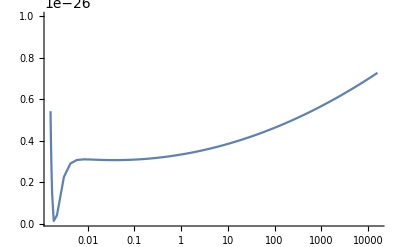

```mathematica
LogLinearPlot[Evaluate[σinelaspp[et]],{et,0.993GeV,10000000GeV},PlotRange->{10^-28,10^-26}]//Print
```

```mathematica
(*270421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLinearPlot[Evaluate[σinelaspp[et]],{et,0.993GeV,10000000GeV},PlotRange->{10^-27,0.8*10^-26},PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"σ_pp^inel[E]"},Above],FrameLabel->{"E(GeV)","σ_pp^inel[E]"},
(*PlotLegends->Placed[{"σ_pp^inel[E]"},Center-Right],*)AxesLabel-> {"E(GeV)","σ_pp^inel[E]"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Frame->True,
FrameTicks->{{{0.0016,1 },(*{0.016,10 },*){0.16, "10^2" },(*{1.6, "10^3" },*){16.0, "10^4"},(*{160.0, "10^5"},*){1600.0, "10^6"},(*{16000.0, "10^7"},*){160000.0, "10^8"}(*{1600000.0, "10^9"},*)},{{2.0*10^-27,"2x10^-27"},{4.0*10^-27,"4x10^-27"},{6.0*10^-27,"6x10^-27"},{8.0*10^-27,"8x10^-27"},{10.0*10^-27,"10^-26"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["σ_pp^inel[E] vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*190621 romr polish fig and frame it ULTRASOS here lies the solution to scinetific notation as well we already did it over here,for sigma inelastic sos,  we just need two arrays,  FrameTicks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-28,"10^-28"},{10^-27,"10^-27"},{10^-26,"10^-26"}}}*)
(*270421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLinearPlot[Evaluate[σinelaspp[et]],{et,0.993GeV,100000000GeV},PlotRange->{10^-28,10^-26},PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"σ_pp^inel[E]"},Above],
(*PlotLegends->Placed[{"σ_pp^inel[E]"},Center-Right],*)AxesLabel-> {"E(GeV)","σ_pp^inel[E]"},FrameLabel-> {"E(GeV)","σ_pp^inel[E]"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Frame->True,
FrameTicks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-28,"10^-28"},{10^-27,"10^-27"},{10^-26,"10^-26"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["σ_pp^inel[E] vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*230419 testing cell *)
(*180720 indeed!*)
(*280720 conditionally do the test plots! SOS need //Print after each plot!*)
If[plottestplots==1.0,



(*220720 x axis log, y axis linear, Kelner et al 2006, pg. 13, Fig. 11, sigmainelastic, in barns! i.e. in 10^(-24)cm^2!
SOS we nearly nailed it, only ours is 10 times moar in value (300 barns twist, rather than 30 in the paper! INVESTIGATE, ALMOST THERE!)*)
LogLinearPlot[Evaluate[σinelaspp[et]],{et,0.993GeV,10000000GeV},PlotRange->{10^-28,10^-26}]//Print]

(*220720B calling sinelasticpp @ 100TeV reproduces correctly Kelner et al06
 fig. 3, pg 5, case (1)2 (QGSJET)SIBYLL*)
ett3=100000GeV;
If[plottestplots==1.0,
LogLogPlot[Evaluate[xxxx*Fπinjt[xxxx,ett1]],{xxxx,0.001,0.99},PlotRange->{0.001,30}]//Print]
(*220720B calling sinelasticpp @ 1TeV reproduces correctly Kelner et al06
 fig. 3, pg 5 case (3)4 (QGSJET)SIBYLL*)
ett2=1000*GeV;
If[plottestplots==1.0,
LogLogPlot[Evaluate[xxxx*Fπinjt[xxxx,ett1]],{xxxx,0.001,0.99},PlotRange->{0.001,30}]//Print]
(*220720B this vs Kelner et al. 2006 fig. 2, pg. 4. 0.1 TeV. Probably at low E,. sinelastic pp does not nned the additional Ethermal term (see Kelner et al. 06 for moar on this)*)
ett1=100*GeV
If[plottestplots==1.0,
LogLogPlot[ParallelEvaluate[xxxx*Fπinjt[xxxx,ett3]],{xxxx,0.0001,0.99},PlotRange->All,PlotPoints->28,MaxRecursion->0]//Print]

(*220720B this non-multiplied by xxxx, is not directly comparable, kept for completeness!*)
ett1=100*GeV
If[plottestplots==1.0,
LogLogPlot[ParallelEvaluate[Fπinjt[xxxx,ett3]],{xxxx,0.001,0.99},PlotRange->All,PlotPoints->8,MaxRecursion->0]//Print]
```

0.160218

0.160218

```mathematica
(*19*)
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
Print[ett1," ",ett2," ",ett3];
If[plottestplots==1.0,Manipulate[LogLogPlot[{Evaluate[xxxx*Fπinjt[xxxx,ett1]],Evaluate[xxxx*Fπinjt[xxxx,ett2]],Evaluate[xxxx*Fπinjt[xxxx,ett3]]},{xxxx,0.001,0.99},PlotRange->{0.001,30},PlotPoints->28,MaxRecursion->0,(*PlotLabels->Placed[{"x*Fπinjt","x*Fπinjt","x*Fπinjt"},Above],*)
PlotLegends->Placed[{"10^2 GeV","10^3 GeV","10^5 GeV"},Center],AxesLabel-> {"x","x*Fπinjt"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{0.0001,0.001,0.01,0.1,1.0},{0.0001,0.001,0.01,1.0,10.0,100.0,1000, 10000.0, 100000.0, 1000000.0, 10000000.0, 100000000.0,1000000000.0, 10000000000.0, 100000000000.0, 1000000000000.0}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["x*Fπinjt vs x" ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

0.160218 1.60218 160.218

```mathematica
(*190621 sos polish fig here*)
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
Print[ett1," ",ett2," ",ett3];
If[plottestplots==1.0,Manipulate[LogLogPlot[{Evaluate[xxxx*Fπinjt[xxxx,ett1]],Evaluate[xxxx*Fπinjt[xxxx,ett2]],Evaluate[xxxx*Fπinjt[xxxx,ett3]]},{xxxx,0.001,0.99},PlotRange->{0.001,30},PlotPoints->28,MaxRecursion->0,(*PlotLabels->Placed[{"x*Fπinjt","x*Fπinjt","x*Fπinjt"},Above],*)
PlotLegends->Placed[{"10^2 GeV","10^3 GeV","10^5 GeV"},Center],AxesLabel-> {"x","x*Fπinjt"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Frame->True,FrameLabel->{"x","x*Fπ"},FrameTicks->{{{0.0001,"10^-4"},{0.001,"10^-3"},{0.01,"10^-2" },{0.1,"10^-1"},{1.0,"1"}},{{0.001,"10^-3"},{0.01,"10^-2" },{0.1,"10^-1"},{1.0,"1"},{10.0,"10^1"},{100.0,"10^2"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["x*Fπinjt vs x" ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

0.160218 1.60218 160.218

```mathematica
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],1./Subscript[t, adb],(1./tppndens[et11,ndens*10000.0]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz]),(1./tppion[et11,ndens,0.999])},{et11,1GeV,100000000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Above],
PlotLegends->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Center-Right],AxesLabel-> {"E(GeV)","t^-1"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{0.0001,0.001,0.01,1.0,10.0,100.0,1000, 10000.0, 100000.0, 1000000.0, 10000000.0, 100000000.0,1000000000.0, 10000000000.0, 100000000000.0, 1000000000000.0}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["t^-1 vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*190621 SOS polished framed figs aka romr comm*)
(*260421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[{1./taccel[et11,etaaccelefficiency1,bxx,byy,bzz,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]],1./Subscript[t, adb],(1./tppndens[et11,ndens*10000.0]),(1./tsyncfvarmagnetic[et11,bxx,70.0*byy,bzz]),(1./tppion[et11,ndens,0.999])},{et11,1GeV,100000000GeV},PlotRange->All,PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Above],
PlotLegends->Placed[{"taccel^-1","t_adb^-1","t_pp^-1","tsynfvarmag^-1","tpipion^-1"},Center-Right],AxesLabel-> {"E(GeV)","t^-1"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{0.0001,0.001,0.01,1.0,10.0,100.0,1000, 10000.0, 100000.0, 1000000.0, 10000000.0, 100000000.0,1000000000.0, 10000000000.0, 100000000000.0, 1000000000000.0}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["t^-1 vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
If[plottestplots==1.0,
LogLogPlot[Evaluate[ndensefastfn[et,2,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,ndens]],{et,100GeV,100000GeV},PlotRange->All]//Print]
```

```mathematica
(*190720 SOS these tests adapted from old code here *)

If[printtestresults==1.0,
Print[Qpppowerlawdependndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] ;
Print[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens];
]
tsa
If[plottestplots==1.0,

LogLogPlot[et*Qpppowerlawdependndens[et,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens] ,{et,1GeV,100000GeV},PlotRange->All]//Print]
```

tsa

```mathematica
(*270421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
If[plottestplots==1.0,Manipulate[LogLogPlot[et*Qpppowerlawdependndens[et,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens] ,{et,1GeV,100000GeV},PlotRange->All(*{10^-28,10^-26}*),PlotPoints->28,MaxRecursion->0,PlotLabels->Placed[{"E*Q_pp[E]"},Above],
PlotLegends->Placed[{"E*Q_pp[E]"},Center-Right],AxesLabel-> {"E(GeV)","E*Q_pp[E] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},{10^-12,"10^-12"},{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{1,"1"}}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["E*Q_pp[E] vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
Qpppowerlawdependndensgammavarpindex[50000000GeV,0.1,0.8,0.1,phi1,phi2,ndens,2.0,bxx,byy,bzz]
```

0.0214571

```mathematica
(*260621 try to reach very high E for plot*)Qpppowerlawdependndensgammavarpindex2=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz},ndensity*c*NIntegrate[ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

(*260621 try to reach very high E for plot*)Qpppowerlawdependndensgammavarpindex3=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz},ndensity*c*NIntegrate[ndensefastfndependndensgammavarpindex[Eπ/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz] 1/xxxi Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi],{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
```

```mathematica
ndensefastfndependndensgammavarpindex2=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]
(*ndensefastfndependndensgammavarpindex=Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1*ndensity*EEEE^-aaa*PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]*)
ndensefastfndependndensgammavarpindex2[100000GeV,2.0,0.8,0.3,0.1,0.5,0.001,ndens,1000,10000,1000]
```

Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1 ndensity EEEE^-aaa PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]

1.84485

```mathematica
Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1 ndensity EEEE^-aaa PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]
```

Function[{EEEE,aaa,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxx,byy,bzz},ct1 ndensity EEEE^-aaa PS2001feppndependgammavarpindex[EEEE,uxx,uyy,uzz,phi1sub,phi2sub,aaa]]

```mathematica
(*260621 works till 353 for E*Qpp SOS pion injection function weighted by E*)(*190621 SOS polish, frame fig aka romr comm*)
(*270421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
(*260621 use Qpppowerlawdependndensgammavarpindex*)
(*Qpppowerlawdependndensgammavarpindex=Function[{Eπ,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,protonindex,bxx,byy,bzz},*)(*tppion=Function[{EEE,ndensity,xxx},3.0/(ndensity*c*σinelaspp[EEE/xxx]) ]*)
If[plottestplots==1.0,Manipulate[LogLogPlot[(*et*)(1/tppion[et,ndens,0.4])*et*Qpppowerlawdependndensgammavarpindex[et,0.1,0.8,0.1,phi1,phi2,ndens,2.0,bxx,byy,bzz] ,{et,1GeV,3530000GeV},PlotRange->Full,PlotPoints->98,MaxRecursion->0,(*PlotLabels->Placed[{"E*Q_pp[E]"},Above],*)
(*PlotLegends->Placed[{"E*Q_pp[E]"},Center-Right],*)(*AxesLabel-> {"E(GeV)","E*Q_pp[E]"},*)
FrameLabel-> {"E(GeV)","E*Q_pp[E]"},
Frame->True, AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},FrameTicks->{{{0.0016,1 },{0.016,"10^1"},{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},(*{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},*){10^-12,"10^-12"},(*{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},*){10^-8,"10^-8"},(*{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"}*),{10^-4,"10^-4"},(*{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},*){1,"1"},(*{10^2,"10^2"},*){10^4,"10^4"},(*{10^6,"10^6"},*){10^8,"10^8"},{10^12,"10^12"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["E*Q_pp[E] vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*180720 add uanalytic pion distro test plot here, preferably conditionally*)
(*190720 comparison to args09 from 10^2 till 10^7 gev, should drop moar than here, 12 OOM, vs just 6-7 here! WTF? check!*)
(*230720 SOS now it works better, after adjusting tloss, tesc SOS!*)
If[plottestplots==1.0,
LogLogPlot[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[et1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens],{et1,100GeV,10000000GeV},PlotRange->Full,PlotPoints->8,MaxRecursion->0]//Print]
```

```mathematica
If[plottestplots==1.0,
LogLogPlot[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[et1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et1,100GeV,1000000000GeV},PlotRange->All,PlotPoints->18,MaxRecursion->0]//Print]
```

```mathematica
Print[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens];
```

-0.3780.5480.1240.3471985.×10^-7100000.1.×10^6100000.2.1×10^11

```mathematica
(*200621 it works!*)Print[Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[500GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1] ]  ];
```

{0.000012,CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[0.801088,-0.378,0.548,0.124,0.347198,5.×10^-7,100000.,1.×10^6,100000.,2.1×10^11,2.]}

```mathematica
Print[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]];
If[plottestplots==1.0,
LogLogPlot[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0]//Print]
```

-0.3780.5480.124

```mathematica
(*210621 sos mixed the names of the plots sos  we did other and called it otherwise sos we plotted q and called it u, etc just a couple got messed do them finally!*)
If[plottestplots==1.0,LogLogPlot[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[et1,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et1,100GeV,1000000000GeV},PlotRange->All,PlotPoints->18,MaxRecursion->0,PlotLegends->Placed[{"U_pion[E]"},Center-Right],AxesLabel-> {"E(GeV)","U_pion[E] (raw)"},
FrameLabel->{"E(GeV)","U_pion[E] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Frame->True,FrameTicks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},{10^-12,"10^-12"},{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{1,"1"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"},{10^9,"10^9"},{10^10,"10^10"}}    } ,ScalingFunctions->{"Log","Log"}]]
```

```mathematica
(*280421 SOS piecemeal*)
(*If[plottestplots==1.0,*)
(*Manipulate[*)If[plottestplots==1.0,LogLogPlot[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"U_pion[E]"},Above],
PlotLegends->Placed[{"U_pion[E]"},Center-Right],AxesLabel-> {"E(GeV)","U_pion[E] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},{10^-12,"10^-12"},{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{1,"1"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"},{10^9,"10^9"},{10^10,"10^10"}}    } ,ScalingFunctions->{"Log","Log"},PlotLabel->Style["U_pion[E] vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]]](*,{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]*)(*//Print]*)

(*
ScalingFunctions->{"Log","Log"},PlotLabel->Style["E*Q_pp[E] vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]
*)
```

```mathematica
(*080122 unpaused that, after trying to conditionalize with plottestplots most plots! Pause[10000];*)
```

```mathematica
(*270421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)
(*Manipulate[*)
If[plottestplots==1.0,LogLogPlot[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et11,100GeV,10000000GeV},PlotRange->All,PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"U_pion[E]"},Above],
PlotLegends->Placed[{"U_pion[E]"},Center-Right],AxesLabel-> {"E(GeV)","U_pion[E] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},{10^-12,"10^-12"},{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{1,"1"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"},{10^9,"10^9"},{10^10,"10^10"}}    } ScalingFunctions->{"Log","Log"}]](*,PlotLabel->Style["U_pion[E] vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]]*)(*,{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]  *)
```

```mathematica
(*280421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)


If[plottestplots==1.0,Manipulate[LogLogPlot[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et11,100GeV,10000000GeV},PlotRange->All(*{10^-28,10^-26}*),PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"E*Q_pp[E]"},Above],
PlotLegends->Placed[{"E*Q_pp[E]"},Center-Right],AxesLabel-> {"E(GeV)","E*Q_pp[E] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},Ticks->{{{0.0016,1 },{0.016,10 },{0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},{10^-15,"10^-15"},{10^-14,"10^-14"},{10^-13,"10^-13"},{10^-12,"10^-12"},{10^-11,"10^-11"},{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{1,"1"}}},ScalingFunctions->{"Log","Log"},PlotLabel->Style["E*Q_pp[E] vs E[GeV] " ,Medium],LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
(*200621 SOS it works but takes a while. also, careful to prepare all previous things before running this*)
(*280421 works SOS*)
(*220720B NXT, we do it for many gammas, theta=20 degrees, or rads:0.349, gamma=5,10,30 (u=0.9798,0.995,0.999446) bottom fig. 2 of TR13.*)
(*220720B A match as well! vs fig. 2 of TR13!*)


If[plottestplots==1.0,Manipulate[LogLogPlot[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[et11,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1],{et11,100GeV,10000000GeV},Frame->True,PlotRange->All(*{10^-28,10^-26}*),PlotPoints->8,MaxRecursion->0,PlotLabels->Placed[{"Qn"},Above],
(*PlotLegends->Placed[{"Qn"},Center-Right],*)FrameLabel->{"E(GeV)","Qn (raw)"},AxesLabel-> {"E(GeV)","Qn] (raw)"},AspectRatio->1/1.0,
TargetUnits-> {"GeVplot",""},FrameTicks->{{(*{0.0016,1 },{0.016,10 },*){0.16, "10^2" },{1.6, "10^3" },{16.0, "10^4"},{160.0, "10^5"},{1600.0, "10^6"},{16000.0, "10^7"},{160000.0, "10^8"},{1600000.0, "10^9"}},{{10^-16,"10^-16"},(*{10^-15,"10^-15"},*){10^-14,"10^-14"},(*{10^-13,"10^-13"},*){10^-12,"10^-12"},(*{10^-11,"10^-11"},*){10^-10,"10^-10"},(*{10^-9,"10^-9"},*){10^-8,"10^-8"},(*{10^-7,"10^-7"},*){10^-6,"10^-6"},(*{10^-5,"10^-5"},*){10^-4,"10^-4"},(*{10^-3,"10^-3"},*){10^-2,"10^-2"},(*{10^-1,"10^-1"},*){1,"1"},{10^2,"10^2"},{10^4,"10^4"},{10^6,"10^6"},{10^8,"10^8"}}},ScalingFunctions->{"Log","Log"},(*PlotLabel->Style["E*Q_pp[E] vs E[GeV] " ,Medium],*)LabelStyle->Directive[c,s]],{{c,Black,"color"},Black},{{s,Plain,"style"},{Plain,Italic,Bold}}]]
```

```mathematica
Print[Dimensions[phi1],Dimensions[tanphi1]]
```

{}{}

```mathematica
(*071019 VERIFIED functionalization of uanal here!*)


(*091019 VERIFIED var magnetic version of it!*)
If[printtestresults==1.0,
Print[uanalpowerlawpiece[800GeV],"tseis" ];
Print[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens];
Print[uanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];Print[Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,uanal[1000GeV]," bippy ",uanalpowerlawpiece[1000GeV],"ggg",uanalpowerlaw[1000GeV], uanalpowerlawdepend[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2],"   ",uanalpowerlawdependvarmagnetic[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz],"hhgg",uanalpowerlawdependvarmagneticold[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz],"  hgfdg ", uanalpowerlawdependtroisvarmagneticndens[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]," dfbgdfb  ", uanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]  ,"    ",Timing[cfiuanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens] ],Timing[CFuanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] ,"  dsg ",Timing[CFuanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] ,Timing[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]],"   ",Timing[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]]
];
(**071019 OS EDO TYPED 071019 SOS*)
```

```mathematica
Print[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma[300GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]];
```

CompiledFunction::cfsa: Argument EEEdash1 at position 1 should be a machine-size real number.

NIntegrate::nlim: xxxi = 0.000183574 EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

CompiledFunction::cfsa: Argument EEEdash1 at position 2 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::inumr: The integrand 6.3×10^21 ⅇ^(«1») NIntegrate[(«1»[EEEdash1/0.9,2,-0.378,0.548,0.124,0.347198,5.×10^-7,2.1×10^11] «1» Function[«1»][«1»])/0.9,{0.9,EEEdash1/5447.4,1},«12»→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.480653,4902.66}}.

NIntegrate::inumr: The integrand 6.3×10^21 «1» NIntegrate[(«1»[EEEdash1/0.9,2,-0.378,0.548,0.124,0.347198,5.×10^-7,2.1×10^11] «1» Function[«1»][«1»])/0.9,{0.9,EEEdash1/5447.4,1},«12»→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.480653,4902.66}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

12.9976 NIntegrate[CFQpppowerlawdependndensgamma[EEEdash1,-0.378,0.548,0.124,0.347198,5.×10^-7,2.1×10^11]/ⅇ^CFtdepthpptroisvarmagneticndenstpionfn[0.480653,EEEdash1,100000.,1.×10^6,100000.,2.1×10^11],{EEEdash1,0.480653,0.9 Epmax},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]

```mathematica
If[printtestresults==1.0,
Timing[CFuanalpowerlawdependtroisvarmagneticndenstpionfn[3000000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] 

Timing[CFuanalpowerlawdependtroisvarmagneticndenstpionfngamma[3000000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] 

Timing[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[300GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
];
```

```mathematica
Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[300GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

CompiledFunction::cfsa: Argument EEEdash1 at position 2 should be a machine-size real number.

CompiledFunction::cfsa: Argument EEEdash2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.61461,2.51896×10^9}

```mathematica
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[1300GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
```

{0.000012,CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[2.08283,-0.378,0.548,0.124,0.347198,5.×10^-7,100000.,1.×10^6,100000.,2.1×10^11,2.]}

```mathematica
Subscript[u, xx],Subscript[u, yy],Subscript[u, zz]
```

```mathematica
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[1300GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
```

{0.000011,CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[2.08283,-0.378,0.548,0.124,0.347198,5.×10^-7,100000.,1.×10^6,100000.,2.1×10^11,2.]}

```mathematica
uanaltest=Function[{EEE},NIntegrate[Exp[-tdepthpp[EEE,EEEdash1]],{EEEdash1,EEE,0.9*Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
```

```mathematica
Function[{EEE},NIntegrate[Exp[-tdepthpp[EEE,EEEdash1]],{EEEdash1,EEE,0.9 Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]
```

Function[{EEE},NIntegrate[Exp[-tdepthpp[EEE,EEEdash1]],{EEEdash1,EEE,0.9 Epmax},MaxRecursion→5,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]]

```mathematica
qneutrinofastertestDIDITpowerlawpiece=Function[{Eneutrino},NIntegrate[(*UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))  *(tpion[Epion]^-1)* *) uanalpowerlaw[Epion] ,{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
```

```mathematica
qneutrinofastertestDIDITpowerlaw=Function[{Eneutrino},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlaw[Epion],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
qneutrinofastertestDIDITpowerlawdepend=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlawdepend[Epion,uxx,uyy,uzz,phi1sub,phi2sub],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

qneutrinofastertestDIDITpowerlawdependvarmagnetic=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlawdependvarmagnetic[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


qneutrinofastertestDIDITpowerlawdependvarmagneticold=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlawdependvarmagneticold[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlawdependtroisvarmagneticndenstpionfn[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added to this varpindex proton plaw variable index*)
qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnvarpindex=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*uanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];

cfiqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFuanalpowerlawdependtroisvarmagneticndenstpionfn[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added varpindex proton index variable*)
cfiqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnvarpindex=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFuanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];



cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added varpindex*)
cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnvarpindex=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfnvarpindex[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added varpindex*)
cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],{Epion,Eneutrino,Epmax},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];


(*270520 SOS this one and its son! Also added some exclusions! make it faster! SOS we did add Epion to the qneutrino total integral!as a COMMON VARIABLE throughout the 3 integrations! SOS needed the whole triple integral after all !SOS!*)
mesulino
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*(1/CFbbπtroisndensvarmagnetic[Eneutrino,bxxvar,byyvar,bzzvar,ndensity])*ndensity*c*((ndensefastfndependndensgamma[Epion/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Epion/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[Eneutrino,EEEdash1,bxxvar,byyvar,bzzvar,ndensity]),{Epion,Eneutrino,Epmax},{EEEdash1,Eneutrino,0.9 Epmax},{xxxi,Eπ/Epmax,1},Exclusions->ⅇ^tdepthpptroisvarmagneticndenstpionfn[Eneutrino,EEEdash1,bxxvar,byyvar,bzzvar,ndensity]==0,Exclusions-> Epion == 4.2611,Exclusions->Epion==0,Exclusions->CFbbπtroisndensvarmagnetic[Eneutrino,bxxvar,byyvar,bzzvar,ndensity]==0,Exclusions->xxxi==0, MaxRecursion->5,AccuracyGoal->3,WorkingPrecision->174,Method->{Automatic,"SymbolicProcessing"->0}]];
(*200720 added varpidex here as well! Note direct put of var p protonindex into ndensefastfndependndensgamma's existing relevant facility!*)
(*210720 replaced ndensgamma with the varpindex variant of it. The latter merely calls ps01varpindex now!*)
(*100820 SOS added bfields depend. to ndense, cause of ecutoff of fast rpotons! (conditional form of ndens!)*)
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},NIntegrate[UnitStep[1-Subscript[r, π]-(Eneutrino/Epion)]/(Epion(1-Subscript[r, π]))*(tpion[Epion]^-1)*(1/CFbbπtroisndensvarmagnetic[Eneutrino,bxxvar,byyvar,bzzvar,ndensity])*ndensity*c*((ndensefastfndependndensgammavarpindex[Epion/xxxi,protonindex,uxx,uyy,uzz,phi1sub,phi2sub,ndensity,bxxvar,byyvar,bzzvar]*1/xxxi*Fπinjt[xxxi,Epion/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[Eneutrino,EEEdash1,bxxvar,byyvar,bzzvar,ndensity]),{Epion,Eneutrino,Epmax},{EEEdash1,Eneutrino,0.9 Epmax},{xxxi,Eπ/Epmax,1},Exclusions->ⅇ^tdepthpptroisvarmagneticndenstpionfn[Eneutrino,EEEdash1,bxxvar,byyvar,bzzvar,ndensity]==0,Exclusions-> Epion == 4.2611,Exclusions->Epion==0,Exclusions->CFbbπtroisndensvarmagnetic[Eneutrino,bxxvar,byyvar,bzzvar,ndensity]==0,Exclusions->xxxi==0, MaxRecursion->5,AccuracyGoal->3,WorkingPrecision->174,Method->{Automatic,"SymbolicProcessing"->0}]];

TEMPYcficorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma=Function[{EEE,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},1/CFbbπtroisndensvarmagnetic[EEE,bxxvar,byyvar,bzzvar,ndensity]NIntegrate[ndensity*c*(ndensefastfndependndensgamma[Eπ/xxxi,2,uxx,uyy,uzz,phi1sub,phi2sub,ndensity]*1/xxxi*Fπinjt[xxxi,Eπ/xxxi]*σinelaspp[Eπ/xxxi])/ⅇ^tdepthpptroisvarmagneticndenstpionfn[EEE,EEEdash1,bxxvar,byyvar,bzzvar,ndensity],{EEEdash1,EEE,0.9 Epmax},{xxxi,Eπ/Epmax,1},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];



CFqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cfiqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],"RuntimeOptions"->{"EvaluateSymbolically"->False}];



(*141019 here we use the corrected cfuanal, where bbpi is the new one. we had the olp bbpi here!*)
CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];
(*200720 added varpindex*)
CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True];

(*270520 this one*)

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];


(*200720 added varpindex here*)
CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True];

(*200720 B version just includes direct C compilation, only works at computer with C compiler available though! Else, omit the B SOS!*)
(*180720 this seems to do the trick!*)

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];
(*200720 added here varpindex*)
CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];



(*300520 try outputting this to C! SOS NO WORK!*)
(* 180720 these commented out, as they do not seem to serve the purpose for now!

targerDir=CreateDirectory[];
fnSource=FileNameJoin[{targerDir,"CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma.c"}];
Export[fnSource,CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma];


CFcorrectedfasterwholethingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},cficorrectedwholethingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];


qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnpiece=Function[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},NIntegrate[uanalpowerlawdependtroisvarmagneticndenstpionfn[Epion,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],{Epion,Eneutrino,Epmax/100.0},MaxRecursion->5,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]];*)
```

mesulino

Get::path: ToFileName[{pathlocationstring}] in $Path is not a string.

Get::path: ToFileName[{Global`pathlocationstring}] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

```mathematica
mesulino
```

mesulino

```mathematica
(*260720 here we set the bfactorcompilec selection: if set to on, the activate C compilation. If OFF, then general compilation only!*)
(*260720 we get to keep C-calls ONLY! WE conditionally assign to it either  B, or non-B!*)
(*260720 WE also get to keep all old defs! We merely add a new def, the C-one, AND ALTER CALLS IN THE ACTION LATER ON, to be only C-calls! So we only call the conditionally-defined C-ones! varpindex-ed, or non-varpindexed! THIS ONLY GOES FOR THE LATEST VERSES, not the simpler ones!*)
If[bfactorcompilec == 1.0,

(*260720 if bfactorcompilec eq 1.0, then employ C-compiler. Else, proceed with general, non-specific compilation, after the separating comma!*)

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaC=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];
(*200720 added here varpindex*)
CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];

(*260720 separating comma of the current if statement!*)
,

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaC=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity],RuntimeAttributes->{Listable},Parallelization->True];

CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC=Compile[{Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex},
cficorrectedwholeLOTthingyqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindex[Eneutrino,uxx,uyy,uzz,phi1sub,phi2sub,bxxvar,byyvar,bzzvar,ndensity,protonindex],RuntimeAttributes->{Listable},Parallelization->True];

]
```

```mathematica
(*310520 try to use specific C compiler*)
Needs["CCompilerDriver`"]
CCompilers[]
tsi
CCompilers[Full]
tsa
DefaultCCompiler[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic},{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/bin,CompilerName→Automatic}}

tsi

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic},{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/bin,CompilerName→Automatic},{Name→Intel Compiler,Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→None,CompilerName→Automatic},{Name→Generic C Compiler,Compiler→CCompilerDriver`GenericCCompiler`GenericCCompiler,CompilerInstallation→None,CompilerName→Automatic}}

tsa

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
DefaultCCompiler[]
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
`Compile[x,x,CompilationTarget-> "C"]
```

Global`Compile::shdw: Symbol Compile appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
Global`Compile[x,x,CompilationTarget->"C"]
```

{{“Name”→”Intel Compiler”,”Compiler”→CCompilerDriver`IntelCompiler`IntelCompiler,”CompilerInstallation”→None,”CompilerName”→Automatic},{“Name”→”Generic C Compiler”,”Compiler”→CCompilerDriver`GenericCCompiler`GenericCCompiler,”CompilerInstallation”→None,”CompilerName”→Automatic}}
CCompiler={“Compiler”→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,”CompilerInstallation”→”P:\\ProgramData\\Microsoft\\VisualStudio\\Packages”}

{{Name→Intel Compiler,Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→None,CompilerName→Automatic},{Name→Generic C Compiler,Compiler→CCompilerDriver`GenericCCompiler`GenericCCompiler,CompilerInstallation→None,CompilerName→Automatic}}

{Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→E:\IntelCompiler}

```mathematica
%1447
```

%1447

```mathematica
%1432
```

%1432

ndens=3*10^7
ndensefast=ndens/1000000
BB=10^7
BBB=BB
fff=ndens
fffbscalar=BBB
fffvscalar=0.26
indexxx=0.7;

pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[Qpp[GeV(10)^(i^(indexxx))]],mpat,Timing[uanal[GeV(10)^(i^(indexxx))]],dip,Timing[qneutrinofastertestDIDIT[GeV(10)^(i^(indexxx))]]},{i,0.01,15,1}]

```mathematica
(*200720 temp alter proton index*)
If[printtestresults==1.0,
protonindex1=2.3;
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
(*200720 a higher proton index tend to decrease value and increase time to calc. And vice versa!*)
(*200720 restore it to param value!*)
protonindex1=α;
];
```

```mathematica
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
```

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((342950. ⅇ^(-NIntegrate[1/(«1» «1»),«3»,Method→{«1»}]) (1-«1»)^0.5 xxxi^(«1») («1»)^2 (1-xxxi^(«1»))^4 «8»)/((30.+0.000121382 Epion) Epion «1» (Epion/xxxi)^4.)) is less than WorkingPrecision (174.).

NIntegrate::inumr: The integrand (342949.8112481943680904805660247802734375 («180»)^(-NIntegrate[1/(«1»),«4»]) («1»)^(«8») («4»)^(«1») («1»)^2 (1-«1»)^4 «8»)/((30.+0.000121381886087768462128937130284356271658907644450664520263671875 Epion) Epion«1»«1» («1»)^(«7»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.60217645999999991346385286306031048297882080078125,5447.39996400000018184073269367218017578125},{«57»,«48»},{0.000105882352941176474865093981581054549678810872137546539306640625,1}}.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((594590. 2.71828^(-NIntegrate[1/(«1» «1»),«3»,Method→{«1»}]) («1»)^0.5 «1» («1»)^2 (1-«1»)^4 «7»)/((30.+0.000121382 Epion) √(0.968365+«19» «1») («1»)^(«3») (1-0.16898 √(«1»))^3.)) is less than WorkingPrecision (174.).

NIntegrate::inumr: The integrand (594590.164293337496928870677947998046875 («58»)^(-NIntegrate[1/(«1»),«3»,«1»]) («1»)^(«8») «1» («1»)^2 (1-«1»)^4 «7»)/((30.+0.000121381886087768462128937130284356271658907644450664520263671875 Epion) √(«1») «1» («1»)^(«7»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.60217645999999991346385286306031048297882080078125,5447.39996400000018184073269367218017578125},{«57»,«48»},{0.000105882352941176474865093981581054549678810872137546539306640625,1.}}.

CompiledFunction::cfse: Compiled expression NIntegrate[(UnitStep[1-r_π-1.60218 Power[«2»]] 2.1×10^11 c («1»))/((Epion (1-Subscript[«2»])) tpion[Epion] CFbbπtroisndensvarmagnetic[«11»,«3»,«8»] (xxxi ⅇ^(«36»[«1»]))),{Epion,1.60218,Epmax},«7»,MaxRecursion→5,«3»] should be a machine-size real number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

NIntegrate::precw: The precision of the argument function ((342950. ⅇ^(-NIntegrate[1/(«1» «1»),«3»,Method→{«1»}]) (1-«1»)^0.5 xxxi^(«1») («1»)^2 (1-xxxi^(«1»))^4 «8»)/((30.+0.000121382 Epion) Epion «1» (Epion/xxxi)^4.)) is less than WorkingPrecision (174.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::inumr: The integrand (342949.8112481943680904805660247802734375 («180»)^(-NIntegrate[1/(«1»),«4»]) («1»)^(«8») («4»)^(«1») («1»)^2 (1-«1»)^4 «8»)/((30.+0.000121381886087768462128937130284356271658907644450664520263671875 Epion) Epion«1»«1» («1»)^(«7»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.60217645999999991346385286306031048297882080078125,5447.39996400000018184073269367218017578125},{«57»,«48»},{0.000105882352941176474865093981581054549678810872137546539306640625,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.02546,NIntegrate[(UnitStep[1-r_π-1.60218/Epion] 2.1×10^11 c (ndensefastfndependndensgammavarpindex[Epion/xxxi,2.,-0.378,0.548,0.124,0.347198,5.×10^-7,2.1×10^11,100000.,1.×10^6,100000.] Fπinjt[xxxi,Epion/xxxi] σinelaspp[Eπ/xxxi]))/((Epion (1-r_π)) tpion[Epion] CFbbπtroisndensvarmagnetic[1.60218,100000.,1.×10^6,100000.,2.1×10^11] (xxxi ⅇ^tdepthpptroisvarmagneticndenstpionfn[1.60218,EEEdash1,100000.,1.×10^6,100000.,2.1×10^11])),{Epion,1.60218,Epmax},{EEEdash1,1.60218,0.9 Epmax},{xxxi,Eπ/Epmax,1},Exclusions→ⅇ^tdepthpptroisvarmagneticndenstpionfn[1.60218,EEEdash1,100000.,1.×10^6,100000.,2.1×10^11]==0,Exclusions→Epion==4.2611,Exclusions→Epion==0,Exclusions→CFbbπtroisndensvarmagnetic[1.60218,100000.,1.×10^6,100000.,2.1×10^11]==0,Exclusions→xxxi==0,MaxRecursion→5,AccuracyGoal→3,WorkingPrecision→174,Method→{Automatic,SymbolicProcessing→0}]}

```mathematica
(*260720 here call the conditionally-defined function, to be employed later on in calc loops!*)
If[printtestresults==1.0,protonindex1=2.3;
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
(*200720 a higher proton index tend to decrease value and increase time to calc. And vice versa!*)
(*200720 restore it to param value!*)
protonindex1=α;
];
```

```mathematica
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndens tpionfngammaB[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

{0.000015,CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndens tpionfngammaB[1.60218,-0.378,0.548,0.124,0.347198,5.×10^-7,100000.,1.×10^6,100000.,2.1×10^11]}

```mathematica
(*280720 leave this as is!*)
indexxx=indexxx1;
```

```mathematica
If[printloopcalcs==1.0,
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/GeV,tsa  ,mpit},{i,0.01,15,1}]
];
```

```mathematica
If[printloopcalcs==1.0,
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/.GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]},{i,0.01,15.01,1}]
];
```

```mathematica
If[printloopcalcs==1.0,
protonindex1
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/.GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngammavarpindex[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]},{i,0.01,15.01,1}]
];
```

```mathematica
If[printloopcalcs==1.0,
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/.GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]},{i,0.01,15.01,1}]
];
```

```mathematica
If[printloopcalcs==1.0,
protonindex1
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/.GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]},{i,0.01,15.01,1}]
];
```

```mathematica
(*260720 Here call conditionally-defined C-function!*)
If[printloopcalcs==1.0,
protonindex1
indexxx=indexxx1;
pap=Table[{(10GeV),di,(i^(indexxx)),tsi,(GeV(10)^(i^(indexxx)))/.GeV,tsa  ,Timing[tsyncf[GeV(10)^(i^(indexxx))]],mpit, Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]},{i,0.01,15.01,1}]
];
```

```mathematica
(*SOS CRAZY STUFF GOING ON! 010620 When we calc using indexxx+0.01, it runs nearly 10 times as fast , compared to exact integer indexxx values! What is moar, the whole loop over the spectrum, see right above, goes very fast, perhaps bcause it is calcing NOT at exact indexxx values! SOS! we can do the plots very fast like that! each point, WHOLE PLOT, at around 20-30secs! BUT MUST MODIFY loop and BIG array, to include the whole plot!Maybe do an array the same size as the rho4D for e.g., but with a small array as each element! ADD this array and assign there the results for each point calced! 010620 
Also when calving in the above table kinda loop, it goes much faster than alone! ESPECIALLY at high energies! alone it takes in excess of 400 secs, in the loop 0.02 secs at ABOUT 10000GeV! SOS exploit this thing and we are set! DO THE BIG ARRAY! Alternatively, make it a SPARSE ARRAY, only filling the few filtered points, yet mainaining original huge 4D array's coordinates!*)
(*280720 leave those two calcs anyway, conditionalize the rest!*)
i=9.01
Print[(GeV(10)^(i^(indexxx))),"   ",(GeV(10)^(i^(indexxx)))/GeV,"   ",1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens];
```

9.01

73.0916   45620.2   1.60218-0.3780.5480.1240.3471985.×10^-7100000.1.×10^6100000.2.1×10^11

```mathematica
i=1.01
GeV(10)^(i^(indexxx))
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]
```

1.01

0.0162817

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((2.10919×10^8 ⅇ^(-NIntegrate[1/(«1» «1»),«3»,Method→«1»]) (1-«1»)^0.5 («4»)^(«1») («1»)^2 (1-xxxi^(«1»))^4 «7»)/((30.+0.000121382 Epion) Epion «1» (Epion/xxxi)^4.)) is less than WorkingPrecision (174.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in Epion near {Epion,EEEdash1,xxxi} = {«232»,«230»,«231»}. NIntegrate obtained «234» and «234» for the integral and error estimates.

{2.7481,2.50279×10^13}

```mathematica
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[8099.0199683623205GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((261635. ⅇ^(-NIntegrate[1/(«1» «1»),«3»,Method→{«1»}]) (1-«1»)^0.5 xxxi^(2«1»«1») («1»)^2 (1-xxxi^(«1»))^4 «6»)/((30.+0.000121382 Epion) Epion^5 √(0.968365+«1») (1-0.16898 √(«1»))^3)) is less than WorkingPrecision (174.).

{0.067932,0.00937276}

```mathematica
Subscript[u, xx]
```

-0.378

```mathematica
If[printtestresults==1.0,
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[100GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
];
```

```mathematica
If[printtestresults==1.0,
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
];Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaB[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

NIntegrate::nlim: EEEdash2 = EEEdash1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((2.14039×10^6 ⅇ^(-NIntegrate[1/(«1» «1»),«3»,Method→«1»]) (1-«1»)^0.5 xxxi^(2«1»«1») («1»)^2 (1-xxxi^(«1»))^4 «6»)/((30.+0.000121382 Epion) Epion^5 √(0.968365+«1») (1-0.16898 √(«1»))^3)) is less than WorkingPrecision (174.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 16 recursive bisections in Epion near {Epion,EEEdash1,xxxi} = {«230»,«230»,«231»}. NIntegrate obtained «230» and «230» for the integral and error estimates.

{3.18761,7053.14}

```mathematica
(* 
151019 SOS AT about 200000 GeV it is much faster to calc! We commented out all those qneutrino stuff,  to be used at will by uncommenting.Reason is to be able to run all code from start at first.
Timing[CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[100000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]*)
```

```mathematica
(*Timing[CFfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[100000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]*)
```

```mathematica
$ProcessorCount
```

10

```mathematica
(*Timing[qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnpiece[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]*)
```

```mathematica
(*Timing[qneutrinofastertestDIDITpowerlawpiece[1000GeV]]*)
```

```mathematica
(*Timing[qneutrinofastertestDIDITpowerlaw[1000GeV]]*)
```

```mathematica
(*Timing[qneutrinofastertestDIDITpowerlawdependvarmagneticold[1000GeV]*)
```

```mathematica
(*Timing[qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[100GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]] *)
```

```mathematica
(* 240419 these two lines may show how to affect things. For e.g., try Subscript[β, b]=0.99999999999999999999 and  coslosu=0.999999999999999999999*)
(*Subscript[β, b]=0.99999999999999999999
coslosu=0.999999999999999999999*)
(*

PS2001feppn[1000GeV]
Timing[Qpp[1000GeV]]
Timing[Qpppowerlaw[1000GeV]]
Timing[uanaltest1bingo[1000GeV]]
Timing[uanal[1000GeV]]

Timing[qneutrinofastertestDIDITpowerlaw[1000GeV]]
Timing[qneutrinofaster[1000GeV]]

*)


(*Timing[qneutrino[1000GeV]]*)
```

```mathematica
(*081019 it works! we now got everything apart from the slow proton density included. Rest are treated as constants, many are read from the expernal param file!*)

(*Print[Timing[qneutrinofastertestDIDITpowerlaw[2000GeV]],Timing[qneutrinofastertestDIDITpowerlawdepend[2000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2]],"    "]*)
```

```mathematica
(*Print[Timing[qneutrinofastertestDIDITpowerlawdependvarmagneticold[2000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz]]]*)
```

```mathematica
(*Print[Timing[qneutrinofastertestDIDITpowerlawdependvarmagnetic[2000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz]]]*)
```

```mathematica
V
ndensoldy

(*051019 here erased Subscript[u, xx] assignement at a crazy value near unity that lead to utotal greatger than one!*)
```

2.03152×10^10

ndensoldy

END OF NEMISS CODE. NOW THE PLOAD4D CODE!

## pload4d part of nemiss

Read and manipulate 4D (spatio-temporal) hydro data. Based on Mignione’s pload (which was originally 2D) and on our own 3D expansion of pload, pload3D.

```mathematica
Pause[8]
```

Intro text stuff for reference and in-code links to ongoing work

200919 Also do an external param file for the emission code, avoid hard-wired values for vars! And remeber to convert read vars from 1-element arrays to scalars! Perhaps device a way to do that automatically!

200919 filter criterion for stray detection: size of v component along los: v*l*coslosu. Both l and v are between 0 and 1. L is unitary vector and v is v/c. So their dor product should be something above the filter threshold (iser-defined, something for e.g. like 0.5, 0.7 etc) for the emission calc to take place. This, because emission calc is expensive. If below threshold, then no calc and move to next loop index value, re-examine vlos vs threshold, and so on! Also, fo rPLUTO check bent jet stuff, etc!

190919 (* 190919 tmin tmax are read from the external rlos param file as 1D arrays. WE thedn assign on themselves the first -and only- element of that array ELSE NO LOOP!
*)
minim=140
maxim=143
minimread=ToExpression/@pinakaki[[18]]/1
maximread=ToExpression/@pinakaki[[20]]/1
minim=minimread[[1]]
maxim=maximread[[1]]

We also verified coslosu calc for a point from old mathematica code tests! IT works, now we must do it for array, a slice of databig! Do it!


180919 Add coslosu calc for RADIOGRAPH first! Then do it all over grid. THEN add it for camera obscura. ALSO: Explore effect of MAGnification on camera obscura focal point location! Do we need to incorporate FPoint outside ze grid after all, in order to use it for paper? Perhaps not for neutrinos, but yes for radio, etc! See to it though! Maybe neutrinos as well! SL motion! etc!

170919 Run a filter where only the stray particles’s emission coefficient is calculated. Not all! kind of if coslosu gt 0.3 AND velocity value .gt. 0.3c then calc emission. This way, we offload the bulk of the calc and make it 3-4 OOM faster! So no need for DACE, etc, as long as main jet is off-los. If it is nearly head-on, then perhaps a back-of-the evelope calc will suffice anyway!

170919 Also, investigate a bent jet, perhaps this produces moar lateral action after all!

170919 Attempt to add reading param file here and also radiograph coslosu. 

160919  We read from data files and put that into databig. We ther print some random elements, pref. from dummy files,  to see their value. Then, we do joker calc and write to dummy files the joker result! Then we re-read databig from scratch, and see if dummy files are read properly and also if they have been updated! PLS do some more testing with this data I/O, then automate it and prepare the real calcs! Keep them as simple as possible, put rest in rlos! Here only the coeff/s.!

150919 We now got the reading part in 4d, using fixed dim data reading (except influence from readfloatmatrix!) and from an arbitrary timespan (tmin, tmax). Remains to do that above setup for writing as well, with care not to corrupt the data (initial datafiles are corrupted in their dummy part).Also, do an intermediate calc cell, where we do the calcs afterr the reading and vefore the writing, all inside the databig slices!

(*140919 IT WORKS! READING, with CONTROLLED DIMENSIONS, DEFINED FROM  readFloatMatrix THOUGH, NOT FROM data’s initialization...*)
(*So we now got the big databig array, with all 4D data in it. Remains to do the writing of joker calc, alongsame manner! Merge existing, working writing routine with spanim etc arbitrary timespan system from this reading one. Then perhaps do a third, IN THE MIDDLE of reading one and writing one, that will do the calcs!  coslosu for cam obscura and then the real thing!!*)




120919 we now do the reading part, where it reads the data into one big array, whose time dimension is set as tspan, where tspan is now by hand but later shall be calced from tmin, tmax tspan=tmax-tmin, tmax,min, are read from the param file!

110919 We hereby decided to break this whole calc in two!! One for reading the data into databig. And another such loop, for calcing (real or joker calc) and then writing that to data files!!! READING CELL: n index goes from 1 to 13, covering ALL variables. WRITING CELL: n goes from 10 upwards, covering ONLY the dummy variables, hereby virtz and dummy1, dummy2.


(*110919 This one is almost ready to become the writing part. Only leave out defining databig, in order to AVOID OVERWRITING DATABIG!*)


(*110919 (Referring to the big cell doing the joker-type calcs and also the binary data I/O). We shall probably need two separate cells like this one! One to merely read all the data into the databig array, and another one where the calculations shall take place!!! SO DO TWO SEPARATE COPIES OF IT AND PROCEED ACCORDINGLY!!! *)


(*SOS 110919 ULTRA CAREFUL HERE! The hereafter selected range n determines which data files shall be OVERWRITTEN! if n LE 9 then WE OVERWRITE (LOSE) FRIGGING DATA FILES!!! N MUST BE AT LEAST TEN 10 AT ALL TIMES! DO NOT F>>K UP HERE!!! NO ROOM FOR ERROR!!!*)


100919 It works! databig was defined as integer so terkenlis was not converting to real32. Now we define that as real(constant is 1.12345 instead of 1) and terkenlis is also real. So it works! Remains to make it specific for variables!
100919 We now have to do the actual databig array and then do calcs from that and output results to dummy files. SOS

090919 we put semicolons everywhere after loop’s agyles and also after all statements. That eliminated tag times protected errors. Remains to write the files, trkenlis etc seem to be created just fine now! Remains to write!

080919 DID DUMMY LOOP, work OK for printing filenames and opening them, also performs internally the joker calc OK. BUT, it wont BinaryWrite the joker calc terkenlis result to the corresponding files! That’s what’s left to do! Check when writes where succesful, on an indvidual basis, last thing from June! Replicate that here!


080919 Do a dummy loop where assignement of an expression related to the lopping index is performed. This is blocking us currently!

(*080919 Just did exper. loop! IT WORKS (see below, right before the actual loop)! Now transfer that to the actual working loop, BIT BY BIT!!! RE_CONSTRUCT THE LOOP BUDDY!
TRACK THE ERROR THERE!*)

060919 We now have the global databig array loaded with the time-series of data. All of them! Remaining steps:


070919 we now try the first step, towards the end, do the joker calc using databig instead of just data!
.Do the ‘joker’ calc (a simple thing, such as divide density by 1000 and write that to one of the dummy components of data/databig!) and check it works within databig.


070919 We now try this second step. We did write a single file. Now do that over all the loaded files! Loop over the n!
.Write the result to the output data file on disk (already have written specific files ACCORDING TO THEIR NAME SYSTEM, now do that over the time-series, in an organized fashion) IN THE LOOP WONT WORK, proc 5c. OUTSIde LOoP, works oK SEE To it!

. Calc the coslosu stuff, etc angle sins etc and store that to dummy files, according to the above process.
.Do the big emission calc and store that to the relevant dummy file.

010919 We now have it here! It first reads all the data from a certain snapshot, into a big ‘data’ array, which has size nx*ny*nz*13 (13 is the number of variables, including a couple of dummy ones). In order to do business, we aim to load a 5d data array, whose size shall be (number of time snapshots loaded)*nx*ny*nz*13. With that, we shall be able to do ze calcs of coslosu etc and then output the result for loading back into rlos for further processing. Then, we shall replace the simple ‘joker’ dummy calc with the real calc of the emission coefficint (neutr. or g-rays).

## pload4D

```mathematica
(*110619 ROUTINE NO 1*)
AppendTo[$Path, ToFileName[{pathlocationstring}]]
SetDirectory[pathlocationstring]
```

{/home/teo/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/13.2/SystemFiles/Links,/home/teo/.Mathematica/Kernel,/home/teo/.Mathematica/Autoload,/home/teo/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/teo,/usr/local/Wolfram/Mathematica/13.2/AddOns/Packages,/usr/local/Wolfram/Mathematica/13.2/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/13.2/AddOns/Autoload,/usr/local/Wolfram/Mathematica/13.2/AddOns/Applications,/usr/local/Wolfram/Mathematica/13.2/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/13.2/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/13.2/Documentation/English/System,/usr/local/Wolfram/Mathematica/13.2/SystemFiles/Data/ICC,/usr/local/Wolfram/Mathematica/13.2/Documentation/ChineseSimplified/System/,/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/,/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/,/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies/}

/home/teo/files_paper23good_151023/paper9_10/scrange/neutrino_scale_processed_overwritten_1_to_45_on_50_to_94_240223/neutrino_scale/torblob18dummies

```mathematica
{"C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\SystemFiles\\Links","C:\\Users\\Netuser\\AppData\\Roaming\\Mathematica\\Kernel","C:\\Users\\Netuser\\AppData\\Roaming\\Mathematica\\Autoload","C:\\Users\\Netuser\\AppData\\Roaming\\Mathematica\\Applications","C:\\ProgramData\\Mathematica\\Kernel","C:\\ProgramData\\Mathematica\\Autoload","C:\\ProgramData\\Mathematica\\Applications",".","C:\\Users\\Netuser","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\AddOns\\Packages","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\AddOns\\LegacyPackages","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\SystemFiles\\Autoload","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\AddOns\\Autoload","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\AddOns\\Applications","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\AddOns\\ExtraPackages","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\SystemFiles\\Kernel\\Packages","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\Documentation\\English\\System","C:\\Program Files\\Wolfram Research\\Mathematica\\9.0\\SystemFiles\\Data\\ICC","O:\\PLUTO_DATA\\torblobgoodhope\\"}
```

{C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Links,C:\Users\Netuser\AppData\Roaming\Mathematica\Kernel,C:\Users\Netuser\AppData\Roaming\Mathematica\Autoload,C:\Users\Netuser\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Netuser,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\LegacyPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Data\ICC,O:\PLUTO_DATA\torblobgoodhope\}

```mathematica
"O:\\PLUTO_DATA\\torblobgoodhope"
```

O:\PLUTO_DATA\torblobgoodhope

```mathematica
(*110619 ROUTINE NO 2*)
readFloatMatrix[fileName_,nx_,ny_,nz_,nv_,type_] := Module[{file, obj},
  file = OpenRead[fileName, BinaryFormat -> True];
  If [type == 4, obj = BinaryReadList[file, "Real32", nx*ny*nz*nv]];
  If [type == 8, obj = BinaryReadList[file, "Real64", nx*ny*nz*nv]];
  Close[file];
(*190220 we try swapping z,x here!*)
  Partition[Partition[Partition[obj, nx],ny],nz]
 ]
```

```mathematica
(*110619 ROUTINE NO 3*)
(*060619 we plan to read sequentially ze data from tmin to tmax and then for
 each one, read,calc, write back to dummy var. For given angles, ie radiograph*)
(*300819 We now plan to also calc coslosu here, i.e. we read (done already) rlos_param file contents 
and from those deduce coslosu stuff. Then, we may do ze calcs for camera obscura as well! But first, 
we complete ze radiograph thingy loops!*)
file = OpenRead["grid.out"];
For[i=1, i < 11, i++, 
  {str=Read[file,String], 
   If[UnsameQ[StringTake[str,1],"#"], Break[]]  
  }]; 

nx    = Read[file,Number];
xgrid = Partition[ReadList[file,Number,nx*3],3];

ny    = Read[file,Number];
ygrid = Partition[ReadList[file,Number,ny*3],3];

nz    = Read[file,Number];
zgrid = Partition[ReadList[file,Number,nz*3],3];

Close[file]
```

grid.out

```mathematica
nx
ny
nz
xgrid
```

60

100

50

{{1,0.,2.},{2,2.,4.},{3,4.,6.},{4,6.,8.},{5,8.,10.},{6,10.,12.},{7,12.,14.},{8,14.,16.},{9,16.,18.},{10,18.,20.},{11,20.,22.},{12,22.,24.},{13,24.,26.},{14,26.,28.},{15,28.,30.},{16,30.,32.},{17,32.,34.},{18,34.,36.},{19,36.,38.},{20,38.,40.},{21,40.,42.},{22,42.,44.},{23,44.,46.},{24,46.,48.},{25,48.,50.},{26,50.,52.},{27,52.,54.},{28,54.,56.},{29,56.,58.},{30,58.,60.},{31,60.,62.},{32,62.,64.},{33,64.,66.},{34,66.,68.},{35,68.,70.},{36,70.,72.},{37,72.,74.},{38,74.,76.},{39,76.,78.},{40,78.,80.},{41,80.,82.},{42,82.,84.},{43,84.,86.},{44,86.,88.},{45,88.,90.},{46,90.,92.},{47,92.,94.},{48,94.,96.},{49,96.,98.},{50,98.,100.},{51,100.,102.},{52,102.,104.},{53,104.,106.},{54,106.,108.},{55,108.,110.},{56,110.,112.},{57,112.,114.},{58,114.,116.},{59,116.,118.},{60,118.,120.}}

#### ROUTINE NO 4

```mathematica
(*110619 ROUTINE NO 4*)
(*From this bit on we have to loop, i.e. do the dummy replacement thing over all timeshots. This however, requires doing it in the same cell, the loop! 010919 No! we loop aver the deisred snapshots, loading grid-sized arrays, not mere cells! Already have 3D vars loaded anyway!*)

(* *******************************************************
     Read .out file and get various information
   ******************************************************* *)
   (*060619 we replace reading shot number  and precision setting, by preset numbers *)
(*nout = Input["Enter output number"]
type = Input["Enter precision type (4 = real/8 = double)"]
*)
(*080122 SOS nout is a test run for a given snapshot. SOS for this big spatial run, we only keep 0 and 1 temporal snapshots, therefore nout can only be set to 0 or 1! SOS we do 1. *)
nout=1;
(*160620 here we should present a selection of data types, really!SOS DO IT as a param in the external file!*)
type=4;(*4=single,8=dbl precision*)
If [type == 4, {file = OpenRead["flt.out"], suf = ".flt"} ]
If [type == 8, {file = OpenRead["dbl.out"], suf = ".dbl"} ]

For[i=0, i <= nout, i++, {str=Read[file,String]}]; 
Close[file]

strlist = StringSplit[str]
t       = strlist[[2]]
dt      = strlist[[3]]
mode    = strlist[[5]]

n    = Length[strlist]
nvar = n-6
Print["Sim. time: "<>ToString[t]]
Print["Grid size: "<>ToString[nx]<>" x "<>ToString[ny]<>" x "<>ToString[nz]]
Print["File mode: "<>mode]
Print["Variables: "<>ToString[nvar]]
For[i=7, i <= n, i++, 
   {name = strlist[[i]];
    Print[ToString[i-6]<>" -> "<>strlist[[i]]];
   }
]; 

varnames = strlist[[7;;n]]
```

{InputStream[…],.flt}

flt.out

{1,1.909188e+00,9.555938e-02,144,multiple_files,little,rho,vx1,vx2,vx3,bx1,bx2,bx3,prs,T,vortz,dummy1,dummy2,dummy3,dummy4,dummy5,dummy6,dummy7,dummy8,dummy9,dummy10,dummy11,dummy12,dummy13,dummy14,dummy15,dummy16,dummy17,dummy18}

1.909188e+00

9.555938e-02

multiple_files

34

28

Sim. time: 1.909188e+00

Grid size: 60 x 100 x 50

File mode: multiple_files

Variables: 28

1 -> rho

2 -> vx1

3 -> vx2

4 -> vx3

5 -> bx1

6 -> bx2

7 -> bx3

8 -> prs

9 -> T

10 -> vortz

11 -> dummy1

12 -> dummy2

13 -> dummy3

14 -> dummy4

15 -> dummy5

16 -> dummy6

17 -> dummy7

18 -> dummy8

19 -> dummy9

20 -> dummy10

21 -> dummy11

22 -> dummy12

23 -> dummy13

24 -> dummy14

25 -> dummy15

26 -> dummy16

27 -> dummy17

28 -> dummy18

{rho,vx1,vx2,vx3,bx1,bx2,bx3,prs,T,vortz,dummy1,dummy2,dummy3,dummy4,dummy5,dummy6,dummy7,dummy8,dummy9,dummy10,dummy11,dummy12,dummy13,dummy14,dummy15,dummy16,dummy17,dummy18}

```mathematica
{"5","3.841408e+00","1.757490e-01","287","multiple_files","little","rho","vx1","vx2","vx3","bx1","bx2","bx3","prs","T","vortz","dummy1","dummy2"} (*SOS010120 now it is 13 vars, cause we back then omitted one: declared 4 inst. of 5 in pluto.ini! SOS now total 13 vars!*)
```

{5,3.841408e+00,1.757490e-01,287,multiple_files,little,rho,vx1,vx2,vx3,bx1,bx2,bx3,prs,T,vortz,dummy1,dummy2}

{2}

2

1.

{0.}

0.

0.

{0.11}

0.11

0.055

{0.05}

0.05

0.025

{0.005}

0.005

0.0025

{0.2}

0.2

0.1

{0.}

0.

0.

{0.}

0.

0.

{0.11}

0.11

0.055

{0.}

0.

0.

2

4

5

7

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1000}

1000

500.

{0.}

0.

0.

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{15.}

15.

7.5

{3.}

3.

1.5

{100.}

100.

50.

{1.}

1.

0.5

{18.}

18.

9.

#### ROUTINE NO 4B repeated fname production here

```mathematica
(*010919 SOS ROUTINE NO 4B repeated fname production here!*)
(* *******************************************************
     Read .out file and get various information
   ******************************************************* *)
   (*060619 we replace reading shot number  and precision setting, by preset numbers *)
(*nout = Input["Enter output number"]
type = Input["Enter precision type (4 = real/8 = double)"]
*)

(*080122 SOS SAME AS ABOVE ROUTINE SOS nout is a test run for a given snapshot. SOS for this big spatial run, we only keep 0 and 1 temporal snapshots, therefore nout can only be set to 0 or 1! SOS we do 1. *)
nout=1;
type=4;(*4=single,8=dbl precision*)
If [type == 4, {file = OpenRead["flt.out"], suf = ".flt"} ]
If [type == 8, {file = OpenRead["dbl.out"], suf = ".dbl"} ]

For[i=0, i <= nout, i++, {str=Read[file,String]}]; 
Close[file]

strlist = StringSplit[str]
t       = strlist[[2]]
dt      = strlist[[3]]
mode    = strlist[[5]]

n    = Length[strlist]
nvar = n-6
Print["Sim. time: "<>ToString[t]]
Print["Grid size: "<>ToString[nx]<>" x "<>ToString[ny]<>" x "<>ToString[nz]]
Print["File mode: "<>mode]
Print["Variables: "<>ToString[nvar]]
For[i=7, i <= n, i++, 
   {name = strlist[[i]];
    Print[ToString[i-6]<>" -> "<>strlist[[i]]];
   }
]; 

varnames = strlist[[7;;n]]
```

{InputStream[…],.flt}

flt.out

{1,1.909188e+00,9.555938e-02,144,multiple_files,little,rho,vx1,vx2,vx3,bx1,bx2,bx3,prs,T,vortz,dummy1,dummy2,dummy3,dummy4,dummy5,dummy6,dummy7,dummy8,dummy9,dummy10,dummy11,dummy12,dummy13,dummy14,dummy15,dummy16,dummy17,dummy18}

1.909188e+00

9.555938e-02

multiple_files

34

28

Sim. time: 1.909188e+00

Grid size: 60 x 100 x 50

File mode: multiple_files

Variables: 28

1 -> rho

2 -> vx1

3 -> vx2

4 -> vx3

5 -> bx1

6 -> bx2

7 -> bx3

8 -> prs

9 -> T

10 -> vortz

11 -> dummy1

12 -> dummy2

13 -> dummy3

14 -> dummy4

15 -> dummy5

16 -> dummy6

17 -> dummy7

18 -> dummy8

19 -> dummy9

20 -> dummy10

21 -> dummy11

22 -> dummy12

23 -> dummy13

24 -> dummy14

25 -> dummy15

26 -> dummy16

27 -> dummy17

28 -> dummy18

{rho,vx1,vx2,vx3,bx1,bx2,bx3,prs,T,vortz,dummy1,dummy2,dummy3,dummy4,dummy5,dummy6,dummy7,dummy8,dummy9,dummy10,dummy11,dummy12,dummy13,dummy14,dummy15,dummy16,dummy17,dummy18}

#### A repeat of routine no 5. It is an intro to later work!

```mathematica
(*110619 ROUTINE NO 5*)
(*070619 now re-read data and compare first to last, to verify backwriting effect !*)
If [mode === "multiple_files",
  data = {};
  For[n=1, n <= nvar, n++,
     {If [nout < 10, fname = ".000"<>ToString[nout]<>suf, 
        If [nout < 100, fname = ".00"<>ToString[nout]<>suf,
          If [nout < 1000, fname = ".0"<>ToString[nout]<>suf,
            If [nout < 1000, fname = "."<>ToString[nout]<>suf];
          ];
        ];
      ];
      fname = varnames[[n]]<>fname;
      Print[fname, " ici le filename  "];
(*130919 CAREFUL this way of creating data has the risk that if some of the multiple files per timeshot are damaged, or wrong size, etc, then data has wrong dimensions. Then, databig is created as an array of many data arrays, resulting to RAM saturation and kernel abort! CAREFUL ALL data files must be ok! We shall try to define data differently, with no margin for error!*)
(*180220 we inverse x,z here, like we do later on it the loop read of data! *)
(*190220 no moar reverse! we reversed it in readfloatmatrix!*)
      data = Join[data,readFloatMatrix[fname,nx,ny,nz,1,type]];
    };
  ];
]
Dimensions[data]
Print[nvar, "   tsa!  "];
data[[10,1,1,1]]
```

rho.0001.flt ici le filename

vx1.0001.flt ici le filename

vx2.0001.flt ici le filename

vx3.0001.flt ici le filename

bx1.0001.flt ici le filename

bx2.0001.flt ici le filename

bx3.0001.flt ici le filename

prs.0001.flt ici le filename

T.0001.flt ici le filename

vortz.0001.flt ici le filename

dummy1.0001.flt ici le filename

dummy2.0001.flt ici le filename

dummy3.0001.flt ici le filename

dummy4.0001.flt ici le filename

dummy5.0001.flt ici le filename

dummy6.0001.flt ici le filename

dummy7.0001.flt ici le filename

dummy8.0001.flt ici le filename

dummy9.0001.flt ici le filename

dummy10.0001.flt ici le filename

dummy11.0001.flt ici le filename

dummy12.0001.flt ici le filename

dummy13.0001.flt ici le filename

dummy14.0001.flt ici le filename

dummy15.0001.flt ici le filename

dummy16.0001.flt ici le filename

dummy17.0001.flt ici le filename

dummy18.0001.flt ici le filename

{28,50,100,60}

28   tsa!

1001.01

#### Here read minim maxim from param file

```mathematica
(* 290819 Here we read the stuff from rlos_param external parameter file! We then convert them to numbers, at least the even line ones! (odd lines are just comments in the param file!)  *)
pinakaki=ReadList[pathonestring,Word,RecordLists->True];

(*290819 Here we did it, using toexpression thing! Reading first as strings, then convert to numbers using toexpression! Voila!*)
```

```mathematica
(*170919 here we read min max timeshots from a list already loaded above from rlos_param file*)
minim=ToExpression/@pinakaki[[18]]/1.0
maxim=ToExpression/@pinakaki[[20]]/1.0
(*190919 here convert minim maxim to integers else loops dont work later on!*)
minim=IntegerPart[minim]
maxim=IntegerPart[maxim]
(*SOS 190919 toexpression reads them as 1-element arrays so we must take the element alone, not the whole ... array, else NO LOOPS WORK WITH THEM AS Limits! Like this, it works!*)
minim=minim[[1]]
maxim=maxim[[1]]
(*170919 angles are opposite order in rlos_param! Given in RADIANS!*)
phi2anglefixed=ToExpression/@pinakaki[[22]]/1.0
phi1anglefixed=ToExpression/@pinakaki[[24]]/1.0
(*200919 we also do the same for all elements read: convert them from one-element arratys to scalars!*)
phi2anglefixed=phi2anglefixed[[1]];
phi1anglefixed=phi1anglefixed[[1]];
Print[phi1anglefixed," ",phi2anglefixed];
```

{1.}

{45.}

{1}

{45}

1

45

{5.×10^-7}

{0.347198}

0.347198 5.×10^-7

rlos param file text copy

Text stuff describing external param file, copied from the idl rlos 2.0 code. 290819

In the param file, odd lines are comments etc, while even lines are param values. We read all as strings, then convert whichever we wish to a number. See below how it is done! 

conditional_stop=text_array(4)/1.0D
;191218 debug_comments is a switch that turns on (1) or off (0) comments that assist with debugging.
debug_comments=text_array(6)/1.0D
;sfactr is shrink factor used in pload. Full res is 1, half res is 2, etc.
sfactor_external=text_array(8)/1.0D
;ts param next, tewaks matter speed everywhere, and anytime, in data
speedtweakfactor_external=text_array(10)/1.0D
;select wether manually verride clight, else it keeps its natural value calced by the algo
clight_override_external=text_array(12)/1.0D
;in case we select override=1, then it is gets the clight_preset clight value.else it keeps the natural value, whatever that will be
clight_preset_external=text_array(14)/1.0D
; 140418 HERE INPUT NOMINAL JET VELOCITY in units of c, as set manually in the I/O of PLUTO
jet_norm_velocity_external=text_array(16)/1.0D
;270815 shotmin was the beginning shot it was set to zero, so we always went
;till no shotmax, i.e. 10 in our case!!
; it all begins at shotmin and goes till shotmax 
; 270618 in order to run till a given snapshot, set shotmin to zero 
shotmin_external=text_array(18)/1.0D
; 040816 MUST HAVE enough temporal span in the data to cover the jet time cross interval
;i.e. shotmax-shotmin=more than jet cross time!!! 
;else in runs out of time instants and gives error message!!s
shotmax_external=text_array(20)/1.0D
;aiming angles 
phi2_external=text_array(22)/1.0D
phi1_external=text_array(24)/1.0D
; 170915 the following factor, freqshiftchoice, is 1 for taking into account
;doppler shift of the frequency and other, e.g. 0, for not taking it into account
;for freqshiftchoice=1, we get for each cell a different ncalc, ncalc=nobs/Dfactor
;freqshiftchoice=1.0
freqshiftchoice_external=text_array(26)/1.0D
; 040915 this following string, called dopplerchoice, should equal exactly 1.0
;anything else and there is no dopplerboosting whatsoever.
dopplerchoice_external=text_array(28)/1.0D
;if no dopplerboosting then uncomment the following line SOS
; 050815 we now set the spectral index, larger 
;than zero, i.e. meaning
alphaindex_external=text_array(30)/1.0D

; 060815 assign an onbserving frequency, 
nobs_external=text_array(32)/1.0D
;NLONG is maximum cell number along jet SOS
;SCALING FACTOR IT IS FOR CASE OF MORE CELLS AND HIGHER RESILUTION
;TO AVOID REWRITING THE INSIDES OF THIS CODE SOS
; 060815 in case of higher res available,
;maybe change param long upwards of its currently assigned 
; value of 150.
NLONG_external=text_array(34)/1.0D
;UNITS FROM INIT.c
;RELEVANT PLUTO’s time unit is obtained by division of length to speed unit, i.e. 1/3 of sec.
; 090915 copy these from pluto’s init.c file of i/b conditions sos
plutolength_external=text_array(36)/1.0D
plutospeed_external=text_array(38)/1.0D
plutodensity_external=text_array(40)/1.0D
plutocelllength_external=text_array(42)/1.0D
LOOP_LENGTH_FACTOR_FOR_TIMING_RELATED_TESTS=text_array(44)/1.0D
show_loops_switch=text_array(46)/1.0D
show_loops_switch__screen_boundaries=text_array(48)/1.0D
zigzag_factor=text_array(50)/1.0D
focused_beam_switch=text_array(52)/1.0D
focal_point_x=text_array(54)/1.0D
slice_x_axis_percentage=text_array(56)/1.0D
slice_y_lower_percentage=text_array(58)/1.0D
slice_z_lower_percentage=text_array(60)/1.0D
slice_y_upper_percentage=text_array(62)/1.0D
slice_z_upper_percentage=text_array(64)/1.0D
pload_float_factor=text_array(66)/1.0D
ERROR_STAGNANT_LOS=text_array(68)/1.0D
rho_indicator_value=text_array(70)/1.0D
use_huge_indicator_array=text_array(72)/1.0D
focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D
imaging_geometry_selector=text_array(78)/1.0D
steady_state_switch=text_array(80)/1.0D
rod_test_switch=text_array(82)/1.0D
incoming_perpendicular_rod_test_switch=text_array(84)/1.0D
incoming_planar_rod_test_switch=text_array(86)/1.0D  
halfwidth=text_array(88)/1.0D
characteristic_value_unique=text_array(90)/1.0D
ujet_steady_state=text_array(92)/1.0D
lossolidangle=text_array(94)/1.0D
LOOP_LENGTH_FACTOR_FOR_TIMING_RELATED_TESTS=text_array(96)/1.0D
backwards_in_time=text_array(98)/1.0D
focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
sliceXZ_x_lower_percentage=text_array(108)/1.0D
sliceXZ_z_lower_percentage=text_array(110)/1.0D
sliceXZ_x_upper_percentage=text_array(112)/1.0D
sliceXZ_z_upper_percentage=text_array(114)/1.0D
path_algo_set=text_array(116)/1.0D
reverse_los_switch=text_array(118)/1.0D
spectrum_direct_switch =text_array(120)/1.0D;160819 this turns on the use of the spectral formula.0 is off, 1 is S propto nu^(-alphaindex), etc 2, etc
kappa_spectr=text_array(122)/1.0D
kappa_spectr2=text_array(124)/1.0D
debug_spectra_switch=text_array(126)/1.0D

back to pload4D!

#### Testing spanim, minim, maxim stuff (reading stuff prep. here)

```mathematica
(*sos 160919 ONLY THIS IS FIXED DIMS 4D READING SOS !*)
(*140919 a new attempt to do it in 4D using fixed 'data' array dimensions, in place of his own flexible definition!*)

(* 190919 tmin tmax are read from the external rlos param file as 1D arrays. WE thedn assign on themselves the first -and only- element of that array ELSE NO LOOP!

minim=140
maxim=143
*)
minimread=ToExpression/@pinakaki[[18]]/1
maximread=ToExpression/@pinakaki[[20]]/1
minim=minimread[[1]]
maxim=maximread[[1]]
(*
(*170919 here we read min max timeshots from a list already loaded above from rlos_param file*)
minim=ToExpression/@pinakaki[[18]]/1.0
maxim=ToExpression/@pinakaki[[20]]/1.0
(*190919 here convert minim maxim to integers else loops dont work later on!*)
minim=IntegerPart[minim]
maxim=IntegerPart[maxim]
(*170919 angles are opposite order in rlos_param! Given in RADIANS!*)
*)
(*SOS 041119 dimension size 12 of databig is the number of vars! SOS depends on number of dummy vars used! SOS this is used-defined in PLUTO simulation!!!*)
spanim=maxim-minim+1;
spanimreplacement=spanim;
(*311219 SOS to 13 NA TO DIABAZEI AYTOMATA, OXI ME TO XERI, dioti an allaksoume arithmo dummy vars, tote gemizei ti RAM kai krasarei SOS. NA GINEI AYTOMATO.*)

 databig =ConstantArray[1.123456,{spanim,nvar,nx,ny,nz}]; 
 data=ConstantArray[1.12345,{nvar,nx,ny,nz}]; 
Print[Dimensions[data],"ici la data avant"];
datan=ConstantArray[1.1234,{1,nx,ny,nz}]; 
Print[Dimensions[datan],"ici la datan avant"];
Print[spanim,maxim,minim,"spanim,maxim,minim"];
Print[Dimensions[data],"ici databig dimensions avant "];
Print[spanim,maxim,minim,"spanim,maxim,minim"];
```

{1}

{45}

1

45

{28,60,100,50}ici la data avant

{1,60,100,50}ici la datan avant

45451spanim,maxim,minim

{28,60,100,50}ici databig dimensions avant

45451spanim,maxim,minim

```mathematica
(*sos 160919 ONLY THIS IS FIXED DIMS 4D READING SOS !*)
(*140919 a new attempt to do it in 4D using fixed 'data' array dimensions, in place of his own flexible definition!*)

(* 190919 tmin tmax are read from the external rlos param file as 1D arrays. WE thedn assign on themselves the first -and only- element of that array ELSE NO LOOP!

minim=140
maxim=143
*)
minimread=ToExpression/@pinakaki[[18]]/1
maximread=ToExpression/@pinakaki[[20]]/1
minim=minimread[[1]]
maxim=maximread[[1]]
(*
(*170919 here we read min max timeshots from a list already loaded above from rlos_param file*)
minim=ToExpression/@pinakaki[[18]]/1.0
maxim=ToExpression/@pinakaki[[20]]/1.0
(*190919 here convert minim maxim to integers else loops dont work later on!*)
minim=IntegerPart[minim]
maxim=IntegerPart[maxim]
(*170919 angles are opposite order in rlos_param! Given in RADIANS!*)
*)
(*SOS 041119 dimension size 12 of databig is the number of vars! SOS depends on number of dummy vars used! SOS this is used-defined in PLUTO simulation!!!*)
spanim=maxim-minim+1;
spanimreplacement=spanim;

(*311219 SOS to 13 NA TO DIABAZEI AYTOMATA, OXI ME TO XERI, dioti an allaksoume arithmo dummy vars, tote gemizei ti RAM kai krasarei SOS. NA GINEI AYTOMATO.*)
(*010120 here we insert spanim, fur GENERALITE*)
 databig =ConstantArray[1.123456,{spanim,nvar,nx,ny,nz}]; 
 data=ConstantArray[1.12345,{nvar,nx,ny,nz}]; 
Print[Dimensions[data],"ici la data avant"];
datan=ConstantArray[1.1234,{1,nx,ny,nz}]; 
Print[Dimensions[datan],"ici la datan avant"];
Print[spanim,maxim,minim,"spanim,maxim,minim"];
Print[Dimensions[data],"ici databig dimensions avant "];
Print[spanim,maxim,minim,"spanim,maxim,minim"];
Print[databig[[1,1,1,1,1]]," here! " ];
```

{1}

{45}

1

45

{28,60,100,50}ici la data avant

{1,60,100,50}ici la datan avant

45451spanim,maxim,minim

{28,60,100,50}ici databig dimensions avant

45451spanim,maxim,minim

1.12346 here!

```mathematica
(*130919 reality check here we verify that all 12 datafiles are ok so 
data has 12 size var and therefor databig has elements, not array elements! 
else it grows huge and kernel quits initial dummy files have been destroyed!*)
Dimensions[databig[[;;,1,7,1,1]]]
Dimensions[databig]
Dimensions[data]
Print[databig[[;;,1,7,1,1]]];
```

{45}

{45,28,60,100,50}

{28,60,100,50}

{1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346,1.12346}

### HERE READING LOOP! (spanim minim maxim loop)

HERE READING LOOP! (spanim minim maxim loop)

```mathematica
For[nabout=minim, nabout ≤maxim, nabout++,
indicim=(nabout-minim+1);
Print[indicim,"indicim"];
(*010120  SOS here reset data array, in order to avoid it expanding in size every temporal loop step!!
010120 SOS our error back then with pluto.ini, declaring 4 inst of five user vars, MASKED this end of inner spatial loop error, where data is defined to HUGE size at the end of the spatial (ineer triple) loop! SOS we NEED the following RESET of data before the next spatial step!! THIS FIXES, the data expansion and MEM consuimption
*)
(*040120 SOS define data plus one var size, in order to avoid it being INCREASED in size right before the databig component assignement!*)
data=ConstantArray[1.12345,{nvar,nx,ny,nz}]; 
(*040120 do the same with plata, else it grows out of all proportion!*)
plata=data;
Print[Dimensions[data],"ici data dimensions dans la loop temponerre "];
Print[nabout,"nabout"];
(* 080919 moved those bits AFTER the nested ifs and fors!
terkenlis=nout*databig[[nout,;;,;;,;;,;; ]];

080919 up here assignement works! BUT NOT AFTER THE NESTED ONES! WTF! nout is used in outer for loop AND in inner nested ifs PERHAPS the problem? we change then to nabout for outer loop index!*)
If [mode === "multiple_files",
  (*data = {};*)
(*ta prota dummies exoun xalasei apo eggrafes *)
  For[n=1, n <= nvar, n++,     {If [nabout < 10, fname = ".000"<>ToString[nabout]<>suf, 
        If [nabout < 100, fname = ".00"<>ToString[nabout]<>suf,
          If [nabout < 1000, fname = ".0"<>ToString[nabout]<>suf,
            If [nabout < 1000, fname = "."<>ToString[nabout]<>suf];
          ];
        ];
      ];
      fname = varnames[[n]]<>fname;
      Print[fname];
      (*data = Join[data,readFloatMatrix[fname,nx,ny,nz,1,type]];*)

    };

Print[Dimensions[datan],"ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation"];

(* 140919 temp disable this bit as well step by step checkin'g how it goes!*)

(*OLD WAY:  datan = readFloatMatrix[fname,nx,ny,nz,1,type];*)
(*040120 POSSIBLE SOLUTION FOUND HERE!! 

SOS reverse x,z here, in order to read the data compatible with the above definition of data!! SOS!!*)
(*180220 SOS bring it back to normal! see hoe it goes, cos we got data alignement problems with idl later on!
No! it crashes the kernel when put into the correct order! only works in reverse!*)
(*190220b back to normal, cause we reverted nz,nx in readfloatmatrix's partition function!*)
datan = readFloatMatrix[fname,nz,ny,nx,1,type];

Print[Dimensions[datan],"ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation"];
Print[Dimensions[data[[1,1,1,1]]],"ici un element seul de la data dans la loop AVANT l'operation"];
Print[Dimensions[datan[[1,1,1,1]]],"ici un element seul de la datan dans la loop"];
Print[Dimensions[data[[1,1,1,1]]],"ici un element seul de la data dans la loop"];

(*040120 SOS NAILED IT: HERE LIES A PROBLEM SOS!!! THIS WONT WORK ANY MOAR, After raising the var to 13 in pluto.ini!*)
(*040120 GOTCHA! 50,60 vs 60,50!!! SOS XZ MESSED UP SOS!! CORRECT IT! readfloatmatrix defines x,z, opposite order than ConstantArray!!! SOS! *)
data[[n,;;,;;,;;]]=datan[[1,;;,;;,;;]];

Print[n," ", Dimensions[datan[[1,1,1,1]]]," n, ","ici un element seul de la datan dans la loop APRES l'operation"];
Print[n," ", Dimensions[data[[1,1,1,1]]]," n, ","ici un element seul de la data dans la loop APRES l'operation"];

Print[Dimensions[data],"ici le data dans la loop"];

plata=data;
Print[Dimensions[plata],"ici le plata dans la loop"];
(**)
Print[Dimensions[databig],"ici le databig DANS tous les deux loops!"];
  ];

   ];
Print[Dimensions[data],"ici le plata APRES la loop"];
Print[Dimensions[plata],"ici le plata APRES la loop"];
Pause[1];
Print[Dimensions[databig],"ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION"];
databig[[indicim,;;,;;,;;,;; ]]=plata;
databig[ [indicim,;;,;;,;;,;; ] ]=plata;
Print[Dimensions[databig],"ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION"];
(*140919 temp disable this bit while we do the rest
  *)
  
 ];
(*020120 this to make sure data stays in the correct size at the end of it!*)
data=ConstantArray[1.12345,{nvar,nx,ny,nz}]; 
plata=data;
Print[Dimensions[data],"ici data dimensions APRES la loop temponerre "];
```

1indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

1nabout

rho.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0001.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

2indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

2nabout

rho.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0002.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

3indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

3nabout

rho.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0003.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

4indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

4nabout

rho.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0004.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

5indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

5nabout

rho.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0005.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

6indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

6nabout

rho.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0006.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

7indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

7nabout

rho.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0007.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

8indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

8nabout

rho.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0008.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

9indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

9nabout

rho.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0009.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

10indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

10nabout

rho.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0010.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

11indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

11nabout

rho.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0011.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

12indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

12nabout

rho.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0012.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

13indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

13nabout

rho.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0013.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

14indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

14nabout

rho.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0014.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

15indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

15nabout

rho.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0015.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

16indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

16nabout

rho.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0016.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

17indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

17nabout

rho.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0017.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

18indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

18nabout

rho.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0018.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

19indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

19nabout

rho.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0019.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

20indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

20nabout

rho.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0020.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

21indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

21nabout

rho.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0021.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

22indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

22nabout

rho.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0022.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

23indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

23nabout

rho.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0023.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

24indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

24nabout

rho.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0024.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

25indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

25nabout

rho.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0025.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

26indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

26nabout

rho.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0026.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

27indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

27nabout

rho.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0027.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

28indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

28nabout

rho.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0028.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

29indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

29nabout

rho.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0029.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

30indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

30nabout

rho.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0030.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

31indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

31nabout

rho.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0031.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

32indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

32nabout

rho.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0032.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

33indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

33nabout

rho.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0033.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

34indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

34nabout

rho.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0034.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

35indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

35nabout

rho.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0035.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

36indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

36nabout

rho.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0036.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

37indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

37nabout

rho.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0037.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

38indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

38nabout

rho.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0038.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

39indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

39nabout

rho.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0039.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

40indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

40nabout

rho.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0040.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

41indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

41nabout

rho.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0041.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

42indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

42nabout

rho.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0042.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

43indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

43nabout

rho.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0043.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

44indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

44nabout

rho.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0044.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

45indicim

{28,60,100,50}ici data dimensions dans la loop temponerre

45nabout

rho.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

1 {} n, ici un element seul de la datan dans la loop APRES l'operation

1 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx1.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

2 {} n, ici un element seul de la datan dans la loop APRES l'operation

2 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx2.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

3 {} n, ici un element seul de la datan dans la loop APRES l'operation

3 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vx3.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

4 {} n, ici un element seul de la datan dans la loop APRES l'operation

4 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx1.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

5 {} n, ici un element seul de la datan dans la loop APRES l'operation

5 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx2.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

6 {} n, ici un element seul de la datan dans la loop APRES l'operation

6 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

bx3.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

7 {} n, ici un element seul de la datan dans la loop APRES l'operation

7 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

prs.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

8 {} n, ici un element seul de la datan dans la loop APRES l'operation

8 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

T.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

9 {} n, ici un element seul de la datan dans la loop APRES l'operation

9 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

vortz.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

10 {} n, ici un element seul de la datan dans la loop APRES l'operation

10 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy1.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

11 {} n, ici un element seul de la datan dans la loop APRES l'operation

11 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy2.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

12 {} n, ici un element seul de la datan dans la loop APRES l'operation

12 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy3.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

13 {} n, ici un element seul de la datan dans la loop APRES l'operation

13 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy4.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

14 {} n, ici un element seul de la datan dans la loop APRES l'operation

14 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy5.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

15 {} n, ici un element seul de la datan dans la loop APRES l'operation

15 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy6.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

16 {} n, ici un element seul de la datan dans la loop APRES l'operation

16 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy7.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

17 {} n, ici un element seul de la datan dans la loop APRES l'operation

17 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy8.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

18 {} n, ici un element seul de la datan dans la loop APRES l'operation

18 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy9.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

19 {} n, ici un element seul de la datan dans la loop APRES l'operation

19 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy10.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

20 {} n, ici un element seul de la datan dans la loop APRES l'operation

20 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy11.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

21 {} n, ici un element seul de la datan dans la loop APRES l'operation

21 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy12.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

22 {} n, ici un element seul de la datan dans la loop APRES l'operation

22 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy13.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

23 {} n, ici un element seul de la datan dans la loop APRES l'operation

23 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy14.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

24 {} n, ici un element seul de la datan dans la loop APRES l'operation

24 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy15.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

25 {} n, ici un element seul de la datan dans la loop APRES l'operation

25 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy16.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

26 {} n, ici un element seul de la datan dans la loop APRES l'operation

26 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy17.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

27 {} n, ici un element seul de la datan dans la loop APRES l'operation

27 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

dummy18.0045.flt

{1,60,100,50}ici la datan dans la loop AVANT LIRE LE DATA, ET AVANT l'operation

{1,60,100,50}ici la datan dans la loop APRES LIRE LE DATA, MAIS AVANT l'operation

{}ici un element seul de la data dans la loop AVANT l'operation

{}ici un element seul de la datan dans la loop

{}ici un element seul de la data dans la loop

28 {} n, ici un element seul de la datan dans la loop APRES l'operation

28 {} n, ici un element seul de la data dans la loop APRES l'operation

{28,60,100,50}ici le data dans la loop

{28,60,100,50}ici le plata dans la loop

{45,28,60,100,50}ici le databig DANS tous les deux loops!

{28,60,100,50}ici le plata APRES la loop

{28,60,100,50}ici le plata APRES la loop

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre AVANT DATABIG OPERATION

{45,28,60,100,50}ici le databig APRES la loop du var, mais dans la loop temponerre, APRES DATABIG OPERATION

{28,60,100,50}ici data dimensions APRES la loop temponerre

160620 SO FAR SO GOOD, it reads whole thingy! BUT dummy15 is dummy 1, in principle it wont matter, as it shall be overwritten! Thing is, we need moar RAM! another 16 GB perhaps, but it COSTS! SOS ! NEXT step wont work with existing RAM limitations, as we now have double the nvar params here!, ALSO, create a para in the external file to control wether we have .flt (as is the case now here) or dbl, which raises accuracy but at a further cost or additional RAM required!

```mathematica
(*050720 here testing for when reading from already processed data. aka re-reading fur verification!*)
Print[Max[databig[[1,8,;;,;;,;;]]  ] ];
Print[Dimensions[databig]];
```

4.87867×10^10

{45,28,60,100,50}

#### Here flatbigall creation and databig overwrite with it! Data alignement to idl format. No 10 var is gradient array, used as a guide. 250220 To be written to data the same way as huraaaah! SOS DO THAT writing thing SOS!

```mathematica
(*050720b here we search for data orienting after calcing, writing and re-reading!
SOS after writing and re-reading, no moar alignement! no moar huraaaah in databig vars no 10 and 20!
lets see if following calcs can re-align stuff after re-reading! It worked first time done! BUT ONCE ONLY! CHECK ORDER! SEE END OF THIS SECTION, ALL IS ALIGNED IN DATABIG! SOS!*)
Print[Dimensions[databig]];
```

{45,28,60,100,50}

```mathematica
(*270720 avoid calling moar than 13 dim nr of databig, fur compatibilite with 3 dummies size 13 version!*)
Print[databig[[2,1,2,4,6]] ];
Print[databig[[2,1,2,4,6]] ];
(*270720 SOS hurah not defined yet!*)
(*Print[huraaaah[[4,2,4,6]] ];*)
```

4.03612×10^7

4.03612×10^7

```mathematica
(*240220 here we go careful with ram usage ans aldo with extra singular dimension eliminagtion! almost there now!*)
flatbigall=MemoryConstrained[Flatten[  databig  ],7*10^9 ];
```

```mathematica
Print[Dimensions[flatbigall]];
```

{378000000}

```mathematica
flatbigall=MemoryConstrained[Partition[Partition[Partition[Partition[Partition[flatbigall,nx],ny],nz],nvar],spanim]     ,7*10^9];
```

```mathematica
Print[Dimensions[flatbigall]];
```

{1,45,28,50,100,60}

```mathematica
flatbigall=flatbigall[[1,;;,;;,;;,;;,;;]];
```

```mathematica
Print[Dimensions[flatbigall],Dimensions[databig]];
```

{45,28,50,100,60}{45,28,60,100,50}

```mathematica
Print[flatbigall[[1,10,20,81,21]],"  tsis ",databig[[1,10,1,81,11]]   ];
```

21081.2  tsis 51067.

```mathematica
(*260220 SOS ONLY RUN THIS ONCE!!! ELSE MEESSES THINGIES!*)
(*flatbigall=Transpose[flatbigall,{1,2,5,4,3}];*)
flatbigall2=Transpose[flatbigall,{1,2,5,4,3}];
```

```mathematica
Print[SetPrecision[flatbigall2[[1,1,44,81,31]],7],"  tsis ",databig[[1,10,1,83,21]]   ];
```

4.616578×10^7  tsis 41069.

```mathematica
Print[Dimensions[flatbigall2],Dimensions[flatbigall],Dimensions[databig]];
```

{45,28,60,100,50}{45,28,50,100,60}{45,28,60,100,50}

```mathematica
(*250220 here we set databig to equal the desired result! Thisa, because it is databig that is used later on in the calculations!*)
databig=flatbigall2;
```

```mathematica
Print[SetPrecision[flatbigall2[[2,2,44,81,31]],7],"  tsis ",SetPrecision[databig[[2,2,31,81,11]] ,7]  ];
```

-5.491456×10^-21  tsis 2.14707×10^-41

```mathematica
(*050720b End of section alignement check works! BUT ALL that done just once! read, calc, write, re-read, transpose (align). And it works!*)
Print[Dimensions[databig]];
Print[databig[[4,5,2,4,6]] ];
Print[databig[[4,10,2,4,6]] ];
(*270720 SOS hurah not defined yet!*)
(*Print[huraaaah[[4,2,4,6]] ];*)
```

{45,28,60,100,50}

0.

2004.06

```mathematica
(*050720b it goes down with energy going up in the spectral loop! As expected!270720 do it conditionally! Only when 18dummies activated!*)
If[calcqneutrinospectralarray==1.0,
Print[Max[  databig[[4,25,;;,;;,;;]]  ]];
Print[Max[  databig[[4,19,;;,;;,;;]]  ]];
Print[Max[  databig[[4,23,;;,;;,;;]]  ]];
]
```

3.93166×10^-10

30.2408

3.04777×10^-6

```mathematica
(*050720b Now check vs some calced data, to check alignement of calced, dumped, re-read and transposed data points! Taken from the calc loop result printouts!*)
If[calcqneutrinospectralarray==1.0,
Print["ici datapoint ",  databig[[4,15,32,53,30]]  ];
]
(*050720b IT WORKS!!! re-read and transposed stuff aligned with calced stuff! now check again after first execution(look for logical error in repetition) and also look in PRINTOUT!rlos2 for same point when loaded! ALMOST THERE IN 5D 
" tempovalue= "{3.9908681740800165*^15}
" lemissionspectrale[[tt,ii,jj,kk,i1]] (PRIN)= "2.123456
"protou ayto! ""nvar,maxdummy,i1,tt,ii,jj,kk,(nvar-1)-maxdummy+i1= "29" "15." "2." "4" "32" "53" "30" "15."Dimensions[databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]] ] = "{}"Dimensions[databig[[tt,15.0,ii,jj,kk]] ] = "{}
"databig[[1,1,1,1,1]]= "3.046897664*^9
"made it here mates! "
"databig[[tt,15.0,ii,jj,kk]]= "0.
"databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]= "0.
"050720 FIXED THE ABOVE BITHEZZ! maxdummy goes second, not last as an index. Endiamesa, prin to test calc"
"AFTER ASSIGNEMENT, VERIFICATIOB ICI!: databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]= "{3.9908681740800165*^15}
" lemissionspectrale[[tt,ii,jj,kk,i1]] (META)= "{3.9908681740800165*^15}*)
```

ici datapoint 0.

{5,29,60,100,50}

2004.06

2004.06

2004.06

3.99087×10^15

2.15332×10^7

2.32762

ici datapoint 3.99087×10^15

#### rest of this subsection are test stuff that lead to the creation of flatbigall array!

```mathematica
-
```

#### only dens, and also time-less!

```mathematica
(*230220 idl/mathem DATA ALIGNEMENT BIT***EZ! (just density for now! )*)
flatbigdens=Flatten[  databig[[1, 1,;;,;;,;;  ]]  ];
bigdens=Partition[Partition[Partition[flatbigdens,nx],ny],nz][[1,;;,;;,;;]];
transbigdens=Transpose[bigdens];
trans2bigdens=Transpose[transbigdens,{2,3,1}];
Print[SetPrecision[bigdens[[50,11,11]],9],"  peewee  ",SetPrecision[transbigdens[[80,21,50]],8]   ];
Print[Dimensions[transbigdens]," ff" ,Dimensions[trans2bigdens]];
Print[SetPrecision[trans2bigdens[[50,81,11]],9] ];
Print[databig[[1, 1,50,81,11 ]] ];
```

8.33702976×10^8  peewee  1.1412033×10^9

{100,50,60} ff{60,100,50}

8.7760256×10^8

1.4787×10^9

#### global, yet time-less, transpositions that did work!

```mathematica
(*230220B idl/mathem DATA ALIGNEMENT BIT***EZ! (now try all vars, but no time yet! SOS Do comp vars to idl at this point, b4 proceeding!! )*) 

(*230220B  SOS so far, FOR FIXED TIMESHOT though, IT WORKS OK FOR dens, pressure,  vortz aka huraaaah, BUT NOT SO MUCH FOR vx1,2,3 (SLIGHTLY misalligned vs IDL! SOS) or BX1,2,3! (BOTH in idl and in mathem bx1,2,3 APPEAR ZERO!!! WTF?

) check those out B4 proceeding! AND THEN DO IT FOR ALL TIMESHOTS, one moar trans step! ALMOST THERE!*)
flatbigallnotime=Flatten[  databig[[1, ;;,;;,;;,;;  ]]  ];
bigallnotime=Partition[Partition[Partition[Partition[flatbigallnotime,nx],ny],nz],nvar]    [[1,;;,;;,;;,;;]];
transbigallnotime=Transpose[bigallnotime];

trans2bigallnotime=Transpose[transbigallnotime,{4,1,3,2}];
Print[Dimensions[flatbigallnotime],Dimensions[bigallnotime],Dimensions[transbigallnotime],Dimensions[trans2bigallnotime]];
```

{8400000}{28,50,100,60}{50,28,100,60}{28,60,100,50}

```mathematica
trans2bigallnotime=Transpose[transbigallnotime,{4,1,3,2}];
Print[Dimensions[flatbigallnotime],Dimensions[bigallnotime],Dimensions[transbigallnotime],Dimensions[trans2bigallnotime]];
```

{8400000}{28,50,100,60}{50,28,100,60}{28,60,100,50}

```mathematica
Print[SetPrecision[trans2bigallnotime[[1,50,81,11]],9],"  peewee  ",SetPrecision[transbigallnotime[[1,1,1,2]],8]   ];

Print[Dimensions[transbigallnotime]," ff" ,Dimensions[trans2bigallnotime]];

Print["ggg",SetPrecision[trans2bigallnotime[[1,50,81,11]],9] ];
Print[databig[[1, 1,50,81,11 ]] ];
```

8.7760256×10^8  peewee  6.0493581×10^8

{50,28,100,60} ff{28,60,100,50}

ggg8.7760256×10^8

1.4787×10^9

"Sim. time: 1.220390e+01"
"Grid size: 60 x 100 x 50"
"File mode: multiple_files"
"Variables: 13"
"1 -> rho"
"2 -> vx1"
"3 -> vx2"
"4 -> vx3"
"5 -> bx1"
"6 -> bx2"
"7 -> bx3"
"8 -> prs"
"9 -> T"
"10 -> vortz"
"11 -> dummy1"
"12 -> dummy2"
"13 -> dummy3"

{3900000}{13,50,100,60}{50,13,100,60}{13,60,100,50}

420233.969  peewee  306174.94

{50,13,100,60} ff{13,60,100,50}

7.7476453×10^-13

416675.

```mathematica
(*130919 reality check here we verify that all 12 datafiles are ok so 
data has 12 size var and therefor databig has elements, not array elements! 
else it grows huge and kernel quits initial dummy files have been destroyed!*)
Dimensions[databig[[;;,1,7,1,1]]]
Dimensions[data]
Dimensions[databig]
Dimensions[datan]
(*040120 SOS SOME TESTS HERE!!*)
Print[Dimensions[ data[[13,1,1,1]] ]];
Print[ data[[13,1,1,1]] ];
Print[ databig[[(spanim-1),13,1,1,2]] ,databig[[2,1,7,1,1]]," tsa "];
datatest=ConstantArray[1.12345,{nvar,nx,ny,nz}]; 
Dimensions[datatest]
Print[Dimensions[datatest[13,1,1,1]]];
```

{45}

{28,60,100,50}

{45,28,60,100,50}

{1,60,100,50}

{}

1.12345

0.3.13705×10^7 tsa

{28,60,100,50}

{4}

```mathematica
1
```

```mathematica
databig[[;;,7,7,25,1]]
```

```mathematica
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(* 170620 comment this out! Uses up precious RAM!
databiggytempy=databig;
*)
Print[Dimensions[databig]];
(*311019 transpose list m-n switch m,n levels, leaving others intact! There is a command ready for this!! OK!! Look into it!*)
```

{45,28,60,100,50}

```mathematica
Print[Dimensions[tempora]];
arraytestit=MatrixForm[{{{.1,2},{3,4}},{{1,2},{3,4}}}];
arraytestittr=Transpose[arraytestit,2<->3]
```

{}

Transpose[((0.1
2) | (3
4)
(1
2) | (3
4)),2<->3]

```mathematica
(*230919 CALCULATION PORTION IN here add ze emission calc, using the filter! that is AFTER the coslosu calculation! SOS do it!*)
(*281019 all done now! Some things left to do are do coslosu calc for cam obscura here for image case 3 and also to compare with rlos, xz order here vs rlos SOS compare. Also, put in units into nemiss calc to drop the normalization constant if possible! Verify vs paper the INTERIM results! *)
```

```mathematica
(*200919 It seems to WORK! We now have the coslosu in a 4D array! Now we should write them to the dummy file and then read them from idl and compare!*)

(*190919 ARRAY-Calcing coslosu for RADIOGRAPH rlos!*)


(* 180919 L=unitary vecot ralong the LOS, V=velocity/c.
  L dot V=SUM(lxi.vxi)=L(unitary).velocity.cos(L,V)
Thus cos(L,V)=SUM(lxi.vxi)/(L(unitary).velocity)
but unitary has length one! So:
cos(L,V)=SUM(lxi.vxi)/velocity, where velocity = sqrt(sum(vxi^2)) *)
(*
vx14dcomponent=-0.378;
vx24dcomponent=0.448;
vx34dcomponent=0.0124;
*)
(*200919 we now use vxi component values as slices from data big. They are vars no 2,3 and 4. vx1,vx2,vx3 respectively*. coslosu result is writtent at no 10 please! *)
(*databig[[4,12,11,50,30]]*)
(*200919 we now use vxi slices of databig array. i.e. vx14d,vx24d,vx34d!*)
vx14dcomponent=databig[[;;,2,;;,;;,;;]];
vx24dcomponent=databig[[;;,3,;;,;;,;;]];
vx34dcomponent=databig[[;;,4,;;,;;,;;]];
```

170919 here we shall attempt to calculate coslosu either for radiograph, or for camera obscura. Selection shall be based on the param file activated relevant switches. Radiograph is simpler, so we begin with that. Below are rlos IDL functions that calc lx1,2,3 and also coslosu. Their corresponding values are components of databig in this code.We must then arrange things neatly in prep for the coslosu calc and the application of the stray neutrino angluar and velocitar filter!

a temporal slice of data big has the following components!

"rho.0005.flt"
"vx1.0005.flt"
"vx2.0005.flt"
"vx3.0005.flt"
"bx1.0005.flt"
"bx2.0005.flt"
"bx3.0005.flt"
"prs.0005.flt"
"T.0005.flt"
"vortz.0005.flt"
"dummy1.0005.flt"
"dummy2.0005.flt"
12

```mathematica
(*180919 Calcing FIXED lxi's, for RADIOGRAPH rlos only!*)
(*SOS051119 for camera obscura these vary from los to los, SOS WE MUST CALC THOSE IN-LOOP or globally somehow! NOT HERE!!!*)
lx1fun=Cos[phi2anglefixed]*Cos[phi1anglefixed];
lx2fun=Cos[phi2anglefixed]*Sin[phi1anglefixed];
lx3fun=Sin[phi2anglefixed];
```

051119 copy this inside the loop so these change for each cell and los! (camera obscura!)
lx1fun=Cos[phi2anglefixed]*Cos[phi1anglefixed];
lx2fun=Cos[phi2anglefixed]*Sin[phi1anglefixed];
lx3fun=Sin[phi2anglefixed];
aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);
bbbbbfun=Sqrt[lx1fun*lx1fun+lx2fun*lx2fun+lx3fun*lx3fun];
cccccfun=Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)];
coslosu4dfun=aaaaafun/(bbbbbfun*cccccfun+0.000001);
coslosu4dfunsimpler=aaaaafun/(cccccfun+0.000001);

```mathematica
aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);

(*180919 Next one should always be unity, may as well be dropped! LEft only for reality check!*)
bbbbbfun=Sqrt[lx1fun*lx1fun+lx2fun*lx2fun+lx3fun*lx3fun];
```

```mathematica
Print[Dimensions[vx14dcomponent],Dimensions[vx24dcomponent],Dimensions[vx34dcomponent]];
```

{45,60,100,50}{45,60,100,50}{45,60,100,50}

```mathematica
cccccfun=Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)];
```

```mathematica
(*061119 SUPER SOS functionalize coslosu's intermeddiate quantities! they were left as is, non-fn'ed, suitable only for radiograph! Now they are cled for each new pair pf phi1, phi2, i.e. camera obscura as well!!*)
aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];
bbbbbfunfn=Function[{phi1,phi2},Sqrt[lx1fn[phi1,phi2]*lx1fn[phi1,phi2]+lx2fn[phi1,phi2]*lx2fn[phi1,phi2]+lx3fn[phi2]*lx3fn[phi2]]    ];
cccccfunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)]   ];


(*
coslosufn=Function[{uxx,uyy,uzz,phi1sub,phi2sub},(((lx1fn[phi1sub,phi2sub])*uxx)+( (lx2fn[phi1sub,phi2sub])*uyy)+((lx3fn[phi2sub])*uzz))/(βbfn[uxx,uyy,uzz]+0.000001)];
*)
```

```mathematica
coslosu4dfun=aaaaafun/(bbbbbfun*cccccfun+0.000001);

coslosu4dfunsimpler=aaaaafun/(cccccfun+0.000001);
(* *)
```

## Here we calc the output, using los*u component threshold filter. For cam obsc, also do the coslosu calc. Works for case 4 so far! COMPARE with RLOS!

230320 This big cell first re-reads params and re-defines some functions. 

Then, huraaaah (data alignement test array) is defined. Huraaaah has the following structure: Each x increment adds a thousand. y adds a unit. And z adds a percent. For e.g.: element (2,34,5) has the value: 2034.05. This way, overlap is avoided, for reasonable grid sizes. And we are able to check how this array is written to disk from this code and then how it is opened by rlos and therefore overall how it is trasfereed from here to there. Some transposition, done in the next, WRITING cell (following this one) has been found to ensure correct trasfer of the huraaaah test array. Huraaaaah is also assigned, this cell, before the main nested loops, to the no 10 of databig, i.e. read as vortz in rlos.  In total, if huraaaah is trasfreed ok, then the rest ‘movable’ components of databig (11,12,13) ashould also trasfer OK. 

Then the main nested loops begin. There, we have four geometry cases: 1,2,3,4, as defined in the rlos param file. 1 is XZ plane imaging with parallel LOS’s, 2 is the same but YZ plane, 3 is XZ plane imaging with focused beam (camera obscura) and 4 is YZ plane focused beam. For no 3 and 4 , we may select reversing the X and Z components for velocity, etc (DEFAULT CASE IS NO REVERSING, transposition of huraaaaah solved this issue, yet reversing facility remains as arelic, possible useful in the future?)

For each case above, we try to mimic rlos calcs as much as possible, in order to obtain the coslosu value, i.e. the cosine of the angle between the LOS and the local velocity, at each grid cell. This means coslosu calcs overlap in rlos and here. This way, we are in a position to verify coslosu calcs by comparison: In rlos, dummy1_4d (imported from here) and coslosu_4d (calced in rlos) should be the same at each cell (they finally should be!). 

After coslosu, we also calc uanalytical (pions) and qneutrion (neutrinos) here. Then, those are (conditionally) assigned to databig;s 12 and 13 (dummy2 and dummy3 respectively). These are then also transfered to rlos, where one of them is (conditionally) employed as emission coefficient for the synthetic imaging integration. uanaqlytical is a good precursor quantity to qneutrino, since it is to an extent ‘analogous’ quantitatively, while being tens of times faster to calc. Also, filters are conditionally employed here: The above value (whichever, if any, selected in the param  file) is only calced if the total velocity is higher than the value of the velocity filter. Furthermore, coslosu also has to be higher than a preset value (LOS-velosity alignement criterion). This way we get to calc emission from cells whose velocity is  faster and closer to the LOS.

In order to run this cell, we select suitable params in both param files and preferably run the code from its beginning. First time only, run till it reaches this cell (printing e^(-sdgsdgsd......) stuff in the output), then abort, then search for t_adb=, then run that little cell once, then re-run whole thing and it should work.

```mathematica
(*271019 IT works ok for imaging case 4, left to do it for case 3 as well, no big problem. 
BUT comparison with rlos is as yet problematic, cause rlos wont keep aaaaafun, lx1, etc in 4D format: CHECK rlos's COSLOSU_4d function. 
Perhaps make a special compoarison procedure out of that function, in order to keep interim results for comparison with nemiss. 
Almost there, dont forget to DOCUMENT al lthis s...t!*)

(*261019 FROM HERE CAM OBSCURA CALC OF PHI's BRGINS!!!
IT SEEMS TO WORK OK FOR IMAGE CASE 4 AND FOR PHI1 SO FAR withh uanal in place of qneutrino for rapid testing! MUST FINISH rest of cases (phi2, and case imaging 3 for both anggles! Do them, then ORGANIZE and CLARIFY this part of code! )*)
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0
```

{4}

4

2.

```mathematica
(*focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D

focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
focal_pointXZ_x=(fix(focal_pointXZ_x_axis_percentage*nx_1))
focal_pointXZ_z=(fix(focal_pointXZ_z_axis_percentage*nz_1))
251019 here we attempt to calc the focal point-related phi1,phi2 per cell, using in-loop indices as coords!

*)
(*261019 here we read fpoint's x coord!*)
aferimfpointx=ToExpression/@pinakaki[[54]]
fpointx=aferimfpointx[[1]]
(*300919 verify it is a real number indeed*)fpointx/2.0
(*180120 ULTRA SOS DO ADD THE FP_XZ READING HERE!!! ELSE WE ALWAYS REALLY DO CASE 4, no matter what! MUST READ FPOINT_XZ COORDS AS WELL IN HERE! NOT HARD! Do IT!*)
aferimfocalpointyaxispercentage=ToExpression/@pinakaki[[74]]
focalpointyaxispercentage=aferimfocalpointyaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointyaxispercentage/2.0

aferimfocalpointzaxispercentage=ToExpression/@pinakaki[[76]]
focalpointzaxispercentage=aferimfocalpointzaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointzaxispercentage/2.0
```

{-300.}

-300.

-150.

{0.5}

0.5

0.25

{0.5}

0.5

0.25

```mathematica
(*210120 use these!
focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D*)

aferimXZfpointy=ToExpression/@pinakaki[[100]]
XZfpointy=aferimXZfpointy[[1]]
(*300919 verify it is a real number indeed*)XZfpointy/2.0
(*180120 ULTRA SOS DO ADD THE FP_XZ READING HERE!!! ELSE WE ALWAYS REALLY DO CASE 4, no matter what! MUST READ FPOINT_XZ COORDS AS WELL IN HERE! NOT HARD! Do IT!*)
aferimXZfocalpointxaxispercentage=ToExpression/@pinakaki[[104]]
XZfocalpointxaxispercentage=aferimXZfocalpointxaxispercentage[[1]]
(*300919 verify it is a real number indeed*)XZfocalpointxaxispercentage/2.0

aferimXZfocalpointzaxispercentage=ToExpression/@pinakaki[[106]]
XZfocalpointzaxispercentage=aferimXZfocalpointzaxispercentage[[1]]
(*300919 verify it is a real number indeed*)XZfocalpointzaxispercentage/2.0
```

{-30.}

-30.

-15.

{0.5}

0.5

0.25

{0.5}

0.5

0.25

```mathematica
aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0

aferimreversexzaxesrlosnemiss=ToExpression/@pinakakioldcode[[40]]
reversexzaxesrlosnemiss=aferimreversexzaxesrlosnemiss[[1]]
(*300919 verify it is a real number indeed*)reversexzaxesrlosnemiss/2.0


aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0
```

{4}

4

2.

{0.}

0.

0.

{0.}

0.

0.

{0.08}

0.08

0.04

```mathematica
Print[Dimensions[databig,4][[4]]]
(*261019 here we extract the grid size along y axis and multiply it by the y axis percentage read from param file!*)
inter1=Dimensions[databig,4][[4]];
(*020320 make it the same to rlos, where we work with a matrgin of 6. *)
inter1=inter1-6;

fpointy=focalpointyaxispercentage*inter1
focalpointyaxispercentage
```

100

47.

0.5

```mathematica
(*210120 now also get Z axis grid size in cells!*)
Print[Dimensions[databig,3][[3]]]
inter0=Dimensions[databig,3][[3]];
(*020320 make it the same to rlos, where we work with a matrgin of 6. *)
inter0=inter0-6;

XZfpointx=XZfocalpointxaxispercentage*inter0
XZfocalpointxaxispercentage
```

60

27.

0.5

```mathematica
(*261019 MUST DISTINGUISH BETWEEN IMAGING CASES!!! IN GEWOMETRy case 4, FPOINT x  IS NOT CALCED, it is READ FROM PARAM FILE DIRECTLY!! Same with XZfpoint's y coordinate in imaging case3!*)
(*
Print[Dimensions[databig,5][[3]]," tsa"]
(*261019 here we extract the grid size along X axis and multiply it by the x axis percentage read from param file!*)
inter2=Dimensions[databig,5][[3]];
fpointxNONEXISTENT=focalpointyaxispercentage*inter2
*)
```

```mathematica
Print[Dimensions[databig,5][[5]]," tsa"]
(*261019 here we extract the grid size along Z axis and multiply it by the z axis percentage read from param file!*)
inter3=Dimensions[databig,5][[5]];

(*020320 make it the same to rlos, where we work with a matrgin of 6. *)
inter3=inter3-6;


(*210120 SOS error! messed y,
z! it is z in the following RHS after all, not y*)
fpointz=focalpointzaxispercentage*inter3
focalpointyaxispercentage
```

50 tsa

22.

0.5

```mathematica
XZfpointz=XZfocalpointzaxispercentage*inter3
XZfocalpointzaxispercentage
```

22.

0.5

```mathematica
Pause[10]
```

```mathematica
(*241019 repeating the above loops but for the camera obscura geometry, based on rlos's calc of coslosu for a focused beam.Above text cell has the four cases of functions, the selector being read from the rlos param file into here! Do it, we got what we need right here!*)
(*161019 IT WORKS !!! REPLACING FOR LOOPS WITH DO LOOPS! DO LOOP NOW !!! SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*141019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

(*161019 no need to print results at end, but still, if qneutrino is too slow, then i guess it is fine, wont matter!*)
(*241019*) 
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);070819 SOS when denom=0,try this:
;commented this out! 070819 only activate if abs.necessary! if ((xindigo-focal_point_x_fun) eq 0.0) then begin tan_phi1_fun
(;;,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+1.0)  *)


(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindigo-focal_point_y_fun)^2.0)+0.0001)*)

(*241019 we do this for image geom selector eq 4, i.e. pinakaki old element no 78 to eq 4. and for non zero Dx else one moar nested if! see abive commented out formulae. If it works, then we do the rest cases along the same lines. *)

(*focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D

focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
focal_pointXZ_x=(fix(focal_pointXZ_x_axis_percentage*nx_1))
focal_pointXZ_z=(fix(focal_pointXZ_z_axis_percentage*nz_1))

*)
(**)
(*
fpointy=0.0;
*)
(*271019 PUT THIS reversexzaxesrlosnemiss INTO THE NEW NEMISS PARAM FILE SOS DO IT!!! 
CAREFUL reverse z and z axes here vs rlos! idl and mathematica seem to put nested loops in the opposite order!*)
(*reversexzaxesrlosnemiss=0.0;*)
(*041119 we now got(SOS FOR THE SAME COORDINATES MINUS ONE<SINCE IDL STARTS loop indexing AT ZERO INDEX AND MATHEMATICA AT ONE) the same with rlos2 lx1,lx2,lx3,phi1,phi2,,vx1,vx2,vx3.Yet we still got a different coslosu.LOOK INTO IT! compare how coslosu,v squared,lxi's,are calced in both programs.COMPARE STEP BY STEP THAT CALC!! SOS DO IT!! ALMOST THERE!!
Print[" threshold1= ",threshold1," size of phi1 ",Dimensions[phi1],unitadded,"   ",-fpointx,"  ",fpointy,Dimensions[lemission]]
*)
```

```mathematica
unitadded=0.0001;
(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!
tanphi1=lemission[[1,;;,;;,;;]];
lemission2=lemission;
reversexzaxesrlosnemiss=0.0;
*)
```

051119 copy this inside the loop so these change for each cell and los! (camera obscura!)

051119 SOS discovered what was wrong!! lx1,lx2,lx3 are functions of phi1, phi2. So when phi1, phi2 are updated in the nested loops, then lxi’s do change accordingly. BUT aaaaafun, bbbbbfun, cccccfun etc coslosu-related quantities ARE NOT FUNCTIONS! THEY ARE therefore NOT UPDATED within the loops, but retain old, fixed-angle values (radiograph values). MUST PUT THEM IN LOOPS to have them updated per cell . THEN FIND OUT possible optimization strategies!

lx1fun=Cos[phi2]*Cos[phi1];
lx2fun=Cos[phi2angle]*Sin[phi1];
lx3fun=Sin[phi2];
aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);
bbbbbfun=Sqrt[lx1fun*lx1fun+lx2fun*lx2fun+lx3fun*lx3fun];
cccccfun=Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)];
coslosu4dfun=aaaaafun/(bbbbbfun*cccccfun+0.000001);
coslosu4dfunsimpler=aaaaafun/(cccccfun+0.000001);

```mathematica
(*061119 SUPER SOS functionalize coslosu's intermeddiate quantities! they were left as is, non-fn'ed, suitable only for radiograph! Now they are cled for each new pair pf phi1, phi2, i.e. camera obscura as well!!*)
aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];
aaaaafunfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx34dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx14dcomponent     ];
bbbbbfunfn=Function[{phi1,phi2},Sqrt[lx1fn[phi1,phi2]*lx1fn[phi1,phi2]+lx2fn[phi1,phi2]*lx2fn[phi1,phi2]+lx3fn[phi2]*lx3fn[phi2]]    ];
cccccfunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)]   ];
coslosuindirectsimplerfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];
coslosuindirectsimplerfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfnreversexz[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];


coslosuindirectfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(bbbbbfunfn[phi1,phi2]*cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];

coslosuindirectfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfnreversexz[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(bbbbbfunfn[phi1,phi2]*cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];
(*
coslosufn=Function[{uxx,uyy,uzz,phi1sub,phi2sub},(((lx1fn[phi1sub,phi2sub])*uxx)+( (lx2fn[phi1sub,phi2sub])*uyy)+((lx3fn[phi2sub])*uzz))/(βbfn[uxx,uyy,uzz]+0.000001)];
*)
```

081119 also betafn is symmetric,  to x z interchange, i.e. the magnitude of velocity. 

081119 OK looked up across  code and found that uanal is called with velocity and magnetic field components. Just reverse x z components for both of those and should be fine! 
NOT YET REVERSED, DO IT!! and also correct those  ZEROS! MAKE A SIMPLIFIED VERSION OF THAT LOOP, based on the working next one!!! NO zeros SOS!! unless zero dens or something!! check those zeros after reversing components! NEARLY THERE BY NOW!  

081119 SUPER SOS FINALLY DO CALL THE uanalytic and qneutrino functions with mag field and velosity COMPONETNS for X, Z INTERCHANGED!!! AND we should BE ok then! RETHINK THAT OVER ONCE AGAIN THOUGH, angles vs xz reverse! but it should work, since rlos has same angles, reversed x and z! angles exist BEFORE data are read! they are then matched to the data sort of! 

081119 the follwowing facts are easily explained based on the idea that lxi’s and phi1,phi2 are calced independently of the data, using only coords. BUT: phi1, phi2 are NOT. So how come phi1, phi2 are the same? their calc should vary from x to z and vice versa! NO it does not! phi1, phi2 are caled using this loop’s geometry only! then they are adapted to pluto’s grid! We have not read the data yet! So, when data are read, onl then does it matter which is which x and z! Essentially, rlos and mathematica differ in their rotation 90 degrees around the y axis, i.e. around the jet axis. No big deal, just a matter of prior agreement! Alsoremotely  related to the forward in time LOS drawing while still being symmetric! That too required such a rotation somehow, albeit only in principle, to satisfy theoretical requirements! Next sentence is therefore useless! just NO REVERSE for angles calc and call EXISTING functions with X and Z components of VELOCITY and MAGNETIC FIELD interchanged. AND then we are good to go! SOS magnetic field functions call then too, according to this convention! SOS track those mag field calls earlier on the code! do it now!


Try calling those using inverted x and z for both MAGNETIC field and velocity! 

071119 it works!!! we have the following: 
lxi’s: the same x and z between rlos and nemiss.
vi’s:  OPPOSITE (x of rlos is z of nemiss and vice-versa)
phi1,phi2 the same from rlos to nemiss
aaaaafun: OPPOSITE z and z among rlos and nemiss
cccccfun:the same
SO we did a ‘reverse’ function for aaaaa and there we reversed vx and vz. We then also created a cososureverse which finally MATCHED rlos’s one!

Do tidy up here and make it nice 

SOS after some points here, uanl gives ZERO! WTF? CHECK it out, esp. vs above loops! What vould it be?

```mathematica
(*110120 how convenient this is here! just edt the 102 file! for threshold and comments! SOS DO EXPAND THE COMMENTS FACILITY IN THIS CODE!*)

pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];

aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0

aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

aferimphi1=ToExpression/@pinakaki[[24]]
phi1=aferimphi1[[1]]
(*300919 verify it is a real number indeed*)
phi1/2.0

aferimphi2=ToExpression/@pinakaki[[22]]
phi2=aferimphi2[[1]]
(*300919 verify it is a real number indeed*)
phi2/2.0

phi1fixee=phi1;
phi2fixee=phi2;

aferimvelocityfilter=ToExpression/@pinakakioldcode[[46]]
velocityfilter=aferimvelocityfilter[[1]]
velocityfilter/2.0


aferimreversexzaxesrlosnemiss=ToExpression/@pinakakioldcode[[40]]
reversexzaxesrlosnemiss=aferimreversexzaxesrlosnemiss[[1]]
(*300919 verify it is a real number indeed*)reversexzaxesrlosnemiss/2.0

aferimcommentsprint= ToExpression/@pinakakioldcode[[42]]
commentsprint=aferimcommentsprint[[1]]
commentsprint/2.0

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

aferimreversexzaxesthreshold=ToExpression/@pinakakioldcode[[48]]
reversexzaxesthreshold=aferimreversexzaxesthreshold[[1]]
reversexzaxesthreshold/2.0

If[reversexzaxesthreshold == 1.0,
firstoneindex=4;
secondoneindex=2;
firstoneindexbfield=7;
secondoneindexbfield=5;
,
firstoneindex=2;
secondoneindex=4;
firstoneindexbfield=5;
secondoneindexbfield=7;
]
firstoneindex
secondoneindex
firstoneindexbfield
secondoneindexbfield

aferimcalcuanal=ToExpression/@pinakakioldcode[[50]]
calcuanal=aferimcalcuanal[[1]]
calcuanal/2.0

aferimcalcqneutrino=ToExpression/@pinakakioldcode[[52]]
calcqneutrino=aferimcalcqneutrino[[1]]
calcqneutrino/2.0

aferimwritebackcoslosutodummy1=ToExpression/@pinakakioldcode[[54]]
writebackcoslosutodummy1=aferimwritebackcoslosutodummy1[[1]]
writebackcoslosutodummy1/2.0

aferimwritebackuanaltodummy2=ToExpression/@pinakakioldcode[[56]]
writebackuanaltodummy2=aferimwritebackuanaltodummy2[[1]]
writebackuanaltodummy2/2.0

aferimwritebackqneutrinotodummy3=ToExpression/@pinakakioldcode[[58]]
writebackqneutrinotodummy3=aferimwritebackqneutrinotodummy3[[1]]
writebackqneutrinotodummy3/2.0

aferimwritebacksomethingtovortz=ToExpression/@pinakakioldcode[[60]]
writebacksomethingtovortz=aferimwritebacksomethingtovortz[[1]]
writebacksomethingtovortz/2.0

aferimcalcenergy=ToExpression/@pinakakioldcode[[62]]
calcenergy=aferimcalcenergy[[1]]
calcenergy/2.0

(*230320 added commentsfew*)
aferimcommentsfew=ToExpression/@pinakakioldcode[[64]]
commentsfew=aferimcommentsfew[[1]]
commentsfew/2.0

aferimsomanyouterlooppoints=ToExpression/@pinakakioldcode[[66]]
somanyouterlooppoints=aferimsomanyouterlooppoints[[1]]
somanyouterlooppoints/2.0

(*210120 these define the correct size for lemission2, lemission, based on aaaaafun!*)
lemission2=aaaaafun;
lemission=lemission2;
lemission5=lemission2;
```

{4}

4

2.

{0.}

0.

0.

{0.08}

0.08

0.04

{0.347198}

0.347198

0.173599

{5.×10^-7}

5.×10^-7

2.5×10^-7

{0.2}

0.2

0.1

{0.}

0.

0.

{0.}

0.

0.

{0.08}

0.08

0.04

{0.}

0.

0.

2

4

5

7

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1.}

1.

0.5

{1000}

1000

500.

{0.}

0.

0.

{1.}

1.

0.5

```mathematica
velocityfilter
```

0.2

```mathematica
(*050220 here set to zero the databig dummy components!*)

For [asdfg=10,asdfg <= nvar, asdfg++,
databig[[;;,asdfg,;;,;;,;;]]=0.0000000000000000000000*databig[[;;,asdfg,;;,;;,;;]];
];
```

```mathematica
Print[     Dimensions[databig[[2,11,11,11,11]] ]   ];
```

{}

```mathematica
(*090220 SOS this defines an array same size as original to be used for vortz, using its gradients along 3 axes in order to check array trasfer from mathem to rlos!*)
huraaaah=Table[(1000.0 iiii+1.0jjjj+0.01kkkk),{spanim},{iiii,nx},{jjjj,ny},{kkkk,nz}];
Print[spanim,nx,ny,nz,Dimensions[lemission2],Dimensions[vortis],Dimensions[huraaaah]];
(*Print[vortis[[ 1,1,1,1  ]]  ];*)
```

456010050{45,60,100,50}{}{45,60,100,50}

```mathematica
huratranspose=Transpose[huraaaah,{1,4,3,2}];
```

```mathematica
Print[huraaaah[[ 1,1,24,2  ]],"   ",huratranspose[[ 1,2,24,1  ]]  ];
Print[huraaaah[[ 2,11,31,22  ]] ,"   ",Dimensions[databig],Dimensions[huratranspose]];
Print[     Dimensions[databig[[2,11,11,11,11]] ]   ];
```

1024.02   1024.02

11031.2   {45,28,60,100,50}{45,50,100,60}

{}

```mathematica
Print[     Dimensions[databig[[2,11,11,11,11]] ], Dimensions[databig], Dimensions[huraaaah]  ];
Print[huraaaah[[ 3,3,3,13  ]] ,"   ",Dimensions[databig[[3,10,3,3,3 ]] ]];
Print[Dimensions[databig[[;;,10,;;,;;,;;]] ],Dimensions[huraaaah]    ];
```

{}{45,28,60,100,50}{45,60,100,50}

3003.13   {}

{45,60,100,50}{45,60,100,50}

```mathematica
(*180620 SOS after here it hangs for some reason! SOS check it out!
200620 fixed it for now so comment out!*)Pause[10];
```

```mathematica
(*sos 311023 this not needed any moar! it causes loss of precious data, a whole point in the spectrum!*)
(*databig[[;;,10,;;,;;,;;]]=huraaaah;*)
(*311023 replaced it with using databig 28 instead!*)
databig[[;;,28,;;,;;,;;]]=huraaaah;
```

```mathematica
(*270720 conditionally do stuff related to dummy18!*)
If[calcqneutrinospectralarray==1.0,
databig[[;;,20,;;,;;,;;]]=huraaaah;
];
```

```mathematica
(*090220b array-op assignement for vortz gradient tasble, defined just above!*)
(*databig[[;;,10,;;,;;,;;]]=huraaaah;*)
(*150220 have a go at transposing it in mathem b$ dumping in to file. Then, pload will open it ending to the correct form in idl?  

SOSOSOS AKYRO: CANT DO THAT COS DATABIG IS THEN \MESSED UP  NEED TO KEEP DATSBIG's correct sizing!*)


Print[huraaaah[[ 2,4,3,2  ]] ,"   ",databig[[2,10,4,3,2  ]]  , "   ", databig[[2,28,4,3,2  ]]  ];
```

4003.02   0.   4003.02

SOS 310320 HERE BEGINS the main CALC ‘LOOP’ (in quotattion marks, cause now its is using Table command, inst. of Do)
COSLOSU calcs have been optimized to be identical to the current (end of March 2020) version of rlos2, in order to achieve some redundancy there: We may now compare results for coslosu, lxi, vxi, aaaaafun, etc, between the two: This loop writes results to components of databig, from 9 to 13. Those then are written to binary data files (NEXT cell, not this one) and are kept there. No 9 to 13 are named vortz and dummy files in rlos2. Careful: Those data files are specific to the geometry settings in the param files. Using those same para files, we then run rlos2, which reads those data files, including the ‘dummy’ files mentioned above. This way, rlos gains access to the results of this code. From then on, rlos may employ either pion emissivity (as a quicker, precursor quantity) or qneutrino itself, as emission coeeficient. One must remember that those data files are for given settings for geometry, angles, etc etc. So, use same param files and always save those two param files together with a dataset of dummy files of results. 3 dummies: coslosu, dummy1, pion emmisivilty, dummy2, and neutrino emissivity, dummy3. 

As this cell’s calc proceeds, it processes points of the computational volume, subject to two criteria: Thresholds for velocity and coslosu (alignement). This means that a cell, in order to have its stuff calced, must exceed both thresholds: Be both fast enough and aligned enough to the LOCAL LOS at this cell, as defined by geometry etc. As the ‘loop’ progresses, it populates the arrays of results with such calc results. If we have selected neutrinos, it is MUCH slower (15-30 secs per point), whereas with pions less than a sec. Please select thresholds according to computing power available. In order to achieve a good coverage, we should let it finish the whole ‘loop’. Then, we run the following cell to output results. Copy datafiles to other directory from the os, if we want to run another one and write them. Else, we may overwrite stuff. ONLY RUN WRITING CELL, following one that is, IF SURE TO OVEWRITE THINGS!

```mathematica
(*030620 here we create lemissionspectrale to the correct sizing! 16 is the size of the spectral loop, in general we shall maybe make it a variable of sorts? for now, it is set to moar than 16!*) 

(*170620 SOS lemissionspectrale set to 16? we now have nvar of around 30! check this earlier thingy vs LATEST VERSION SOS!!!*)
lemissionspectrale=ConstantArray[2.123456,{spanim,nx,ny,nz,IntegerPart[maxdummy]+1}];
```

```mathematica
(*040620 param eter to control wether we do the 15 freqs spectral calc*)
(*270620 we comment this out, in order to read it from param file! 
calcqneutrinospectralarray=1.0;
*)
(*080620 parameter to control printing commentary within spectral loop for each filtered point!
SOS MOVE TO PARAM FILE THOSE TWO PARAMS SOS !*)
(*270620 we comment this out, in order to read it from param file!
commentaryforcalcqneutrinospectralarray=1.0;
*)
Print[calcqneutrinospectralarray];
Print[commentaryforcalcqneutrinospectralarray];
(*170620 SOS THIS maxdummy thingy is the number of dummies employed, to be subtrackted, IF ACTIVE, from the nvar total!*)
(* 270620 now attempt to read max from the file! careful! int first, at lemspectrale def, then real , at loops! 
maxdummy=15.0;
Print[maxdummy];*)
```

1.

0.

```mathematica
Print[Dimensions[lemissionspectrale],"  tsagia  lemissionspectrale"];

Print[Dimensions[lemissionspectrale],"  pointbegin "];
```

{45,60,100,50,16}  tsagia  lemissionspectrale

{45,60,100,50,16}  pointbegin

```mathematica
aferimspacetest=ToExpression/@pinakakioldcode[[94]]
spacetest=aferimspacetest[[1]]
spacetest/2.0

aferimspacetestvalue=ToExpression/@pinakakioldcode[[96]]
spacetestvalue=aferimspacetestvalue[[1]]
spacetestvalue/2.0
```

{0.}

0.

0.

{123456789}

123456789

6.17284×10^7

```mathematica
(*120120B SUPERSOS! imagegeometryselector should be BEFORE threshold check, since threshold uses aaafun function, which in turn emplys phi1 and phi2!! SO now we get a bogus angles' check from threshold! FIRST determine geometry, then calc threshold!! Not the other way around! SOS!*)

(*120120b quick workaround: Do the first check using fixed phi1, phi2 SOS!  *)

phi1=phi1fixee;
phi2=phi2fixee;



(*210120 SOSARA add a second criterion a veloctiy filter, we do not need to get all the slowest tcells whose velocity vector almost coincides with the los's! only those that are both rather fast and also nearly along the los!!*)
(*210120 SOS ADD velocityfilter to nemiss param file ASAP!!! SOS DO IT!!velocityfilter=0.5; 240120 SOS DIDIT!!!*)


(*240320 Right here, before the main calc loops, we initialize counterparty to zero, a counter that increments whenever both velocity and coslosu criteria thresholds are overcome, triggering actual calcs for that point!*)

counterparty=0.0;






(* 290220 unitero to be read from param file: It only alters geom calcs, where it does  'em the idl way, i.e. array indices starting from zero! cause those calcs are destined for rlos, so it is suitable for it! Also, when we start at zero, distance is value of index! So idl seems more 'correct' geometrically!*)
unitero=1.0;
ParallelTable[
Table[


(* 290220 unitero to be read from param file: triplet shall replace loop-indices of pairs and these shall be used with unitero!*)
iii=ii-unitero;
jjj=jj-unitero;
kkk=kk-unitero;



(*120120B SUPERSOS! imagegeometryselector should be BEFORE threshold check, since threshold uses aaafun function, which in turn emplys phi1 and phi2!! SO now we get a bogus angles' check from threshold! FIRST determine geometry, then calc threshold!! Not the other way around! SOS!*)

(*120120 here we calculate the angles, depending on the geometry! If it is case 3 or 4, we calc a different phi 1,2 pair for each cell, using the same LOS draw techniqua as in RLOS! Else, we just get to keep already existing values for phi1,phi2! As read from param files!*)


(*210120 image geometry cases 1,2: phi1, phi2 are fixed! Cases 3, 4 phi1, phi2 are DETERMINED by the XZfpoint, fpoint location relative to current cell, respectively! That determination defines the focused beam (camera obscura) rlos calculation!) *)
If[imagegeometryselector==1,
(*210120 SOS WE JUST CUT ALLstuff from fixed angles portions, since we only do ze angles in all these, which angles are fixee for cases 1 and 2. Rest we calc angles. BUT EMISSION CALC IS DONE AT END, subject to aafunFN being over threshold! NO NEED TO REPEAT CALC AND IF IN HERE!! *)
 phi1=phi1fixee;
phi2=phi2fixee;
]

If[imagegeometryselector==2,
(*210120 SOS WE JUST CUT ALLstuff from fixed angles portions, since we only do ze angles in all these, which angles are fixee for cases 1 and 2. Rest we calc angles. BUT EMISSION CALC IS DONE AT END, subject to aafunFN being over threshold! NO NEED TO REPEAT CALC AND IF IN HERE!! *)
 phi1=phi1fixee;
phi2=phi2fixee;
 ]




(*3001019 SOS We finally got a very near match for velocity components between rlos and nemiss. SOS velocities X, Z are also REVERSEDSOS careful!! RE-consider those calcs here! ALSO, we changed rlos to allow for start at later than shotmin in case of camera obscura! *)

(*261019 in rlos, when zero denom, we add 1.o. Else, we add a tiny tiny thingy! Replicate that here!*)


(*SOS 210120 
Basically here we reproduce some of the calcs from rlos. The purpose for so doing is to compare those results here to the ones in rlos,.To do that, after calcing. we shall, in the next section, WRITE INTERIM RESULTS, SUCH AS COSLOSU, aaafun, etc, TO SOME OF THE DUMMY FILES> THOSE ARE THEN READ FROM RLOS AND COMPARISON ISPERFORMED WITHIN RLOS, comaring rlos's own calcs todummy arrays read from mathematica's calcs!

For image case 4, we employ FPOINT (lying on or behind the YZ plane!) Related quantities are plain-named, such as fpointx, etc. YZ-plane, therefore: y,z coords are calced from the percentages. The x location is directly read. 

For image case 3 , we employ XZ_FPOINT! (lying on or behind the XZ plane!) related quantities are calced above, from param file reads, and have XZ as a prefix! XZ-plane, therefore:x,z coords are calced from the percentages. The y location is directly read.

*)

If[imagegeometryselector==4,

(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!*)
(*tanphi1[[ii,jj,kk]]=(jj-fpointy)/(ii-fpointx+unitadded);*)
(*SOS 261019 this must calc only for one element of the big array of tanphi1. ELSE, possible dimensional chaos!*)
(*261019 IT WORKS! Cut the mid  dleman (tanphi1)!*)

(*old one, using the same x,z as rlos!  *)
(*phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];*)
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);*)
(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindigo-focal_point_y_fun)^2.0)+0.0001)*)
If[reversexzaxesrlosnemiss == 1.0,
(*091119 unitadded once set to 1 stayed there! NO! Now it is reset to small each stepp, and increadse only when necessary!*)
unitadded=0.0001;
If[kkk==fpointz,unitadded=1.0];
phi1=ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)];

unitadded=0.0001;
If[kkk==fpointz,
If[jjj==fpointy,
unitadded=1.0]];

(************)

phi2=ArcTan[(iii-fpointx)/(Sqrt[(jjj-fpointy)^2+(kkk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!020320 still keep it unitadeed to be same as rlos!*)unitadded)];
If[commentsprint == 1.0,
Print[" X Z Reverse is on "]; ]



(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)

(*020320 case geom. 4, reverse = YES: here we conditionally(i.e. only when velocity and coslosu filters are satisfied) print the internals!*)

If [ (  (  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ))> threshold1),
(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE ORDER OF VELOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)

If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,



(*240320 commentsfew conditional*)
If[commentsfew==1.0,

Print[" iii,jjj,kkk= ",iii,jjj,kkk," fpointx,fpointy,fpointz = ",fpointx,fpointy,fpointz," unitadded= ",unitadded,"  phi1=ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)] ", ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)],"  (jjj-fpointy)=  "," (kkk-fpointz+unitadded)  ",(kkk-fpointz+unitadded),"  phi2=ArcTan[(iii-fpointx)/(Sqrt[(jjj-fpointy)^2+(kkk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)]:    ",ArcTan[(iii-fpointx)/(Sqrt[(jjj-fpointy)^2+(kkk-fpointz)^2]+unitadded)] ," (jjj-fpointy)^2=  ",(jjj-fpointy)^2,"  (kkk-fpointz)^2 ",(kkk-fpointz)^2];

]

]
]

(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)


(*020320 SOS the following COMMA is crucial, separates the two XZ reverse conditions for case geom. 4! *)
,

(* Print["As a test: pause for 2"];
Pause[2];
*)
If[commentsprint == 1.0,
Print[" X Z NO Reverse "]; ]
(*271019 non-reversed axes*)
(*091119 unitadded once set to 1 stayed there! NO! Now it is reset to small each stepp, and increadse only when necessary!*)

unitadded=0.0001;
If[iii==fpointx,unitadded=1.0];
phi1=ArcTan[(jjj-fpointy)/(iii-fpointx+unitadded)];

unitadded=0.0001;

If[iii==fpointx,
If[jjj==fpointy,
unitadded=1.0]];

(************)

(*Print["As a test: pause for 3"];
Pause[3];
*)
phi2=ArcTan[(kkk-fpointz)/(Sqrt[(jjj-fpointy)^2+(iii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here! 020320 we still added unitadded, to be same as rlos!*)unitadded)];






(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)

(*020320 case geom. 4, reverse = NO: here we conditionally(i.e. only when velocity and coslosu filters are satisfied) print the internals!*)
(*
Print["As a test: pause for 4"];
Pause[4];
*)


If [ 



(  (  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ))> threshold1),
(*160320 comment this out
Print["As a test: pause for 4.3"];*)


(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE ORDER OF VELOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)



If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,

(*240320 commentsfew conditional*)
If[ commentsfew==1.0,
Print["sqrt,vel filter  ",( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  ),velocityfilter ];
Pause[4.3];

(*160320 comment this out
Print["As a test: pause for 5"];
Pause[5];
*)

Print[" iii,jjj,kkk= ",iii,jjj,kkk," fpointx,fpointy,fpointz = ",fpointx,fpointy,fpointz," unitadded= ",unitadded  ];
Print[ArcTan[(jjj-fpointy)/(iii-fpointx+unitadded)],"  (jjj-fpointy)=  "," (kkk-fpointz+unitadded)  ",(kkk-fpointz+unitadded),"  phi2=ArcTan[(kkk-fpointz)/(Sqrt[(jjj-fpointy)^2+(iii-fpointx)^2]+0.00001",    ArcTan[(kkk-fpointz)/(Sqrt[(jjj-fpointy)^2+(iii-fpointx)^2]+unitadded)] ," (jjj-fpointy)^2",  (jjj-fpointy)^2," (iii-fpointx)^2",(iii-fpointx)^2];
(*160320 comment this out
Print["As a test: pause for 6"];
Pause[6];
*)

]
]

]



(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)





If[commentsprint == 1.0,Print[" Case 4, No revorse "]; 
]  



If[commentsprint == 1.0,
Print[ArcTan[(jjj-fpointy)/(iii-fpointx+unitadded)],ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)],"    local phi1=   ",phi1," local phi2 ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2], " local coslosu =  ",coslosufn[databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2] ];

Print[ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)],ArcTan[(jjj-fpointy)/(iii-fpointx+unitadded)],ArcTan[(kkk-fpointz)/(Sqrt[(jjj-fpointy)^2+(iii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],ArcTan[(iii-fpointx)/(Sqrt[(jjj-fpointy)^2+(kkk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],"  v1,v2,v3  ", databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],"cosphi1= " ,Cos[phi1] ,"phi1 ",phi1,"cosphi2= " ,Cos[phi2] ,"phi2 ",phi2,   " threshold1=",threshold1,"  lx1fn[[phi1,phi2]]=  ",lx1fn[phi1,phi2],"  lx2fn[[phi1,phi2]]=  ",lx2fn[phi1,phi2],"  lx3fn[[phi1,phi2]]=  ",lx3fn[phi2]," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];  




Print[ " aaaaaafunfn,bbbbbfunfn,cccccfunfn=  "  ,aaaaafunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],"    ",bbbbbfunfn[phi1,phi2], "   ",cccccfunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],   " coslosuindirectsimpler=  "   ,coslosuindirectsimplerfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],    " coslosudirectsimpler=  " , coslosuindirectfn[ phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ]   ]    ;

Print["  coslosu DIRECT inverted x z=   ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]];  ]
(*120120 here do the final calc IF we are within threshold values! CALC done using correct angles!!
*)

]
]


If[imagegeometryselector==3,
(*180120 ULTRA SOS DO ADD THE FP_XZ READING HERE!!! ELSE WE ALWAYS REALLY DO CASE 4, no matter what! MUST READ FPOINT_XZ COORDS AS WELL IN HERE! NOT HARD! Do IT!*)
(*SOS 180120 NEED TO USE FPOINT_XZ HERE!!! ESLE WE GET SAME RESULTS AS IN IMAGING CASE 4 WRONG!!! USE FPOINT_XZ for imaging case 3 which is here!*)

(*210120 use these!
focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D

aferimXZfpointy=ToExpression/@pinakaki[[100]]
XZfpointy=aferimXZfpointy[[1]]
(*300919 verify it is a real number indeed*)XZfpointy/2.0
(*180120 ULTRA SOS DO ADD THE FP_XZ READING HERE!!! ELSE WE ALWAYS REALLY DO CASE 4, no matter what! MUST READ FPOINT_XZ COORDS AS WELL IN HERE! NOT HARD! Do IT!*)
aferimXZfocalpointxaxispercentage=ToExpression/@pinakaki[[104]]
XZfocalpointxaxispercentage=aferimXZfocalpointxaxispercentage[[1]]
(*300919 verify it is a real number indeed*)XZfocalpointxaxispercentage/2.0

aferimXZfocalpointzaxispercentage=ToExpression/@pinakaki[[106]]
XZfocalpointzaxispercentage=aferimXZfocalpointzaxispercentage[[1]]
(*300919 verify it is a real number indeed*)XZfocalpointzaxispercentage/2.0

*)


(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!*)
(*tanphi1[[ii,jj,kk]]=(jj-fpointy)/(ii-fpointx+unitadded);*)
(*SOS 261019 this must calc only for one element of the big array of tanphi1. ELSE, possible dimensional chaos!*)
(*261019 IT WORKS! Cut the middleman (tanphi1)!*)

(*old one, using the same x,z as rlos!  *)
(*phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];*)
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);*)
(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindig o-focal_point_y_fun)^2.0)+0.0001)*)
If[reversexzaxesrlosnemiss == 1.0,
(*091119 unitadded once set to 1 stayed there! NO! Now it is reset to small each stepp, and increadse only when necessary!*)
unitadded=0.0001;
If[kkk==XZfpointz,unitadded=1.0];
phi1=ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)];

unitadded=0.0001;


If[kkk==XZfpointz,
If[jjj==XZfpointy,
unitadded=1.0]];

phi2=ArcTan[(iii-XZfpointx)/(Sqrt[(jjj-XZfpointy)^2+(kkk-XZfpointz)^2]+(*shall never need the larger 1.0 unitadded here! 010320 still, leave it as such, in order to be the same as idl! i.e. repeat their coarseness!*)unitadded)];

(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)

(*020320 case geom. 3, reverse = YES: here we conditionally(i.e. only when velocity and coslosu filters are satisfied) print the internals!*)
If [ (  (  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ))> threshold1),
(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE ORDER OF VELOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)

If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,

If[commentsfew==1.0,

Print[" iii,jjj,kkk= ",iii,jjj,kkk," XZfpointx,XZfpointy,XZfpointz = ",XZfpointx,XZfpointy,XZfpointz,"phi1=ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)]: ",ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)]," (jjj-XZfpointy): ",(jjj-XZfpointy),"(kkk-XZfpointz+unitadded):   ",(kkk-XZfpointz+unitadded),
"  phi2=ArcTan[(iii-XZfpointx)/(Sqrt[(jjj-XZfpointy)^2+(kkk-XZfpointz)^2]+unitadded)]: ",ArcTan[(iii-XZfpointx)/(Sqrt[(jjj-XZfpointy)^2+(kkk-XZfpointz)^2]+unitadded)], "  (iii-XZfpointx):   "  ,(iii-XZfpointx), "  (jjj-XZfpointy)^2+(kkk-XZfpointz)^2: ", (jjj-XZfpointy)^2+(kkk-XZfpointz)^2];

]

]
]
(* ************************************************** *)(* ********************************************** *)(* ************************************************** *)



If[commentsprint == 1.0,
Print[" CASE GEOMETRY 3: X Z Reverse is on "];

Print[" geometry case:  ",imagegeometryselector,"  " ," ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)= ",ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)],"    local phi1=   ",phi1," phi2= ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2]  ]; ]




(*020320 SOS the following COMMA is crucial, separates the two XZ reverse conditions for case geom. 3! *)
,

(*271019 non-reversed axes*)


(*091119 unitadded once set to 1 stayed there! NO! Now it is reset to small each stepp, and increadse only when necessary!*)
(*****************************************)
(*SOS 080320 phi1 unitadded criterion (same as in rlos's tanphi1_global_calcXZ ) and calc! SOS keep this 0.0001 as is, same as in rolos's tanphi'i routines!!! SOS*)
unitadded=0.0001;
If[iii==XZfpointx,unitadded=1.0];
phi1=ArcTan[(jjj-XZfpointy)/(iii-XZfpointx+unitadded)];

(*080320 SOS IN RLOS WE HAVE phi1, phi2 calcs in SEPARATE routines, THEREFORE SEPARATE CRITEWRIA ARE NEEDED FOR EACH CASE! ALSO, REPEAT THE FOLLOWING CRITERIA SEPARATION FOR ALL FOUR CASES OF GEOMETRY AND REVERSIBILITY HERE!! SOS DO IT 080320 ! CASE SOLVED !!! two criteria, one for each angle (cause when fixed phi23, the n phi1 was slightly off, whereas before it was the opposite! so, SEPARATE CRITERIA SOS!)

080320 EARLIER! Replaced the above criterion here! ALL DENOM MUST BE ZERO IN ORDER TO ACTIVATE UNITADDED!The one from rlos! careful to add this to the rest of the cases around here if it works!*)

unitadded=0.0001;
If[iii==XZfpointx,
If[jjj==XZfpointy,
unitadded=1.0]];


phi2=ArcTan[(kkk-XZfpointz)/(Sqrt[(jjj-XZfpointy)^2+(iii-XZfpointx)^2]+(*020320 shall never need the larger 1.0 unitadded here! still keep 1.0 to be same as rlos!*)unitadded)];
If[commentsprint == 1.0,
Print[" No revorse "];  ] 
(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)

(*020320 case geom. 3, reverse = NO: here we conditionally(i.e. only when velocity and coslosu filters are satisfied) print the internals of the tans etc, in order to comp vs idl!*)
If [ (  (  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ))> threshold1),
(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE ORDER OF VELOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)

If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,


(*230320*)
If[commentsfew==1.0,

Print[" iii,jjj,kkk= ",iii,jjj,kkk," XZfpointx,XZfpointy,XZfpointz = ",XZfpointx,XZfpointy,XZfpointz,"phi1=ArcTan[(jjj-XZfpointy)/(iii-XZfpointz+unitadded)]: ",ArcTan[(jjj-XZfpointy)/(iii-XZfpointx+unitadded)]," (jjj-XZfpointy): ",(jjj-XZfpointy),"(iii-XZfpointz+unitadded):   ",(iii-XZfpointx+unitadded),
" ( 080320 this one was NOMINATOR in the comments!: XZfpointx, now is ...z!phi2=ArcTan[(kkk-XZfpointz/(Sqrt[(jjj-XZfpointy)^2+(iii-XZfpointz)^2]+unitadded)]: ",ArcTan[(kkk-XZfpointz)/(Sqrt[(jjj-XZfpointy)^2+(iii-XZfpointx)^2]+unitadded)], "  (kkk-XZfpointx):   "  ,(kkk-XZfpointz), "  (jjj-XZfpointy)^2+(iii-XZfpointz)^2: ", (jjj-XZfpointy)^2+(iii-XZfpointx)^2];

]

]

]


(* ************************************************** *)
(* ************************************************** *)
(* ************************************************** *)


]





If[commentsprint == 1.0,
Print[imagegeometryselector,"  " ,ArcTan[(jjj-XZfpointy)/(kkk-XZfpointz+unitadded)],"    local phi1=   ",phi1," phi2= ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2]  ];  ]





]


If[commentsprint == 1.0,
Print["  aaaaafun[[tt,ii,jj,kk]], threshold1  ",aaaaafun[[tt,ii,jj,kk]],"   ",threshold1]; 
Print[" aaaaafunfn[[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]  ]] ",aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]];
Print[" Dimensions[aaaaafunfn[[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]  ]]]  ",Dimensions[aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]  ] ];

Print[" Dimensions[databig[[tt,2,ii,jj,kk]]],Dimensions[databig[[tt,3,ii,jj,kk]]],Dimensions[databig[[tt,4,ii,jj,kk]]], Dimensions[phi1]   ",Dimensions[databig[[tt,2,ii,jj,kk]]],Dimensions[databig[[tt,3,ii,jj,kk]]],Dimensions[databig[[tt,4,ii,jj,kk]]], Dimensions[phi1] ];

Print[" Dimensions[lx1fn[phi1,phi2]],Dimensions[lx2fn[phi1,phi2]],Dimensions[lx3fn[phi2]]  ",Dimensions[lx1fn[phi1,phi2]],Dimensions[lx2fn[phi1,phi2]],Dimensions[lx3fn[phi2]]];
Print[" TSATSATSA  aaaaafunfn[[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]  ]],Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]   ",aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ],"   ",Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]];
Print[aaaaafunfn[  [phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]  ],"(  (aaaaafunfn[[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]  ]]) /  Sqrt(      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   )  ), threshold1  ",(  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) /  Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ),"   ",threshold1];
]

(*180120 HERE IS THE CALCING AND PRINTING OF THE RESULT, subject to overcoming the threshold *)
(*210120 SOS YOU DUMB #@$%^@$%!!! DIVIDE BY THE LENGTH OF THE VELOCITY VECTOR TO GET THE COSINE!! FORGOT THAT!!*)
(*210120 added another velocity threshold: velocityfilter*)

(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE ORDER OF VELOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)




(*240120 we hereby allow for the change of x,z order, through a param read from the external file! 
250120 also did it for the DENOM u dumb f..k! though it shouldnt matter ofr the velocity length! OK!*)
If [ (  (  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) / ( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ))> threshold1),
(*220120 SUPERSOS apart from adding velocityfilter to nemiss param file.SOS DO MAKE PRDER OF VEWLOCITY COMPONENTS IN THRESHOLD CALCULATION SUBJECT TO THE REVERSE X,Z criterion SO SDO IT AS WELL AS THE FILTER SOSARA!!!*)

If[    ( Sqrt[      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   ]  )  >velocityfilter    ,


(*240320 counter operation: the current snippet is executed whenever both criteria, velocityfilter and coslosu, are satisfied. No comments on, etc conditionals should affect it. Therefore, this is a suitable location to place a counter that increments whenever both criteria are satisfied, i.e. calcs are actually performed! counterparty var is initialized to zero BEFORE the main loops begin, a while ABOVE!*)
counterparty=counterparty+1.0;



(*230320 *)
If[commentsfew==1.0,


(*290220 some debug info stuff*)
Print[" databig [[tt,11,ii,jj,kk]]    ];
Print[               aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[2,secondoneindex,ii,jj,kk]]   ",   databig [[tt,11,ii,jj,kk]]    ];
Print[               aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[2,secondoneindex,ii,jj,kk]]  ]                                    ];
Print["first the angle1 phi1,"   ",lx1fn[phi1,phi2],"  ",lx2fn[phi1,phi2],"  ",lx3fn[phi2] ,"   ",bbbbbfunfn[phi1,phi2]",phi1,"   ",lx1fn[phi1,phi2],"  ",lx2fn[phi1,phi2],"  ",lx3fn[phi2] ,"   ",bbbbbfunfn[phi1,phi2]   ];
Print["ANGLES: phi1,phi2",phi1," ",phi2];

Print[  " aaaaafun(iii,jjj,kkk,etc) " ,             aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,iii,jjj,kkk]],databig[[tt,3,iii,jjj,kkk]],databig[[2,secondoneindex,iii,jjj,kkk]]  ]                                    ];


Print[ "aaaaafun(ii,jj,kk,rtc)",              aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[2,secondoneindex,ii,jj,kk]]  ]                                    ];
(*170320 some checking of aaaaafun calc internals over here:*)
Print[" lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]],lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]  ",lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]],lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]];

Print[" lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]]+lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]]+lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]  ",lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]]+lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]]+lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]];(*170320 reminder: aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];*)

Print[" lx1fn[phi1,phi2],databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2],databig[[tt,3,ii,jj,kk]],lx3fn[phi2],databig[[tt,secondoneindex,ii,jj,kk]]  ",lx1fn[phi1,phi2],databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2],databig[[tt,3,ii,jj,kk]],lx3fn[phi2],databig[[tt,secondoneindex,ii,jj,kk]]];

]

(*170320 copied those here inert, just for our ease lx1fn=Function[{phi1,phi2},Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},Sin[phi2]];*)

(*091119 we now REVERSE X and Y (velocity:2 and 4,  Bfield: 5 and 7)(vx=part 2,vz=4,bx=5,bz=7,dens=1) in the call to each databig element, SO AS TO MATCH THE SETUP of RLOS*)

(*250120 added option to reverse, also option to calc! Both parametrized from external file!*)
(*280520 replaces uanal with wholthingy one!*)
If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
tsetse
Print["edo eftase!",calcuanal];
]

If[ calcuanal==1.0,
If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
Print["edo eftase 2 calcs uanal!",calcuanal];
];
(*110820 here conditionally calc, else set a null value for detection of calc location!*)
If[ spacetest==1.0,

lemission2[[tt,ii,jj,kk]]=spacetestvalue;
(*140820 SOS maybe here add a small artificial delay! PERHAPS! ONLY if it gets stuck!*)
,
lemission2[[tt,ii,jj,kk]]=CFcorrectedwholethingyuanalpowerlawdependtroisvarmagneticndenstpionfngamma[calcenergy*GeV,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]]

]

If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,

Print["this interim, time the next one vs this, check for reprint result delay follwing this!"];
Print["tt,ii,jj,kk = ",tt,ii,jj,kk,"lemission2[[tt,ii,jj,kk]]= ",lemission2[[tt,ii,jj,kk]] ];
]

,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
(*200720B added proton index dependency here as well!*)
Pause[0.2];
lemission2[[tt,ii,jj,kk]]=0.0;
]
(*260720 here call conditionally-defined C-fns! conditionally employing C-compiler!*)

If[ calcqneutrino==1.0,

If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
Print["edo eftase 2 calcs qneutrino!",calcqneutrino];
(*290720 test wether it turns black from blue! then it is executed!*)triesto=23.0
]


(*110820 here conditionally calc, else set a null value for detection of calc location!*)
If[ spacetest==1.0,

lemission5[[tt,ii,jj,kk]]=spacetestvalue;
,
lemission5[[tt,ii,jj,kk]]=
CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC[calcenergy*GeV,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]],protonindex1]
]


If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
Print["this interim, time the next one vs this, check for reprint result delay follwing this!"];
Print["tt,ii,jj,kk = ",tt,ii,jj,kk,"lemission5[[tt,ii,jj,kk]]= ",lemission5[[tt,ii,jj,kk]] ];
]

,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
Pause[0.2];
(*250120 SOS here the ELSE case should put lemissionFIVE to zero, NOT lemissiontwo, as was leftover from c-paste and editing the above uanal thingy! Careful!*)
lemission5[[tt,ii,jj,kk]]=0.0;
]


(*020620 SOS we next calc WHOLE spectrum, i.e. at 15 different energies, per point in space-time! BUT: we shall keep that result in a sparse array, and use that to sum up for each energy the intensities from all over the group of (filtered) points. We shall not output all those data to dummies, cos then we would need 15 additional dummies to be defined in the first place fro PLUTO. Can be done, all data would then be collectively available, but huge burden in data management. So: we only output for one given frequency and, optionally, we calc the whole lot and store the result to a sparse array. The latter can then be used to add up per energy and get 15 numbers, 15 sums, from the sparse array! No need to define and save huge, near-empty arrays any moar! So we keep it manageable! We can only save, for RLOS, etc, just one E! But we can also do sparse array for many energies, i.e. save a spectrum per (filtered) point! Then add that up to get 15 numbers! But no saving the spectral data per point to disk for now! Could do that if 15 moar dummies existed!   Just double the ram needed! (databig grows from 15 to 30 in first dimension!) Maybe!*)
(*020620 SOS following quantity is parameter, to be read from disk! If active, we do spectral calc! Consider 1 dummies vs just a sparse array! SOS! As long as it is zero, it runs OK! SOS lemissionspectrale has elements of 15-element vectors! NO MOAR! it now has an extra dimension and should only contain scalar elements if OK! BUT WE MUST DEFINE lemissionspectrale! SOS PREFEDINE IT ABOVE! then proceed! *)

(*040620 it works! KEEPS DIMS AND falls with E along i1 loop! Also, works reasonably fast! But huge value disparity among points! so, SAMPLE AND TEST MANUALLY RUN IT!*)



If[ calcqneutrinospectralarray==1.0,
(*040720 SOS perhaps move indexx to param file!*)
indexxx=indexxx1;
If[ commentaryforcalcqneutrinospectralarray==1.0,
Print[" we test here, spectral loop, at  tt,ii,jj,kk= ",tt,ii,jj,kk];
Print[Dimensions[lemissionspectrale],"  point0 "];
];

Table[
If[ commentaryforcalcqneutrinospectralarray==1.0,
Print[Dimensions[lemissionspectrale],"  point1 "];
];
(*180620 set a time limit of max 100 secs for the calc!*)
(*260720 Replaced fn call with conditionally-defined compilation C-option! *)
(*110820 spacetest conditional here! null calc when on!*)

If[ spacetest==1.0,

tempovalue=spacetestvalue;
,

Timing[tempovalue=TimeConstrained[{CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC[GeV(10)^((i1+0.01)^(indexxx)),databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]],protonindex1]},maxtimelimitforneutrinocalcinsec]]
]
(* 300720 from lemission single E should be the same as above!:CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammavarpindexC[calcenergy*GeV,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]],protonindex1]*)

If[ commentaryforcalcqneutrinospectralarray==1.0,
Print["energy spectrale ici ",GeV(10)^((i1+0.01)^(indexxx)),"energy fixee ",calcenergy*GeV ];
Print[Dimensions[lemissionspectrale],"  point2 "];
Print[" i1= ",i1];
Print[" tempovalue= ",tempovalue];
Print[" lemissionspectrale[[tt,ii,jj,kk,i1]] (PRIN)= ",lemissionspectrale[[tt,ii,jj,kk,i1]]   ];
];

If[muteall==1.0,(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
Print["protou ayto! ","nvar,maxdummy,i1,tt,ii,jj,kk,(nvar-1)-maxdummy+i1= ",nvar," ",maxdummy," ",i1," ",tt," ",ii," ",jj," ",kk," ",(nvar-1)-maxdummy+i1,"Dimensions[databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]] ] = ",Dimensions[databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]  ],"Dimensions[databig[[tt,15.0,ii,jj,kk]] ] = ",Dimensions[databig[[tt,15.0,ii,jj,kk]]  ]  ];
Print["databig[[1,1,1,1,1]]= ", databig[[1,1,1,1,1]]  ];
Print["made it here mates! "];
Print["databig[[tt,15.0,ii,jj,kk]]= ",databig[[tt,15.0,ii,jj,kk]]];
Print["databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]= ",databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]];

];

(*050720 SOS we made a mistake with series of databig indices! maxdummy goes second, NOT last in databig! SUPER SOS!*)
(*Print[Dimensions[databig] ];
Print[databig[[4,4,32,48,30]]];
{5,29,60,100,50}
-0.007671710569411516*)
(*170620 SUPER SOS! Here we also assign things to databig's elements, in order to optionally save to disk. SOS make this also conditional! either, or, and this and lemissionspectrale! the latter only used for summing up total spectrum, over all calced points, whereas databig's extension does that and also allows saving to disk! BUT DO ALSO KEEP lemission spectrale, cos' that one also runs without the extended 15-fdummies extra databig setup in PLUTO! lemspectrale works also with the default configuration, of only 3 dummies! but it wont save to disk for rlos, it will only save ONE energy to disk, the rest just here, in mathem, therefore for summing up total spectrum mostly!*)

(*170620 IF 15 dummies is ON, THEN DO THE FOLLOWING!!*)
(*180620 no moar! Now keep it integer and add 0.01 in the calc location. Rest stay integer, cos we index with that the arrays! DONT mess with array indexing in mathem! changes dims thus chaos ensues! ALSO we subtract one moar ,to start from 14 and end at 29! SUPER SOS do not exceed nvar!*)
Timing[databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]] =tempovalue];
If[muteall==1.0,
(*140820 a null statement ici! just to mute all if muteall equals any other than one*)
,
Print["050720 FIXED THE ABOVE BITcHEZZ! maxdummy goes second, not last as an index. Endiamesa, prin to test calc"];

Print["AFTER ASSIGNEMENT, VERIFICATION ICI!: databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]= ",databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]]];
]
(*ENDIF!*)
(*SOS 030720 we get zeros in the dummies! NO! we nned to assign the calc results to databig higher indexed components! SOS ! test that assignement process here!*)

(*  040720 temporarily avoid this assignement!

040720 SOS it works with this commented out! SOS databig part has dimension of SIX!!! WTF! should have been just ONE! 
Print["nvar,maxdummy,i1,tt,ii,jj,kk,(nvar-1)-maxdummy+i1= ",nvar,maxdummy,i1,tt,ii,jj,kk,(nvar-1)-maxdummy+i1,"databig[[tt,ii,jj,kk,(nvar-1)-maxdummy+i1]] = ",databig[[tt,ii,jj,kk,(nvar-1)-maxdummy+i1]] ];

*)
Timing[lemissionspectrale[[tt,ii,jj,kk,i1]]=tempovalue];

If[ commentaryforcalcqneutrinospectralarray==1.0,
Print[" lemissionspectrale[[tt,ii,jj,kk,i1]] (META)= ",lemissionspectrale[[tt,ii,jj,kk,i1]]   ];
Print[Dimensions[lemissionspectrale],"  point3 "];
];
,{i1,1.0,(maxdummy),1}
(*170620 SOS we need that 0.01, else it gets too slow converging! SOS!*)
(* 180620 OLD ONE THAT WORKED FAST AND GOOD!, albeit without the 15 dummies!,{i1,1.00,15,1}
AND THE ONE FROM SINGLE that truly works!
Timing[CFcorrectedwholeLOTthingyfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngammaBvarpindex[GeV(10)^(i^(indexxx)),Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens,protonindex1]]},{i,0.01,15.01,1}]

180620 SOS we add 0.01 in the calc of the frequency, but keep index integer, for indicing the arrays! else: chaos with the arrays!*)



];
,
(*250120 here we add a small pause, else it wont abort calc due to no calc, must either exit kernel or wait it out!*)
Pause[0.2];
(*250120 SOS here the ELSE case should put lemissionFIVE to zero, NOT lemissiontwo, as was leftover from c-paste and editing the above uanal thingy! Careful!*)
(*SOS 040620 outside the table loop, we do the whole slice of lemissionspectrale, i.e. ;; symbol. Else, it wont recognize the loop index, namely i1, outside table loop!*)
lemissionspectrale[[tt,ii,jj,kk,;;]]=0.0;
]



If[ writebacksomethingtovortz==1.0,
(*(*280120 conditional write back going on here! *)
vortis=10.0;
(*080220 here write gradient array to the 10th slot of databig, aka vortz!*)
vortis=lemission2[[tt,ii,jj,kk]]-lemission2[[tt,ii,jj,kk]];*)

(*230320 *)
If[commentsfew==1.0,
Print["vortis arbitrarily, conditionally and also manually assigned here=", vortis];
Print["Honestly, an EMPTY SLOT available here!"];
Print["090220b: here we assign bit by bit the huraaaah gradient thingy to vortz aka databig no 10! For the ske of completeness, that is! Cos we already did that assignement array-oriented at the top, before those loops! "];
]
databig[[tt,10,ii,jj,kk]]=huraaaah[[tt,ii,jj,kk]];

(*230320 *)
If[commentsfew==1.0,
Print["writebacksomethingtovortz  ",writebacksomethingtovortz,"  tt,10,ii,jj,kk  ", tt,10,ii,jj,kk, "  databig[[tt,10,ii,jj,kk]] ", databig[[tt,10,ii,jj,kk]],  "  huraaaah[[tt,ii,jj,kk]]  ",huraaaah[[tt,ii,jj,kk]] ];

]
]


If[ writebackcoslosutodummy1==1.0,
(*280120 conditional write back going on here! *)
databig[[tt,11,ii,jj,kk]]=coslosuindirectsimplerfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]] ];
(*230320 *)
If[commentsfew==1.0,
Print["writebackcoslosutodummy1 ",writebackcoslosutodummy1,"  tt,11,ii,jj,kk  ", tt,11,ii,jj,kk, "  databig[[tt,11,ii,jj,kk]] ", databig[[tt,11,ii,jj,kk]]];
]
]
 

If[ writebackuanaltodummy2==1.0,
(*280120 conditional write back going on here! avoiding recalc of uanal,which should already have been assigned to lemmision2's corresponding element!*)
databig[[tt,12,ii,jj,kk]]=lemission2[[tt,ii,jj,kk]];
(*230320 *)
If[commentsfew==1.0,
Print["writebackuanaltodummy2 ",writebackuanaltodummy2,"  tt,12,ii,jj,kk  ", tt,12,ii,jj,kk, "  databig[[tt,12,ii,jj,kk]] ", databig[[tt,12,ii,jj,kk]]];
]
]


If[ writebackqneutrinotodummy3==1.0,
(*280120 conditional write back going on here! avoiding recalc of qneutrino, which should already have been assigned to lemmision5's corresponding element!*)
databig[[tt,13,ii,jj,kk]]=lemission5[[tt,ii,jj,kk]];
(*230320 *)
If[commentsfew==1.0,
Print["writebackqneutrinotodummy3  ",writebackqneutrinotodummy3,"  tt,13,ii,jj,kk  ", tt,13,ii,jj,kk, "  databig[[tt,13,ii,jj,kk]] ", databig[[tt,13,ii,jj,kk]]];
]
]


(* 280120 databig 1st dim chart!
"Sim. time: 1.220390e+01"
"Grid size: 60 x 100 x 50"
"File mode: multiple_files"
"Variables: 13"
"1 -> rho"
"2 -> vx1"
"3 -> vx2"
"4 -> vx3"
"5 -> bx1"
"6 -> bx2"
"7 -> bx3"
"8 -> prs"
"9 -> T"
"10 -> vortz"
"11 -> dummy1"
"12 -> dummy2"
"13 -> dummy3"
*)
(*230320 *)
If[commentsfew==1.0,

Print["(  (aaaaafunfn[[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]]) /  Sqrt(      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   )  ), threshold1  ",(  (aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]) /  Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ),"   ",threshold1];
Print[" cell speed, velocityfilter    ",( Sqrt[      (databig[[tt,firstoneindex,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,secondoneindex,ii,jj,kk]])^2   ]  ) ,"   ",velocityfilter];

Print["calcqneutrino, qneutrino,  ",calcqneutrino,"  ",lemission5[[tt,ii,jj,kk]]];

Print["calcenergy*GeV, calcenergy, THE REAL UANAL RECALCEDHERE,  lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 ",calcenergy*GeV,"  ", calcenergy,"  ",CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]],phi1,phi2,databig[[tt,firstoneindexbfield,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,secondoneindexbfield,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]],lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]],"   ",threshold1];

Print[" 170320 SOS HERE THESE CALCED:right before velocities, towards the very END of the loops MEANING these are probably valid for ABOVE'em calcs, NOT BELOW 'EM!: tt,ii,jj,kk  ",tt," ",ii," ",jj," ",kk];

Print["  170320 THESE ARE TOWARDS THE END OF THE NESTED LOOP STEP, last if no 'comments' active: databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  " , databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]      ];
Print["170320 very end of nested loops here:  iii,jjj,kkk= ",iii,jjj,kkk];


]





(*in case threshold1 or/and velocity filter clauses are not satisfied, set BOTH uanal and qneutrino to zero!*)
,lemission2[[tt,ii,jj,kk]]=0.0 ;     
lemission5[[tt,ii,jj,kk]]=0.0 ; 
]
,  lemission2[[tt,ii,jj,kk]]=0.0  ;
lemission5[[tt,ii,jj,kk]]=0.0 ; 
]




(*250120 SOS here put writebackcoslosudummy1 thingy!*)

(*180120 SOS here we printed databig before its assignement! we printed bogus result! There, fixed that for'ya!*)
(* 280120 comment this out! no13 gets assigned above now!databig[[tt,13,ii,jj,kk]]=lemission2[[tt,ii,jj,kk]];
*)

If[commentsprint == 1.0,
Pause[0.3];

Print["  OLD aaaaafun[[tt,ii,jj,kk]], threshold1  ",aaaaafun[[tt,ii,jj,kk]],"   ",threshold1];


Print["  databig[[tt,13,ii,jj,kk]], THRESHOLD1 ",databig[[tt,13,ii,jj,kk]]," ",threshold1];

Print[databig[[tt,13,ii,jj,kk]]," EDO TO DUMMY 3 !"]; 
]





If[commentsprint == 1.0,

Print[ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)],ArcTan[(jjj-fpointy)/(iii-fpointx+unitadded)],ArcTan[(kkk-fpointz)/(Sqrt[(jjj-fpointy)^2+(iii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],ArcTan[(iii-fpointx)/(Sqrt[(jjj-fpointy)^2+(kkk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],"  v1,v2,v3  ", databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],"cosphi1= " ,Cos[phi1] ,"phi1 ",phi1,"cosphi2= " ,Cos[phi2] ,"phi2 ",phi2,   " threshold1=",threshold1,"  lx1fn[[phi1,phi2]]=  ",lx1fn[phi1,phi2],"  lx2fn[[phi1,phi2]]=  ",lx2fn[phi1,phi2],"  lx3fn[[phi1,phi2]]=  ",lx3fn[phi2]," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];

Print[ " aaaaaafunfn,bbbbbfunfn,cccccfunfn=  "  ,aaaaafunfn[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]],"    ",bbbbbfunfn[phi1,phi2], "   ",cccccfunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],   " coslosuindirectsimpler=  "   ,coslosuindirectsimplerfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],    " coslosudirectsimpler=  " , coslosuindirectfn[ phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ]   ]    ;

Print["  coslosu DIRECT inverted x z =   ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]];
Print[" phi1,phi2",phi1,phi2];


Print[" coslosuindirectsimplerfnreversexz,  ",coslosuindirectsimplerfnreversexz [phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],"  coslosu original, but with REVERSED ux and uz! ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]   ];
];



(*290320 this one tracks progress, while printing 
only when all three are aligned to 20-multiples
 If[ (Mod[ii,2])==0,
If[(Mod[jj,20])==0,
If[(Mod[kk,20])==0,

Print["(jj,ii) = ",jj,ii];  
Print["calc points so far: ",counterparty];    
]
]
]
*)
(*240123 SOS MAKE LOOP DIMS GENERAL SOS DO IT NOT MANUAL!! READ FROM PLUTO OR SOMETHING SOS*)
, {tt,1,spanim-1,1},{kk,1,50-1,1} ,{jj,1,100-1,1} ] 

 If[ (Mod[ii,somanyouterlooppoints])==0,
Print["(jj,ii) = ",jj,ii];  
Print["calc points so far: ",counterparty];    
]



(*230320 this one gets printed no matter what, eve when commentsfew is set off
Print["(tt,kk,jj,ii) = ",tt,kk,jj,ii];
SOS only print outer two indices, cause else it prints everything and stalls!@
*)
(*240320 SOS moved this OUTSIDE inner loops, else it stalled, cause it printed it per ALL inner loop steps. 
Print["(jj,ii) = ",jj,ii];  
Print["calc points so far: ",counterparty];    
*)
   ,  {ii,1,60-1,1}   ];

(* 311023 sos try this as well for above ParallelTable: Method->"FinestGrained"*)

     

(*261019 This one is for the records, for comparison with rlos's own such record!*)
phi1array=ArcTan[tanphi1];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
Print[calcqneutrino];
Print[Dimensions[databig] ];
Print[Max[databig[[4,8,;;,;;,;;]]  ]];
```

1.

{45,28,60,100,50}

1.24662×10^10

```mathematica
(*050720b next try orientation, var no 10 and var no 20 are set to equal huraaaah, where x is thousands, y is units and z is cents.*)
Print[databig[[4,20,2,4,6]] ];
Print[databig[[4,10,2,4,6]] ];
```

```mathematica
(*090420 WE HEREBY attempt to repeat the above calc for uanal, qneutrion, but in a functional manner, using map, array, scan, etc. (start with map!)*)

(*280120 conditional write back going on here! avoiding recalc of uanal,which should already have been assigned to lemmision2's corresponding element!*)
(*SOS 090420 make phi1, phi2 above to be ARRAYS, NO MOAR SCALARS WITHIN LOOP! SOS DO IT!*)


(*SOS 190620 we comment this out for now!arguses={calcenergy*GeV,databig[[;;,firstoneindex,;;,;;,;;]],databig[[;;,3,;;,;;,;;]],databig[[;;,secondoneindex,;;,;;,;;]],phi1,phi2,databig[[;;,firstoneindexbfield,;;,;;,;;]],databig[[;;,6,;;,;;,;;]],databig[[;;,secondoneindexbfield,;;,;;,;;]],databig[[;;,1,;;,;;,;;]]  
}  ;  
Print[Dimensions[arguses[[2]] ],Dimensions[arguses ],Dimensions[databig[[;;,firstoneindex,;;,;;,;;]]]];
*)
```

```mathematica
(*databig[[;;,9,;;,;;,;;]]=*)

(*090420 still wont parallelize!*)
(* 190620 we comment out this for now, to preserv RAM! we are kinda edgy on RAM for now!
temponerre=ParallelMap[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn,{calcenergy*GeV,databig[[;;,firstoneindex,;;,;;,;;]],databig[[;;,3,;;,;;,;;]],databig[[;;,secondoneindex,;;,;;,;;]],phi1,phi2,databig[[;;,firstoneindexbfield,;;,;;,;;]],databig[[;;,6,;;,;;,;;]],databig[[;;,secondoneindexbfield,;;,;;,;;]],databig[[;;,1,;;,;;,;;]]  
},{0,Infinity}]  ;

*)
```

```mathematica
counterparty
```

```mathematica
(*260320 plot a 3D array, i.e. a component of bigdata!*)
Print[Dimensions[databig[[2,1,;;,;;,;;]] ]];
ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]

(*260320 this creates a vtk file of sorts, but I could not plot it in visit so far!*)
Export["teletub.vtk",ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]];
```

```mathematica
aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];
bbbbbfunfn=Function[{phi1,phi2},Sqrt[lx1fn[phi1,phi2]*lx1fn[phi1,phi2]+lx2fn[phi1,phi2]*lx2fn[phi1,phi2]+lx3fn[phi2]*lx3fn[phi2]]    ];
cccccfunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)]   ];
```

```mathematica
Cos[0.0]
```

imaging case 3 after re-reading params!
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515233"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.95982×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01810340.3008730.513651
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51588"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.4415×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01820370.2914180.514345
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515316"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.57826×10^843.8148"   "0.515
"  tt,ii,jj,kk  "3" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01755460.2886450.513798
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515946"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.16233×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01811660.3296360.51422
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515029"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.49603×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01741410.3253750.513328
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516271"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "4.36376×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "18" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04908150.2547690.514765
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.5177"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.90081×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "20" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04861370.2797290.516072
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516236"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.54638×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0466110.2674150.514679
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515073"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.64104×10^843.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04533550.2648280.513535
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517637"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.65755×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04810480.3045240.515887
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515791"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.91216×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04661640.30070.514067
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516195"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.5918×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04604210.2911550.514522
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515816"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.65682×10^843.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04485770.2884740.514162
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516207"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.46809×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0474770.3292730.514337
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515531"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.73331×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04614210.3251320.513688
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515433"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.74117×10^843.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "22" "22
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04434080.3119360.513664
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515773"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "4.17954×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "38" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07738090.2543830.514128
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517051"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.28802×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "40" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07713860.2792730.515282
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515523"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.0489×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "40" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07402510.2669090.513832
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516892"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.20033×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07682050.303950.515001
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515458"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.41102×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07446520.3003350.513597
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515427"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.2111×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07362620.2905320.513619
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515361"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.23646×10^843.8148"   "0.515
"  tt,ii,jj,kk  "3" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07173220.2880860.513575
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515354"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.13168×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07635270.3285370.513342
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515092"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.35452×10^829.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07418130.3246630.513111
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51533"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.84281×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "42" "60" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1054440.2784810.513423
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515045"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.85828×10^814.6049"   "0.515
"  tt,ii,jj,kk  "1" "42" "61" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1052750.3029980.513017

imaging case 3
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515233"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.95982×10^81.19791×10^10"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01810340.3008730.513651
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51588"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.4415×10^88.77647×10^9"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01820370.2914180.514345
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515316"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.57826×10^81.00089×10^10"   "0.515
"  tt,ii,jj,kk  "3" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01755460.2886450.513798
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515946"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.16233×10^89.95139×10^9"   "0.515
"  tt,ii,jj,kk  "1" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01811660.3296360.51422
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515029"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.49603×10^81.15973×10^10"   "0.515
"  tt,ii,jj,kk  "2" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01741410.3253750.513328
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516271"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "4.36376×10^97.85136×10^9"   "0.515
"  tt,ii,jj,kk  "1" "40" "18" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04908150.2547690.514765
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.5177"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.90081×10^81.02692×10^10"   "0.515
"  tt,ii,jj,kk  "1" "40" "20" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04861370.2797290.516072
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516236"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.54638×10^88.40903×10^9"   "0.515
"  tt,ii,jj,kk  "2" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0466110.2674150.514679
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515073"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.64104×10^89.51135×10^9"   "0.515
"  tt,ii,jj,kk  "3" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04533550.2648280.513535
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517637"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.65755×10^89.93269×10^9"   "0.515
"  tt,ii,jj,kk  "1" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04810480.3045240.515887
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515791"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.91216×10^81.13364×10^10"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04661640.30070.514067
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516195"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.5918×10^88.21605×10^9"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04604210.2911550.514522
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515816"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.65682×10^89.45841×10^9"   "0.515
"  tt,ii,jj,kk  "3" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04485770.2884740.514162
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516207"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.46809×10^89.23655×10^9"   "0.515
"  tt,ii,jj,kk  "1" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0474770.3292730.514337
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515531"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.73331×10^81.08823×10^10"   "0.515
"  tt,ii,jj,kk  "2" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04614210.3251320.513688
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515433"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.74117×10^89.16075×10^9"   "0.515
"  tt,ii,jj,kk  "3" "40" "22" "22
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04434080.3119360.513664
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515773"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "4.17954×10^98.55497×10^9"   "0.515
"  tt,ii,jj,kk  "1" "41" "38" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07738090.2543830.514128
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517051"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.28802×10^89.42779×10^9"   "0.515
"  tt,ii,jj,kk  "1" "41" "40" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07713860.2792730.515282
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515523"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.0489×10^87.74936×10^9"   "0.515
"  tt,ii,jj,kk  "2" "41" "40" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07402510.2669090.513832
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516892"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.20033×10^89.03039×10^9"   "0.515
"  tt,ii,jj,kk  "1" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07682050.303950.515001
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515458"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.41102×10^81.03849×10^10"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07446520.3003350.513597
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515427"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.2111×10^87.50197×10^9"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07362620.2905320.513619
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515361"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.23646×10^88.68753×10^9"   "0.515
"  tt,ii,jj,kk  "3" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07173220.2880860.513575
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515354"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.13168×10^88.31933×10^9"   "0.515
"  tt,ii,jj,kk  "1" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07635270.3285370.513342
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515092"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.35452×10^89.87295×10^9"   "0.515
"  tt,ii,jj,kk  "2" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07418130.3246630.513111
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51533"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.84281×10^88.45838×10^9"   "0.515
"  tt,ii,jj,kk  "1" "42" "60" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1054440.2784810.513423
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515045"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "6.85828×10^88.02985×10^9"   "0.515
"  tt,ii,jj,kk  "1" "42" "61" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1052750.3029980.513017

imaging case 4
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515233"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.19791×10^1029.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01810340.3008730.513651
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51588"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.77647×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01820370.2914180.514345
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515316"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.00089×10^1043.8148"   "0.515
"  tt,ii,jj,kk  "3" "39" "1" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01755460.2886450.513798
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515946"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.95139×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01811660.3296360.51422
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515029"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.15973×10^1029.2099"   "0.515
"  tt,ii,jj,kk  "2" "39" "2" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.01741410.3253750.513328
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516271"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.85136×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "18" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04908150.2547690.514765
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.5177"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.02692×10^1014.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "20" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04861370.2797290.516072
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516236"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.40903×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0466110.2674150.514679
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515073"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.51135×10^943.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "20" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04533550.2648280.513535
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517637"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.93269×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04810480.3045240.515887
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515791"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.13364×10^1029.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04661640.30070.514067
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516195"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.21605×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04604210.2911550.514522
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515816"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.45841×10^943.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "21" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04485770.2884740.514162
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516207"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.23655×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.0474770.3292730.514337
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515531"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.08823×10^1029.2099"   "0.515
"  tt,ii,jj,kk  "2" "40" "22" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04614210.3251320.513688
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515433"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.16075×10^943.8148"   "0.515
"  tt,ii,jj,kk  "3" "40" "22" "22
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.04434080.3119360.513664
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515773"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.55497×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "38" "41
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07738090.2543830.514128
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.517051"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.42779×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "40" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07713860.2792730.515282
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515523"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.74936×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "40" "2
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07402510.2669090.513832
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.516892"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.03039×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07682050.303950.515001
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515458"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.03849×10^1029.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07446520.3003350.513597
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515427"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "7.50197×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07362620.2905320.513619
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515361"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.68753×10^943.8148"   "0.515
"  tt,ii,jj,kk  "3" "41" "41" "12
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07173220.2880860.513575
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515354"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.31933×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07635270.3285370.513342
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515092"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "9.87295×10^929.2099"   "0.515
"  tt,ii,jj,kk  "2" "41" "42" "21
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07418130.3246630.513111
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.51533"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.45838×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "42" "60" "1
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1054440.2784810.513423
"  aaaaafun[[tt,ii,jj,kk]], threshold1  "0.515045"   "0.515
" lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "8.02985×10^914.6049"   "0.515
"  tt,ii,jj,kk  "1" "42" "61" "11
"  databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.1052750.3029980.513017

```mathematica
Print[databig[[3,4,16,9,37]]];
```

```mathematica
Print[lx1fn[phi1,phi2],phi1,phi2]
```

```mathematica
(*261019 hold on right here!*)
(*140820 not that long (was 100 a hundrend!)*)
Pause[50]
```

## Here we write back to the dummy files our above results. It works with a dummy, test result! When above calcs are complete, we should replace dummy result with the actual one!

```mathematica
Print[Dimensions[databigtrans]];
```

```mathematica
(*160919 writing portion it works!*)
(*110919 PART 2 of 2: WRITING PORTION, "OVER-WRITING DUMMY FILES using parts of DATABIG" CELL*)


(*160919 move this to end for bcup, now we do only writing here, not reading as well!! So keep a copy at end as a bcup, but then cut the reading stuff from the working copy earlier on!*)


(*110919 We hereby decided to break this whole calc in two!! One for readinbg the data into databig. And another such loop, for calcing (real or joker calc) and then writing that to data files!!! READING CELL: n index goes from 1 to 13, covering ALL variables. WRITING CELL: n goes from 10 upwards, covering ONLY the dummy variables, hereby virtz and dummy1, dummy2.*)
(*110919 This one is almost ready to become the writing part. Only leave out defining databig, in order to AVOID OVERWRITING DATABIG!*)

(*100919 define databig as real, not integer!!! 1.12345 not 1! then it writes its slices, i.e. terkenlis etc, as real32 in binary files OK!*)
(*080919 IT WORKS Now transfer that to the actual working loop, BIT BY BIT!!! RE_CONSTRUCT THE LOOP BUDDY!
TRACK THE ERROR THERE!*)

(*110919 This cell is WRITING PORTION, it calcs using databig's already read data and WRITES REQUIRED RESULTS TO n-index (var) GE 10 data files! So no need here to re-define databig, thus overwriting actual data with non-sense! No redefining databig here CAREFUL!*)
(*  databig =ConstantArray[1.123456,{5,12,nx,ny,nz}]; *)
(*160919 SOS minim and maxim must be the same as reading loop! ELSE IT WONT WORK! READ THEM FROM PARAP FILE !*)

(* 190919 minim maim are tmin tmax shotnumbers and are now read from the external rlos param file!
minim=81;
maxim=84;
*)
minimread=ToExpression/@pinakaki[[18]]/1
maximread=ToExpression/@pinakaki[[20]]/1
minim=minimread[[1]]
maxim=maximread[[1]]
spanim=maxim-minim+1;
Pause[5];
(* 150919 do NOT overwrite databig, KEEP its contents from previous, reading, cell!
 databig =ConstantArray[1.123456,{spanim,12,nx,ny,nz}]; *)
Print[Dimensions[databig]];
Print[spanim,maxim,minim,"spanim,maxim,minim"];

For[nabout=minim, nabout ≤maxim, nabout++,
indicim=(nabout-minim+1);
Print[indicim,"indicim"];
Print[Dimensions[databig]];
Print[nabout,"nabout"];
If [mode === "multiple_files",
  
Print["2 nvar=",nvar];


(*070919 Here we only care to affect the dummy files, not all of them. This cell is about writing, not reading any more! We already have data loaded into the big array! So we start variable count loop at n=ten, dummy one it should be!*)


(*210320 SOS this action is performed before writing databigtrans to disk! SOS all calcs, in big loop, are done on DATABIG, not databigtrans! YET, it is DATABIGTRANS that is written ti disk! huraaaah is assigned to the no 10 component of databig, NOT trans!*)

(*150220 here define a transpose of whole databig!!! Try to use that to get correct sizing in idl! !*)
databigtrans=Transpose[databig,{1,2,5,4,3}];


(*SOS 110919 ULTRA CAREFUL HERE! The hereafter selected range n determines which data files shall be OVERWRITTEN! if n LE 9 then WE OVERWRITE (LOSE) FRIGGING DATA FILES!!! N MUST BE AT LEAST TEN 10 AT ALL TIMES! DO NOT F>>K UP HERE!!! NO ROOM FOR ERROR!!!*)
(*080620 SOS to be continued! try to write the 15 slices of lemissionspectraletrans, to 15 dummy files IN ADDITION T OEXISTING ONES, i.e. having pre-arranged the pluto.ini thing to accomodate that! SO introduce a 15dummies param, in the external param file! DO IT!*)
For[n=10, n <= nvar, n++,
     {If [nabout < 10, fname = ".000"<>ToString[nabout]<>suf, 
        If [nabout < 100, fname = ".00"<>ToString[nabout]<>suf,
          If [nabout < 1000, fname = ".0"<>ToString[nabout]<>suf,
            If [nabout < 1000, fname = "."<>ToString[nabout]<>suf];
          ];
        ];
      ];

fname2 = varnames[[n]]<>fname;
Print[fname2,"edo to fname2 ore kitso"];



Print["n= ",n," nvar= ",nvar,varnames[[n]]] ;
Print["nn=11.2"];
(*160919 only affect the dummy files u bloody i..ot! use n which is ge 10! 100919 here dummy calc aka joker calc!*)

(*160919 use los timeshot index indicim, not abs value of timeshot nabout!*)

(*050220 make it simpler def of terkenlis2 here!*)
terkenlis2=0.000001*databig[[indicim,n,;;,;;,;; ]];
(*060120 SOS HERE WE ATTEMPT TO WRITE BACK DUMMY 3 to the corresponding data file *)

(* 050220 no moar need for the terkenlis carrier, we now write directly the correwsponding databig slice!
If [n==13, 
             terkenlis2=databig[[indicim,n,;;,;;,;; ]]
];

(*300120 here we write back the corresponding thingy, to the terkenlis2 carrier! For n=13,12,11,10! It will then output that to the corresponding fname file, which should by now be auto produced, base , among others, on the n 'magic' number! So that should do it! Let's see!*)

If [n==12, 
             terkenlis2=databig[[indicim,n,;;,;;,;; ]]
];

If [n==11, 
             terkenlis2=databig[[indicim,n,;;,;;,;; ]]
];

If [n==10, 
             terkenlis2=databig[[indicim,n,;;,;;,;; ]]
];*)

(*200919 we now do it for coslosu output! only var no 10*)
(*200919 we now do it for coslosu output! only var no 10 ALSO coslosu is 4D, so first is timeshot indicim, no var number here! careful!*)
(*200919 this goes into the copy of this routine later on in the thick lines below
terkenlis2=coslosu4dfun[[indicim,;;,;;,;;]]; *)

Print["nn=11.4"];
(*platabiggy=databig[[nabout,1,;;,;;,;; ]];*)
Print["nn=11.6"];
(*080919 this fname def must go here! not after!*)
(*SOS 080919 ALL stuff MUST GO HERE so that we cover ALL wanted vars!!! SOS!*)
(*SOS 080919 IT WORKS OK INSIDE THE IF MODE MULTIPLE FILES! THAT WILL DO! JUST PUT EVERYTHING WITHIN THE IF MODE MULTIPLE AND ALSO THE VAR LOOP!!!! ABOVE!!! AND OK THEN! DO IT!*)

Print["nn=12"];
(* sos 160919 temp disable for debug *)

qwerty = OpenWrite[fname2, BinaryFormat -> True];

Print["nn=12.5"];
(**100919 opa ta prota ta grafei ok ta deytera oxi BRES TO GIATI!!*)

(*BinaryWrite[fname2,{134,17},"Real32",

ByteOrdering->-$ByteOrdering];*)

(* 160919 sos temp disabvle this for debug! *)
(*160919 make terkenlis 3D, only using dummy part ofr n ge 10! else we ruin actual data! *)
(*050220 here replaced terkenlis with the databig slice!*)
(*150220 try writing transpose of databig here! REVERSING X,Z! SOS!!! 

update it works with gradient array! idl show it properly! OK! xz stuff correct! But first index, third index, other thingy! hass to do with calculation, i.e. how angles etc are calced. That, still need to do try/error! but this one portion, seems done! gradient OK! 150220! 
BinaryWrite[fname2,databig[[indicim,n,;;,;;,;; ]],"Real32"];*)
Print[" edo maximum tou slice tou pros eggrafi pinaka databigtrans",Max[databigtrans[[indicim,n,;;,;;,;; ]]]];
Print[" edo dims tou slice tou pros eggrafi pinaka databigtrans",Dimensions[databigtrans[[indicim,n,;;,;;,;; ]]]];
Print[" edo dims tou slice tou databig",Dimensions[databig[[indicim,n,;;,;;,;; ]]]];


BinaryWrite[fname2,databigtrans[[indicim,n,;;,;;,;; ]],"Real32"];
(*160919 no need to reverse byte order, this doubles the data file size on disk, smells like trouble!
BinaryWrite[fname2,terkenlis,"Real32",ByteOrdering->-$ByteOrdering];
*)

Close[fname2];



(*BinaryRead[file,"Integer32", ByteOrdering->-$ByteOrdering]*)

Print["nn=  ",n];
(* sos 160919 temp disable this
Close[qwerty];
*)

};
  ];
];


];
```

```mathematica
(*050720b next try orientation, var no 10 and var no 20 are set to equal huraaaah, where x is thousands, y is units and z is cents.*)
Print[databig[[4,20,2,4,6]] ];
Print[databig[[4,10,2,4,6]] ];
Print[databigtrans[[4,20,2,4,6]] ];
Print[databigtrans[[4,10,2,4,6]] ];
```

```mathematica
(*050720 SOS here check if databigtrans has data from dummies in it!*)
Print[Max[  databigtrans[[4,15,;;,;;,;;]]    ]];
(*050720 here checking huraaaaah data orientation stuff*)
Print[Max[  databigtrans[[4,10,12,1,1]]    ]];
```

```mathematica
Print["nvar= ",nvar," nabout= ",nabout];
indicim
n
Print [databig[[indicim,n-1,11,50,30]]];
Dimensions[databig]
Dimensions[terkenlis]
databig[[4,12,11,50,30]]
terkenlis[[11,50,30]]/48.0
terkenlis2[[11,50,30]]/48.0
```

160919 It further works! We now have reading a given timespan, i.e. in 4D, then writing to that timespan’s dummy files a dummy calc. Then, we shall insert an intermediate cell, to perform the dummy calc. or a subroutine to do that! even better using a function of sorts!

100619 IT WORKS!! a synopsis so far:
first we run his routine, the one that first zeros data big array, then reads all vars for a given time shot. So far, no data files are affected. 

Then, we run
our own routine, the one that only overwrites the no 10 dummy var single dbl file, with the joker1 array. In place of joker1, we may have our intended result, such as emissivities, etc. We have now altered just the dummy var dbl file, for the specific timeshot in question. 

 THEN, we RERUN his aforementioned reading routine, in order to update the big data array, since we must now re-read the dummy var with the joker 1 values. Et voila! we now indeed verif.y to have the joker1 var inside the dummy var dbl file. 
 
 Now, do the above for many timeshots, for each one writing the correct emissivity array!

```mathematica
(*ultra sos 311020 here set delay to moar than 100000. cause we leave it for a couple of days to run and if it exceeds a day plus something, i.e. 100000 sec, then it goes on running test stuff below, potentially ruining the whole thing!*)Pause[10000000];
```

## 100620 here set up 15dummies thing.

SOS this bit to run only when 15 dummies is ON, in which case perhaps it will complement previous thing, which runs till nvar, but only caters till 3rd dummy. This shall takeover from the fourth dummy onward, without touching the results of the previous one. SOS the previous, existing structure, should be able to operate with the 15 dummies structure activated in pluto.ini! SOS!

```mathematica
(*090620 param to allow definition of emission spectrale trasposee*)
definelemissionspectraletransposee=1.0;
(*090620 param to allow writing 15 dummies stuff to disk. MUST BE ACTIVATED TOGETHER WITH CALCING 15 dummies, else no good result!*)
write15dummiestodisk=1.0;
```

```mathematica
(*080620 SOS here define a transpose of the spectral 15-dummies array, in exactly the same manner as databigtrans. This, since 15 dummiesarray is analogous to databig in its creation. Also, the 3rd, or 4th , element slice of 15dummies, should be the same as the last dummy of databig!

SOS leave last dimension intact? i1 thingy? this is not in databig, the energy dimension!
SOS databig's(5,4,3) means xyz are transposed with inverted order, others not so much! SO try that first, transposing xyz to zyx SOS (1,4,3,2,5)!*)
(*080620 databig and spectrale TEMPLATES HERE!
 lemissionspectrale=ConstantArray[2.123456,{spanim,nx,ny,nz,16}];
databig =ConstantArray[1.123456,{spanim,12,nx,ny,nz}];*)
(*090620 conditionally define emission spectrale ici *)
If [definelemissionspectraletransposee==1.0,
lemissionspectraletrans=Transpose[lemissionspectrale,{1,4,3,2,5}];
];
```

```mathematica
Print[Dimensions[lemissionspectraletrans],"   ",Dimensions[databigtrans]];
```

```mathematica
For[nabout=minim, nabout ≤maxim, nabout++,
indicim=(nabout-minim+1);
Print[indicim,"indicim"];
Print[Dimensions[databig]];
Print[nabout,"nabout"];
If [mode === "multiple_files",
  
Print["2 nvar=",nvar];


(*070919 Here we only care to affect the dummy files, not all of them. This cell is about writing, not reading any more! We already have data loaded into the big array! So we start variable count loop at n=ten, dummy one it should be!*)


(*210320 SOS this action is performed before writing databigtrans to disk! SOS all calcs, in big loop, are done on DATABIG, not databigtrans! YET, it is DATABIGTRANS that is written ti disk! huraaaah is assigned to the no 10 component of databig, NOT trans!*)

(*150220 here define a transpose of whole databig!!! Try to use that to get correct sizing in idl! !*)
databigtrans=Transpose[databig,{1,2,5,4,3}];

(*080620 SOS here define a transpose of the spectral 15-dummies array, in exactly the same manner as databigtrans. This, since 15 dummiesarray is analogous to databig in its creation. Also, the 3rd, or 4th , element slice of 15dummies, should be the same as the last dummy of databig!

SOS leave last dimension intact? i1 thingy? this is not in databig, the energy dimension!
SOS databig's(5,4,3) means xyz are transposed with inverted order, others not so much! SO try that first, transposing xyz to zyx SOS (1,4,3,2,5)!*)
(*080620 databig and spectrale TEMPLATES HERE!
 lemissionspectrale=ConstantArray[2.123456,{spanim,nx,ny,nz,16}];
databig =ConstantArray[1.123456,{spanim,12,nx,ny,nz}];*)
(*090620 conditionally define emission spectrale ici *)
If [definelemissionspectraletransposee==1.0,
lemissionspectraletrans=Transpose[lemissionspectrale,{1,4,3,2,5}];
];


(*090620 here we do a secondloop, from where the first loop stops plus one, till the end of the spectral calc range of index i1
SOS REMAINS TO DO fname3 assembly! WHAT is this  varnames[[n]] thingy? SOS assemble 15 dummies prefix etc! do we need pre-existing from pluto the 15 additional dummies for this whole thing to work? Perhaps! if varnames is read from pluto param setup files from existing run data files!? 
*)
(*100610 set this up to run from dummy3 onward, i.e. from n=14 onward! OR, moar generally, from (nvar-15) onward(test it to find exact setup that works OK!). After all, this section shall only run when the '15dummies' (write15dummiestodisk==1.0) switch is active!*)
If[write15dummiestodisk==1.0,
For[n=nvar-15, n <= nvar, n++,
     {If [nabout < 10, fname = ".000"<>ToString[nabout]<>suf, 
        If [nabout < 100, fname = ".00"<>ToString[nabout]<>suf,
          If [nabout < 1000, fname = ".0"<>ToString[nabout]<>suf,
            If [nabout < 1000, fname = "."<>ToString[nabout]<>suf];
          ];
        ];
      ];
(*090620 fname3 for spectral thingy!*)
fname3 = varnames[[n]]<>fname;
Print[fname3,"edo to fname3 ore kitso"];



Print["n= ",n," nvar= ",nvar,varnames[[n]]] ;
Print["nn=11.2"];

terkenlis22=0.000001*databig[[indicim,n,;;,;;,;; ]];





Print["nn=11.4"];
(*platabiggy=databig[[nabout,1,;;,;;,;; ]];*)
Print["nn=11.6"];


Print["nn=12"];
(* sos 160919 temp disable for debug *)

qwerty = OpenWrite[fname3, BinaryFormat -> True];

Print["nn=12.5"];


(*110620 in lemissionspectrale, time is first coord and var number is last. DIFFERENT than databigtrans! SOS ALSO CHANGED fname2 to the correct fname3! else it overwrites the old one!
SOS IT WORKS PARTIALLY, nowhere does the dummy4, etc appears! to be improved therefore! SOS NAMES ADAPT, etc do it!*)
(*290620 we now do the 15 dummies thingy!*)
BinaryWrite[fname3,lemissionspectraletrans[[indicim,;;,;;,;;,n ]],"Real32"];
(*160919 no need to reverse byte order, this doubles the data file size on disk, smells like trouble!
BinaryWrite[fname2,terkenlis,"Real32",ByteOrdering->-$ByteOrdering];
*)

Close[fname3];



(*BinaryRead[file,"Integer32", ByteOrdering->-$ByteOrdering]*)

Print["nn=  ",n];
(* sos 160919 temp disable this
Close[qwerty];
*)

};
  ];
(*090620 here we end the if conditional, for dumping 15 dummies to disk!*)
];
];
(*090620 here ends temporal loop over indicim!*)

];
```

```mathematica
Print["nvar= ",nvar," nabout= ",nabout];
indicim
n
Print [databig[[indicim,n-1,11,50,30]]];
Dimensions[databig]
Dimensions[terkenlis]
Dimensions[terkenlis22]
databig[[4,12,11,50,30]]
terkenlis[[11,50,30]]/48.0
terkenlis22[[11,50,30]]/48.0
```

```mathematica
(*261019 hold on right here!*)
Pause[10000]
```

## The end. Rest is testing ground!

OLD ONE WITH FOR LOOPS! KEPT FOR REFERENCE!

```mathematica
(*161019 OLD ONE WITH FOR LOOPS NOW ABOVE RUNS WITH BETTER DO LOOPS! PARALLELIZABLE DO LOOPS!SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*141019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

(*161019 no need to print results at end, but still, if qneutrino is too slow, then i guess it is fine, wont matter!*)
lemission2=lemission;
For[ii=1,ii<60,ii++,
For[jj=1,jj<100,jj++,
For[kk=1,kk<60,kk++,For[tt=1,tt<spanim,tt++,If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2,databig[[tt,5,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,7,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];Print[      "threshold1=",threshold1," aaaaafun[[tt,ii,jj,kk]]=   "  ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ]     ]   ]      ]    ];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
Print[Dimensions[calc],Dimensions[aaaaafun],Dimensions[realcalc],Dimensions[threshold1]];
kkkkk=Select[calc,#>1.0&];
Print[Dimensions[kkkkk]];
Print[aaaaafun[[3,10,70,30]]  ];
Print[Max[calc],"  ",Max[aaaaafun]];
Print[Dimensions[jj]];
```

```mathematica
7
```

```mathematica
(*101019 we keep this for its comments, to copy paste the comments to our code above!*)


pde2 ={D[(u[EE]*bbπ[EE]),EE]+u[EE]/tesc==Qpp[EE]};
bc2 = {u[569*GeV]==4.38246*10^-31}; 


(*Also why this value for Epmax*)
Epmax=1*10^4*GeV;
```

## PROXEIRO (OLD stuff here kept for reference)

### Data reading loop, old version

## OLD VERSION SOS 091119 Here we calc the output, using los*u component threshold filter. For cam obsc, also do the coslosu calc. Works for case 4 so far! COMPARE with RLOS!

```mathematica
(*271019 IT works ok for imaging case 4, left to do it for case 3 as well, no big problem. 
BUT comparison with rlos is as yet problematic, cause rlos wont keep aaaaafun, lx1, etc in 4D format: CHECK rlos's COSLOSU_4d function. 
Perhaps make a special compoarison procedure out of that function, in order to keep interim results for comparison with nemiss. 
Almost there, dont forget to DOCUMENT al lthis s...t!*)

(*261019 FROM HERE CAM OBSCURA CALC OF PHI's BRGINS!!!
IT SEEMS TO WORK OK FOR IMAGE CASE 4 AND FOR PHI1 SO FAR withh uanal in place of qneutrino for rapid testing! MUST FINISH rest of cases (phi2, and case imaging 3 for both anggles! Do them, then ORGANIZE and CLARIFY this part of code! )*)
pinakaki=ReadList[pathonestring,Word,RecordLists->True];
pinakakioldcode=ReadList[pathtwostring,Word,RecordLists->True];
```

```mathematica
aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0
```

```mathematica
(*focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D

focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
focal_pointXZ_x=(fix(focal_pointXZ_x_axis_percentage*nx_1))
focal_pointXZ_z=(fix(focal_pointXZ_z_axis_percentage*nz_1))
251019 here we attempt to calc the focal point-related phi1,phi2 per cell, using in-loop indices as coords!

*)
(*261019 here we read fpoint's x coord!*)
aferimfpointx=ToExpression/@pinakaki[[54]]
fpointx=aferimfpointx[[1]]
(*300919 verify it is a real number indeed*)fpointx/2.0

aferimfocalpointyaxispercentage=ToExpression/@pinakaki[[74]]
focalpointyaxispercentage=aferimfocalpointyaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointyaxispercentage/2.0

aferimfocalpointzaxispercentage=ToExpression/@pinakaki[[76]]
focalpointzaxispercentage=aferimfocalpointzaxispercentage[[1]]
(*300919 verify it is a real number indeed*)focalpointzaxispercentage/2.0
aferimimagegeometryselector=ToExpression/@pinakaki[[78]]
imagegeometryselector=aferimimagegeometryselector[[1]]
(*300919 verify it is a real number indeed*)imagegeometryselector/2.0
aferimreversexzaxesrlosnemiss=ToExpression/@pinakakioldcode[[40]]
reversexzaxesrlosnemiss=aferimreversexzaxesrlosnemiss[[1]]
(*300919 verify it is a real number indeed*)reversexzaxesrlosnemiss/2.0
```

```mathematica
Print[Dimensions[databig,4][[4]]]
(*261019 here we extract the grid size along y axis and multiply it by the y axis percentage read from param file!*)
inter1=Dimensions[databig,4][[4]];
(*020320 make it the same to rlos, where we work with a matrgin of 6. *)
inter1=inter1-6;

fpointy=focalpointyaxispercentage*inter1
focalpointyaxispercentage
```

```mathematica
(*261019 MUST DISTINGUISH BETWEEN IMAGING CASES!!! IN GEWOMETRy case 4, FPOINT x  IS NOT CALCED, it is READ FROM PARAM FILE DIRECTLY!! Same with XZfpoint's y coordinate in imaging case3!*)
(*
Print[Dimensions[databig,5][[3]]," tsa"]
(*261019 here we extract the grid size along X axis and multiply it by the x axis percentage read from param file!*)
inter2=Dimensions[databig,5][[3]];
fpointxNONEXISTENT=focalpointyaxispercentage*inter2
*)
```

```mathematica
Print[Dimensions[databig,5][[5]]," tsa"]
(*261019 here we extract the grid size along Z axis and multiply it by the z axis percentage read from param file!*)
inter3=Dimensions[databig,5][[5]];
(*020320 make it minus 6, to be same as rlos, where a margin of 6 is employed!*)
inter3=inter3-6;

fpointz=focalpointyaxispercentage*inter3
focalpointyaxispercentage
```

{2}⟦5⟧ tsa

50 tsa

50 tsa

50 tsa

60 tsa

60 tsa

60 tsa

«9 more identical outputs»

100

100

50.

```mathematica
Pause[1000]
```

```mathematica
(*241019 repaeting the above loops but for the camera obscura geometry, based on rlos's calc of coslosu for a focused beam.Above text cell has the four cases of functions, the selector being read from the rlos param file into here! Do it, we got what we need right here!*)
(*161019 IT WORKS !!! REPLACING FOR LOOPS WITH DO LOOPS! DO LOOP NOW !!! SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*141019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

(*161019 no need to print results at end, but still, if qneutrino is too slow, then i guess it is fine, wont matter!*)
(*241019*) 
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);070819 SOS when denom=0,try this:
;commented this out! 070819 only activate if abs.necessary! if ((xindigo-focal_point_x_fun) eq 0.0) then begin tan_phi1_fun
(;;,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+1.0)  *)


(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindigo-focal_point_y_fun)^2.0)+0.0001)*)

(*241019 we do this for image geom selectoe eq 4, i.e. pinakaki old element no 78 to eq 4. and for non zero Dx else one moar nested if! see abive commented out formulae. If it works, then we do the rest cases along the same lines. *)





(*focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D

focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
focal_pointXZ_x=(fix(focal_pointXZ_x_axis_percentage*nx_1))
focal_pointXZ_z=(fix(focal_pointXZ_z_axis_percentage*nz_1))

*)
(**)
(*
fpointy=0.0;
*)
(*271019 PUT THIS reversexzaxesrlosnemiss INTO THE NEW NEMISS PARAM FILE SOS DO IT!!! 
CAREFUL reverse z and z axes here vs rlos! idl and mathematica seem to put nested loops in the opposite order!*)
(*reversexzaxesrlosnemiss=0.0;*)
(*041119 we now got(SOS FOR THE SAME COORDINATES MINUS ONE<SINCE IDL STARTS loop indexing AT ZERO INDEX AND MATHEMATICA AT ONE) the same with rlos2 lx1,lx2,lx3,phi1,phi2,,vx1,vx2,vx3.Yet we still got a different coslosu.LOOK INTO IT! compare how coslosu,v squared,lxi's,are calced in both programs.COMPARE STEP BY STEP THAT CALC!! SOS DO IT!! ALMOST THERE!!
Print[" threshold1= ",threshold1," size of phi1 ",Dimensions[phi1],unitadded,"   ",-fpointx,"  ",fpointy,Dimensions[lemission]]
*)
```

```mathematica
aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

unitadded=0.0001;
(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!*)
tanphi1=lemission[[1,;;,;;,;;]];
lemission2=lemission;
reversexzaxesrlosnemiss=0.0;
```

051119 copy this inside the loop so these change for each cell and los! (camera obscura!)

051119 SOS discovered what was wrong!! lx1,lx2,lx3 are functions of phi1, phi2. So when phi1, phi2 are updated in the nested loops, then lxi’s do change accordingly. BUT aaaaafun, bbbbbfun, cccccfun etc coslosu-related quantities ARE NOT FUNCTIONS! THEY ARE therefore NOT UPDATED within the loops, but retain old, fixed-angle values (radiograph values). MUST PUT THEM IN LOOPS to have them updated per cell . THEN FIND OUT possible optimization strategies!

lx1fun=Cos[phi2]*Cos[phi1];
lx2fun=Cos[phi2angle]*Sin[phi1];
lx3fun=Sin[phi2];
aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);
bbbbbfun=Sqrt[lx1fun*lx1fun+lx2fun*lx2fun+lx3fun*lx3fun];
cccccfun=Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)];
coslosu4dfun=aaaaafun/(bbbbbfun*cccccfun+0.000001);
coslosu4dfunsimpler=aaaaafun/(cccccfun+0.000001);

```mathematica
(*061119 SUPER SOS functionalize coslosu's intermeddiate quantities! they were left as is, non-fn'ed, suitable only for radiograph! Now they are cled for each new pair pf phi1, phi2, i.e. camera obscura as well!!*)
aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];
aaaaafunfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx34dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx14dcomponent     ];
bbbbbfunfn=Function[{phi1,phi2},Sqrt[lx1fn[phi1,phi2]*lx1fn[phi1,phi2]+lx2fn[phi1,phi2]*lx2fn[phi1,phi2]+lx3fn[phi2]*lx3fn[phi2]]    ];
cccccfunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)]   ];
coslosuindirectsimplerfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];
coslosuindirectsimplerfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfnreversexz[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];


coslosuindirectfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(bbbbbfunfn[phi1,phi2]*cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];

coslosuindirectfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfnreversexz[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(bbbbbfunfn[phi1,phi2]*cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]+0.000001)  ];
(*
coslosufn=Function[{uxx,uyy,uzz,phi1sub,phi2sub},(((lx1fn[phi1sub,phi2sub])*uxx)+( (lx2fn[phi1sub,phi2sub])*uyy)+((lx3fn[phi2sub])*uzz))/(βbfn[uxx,uyy,uzz]+0.000001)];
*)
```

081119 also betafn is symmetric,  to x z interchange, i.e. the magnitude of velocity. 

081119 OK looked up across  code and found that uanal is called with velocity and magnetic field components. Just reverse x z components for both of those and should be fine! 
NOT YET REVERSED, DO IT!! and also correct those  ZEROS! MAKE A SIMPLIFIED VERSION OF THAT LOOP, based on the working next one!!! NO zeros SOS!! unless zero dens or something!! check those zeros after reversing components! NEARLY THERE BY NOW!  

081119 SUPER SOS FINALLY DO CALL THE uanalytic and qneutrino functions with mag field and velosity COMPONETNS for X, Z INTERCHANGED!!! AND we should BE ok then! RETHINK THAT OVER ONCE AGAIN THOUGH, angles vs xz reverse! but it should work, since rlos has same angles, reversed x and z! angles exist BEFORE data are read! they are then matched to the data sort of! 

081119 the follwowing facts are easily explained based on the idea that lxi’s and phi1,phi2 are calced independently of the data, using only coords. BUT: phi1, phi2 are NOT. So how come phi1, phi2 are the same? their calc should vary from x to z and vice versa! NO it does not! phi1, phi2 are caled using this loop’s geometry only! then they are adapted to pluto’s grid! We have not read the data yet! So, when data are read, onl then does it matter which is which x and z! Essentially, rlos and mathematica differ in their rotation 90 degrees around the y axis, i.e. around the jet axis. No big deal, just a matter of prior agreement! Alsoremotely  related to the forward in time LOS drawing while still being symmetric! That too required such a rotation somehow, albeit only in principle, to satisfy theoretical requirements! Next sentence is therefore useless! just NO REVERSE for angles calc and call EXISTING functions with X and Z components of VEWLOCITY and MAGNETIC FIELD interchanged. AND then we are good to go! SOS magnetic field functions call then too, according to this convention! SOS track those mag field calls earlier on the code! do it now!


Try calling those using inverted x and z for both MAGNETIC field and velocity! 

071119 it works!!! we have the following: 
lxi’s: the same x and z between rlos and nemiss.
vi’s:  OPPOSITE (x of rlos is z of nemiss and vice-versa)
phi1,phi2 the same from rlos to nemiss
aaaaafun: OPPOSITE z and z among rlos and nemiss
cccccfun:the same
SO we did a ‘reverse’ function for aaaaa and there we reversed vx and vz. We then also created a cososureverse which finally MATCHED rlos’s one!

Do tidy up here and make it nice 

SOS after some points here, uanl gives ZERO! WTF? CHECK it out, esp. vs above loops! What vould it be?

```mathematica
Do[
Do[
Do[Do[
(*3001019 SOS We finally got a very near match for velocity components between rlos and nemiss. SOS velocities X, Z are also REVERSEDSOS careful!! RE-consider those calcs here! ALSO, we changed rlos to allow for start at later than shotmin in case of camera obscura! *)

(*261019 in rlos, when zero denom, we add 1.o. Else, we add a tiny tiny thingy! Replicate that here!*)
If[imagegeometryselector==4,

(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!*)
(*tanphi1[[ii,jj,kk]]=(jj-fpointy)/(ii-fpointx+unitadded);*)
(*SOS 261019 this must calc only for one element of the big array of tanphi1. ELSE, possible dimensional chaos!*)
(*261019 IT WORKS! Cut the mid  dleman (tanphi1)!*)

(*old one, using the same x,z as rlos!  *)
(*phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];*)
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);*)
(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindigo-focal_point_y_fun)^2.0)+0.0001)*)
If[reversexzaxesrlosnemiss == 1.0,
If[kk==fpointz,unitadded=1.0];
phi1=ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)];



phi2=ArcTan[(ii-fpointx)/(Sqrt[(jj-fpointy)^2+(kk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)];
Print[" X Z Reverse is on "];
,
(*271019 non-reversed axes*)
If[ii==fpointx,unitadded=1.0];
phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];




phi2=ArcTan[(kk-fpointz)/(Sqrt[(jj-fpointy)^2+(ii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)];
Print[" No revorse "];]

Print[ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)],ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)],"    local phi1=   ",phi1," phi2 ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2], " local coslosu =  ",coslosufn[databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2] ];

Print[ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)],ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)],ArcTan[(kk-fpointz)/(Sqrt[(jj-fpointy)^2+(ii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],ArcTan[(ii-fpointx)/(Sqrt[(jj-fpointy)^2+(kk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],"  v1,v2,v3  ", databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],"cosphi1= " ,Cosh[phi1] ,"phi1 ",phi1,"cosphi2= " ,Cosh[phi2] ,"phi2 ",phi2,   " threshold1=",threshold1,"  lx1fn[[phi1,phi2]]=  ",lx1fn[phi1,phi2],"  lx2fn[[phi1,phi2]]=  ",lx2fn[phi1,phi2],"  lx3fn[[phi1,phi2]]=  ",lx3fn[phi2]," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];

Print[ " aaaaaafunfn,bbbbbfunfn,cccccfunfn=  "  ,aaaaafunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],"    ",bbbbbfunfn[phi1,phi2], "   ",cccccfunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],   " coslosuindirectsimpler=  "   ,coslosuindirectsimplerfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],    " coslosudirectsimpler=  " , coslosuindirectfn[ phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ]   ]    ;

Print["  coslosu DIRECT inverted x z=   ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]];

]


If[imagegeometryselector==3,

(*SOS 261019 THIS WAS IT! we only need spatial dims for tanphi, no temporal component required ici!*)
(*tanphi1[[ii,jj,kk]]=(jj-fpointy)/(ii-fpointx+unitadded);*)
(*SOS 261019 this must calc only for one element of the big array of tanphi1. ELSE, possible dimensional chaos!*)
(*261019 IT WORKS! Cut the middleman (tanphi1)!*)

(*old one, using the same x,z as rlos!  *)
(*phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];*)
(*tan_phi1_fun[;;,xindigo,yindigo,zindigo]=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001);*)
(*
;tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt((xindigo-focal_point_x_fun)^2.0+(yindig o-focal_point_y_fun)^2.0)+0.0001)*)
If[reversexzaxesrlosnemiss == 1.0,
If[kk==fpointz,unitadded=1.0];
phi1=ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)];
phi2=ArcTan[(ii-fpointx)/(Sqrt[(jj-fpointy)^2+(kk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)];
Print[" X Z Reverse is on "];
Print[imagegeometryselector,"  " ,ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)],"    local phi1=   ",phi1," phi2= ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2]  ];
,
(*271019 non-reversed axes*)
If[ii==fpointx,unitadded=1.0];
phi1=ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)];



phi2=ArcTan[(kk-fpointz)/(Sqrt[(jj-fpointy)^2+(ii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)];
Print[" No revorse "];]

Print[imagegeometryselector,"  " ,ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)],"    local phi1=   ",phi1," phi2= ",phi2 ," cosphi1= " ,Cos[phi1] , " cosphi2= " ,Cos[phi2]  ];

]


(*091119 we now REVERSE X and Y (velocity:2 and 4,  Bfield: 5 and 7)(vx=part 2,vz=4,bx=5,bz=7,dens=1) in the call to each databig element, SO AS TO MATCH THE SETUP of RLOS*)
lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2,databig[[tt,7,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,5,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];

Print[ArcTan[(jj-fpointy)/(kk-fpointz+unitadded)],ArcTan[(jj-fpointy)/(ii-fpointx+unitadded)],ArcTan[(kk-fpointz)/(Sqrt[(jj-fpointy)^2+(ii-fpointx)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],ArcTan[(ii-fpointx)/(Sqrt[(jj-fpointy)^2+(kk-fpointz)^2]+(*shall never need the larger 1.0 unitadded here!*)0.00001)],"  v1,v2,v3  ", databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],"cosphi1= " ,Cos[phi1] ,"phi1 ",phi1,"cosphi2= " ,Cos[phi2] ,"phi2 ",phi2,   " threshold1=",threshold1,"  lx1fn[[phi1,phi2]]=  ",lx1fn[phi1,phi2],"  lx2fn[[phi1,phi2]]=  ",lx2fn[phi1,phi2],"  lx3fn[[phi1,phi2]]=  ",lx3fn[phi2]," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];

Print[ " aaaaaafunfn,bbbbbfunfn,cccccfunfn=  "  ,aaaaafunfn[phi1,phi2,databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]]],"    ",bbbbbfunfn[phi1,phi2], "   ",cccccfunfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]],   " coslosuindirectsimpler=  "   ,coslosuindirectsimplerfn[phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],    " coslosudirectsimpler=  " , coslosuindirectfn[ phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ]   ]    ;

Print["  coslosu DIRECT inverted x z =   ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]];
Print[" phi1,phi2",phi1,phi2];

Print[" coslosuindirectsimplerfnreversexz,  ",coslosuindirectsimplerfnreversexz [phi1,phi2,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]]  ],"  coslosu original, but with REVERSED ux and uz! ",coslosufn[databig[[tt,4,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,2,ii,jj,kk]],phi1,phi2]   ];



, {tt,1,spanim-1,1}    ],{kk,1,50-1,1}  ]  ,{jj,1,100-1,1}    ],  {ii,1,60-1,1}   ];

     
(*261019 This one is for the records, for comparison with rlos's own such record!*)
phi1array=ArcTan[tanphi1];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
Print[databig[[3,4,16,9,37]]];
```

```mathematica
Print[lx1fn[phi1,phi2],phi1,phi2]
```

```mathematica
1
```

```mathematica
(*050120 SOS FOR NOW, THIS ONE GETS STUCK. FOR NOW: PROBLEMATIC!  AVOID IT!!!!!*)
Pause[10000];

lemission2=lemission;
Do[
Do[
Do[Do[If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2,databig[[tt,5,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,7,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];Print[      "threshold1=",threshold1," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[1[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ], {tt,1,spanim-1,1}    ],{kk,1,50-1,1}  ]  ,{jj,1,100-1,1}    ],  {ii,1,60-1,1}   ];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
(*230919 here add a sample calc and then the filter and then attempt the real thing emission coeff!*)
```

230919 filter here,only allows big one to occur if projection of v onto los in greater than a given value,for each voxel and for each temporal slice of that voxel! should work regardless of coslosu method choice of radiograph,as is the current case here,or camera obscura,which is to be done afterwards!

Proof of calc employed in filter: 
cos(los,u)=’coslosu’=u_los/u, thus 
u_los=u*coslosu
 where  u_los is the component of u along the los, the one we are after to express. 
 But, dot product: vectoru dot vectorlos = u* los *coslosu = u_i lx_i
 But also los is unity, since los vector is just unitary vector along the los!
 Consequently 
 u * coslosu=u_i lx_i, which means:
 u_los=u_i lx_i 
 This is given by the quantity 
 aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent). This is our foundation for the filter design.

```mathematica
(*230919 filter here,only allows big one to occur if projection of v onto los in greater than a given value,for each voxel and for each temporal slice of that voxel! should work regardless of coslosu method choice of radiograph,as is the current case here,or camera obscura,which is to be done afterwards!*)

(* 230919 this quantity, calculated in the just above cell, should give the velocity projection on the los: aaaaafun=(lx1fun*vx14dcomponent+lx2fun*vx24dcomponent+lx3fun*vx34dcomponent);*)


(*240919 here do the filter thingy for now, 1 if on, 0 if off! Then in place of one do the calc (no multiply by one or zero, avoid the calc altogether in case of zero, cause calc is expensive!)*)
(* if aaaaafun gt threshold1 then calc else zero *)
(*sample if: If[7>8,Print[x],Print[y]]
if aaaaafun > threshold1 then calc = 1.0 else calc=zero*)
```

```mathematica
(*240919 in place of realcalc, in the if construct, we could put the full one. else, if array thingy fails, we do a loop*)

realcalc=11.0;
calc=aaaaafun*0.0;

aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0
```

```mathematica
(*141019 hold on right here!
Pause[1000]*)
```

```mathematica
For[jjj=1,jjj<4,jjj++,Print[jjj,aaaaafun[[jjj,1,1,1]]]];
(*270919 for some crazy reason, loop only works with aaaaafun when starting from 1, not from zero! go figure!
YET LOOP WORKS NOW DO IT! CALC DUMMMY WITH THRESHOLD! *)
(*280919 replace print with threshold-adjusted conditional assignement*)
(*280919 taken that out to replace it with stuff Print[ii,jj,kk,tt,aaaaafun[[tt,ii,jj,kk]] *)
(*280919 setup a null emission array ici!*)
lemission=0.0*aaaaafun;
(*280919 And a dummy value for the emission to a direction that has a velocity component along los higher than the threshold! Replaces actual calc here! Here calc will fit eventually!*)
valueitchki=10000.0;
Print[Dimensions[lemission],"  ",valueitchki];
```

```mathematica
(*141019 it works bi...ezzz!*)
Print[Timing[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[1,2,1,1,1]],databig[[1,3,1,1,1]],databig[[1,4,1,1,1]],phi1,phi2,databig[[1,5,1,1,1]],databig[[1,6,1,1,1]],databig[[1,7,1,1,1]],databig[[1,1,1,1,1]]]] ];
```

```mathematica
(*280919 here lies the testing stuff. When above threshold1, it sets to valueitski. Else, to zero. We hereby play with the value of testumi, above and below threshold and thus verify the correct function of the if construct.*) 
lemissionairie=0.0;
(*set testuli above or below threshold1 and see what happens in each case!*)
testumi=0.51;
testumi=0.78;

If [ ((testumi)> threshold1),lemissionairie=valueitchki,lemissionairie=0.0 ] ;

If [ ((testumi)> threshold1),
(*141019 an example with a specific cell and specific timeshot!*)lemissionairie=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[1,2,1,1,1]],databig[[1,3,1,1,1]],databig[[1,4,1,1,1]],phi1,phi2,databig[[1,5,1,1,1]],databig[[1,6,1,1,1]],databig[[1,7,1,1,1]],databig[[1,1,1,1,1]]],lemissionairie=0.0 ] ;

(*
vx14dcomponent=databig[[;;,2,;;,;;,;;]];
vx24dcomponent=databig[[;;,3,;;,;;,;;]];
vx34dcomponent=databig[[;;,4,;;,;;,;;]];

"rho.0005.flt"
"vx1.0005.flt"
"vx2.0005.flt"
"vx3.0005.flt"
"bx1.0005.flt"
"bx2.0005.flt"
"bx3.0005.flt"
"prs.0005.flt"
"T.0005.flt"
"vortz.0005.flt"
"dummy1.0005.flt"
"dummy2.0005.flt"
CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[100000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]*)
Print[testumi," ",threshold1," ",lemissionairie];
```

```mathematica
Print[CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[1,2,1,1,1]],databig[[1,3,1,1,1]],databig[[1,4,1,1,1]],phi1,phi2,databig[[1,5,1,1,1]],databig[[1,6,1,1,1]],databig[[1,7,1,1,1]],databig[[1,1,1,1,1]]],"   tsa   "   ];
```

```mathematica
(*280919 here lies the actual stuff  NOT WORKING ALONE TO BE PUT INSIDE NESTED LOOPS*) If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission[[tt,ii,jj,kk]]=valueitchki,lemission[[tt,ii,jj,kk]]=0.0 ] ;
```

```mathematica
(*270919 ARRAY OP DIDNT WORK NOW TRY A LOOP! If[aaaaafun>threshold1,calc=realcalc,calc=0.0];
If[(aaaaafun-threshold1) > (0.0*aaaaafun),calc=realcalc,calc=0.0];*)
(*270919 a sample nested 4D loop goes here first*)
(* 270919 this sample loop works!
For[ii=1,ii<5,ii++,
For[jj=1,jj<5,jj++,
For[kk=1,kk<5,kk++,For[tt=1,tt<5,tt++,Print[ii,jj,kk,tt,aaaaafun[[tt,ii,jj,kk]]      ]]   ]      ]    ];
*)
```

```mathematica
minimread=ToExpression/@pinakaki[[18]]/1;
maximread=ToExpression/@pinakaki[[20]]/1;
minim=minimread[[1]];
maxim=maximread[[1]];
(*
(*170919 here we read min max timeshots from a list already loaded above from rlos_param file*)
minim=ToExpression/@pinakaki[[18]]/1.0
maxim=ToExpression/@pinakaki[[20]]/1.0
(*190919 here convert minim maxim to integers else loops dont work later on!*)
minim=IntegerPart[minim]
maxim=IntegerPart[maxim]
(*170919 angles are opposite order in rlos_param! Given in RADIANS!*)
*)

spanim=maxim-minim+1;
spanim
```

```mathematica
(*161019 SOS herer we must set threshold1 a little below the max of the aaafun array, i.e. the max velocity component along the LOS! Too much below and calc goes forever! Above and it gives zero!*)
aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

Print[Max[lemission]," ",Max[aaaaafun],"   ",threshold1,"   "Dimensions[aaaaafun] ,spanim,"   ",maxim,"     ",minim];
(*161019 SOS always keep this cell with the next one! AS a group!*)
(*161019 SOS always keep the above cell with this one! AS a group!*)
```

```mathematica
(*161019 SOS always keep the above cell with this one! AS a group!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)


For[ii=1,ii<60,ii++,
For[jj=1,jj<100,jj++,
For[kk=1,kk<50,kk++,For[tt=1,tt<spanim,tt++,If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission[[tt,ii,jj,kk]]=valueitchki;Print[      "threshold1=",threshold1," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ]     ]   ]      ]    ];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right there (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
Print[Dimensions[lemission]];
```

```mathematica
Print[Max[lemission]," ",Max[aaaaafun] ," ",Max[aaaaafun/(lemission+1.0)]];
```

```mathematica
(*161019 SOS here we must set threshold1 a little below the max of the aaafun array, i.e. the max velocity component along the LOS! Too much below and calc goes forever! Above and it gives zero!*)


aferimthreshold1=ToExpression/@pinakakioldcode[[44]]
threshold1=aferimthreshold1[[1]]
threshold1/2.0

Print[Max[lemission]," ",Max[aaaaafun],"   ",threshold1 ];
(*161019 SOS always keep this cell with the next one! AS a group!*)
```

```mathematica
Timing[ParallelDo[Print[n],{n,-3,5,2}]]
```

```mathematica
(*161019 IT WORKS !!! REPLACING FOR LOOPS WITH DO LOOPS! DO LOOP NOW !!! SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*141019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

(*161019 no need to print results at end, but still, if qneutrino is too slow, then i guess it is fine, wont matter!*)
lemission2=lemission;
Do[
Do[
Do[Do[If [ ((aaaaafun[[tt,ii,jj,kk]])> threshold1),lemission2[[tt,ii,jj,kk]]=CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn[calcenergy*GeV,databig[[tt,2,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,4,ii,jj,kk]],phi1,phi2,databig[[tt,5,ii,jj,kk]],databig[[tt,6,ii,jj,kk]],databig[[tt,7,ii,jj,kk]],databig[[tt,1,ii,jj,kk]]];Print[      "threshold1=",threshold1," aaaaafun[[tt,ii,jj,kk]]=   " ,aaaaafun[[tt,ii,jj,kk]],"tt,ii,jj,kk= ",tt," ",ii," ",jj," ",kk," uanal= ",lemission2[[tt,ii,jj,kk]]];,lemission[[tt,ii,jj,kk]]=0.0 ], {tt,1,spanim-1,1}    ],{kk,1,50-1,1}  ]  ,{jj,1,100-1,1}    ],  {ii,1,60-1,1}   ];
(*081019 SOS inside the innermost of this loop we should place an additional if then else criterion, whereby the angles are either taken as constants, already read from param file (radiograph), or they are calced right ther.e (camera obscura), from the values of the indices i,j,k etc,from the geometrical case used (also read from param file.) and finally from the location of the focal point (read from param file). SOS the earliercalc of lxi must also be done here for camera obscura, as a function of the calculated (basedon indices and focal point) angles. So do those lxi as functions as well, have them ready! *)
```

```mathematica
(*050120 SOS FOR NOW, THIS ONE GETS STUCK. FOR NOW: PROBLEMATIC!  AVOID IT!!!!!*)


(*161019 IT WORKS !!! REPLACING FOR LOOPS WITH DO LOOPS! DO LOOP NOW !!! SOS always keep the above cell with this one! AS a group!*)

(*141019 now for the uanal thingy, no using qneutrino, cause its too slow for testing. No big deal! uanal behaves similarly and is 1-2 oom faster. *)
(*141019 it seems to work with uanal! The lower the threshold, the heavier the calc!*)
(*280919 THIS WORKS THRESHOLD! NOW DO SPATIAL DIMS AUTO! This thing seems to work OK! Does the threshold thingy! Now arrange the loop limits to be auto, from read dimensions for space and from minim maxim for temporal tt array dimension!*)
(*280919 done spanim for time now spatial dims remain!*)

(*161019 no need to print results at end, but still, if qneutrino is too slow, then i guess it is fine, wont matter!*)
```

```mathematica
Print[databig[[1,1,5,5,5]]];
```

tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001)
        ;070819 SOS when denom=0, try this:
;commented this out! 070819 only activate if abs. necessary!    

         if ((xindigo-focal_point_x_fun) eq 0.0) then begin
         tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+1.0)
;        if (debug_comments_fun eq 1) then print,’plus one denom in tan phi activated avoid div by zero!’
        endif
       
;       tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 ) +0.0001)

```mathematica
Print[databig[[1,2,2,1,1]]    ];
Print[Dimensions[databig[[2,2,;;,;;,;;]]]];
Print[databig[[4,11,34,84,22]]    ];
412348422
```

```mathematica
(*
vx14dcomponent=databig[[;;,2,;;,;;,;;]];
vx24dcomponent=databig[[;;,3,;;,;;,;;]];
vx34dcomponent=databig[[;;,4,;;,;;,;;]];

"rho.0005.flt"
"vx1.0005.flt"
"vx2.0005.flt"
"vx3.0005.flt"
"bx1.0005.flt"
"bx2.0005.flt"
"bx3.0005.flt"
"prs.0005.flt"
"T.0005.flt"
"vortz.0005.flt"
"dummy1.0005.flt"
"dummy2.0005.flt"
CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[100000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]*)
```

```mathematica
vortis=lemission2-lemission2+1.0;
```

```mathematica
(A={{2,4},{2,1}})//MatrixForm
(C2={{6},{5}})//MatrixForm
(A.C2)//MatrixForm
```

```mathematica
(*080220 SOS imitate the following, from ther web page, to make a 3D gradient array, use a separate scale for each dim! so it is distiguishable who is who among the array elements!*)
qwdfghjh=Table[10 i+j,{i,4},{j,3}];
MatrixForm[%]
qwdfghjh[[4,3]]
```

```mathematica
(*090220 SOS this defines an array same size as original*)
huraaaah=Table[(1000.0 iiii+1.0jjjj+0.01kkkk),{spanim},{iiii,nx},{jjjj,ny},{kkkk,nz}];
```

```mathematica
huratranspose=Transpose[huraaaah,{1,4,2,3}];
(*140220 we do not need transpose i guess, we need something that cancels the idl pload reading of the data in 50,100,60 when 60,100,50 is needed, so as the gradient array is misplaced. we seek to mismisplace it, by first misplacing it here in mathematica!*)
```

```mathematica
Print[Dimensions[huratranspose[[1,1,1,11]]    ] ,huratranspose[[1,1,1,31]] ,Dimensions[huratranspose]    ];
```

```mathematica
Print[spanim,nx,ny,nz,Dimensions[lemission2],Dimensions[vortis],Dimensions[huraaaah]];
Print[vortis[[ 1,1,1,1  ]],Dimensions[databig]  ];
Print[huraaaah[[ 1,14,14,14  ]],"  ",databig[[1,11,14,14,14]]  ];
```

n rlos,.To do that, after \

calcing. we shall, in the next section, WRITE INTERIM RESULTS, SUCH AS \

COSLOSU, aaafun, etc, TO SOME OF THE DUMMY FILES> THOSE ARE THEN READ FROM \

RLOS AND COMPARISON ISPERFORMED WITHIN RLOS, comaring rlos\[CloseCurlyQuote]s \

own calcs todummy arrays read from mathematica\[CloseCurlyQuote]s calcs!



For image case 4, we employ FPOINT (lying on or behind the YZ plane!) Related \

quantities are plain-named, such as fpointx, etc. YZ-plane, therefore: y,z \

coords are calced from the percentages. The x location is directly read. 



For image case 3 , we employ XZ_FPOINT! (lying on or behind

CompiledFunction::cfsa: Argument EEEdash1 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

56010050{5,60,100,50}{}{5,60,100,50}

Part::partd: Part specification vortis ⟦ 1, 1, 1, 1 ⟧ is longer than depth of object.

vortis⟦1,1,1,1⟧{5,13,60,100,50}

14014.1  362095.

```mathematica
ListContourPlot3D[ databig[[1,1,;;,;;,;;]]    ]
```

```mathematica
transdatabig=Transpose[  databig,{1,2,5,4,3} ] ;
```

```mathematica
(*180220 trans is correct, vs idl, for increasing x, normal databig is correct for raising z! WTF!*)

(*190220 SOSSOSOS found out how to check! first, calc huraaaah! then, write it to disk (spanim loop). The, run last loop, READING LOOP! JUST THAT, do not assign huraaaah to any part of databig! So in databig no 10 var, we now have huraaah, AS READ BY READFLOATMATRIX! then, compare to original huraaah! AND... it is different! So, readfloatmatrix messes things somehow! find out how to fix that and get back huraaah at var no 10 from the above process! then, you should be good to go!!! Since already we have a way of sending huraaaah to idl intact! rest is easy, if we re-read huraaah into mathematica as original, through readfloatmatrix!!! SOARA! SOS HERE!!!*)

Print[huraaaah[[1,2,32,22]]," bets  ",transdatabig[[1, 10,2,32,22  ]],Dimensions[transdatabig], Dimensions[databig],Dimensions[huraaaah],Dimensions[databig[[;;,1,;;,;;,;;]]],"  perp ",SetPrecision[databig[[1, 10,2,32,22  ]],10] ,"  bip ",SetPrecision[databigtrans[[1, 10,2,32,22 ]],10]," tsa  ",databig[[1, 1,1,11,1  ]],"  bobo  ",SetPrecision[databig[[1, 10,13,31,21  ]],10]];
```

```mathematica
(*210220*)
martuftemp=Partition[databig[[1, 10,;;,;;,;;  ]],nx];
martuf=martuftemp[[1,;;,;;,;;]];
flattartuf=Flatten[  databig[[1, 10,;;,;;,;;  ]]  ];
tartuf=Partition[Partition[Partition[flattartuf,nx],ny],nz][[1,;;,;;,;;]];
```

```mathematica
(*220220 SOS IT FINALLY WORKS!! IDL AND MATHEMATICA DATA ALIGNEMENT PROCESS! So that coslosu etc calcs are done the same, per cell, in both mathem and idl! SO: 

A. AFTER CONFIRMING THE ABILITY TO CALC HURAAAAH WITHIN MATHEMATICA AND THEN writing it to disk and then reading it CORRECTLY from within IDL, we have shown that IDL may import disk data in the format desired. But, can mathematica do the same? 


B.  In order to prove it,one thingy remains: To demonstrate the ability to READ ORIGINAL DATA into MATHEMATICA in the exact same format as IDL! The following process proves exactly that:

First, we calc huraaaah (gradient test array): thousands along x axis, units along y axis, cents along z axis!  (right before the calc loop of nemiss)! 

Then, we assign huraaaah to databig var no 10 (same location, right after the above thingy)!

Then, we write that to disk (WRITE loop of nemiss, the one aftern the calc loop)!

Then we READ from disk databig, i.e. overwriting all of databig, including var no 10! Databig now has data read from disk! NOT OK ordered (Not as the original huraaaah)!

Then, we do the following process of flatten, partition, transpose 1, transpose2. ET voila, var no 10 data are now ordered exactly as in the original!

DONE!

*)


(*210220 SOS it ALMOST works! these taryf, martuf, etc are based on the stuff TREAD FROM DISK!!! using readfloatmatrix! THEY ORK AFTER FLATTENING, only x,y,z are WEIRDLY TRANSPOSED! DE-couple'em! LAST FRIGGING STEP!!*)
Print[nx*ny*nz,"  hi  ",Dimensions[flattartuf], "  fff ",Dimensions[tartuf],Dimensions[martuf],Dimensions[tartuf[[1,1,1  ]],10]]  ;


transtartuf=Transpose[tartuf];
trans2tartuf=Transpose[transtartuf,{2,3,1}];
Print[SetPrecision[tartuf[[50,11,11]],9],"  peewee  ",SetPrecision[transtartuf[[80,21,50]],8]   ];
Print[Dimensions[transtartuf]," ff" ,Dimensions[trans2tartuf]];
Print[SetPrecision[trans2tartuf[[50,81,11]],9] ];
```

```mathematica
ListContourPlot3D[ transdatabig[[1,1,;;,;;,;;]]    ]
```

```mathematica
Print[   databig [[tt,11,ii,jj,kk]]    ];
Print[               aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[2,secondoneindex,ii,jj,kk]]  ]                                    ];
Print[phi1,"   ",lx1fn[phi1,phi2],"  ",lx2fn[phi1,phi2],"  ",lx3fn[phi2] ,"   ",bbbbbfunfn[phi1,phi2]   ];
```

lx1fn=Function[{phi1,phi2},Cos[phi1]*Cos[phi2]];
lx2fn=Function[{phi1,phi2},Sin[phi1]*Cos[phi2]];
lx3fn=Function[{phi2},Sin[phi2]];

aaaaafunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx14dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx34dcomponent     ];
aaaaafunfnreversexz=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},lx1fn[phi1,phi2]*vx34dcomponent+lx2fn[phi1,phi2]*vx24dcomponent+lx3fn[phi2]*vx14dcomponent     ];
bbbbbfunfn=Function[{phi1,phi2},Sqrt[lx1fn[phi1,phi2]*lx1fn[phi1,phi2]+lx2fn[phi1,phi2]*lx2fn[phi1,phi2]+lx3fn[phi2]*lx3fn[phi2]]    ];
cccccfunfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},Sqrt[(vx14dcomponent*vx14dcomponent)+(vx24dcomponent*vx24dcomponent)+(vx34dcomponent*vx34dcomponent)]   ];
coslosuindirectsimplerfn=Function[{phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent},aaaaafunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,vx34dcomponent]/(cccccfunfn[phi1,phi2,vx14dcomponent,vx24dcomponent,

",bbbbbfunfn[phi1,phi2]" "first the angle1 phi1," ",lx1fn[phi1,phi2]," ",lx2fn[phi1,phi2]," ",lx3fn[phi2] ,"0.005"   "0.999975"  "0.00499992"  "0.00499998"   "1.
" lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]],lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]  "0.06155210.0000276850.000396011
" lx1fn[phi1,phi2]*databig[[tt,firstoneindex,ii,jj,kk]]+lx2fn[phi1,phi2]*databig[[tt,3,ii,jj,kk]]+lx3fn[phi2]*databig[[tt,secondoneindex,ii,jj,kk]]  "0.0619758
" lx1fn[phi1,phi2],databig[[tt,firstoneindex,ii,jj,kk]],lx2fn[phi1,phi2],databig[[tt,3,ii,jj,kk]],lx3fn[phi2],databig[[tt,secondoneindex,ii,jj,kk]]  "0.9999750.06155360.004999920.005537090.004999980.0792025
"090220b: here we assign bit by bit the huraaaah gradient thingy to vortz aka databig no 10! For the ske of completeness, that is! Cos we already did that assignement array-oriented at the top, before those loops! "
"writebacksomethingtovortz  "1."  tt,10,ii,jj,kk  "310355237"  databig[[tt,10,ii,jj,kk]] "35052.4"  huraaaah[[tt,ii,jj,kk]]  "35052.4
"writebackcoslosutodummy1 "1."  tt,11,ii,jj,kk  "311355237"  databig[[tt,11,ii,jj,kk]] "0.616904
"writebackuanaltodummy2 "1."  tt,12,ii,jj,kk  "312355237"  databig[[tt,12,ii,jj,kk]] "3.80997×10^11
"writebackqneutrinotodummy3  "1."  tt,13,ii,jj,kk  "313355237"  databig[[tt,13,ii,jj,kk]] "0.
"(  (aaaaafunfn[[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[tt,secondoneindex,ii,jj,kk]]  ]]) /  Sqrt(      (databig[[tt,4,ii,jj,kk]])^2  + (databig[[tt,3,ii,jj,kk]])^2 +(databig[[tt,2,ii,jj,kk]])^2   )  ), threshold1  "0.61691"   "0.58
" cell speed, velocityfilter    "0.100462"   "0.1
"calcqneutrino, qneutrino,  "0."  "0.
"calcenergy*GeV, calcenergy, THE REAL UANAL RECALCEDHERE,  lemission2[[tt,ii,jj,kk]], databig[[tt,13,ii,jj,kk]], THRESHOLD1 "1.60218"  "1000"  "3.80997×10^113.80997×10^110."   "0.58
" 170320 SOS HERE THESE CALCED:right before velocities, towards the very END of the loops MEANING these are probably valid for ABOVE'em calcs, NOT BELOW 'EM!: tt,ii,jj,kk  "3" "35" "52" "37
"  170320 THESE ARE TOWARDS THE END OF THE NESTED LOOP STEP, last if no 'comments' active: databig[[tt,4,ii,jj,kk]], databig[[tt,3,ii,jj,kk]], databig[[tt,2,ii,jj,kk]]  "0.07920250.005537090.0615536
"170320 very end of nested loops here:  iii,jjj,kkk= "34.51.36.
" databig [[tt,11,ii,jj,kk]]    ];
Print[               aaaaafunfn[phi1,phi2,databig[[tt,firstoneindex,ii,jj,kk]],databig[[tt,3,ii,jj,kk]],databig[[2,secondoneindex,ii,jj,kk]]   "0.

```mathematica
Print[databig[[2,11,34,48,33]] ];
```

```mathematica
(*210320 SOS this action is performed before writing databigtrans to disk! SOS all calcs, in big loop, are done on DATABIG, not databigtrans! YET, it is DATABIGTRANS that is written ti disk! huraaaah is assigned to the no 10 component of databig, NOT trans!

150220 here define a transpose of whole databig!!! Try to use that to get correct sizing in idl! !*)
databigtrans=Transpose[databig,{1,2,5,4,3}];
```

```mathematica
(*260320 plot a 3D array, i.e. a component of bigdata!*)
Print[Dimensions[databig[[2,12,;;,;;,;;]] ]];
Print[Max[databig[[2,12,;;,;;,;;]] ]];
ListContourPlot3D[databig[[2,12,;;,;;,;;]]  ]
```

```mathematica
(*260320 this creates a vtk file of sorts, but I could not plot it in visit so far!*)
Export["teletub.vtk",ListContourPlot3D[databig[[2,1,;;,;;,;;]]  ]];
```

```mathematica
wwwwwwww=Import["ExampleData/747.3ds.gz", ImageSize -> Large]
```

```mathematica
Timing[CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]

Timing[CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma[1000GeV,Subscript[u, xx],Subscript[u, yy],Subscript[u, zz],phi1,phi2,bxx,byy,bzz,ndens]]
```

```mathematica
Print[counterparty];
```

```mathematica
SetSharedFunction["*"]
```

```mathematica
SetSharedVariable["*"]
```

```mathematica
taratatzum=Names[$Context<>"*"]

Print[Dimensions[taratatzum]];
```

```mathematica
$SharedVariables
$SharedFunctions
```

```mathematica
SetSharedVariable[a,aaa]
ToExpression/@taratatzum[[3]]
SetSharedVariable[aaaaafun]
```

```mathematica
$SharedVariables
```

```mathematica
(*050420*)
taratatzum=Names[$Context<>"*"];
tso
taratatzum[[138]] 
tsi
Print[taratatzum[[138]]//InputForm ] ;

tsa
Print[taratatzum[[138]] //InputForm];
bibi(*050420 this gives VALUE of Epion!*)
Print[Symbol[taratatzum[[138]]]//InputForm];
tsiou
SetSharedVariable[Epion]
SetSharedVariable[taratatzum[[138]]//InputForm ]

tsetse
$SharedVariables
tsey
Epion
```

```mathematica
(*050420*)
taratatzum=Names[$Context<>"*"];
Print[OutputForm[taratatzum[[;;]]   ]   ];
```

```mathematica
Print[OutputForm[taratatzum[[;;]]   ]   ];
```

```mathematica
(*050420 we did it finally: outputform of taratatzum prints them in non quoted form. then, 1-2 clicks selects them all, without the agyles. Then, paste them into the setshared command et voila!*)
Print[OutputForm[taratatzum[[;;]]   ]   ];
SetSharedVariable[ ta, aaa, aaaaafun, aaaaafunfn, aaaaafunfnreversexz, aaasssd, aaa$, adb, adbold, af, aferim, aferimbirom, aferimcalcenergy, aferimcalcqneutrino, aferimcalcuanal, aferimcommentsfew, aferimcommentsprint, aferimEp, aferimEpionpercentage, aferimEpmax, aferimEth, aferimfffbscalar, aferimfocalpointyaxispercentage, aferimfocalpointzaxispercentage, aferimfpointx, aferimimagegeometryselector, aferimK, aferimndensefastdivisor, aferimphi1, aferimphi2, aferimqqq, aferimreversexzaxesrlosnemiss, aferimreversexzaxesthreshold, aferimrho, aferimsomanyouterlooppoints, aferimtaratatzum, aferimtemporatum, aferimthreshold1, aferimu, aferimubeamnozzlefortadbcalc, aferimvelocityfilter, aferimwritebackcoslosutodummy1, aferimwritebackqneutrinotodummy3, aferimwritebacksomethingtovortz, aferimwritebackuanaltodummy2, aferimxxmax, aferimXZfocalpointxaxispercentage, aferimXZfocalpointzaxispercentage, aferimXZfpointy, aferimz, aferimα, aferimηslash, arraytestit, arraytestittr, asdfg, b, B, babs, BB, BBB, bbbbbfun, bbbbbfunfn, bbπ, bbπold, bbπtroisndens, bbπtroisndensvarmagnetic, bbπvarmagnetic, bbπvarmagneticold, bfieldfn, bibi, bigallnotime, bigdens, bitnic1, bxx, bxxvar, byy, byyvar, bzz, bzzvar, c, calcenergy, calcqneutrino, calcuanal, cccccfun, cccccfunfn, CFbbπtroisndensvarmagnetic, CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma, CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn, CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma, cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma, cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn, cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma, cfiqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, cfitdepthpptroisvarmagneticndenstpionfn, cfiuanalpowerlawdependtroisvarmagneticndenstpionfn, cfiuanalpowerlawdependtroisvarmagneticndenstpionfngamma, CFqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, CFQpppowerlawdependndens, CFQpppowerlawdependndensgamma, CFtdepthpptroisvarmagneticndenstpionfn, CFuanalpowerlawdependtroisvarmagneticndenstpionfn, CFuanalpowerlawdependtroisvarmagneticndenstpionfngamma, commentsfew, commentsprint, coslosu, coslosu4dfun, coslosu4dfunsimpler, coslosufn, coslosuindirectfn, coslosuindirectfnreversexz, coslosuindirectsimplerfn, coslosuindirectsimplerfnreversexz, cosphi1, cosphi2, counterparty, ct1, data, databig, databiggytempy, datan, datatest, densitycurrent, divisorlocal, dt, e, EEE, EEEdash1, EEEdash2, EEEE, EEEE$, En, Eneutrino, Ep, Ep2, Epi, Epion, Epionpercentage, Epmax, eppp, eproton, Eth, Eν2, Eπ, fff, fffbscalar, fffvscalar, file, fileName, file$, firstoneindex, firstoneindexbfield, flatbigall, flatbigall2, flatbigallnotime, flatbigdens, fname, focalpointyaxispercentage, focalpointzaxispercentage, fpointx, fpointy, fpointz, Fπinj, Fπinjt, GeV, huraaaah, huratranspose, i, ii, iii, iiii, imagegeometryselector, indicim, inter0, inter1, inter3, j, J, jj, jjj, jjjj, Jp, Jpepp, Jpeppdepend, Jpeppdependgamma, Jpeppdependndens, Jpeppdependndensgamma, Jsp, Jspfn, kk, kkk, kkkk, lemission, lemission2, lemission5, Lf, LL, llf, losu, losufn, lx1, lx1fn, lx1fun, lx2, lx2fn, lx2fun, lx3, lx3fn, lx3fun, m, maxim, maximread, minim, minimread, mm, mode, n, nabout, name, ndens, ndensefast, ndensefastdivisor, ndensefastfn, ndensefastfndepend, ndensefastfndependgamma, ndensefastfndependndens, ndensefastfndependndensgamma, ndensefastfnsnonplaw, ndensity, ndensity$, ndensoldy, nemissparamfilen, nn, nout, nv, nvar, nx, ny, nz, obj, obj$, p, pathlocation, pathlocationstring, pathone, pathonestring, pathtwo, pathtwostring, phi1, phi1anglefixed, phi1array, phi1fixee, phi1sub, phi1sub$, phi2, phi2anglefixed, phi2fixee, phi2sub, phi2sub$, pinakaki, pinakakioldcode, plata, pp, PS2001feppn, PS2001feppndepend, PS2001feppndependgamma, PS2001fn, p$, Q, qneutrinofastertestDIDITpowerlaw, qneutrinofastertestDIDITpowerlawdepend, qneutrinofastertestDIDITpowerlawdependvarmagnetic, qneutrinofastertestDIDITpowerlawdependvarmagneticold, qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnpiece, qneutrinofastertestDIDITpowerlawpiece, Qpp, Qpppowerlaw, Qpppowerlawdepend, Qpppowerlawdependgamma, Qpppowerlawdependndens, Qpppowerlawdependndensgamma, qq, qqq, r, readFloatMatrix, reversexzaxesrlosnemiss, reversexzaxesthreshold, rf, rho, rlosparamfilen, secondoneindex, secondoneindexbfield, si2j, si2jdepend, sij, sinphi1, sinphi2, somanyouterlooppoints, sp, spanim, spanimreplacement, str, strlist, suf, sync, t, T, tadbfn, tanphi1, taratatzum, tdepthpp, tdepthppold, tdepthpptest, tdepthpptroisvarmagneticndens, tdepthpptroisvarmagneticndenstpionfn, tdepthppvarmagnetic, tdepthppvarmagneticold, tempora, temporatum, tesc, threshold1, tloss, tlossexact, tpion, tpp, tppndens, trans2bigallnotime, trans2bigdens, transbigallnotime, transbigdens, tsa, tse, tsetse, tsey, tsi, tsiou, tsip, tso, tsyncf, tsyncfvarmagnetic, tt, type, u, uanal, uanalpowerlaw, uanalpowerlawdepend, uanalpowerlawdependtroisvarmagneticndens, uanalpowerlawdependtroisvarmagneticndensgamma, uanalpowerlawdependtroisvarmagneticndenstpionfn, uanalpowerlawdependvarmagnetic, uanalpowerlawdependvarmagneticgamma, uanalpowerlawdependvarmagneticold, uanalpowerlawdependvarmagneticoldgamma, uanalpowerlawpiece, uanaltest, ubeamnozzlefortadbcalc, unitadded, unitero, uu, uxx, uxx$, uyy, uyy$, uzz, uzz$, V, var1, var2, varnames, velocityfilter, Vfn, vortis, vv, vx14dcomponent, vx24dcomponent, vx34dcomponent, writebackcoslosutodummy1, writebackqneutrinotodummy3, writebacksomethingtovortz, writebackuanaltodummy2, x, xgrid, xx, xxmax, xxxi, XZfocalpointxaxispercentage, XZfocalpointzaxispercentage, XZfpointx, XZfpointy, XZfpointz, xνf, xπf, xππ, y, ygrid, yy, z, zgrid, zz, α, αf, β, βbeam, βbfn, Γ, Γlorentz, Γlorentzfn, Γp, ηslash, μ, π0, σ, σinelaspp, σinpp, τ];
(* 040420 SOS toexpression creates ARRAYS of full size, same as the var!!! NO! we only seek the var name, as var name, NOT as text. NOT its content
bitnic1=ToExpression[taratatzum[[3]] ];
*)
Print[Dimensions[taratatzum],Dimensions[bitnic1]];
```

```mathematica
SetSharedFunction[ cfitdepthpptroisvarmagneticndenstpionfn];
$SharedFunctions
```

```mathematica
(*050420 we did it finally: outputform of taratatzum prints them in non quoted form. then, 1-2 clicks selects them all, without the agyles. Then, paste them into the setshared command et voila!*)
Print[OutputForm[taratatzum[[;;]]   ]   ];

SetSharedFunction[ ta, aaa, aaaaafun, aaaaafunfn, aaaaafunfnreversexz, aaasssd, aaa$, adb, adbold, af, aferim, aferimbirom, aferimcalcenergy, aferimcalcqneutrino, aferimcalcuanal, aferimcommentsfew, aferimcommentsprint, aferimEp, aferimEpionpercentage, aferimEpmax, aferimEth, aferimfffbscalar, aferimfocalpointyaxispercentage, aferimfocalpointzaxispercentage, aferimfpointx, aferimimagegeometryselector, aferimK, aferimndensefastdivisor, aferimphi1, aferimphi2, aferimqqq, aferimreversexzaxesrlosnemiss, aferimreversexzaxesthreshold, aferimrho, aferimsomanyouterlooppoints, aferimtaratatzum, aferimtemporatum, aferimthreshold1, aferimu, aferimubeamnozzlefortadbcalc, aferimvelocityfilter, aferimwritebackcoslosutodummy1, aferimwritebackqneutrinotodummy3, aferimwritebacksomethingtovortz, aferimwritebackuanaltodummy2, aferimxxmax, aferimXZfocalpointxaxispercentage, aferimXZfocalpointzaxispercentage, aferimXZfpointy, aferimz, aferimα, aferimηslash, arraytestit, arraytestittr, asdfg, b, B, babs, BB, BBB, bbbbbfun, bbbbbfunfn, bbπ, bbπold, bbπtroisndens, bbπtroisndensvarmagnetic, bbπvarmagnetic, bbπvarmagneticold, bfieldfn, bibi, bigallnotime, bigdens, bitnic1, bxx, bxxvar, byy, byyvar, bzz, bzzvar, c, calcenergy, calcqneutrino, calcuanal, cccccfun, cccccfunfn, CFbbπtroisndensvarmagnetic, CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, CFcorrectedfasterqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma, CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn, CFcorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma, cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, cficorrectedqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfngamma, cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfn, cficorrecteduanalpowerlawdependtroisvarmagneticndenstpionfngamma, cfiqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, cfitdepthpptroisvarmagneticndenstpionfn, cfiuanalpowerlawdependtroisvarmagneticndenstpionfn, cfiuanalpowerlawdependtroisvarmagneticndenstpionfngamma, CFqneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, CFQpppowerlawdependndens, CFQpppowerlawdependndensgamma, CFtdepthpptroisvarmagneticndenstpionfn, CFuanalpowerlawdependtroisvarmagneticndenstpionfn, CFuanalpowerlawdependtroisvarmagneticndenstpionfngamma, commentsfew, commentsprint, coslosu, coslosu4dfun, coslosu4dfunsimpler, coslosufn, coslosuindirectfn, coslosuindirectfnreversexz, coslosuindirectsimplerfn, coslosuindirectsimplerfnreversexz, cosphi1, cosphi2, counterparty, ct1, data, databig, databiggytempy, datan, datatest, densitycurrent, divisorlocal, dt, e, EEE, EEEdash1, EEEdash2, EEEE, EEEE$, En, Eneutrino, Ep, Ep2, Epi, Epion, Epionpercentage, Epmax, eppp, eproton, Eth, Eν2, Eπ, fff, fffbscalar, fffvscalar, file, fileName, file$, firstoneindex, firstoneindexbfield, flatbigall, flatbigall2, flatbigallnotime, flatbigdens, fname, focalpointyaxispercentage, focalpointzaxispercentage, fpointx, fpointy, fpointz, Fπinj, Fπinjt, GeV, huraaaah, huratranspose, i, ii, iii, iiii, imagegeometryselector, indicim, inter0, inter1, inter3, j, J, jj, jjj, jjjj, Jp, Jpepp, Jpeppdepend, Jpeppdependgamma, Jpeppdependndens, Jpeppdependndensgamma, Jsp, Jspfn, kk, kkk, kkkk, lemission, lemission2, lemission5, Lf, LL, llf, losu, losufn, lx1, lx1fn, lx1fun, lx2, lx2fn, lx2fun, lx3, lx3fn, lx3fun, m, maxim, maximread, minim, minimread, mm, mode, n, nabout, name, ndens, ndensefast, ndensefastdivisor, ndensefastfn, ndensefastfndepend, ndensefastfndependgamma, ndensefastfndependndens, ndensefastfndependndensgamma, ndensefastfnsnonplaw, ndensity, ndensity$, ndensoldy, nemissparamfilen, nn, nout, nv, nvar, nx, ny, nz, obj, obj$, p, pathlocation, pathlocationstring, pathone, pathonestring, pathtwo, pathtwostring, phi1, phi1anglefixed, phi1array, phi1fixee, phi1sub, phi1sub$, phi2, phi2anglefixed, phi2fixee, phi2sub, phi2sub$, pinakaki, pinakakioldcode, plata, pp, PS2001feppn, PS2001feppndepend, PS2001feppndependgamma, PS2001fn, p$, Q, qneutrinofastertestDIDITpowerlaw, qneutrinofastertestDIDITpowerlawdepend, qneutrinofastertestDIDITpowerlawdependvarmagnetic, qneutrinofastertestDIDITpowerlawdependvarmagneticold, qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfn, qneutrinofastertestDIDITpowerlawdependvarmagnetictroisndenstpionfnpiece, qneutrinofastertestDIDITpowerlawpiece, Qpp, Qpppowerlaw, Qpppowerlawdepend, Qpppowerlawdependgamma, Qpppowerlawdependndens, Qpppowerlawdependndensgamma, qq, qqq, r, readFloatMatrix, reversexzaxesrlosnemiss, reversexzaxesthreshold, rf, rho, rlosparamfilen, secondoneindex, secondoneindexbfield, si2j, si2jdepend, sij, sinphi1, sinphi2, somanyouterlooppoints, sp, spanim, spanimreplacement, str, strlist, suf, sync, t, T, tadbfn, tanphi1, taratatzum, tdepthpp, tdepthppold, tdepthpptest, tdepthpptroisvarmagneticndens, tdepthpptroisvarmagneticndenstpionfn, tdepthppvarmagnetic, tdepthppvarmagneticold, tempora, temporatum, tesc, threshold1, tloss, tlossexact, tpion, tpp, tppndens, trans2bigallnotime, trans2bigdens, transbigallnotime, transbigdens, tsa, tse, tsetse, tsey, tsi, tsiou, tsip, tso, tsyncf, tsyncfvarmagnetic, tt, type, u, uanal, uanalpowerlaw, uanalpowerlawdepend, uanalpowerlawdependtroisvarmagneticndens, uanalpowerlawdependtroisvarmagneticndensgamma, uanalpowerlawdependtroisvarmagneticndenstpionfn, uanalpowerlawdependvarmagnetic, uanalpowerlawdependvarmagneticgamma, uanalpowerlawdependvarmagneticold, uanalpowerlawdependvarmagneticoldgamma, uanalpowerlawpiece, uanaltest, ubeamnozzlefortadbcalc, unitadded, unitero, uu, uxx, uxx$, uyy, uyy$, uzz, uzz$, V, var1, var2, varnames, velocityfilter, Vfn, vortis, vv, vx14dcomponent, vx24dcomponent, vx34dcomponent, writebackcoslosutodummy1, writebackqneutrinotodummy3, writebacksomethingtovortz, writebackuanaltodummy2, x, xgrid, xx, xxmax, xxxi, XZfocalpointxaxispercentage, XZfocalpointzaxispercentage, XZfpointx, XZfpointy, XZfpointz, xνf, xπf, xππ, y, ygrid, yy, z, zgrid, zz, α, αf, β, βbeam, βbfn, Γ, Γlorentz, Γlorentzfn, Γp, ηslash, μ, π0, σ, σinelaspp, σinpp, τ];
(* 040420 SOS toexpression creates ARRAYS of full size, same as the var!!! NO! we only seek the var name, as var name, NOT as text. NOT its content
bitnic1=ToExpression[taratatzum[[3]] ];
*)
Print[Dimensions[taratatzum],Dimensions[bitnic1]];
```

```mathematica
Variables["*"]
```

```mathematica
Print[taratatzum];
```

```mathematica
(*050420 SOS do like this, when reading param files! SAME THINGY, OR SIMILAR! SOS! DO IT!*)
aferimtemporatum =ToExpression/@taratatzum[[139]]
temporatum=aferimtemporatum[[1]]
temporatum
Print[aferimtemporatum,"  tsa ",temporatum];
SetSharedVariable[]
```

```mathematica
$SharedVariables
```

```mathematica
$SharedFunctions
```

```mathematica
f[xxx_]:=f[xxx]=Sqrt[((xxx^2)^0.1324153252345234231)^(0.0232435345234*(xxx^xxx)^Log[0.234534534*xxx])]
Timing[f[234684562543376545624.^(23.3563251^(3.5365354^1.23))]]
```

(*080420 SOS way to go: Leave it AS IS using Table. Then, at the very end, repeat, AFTER the loop, the calc for uanal and qneutrino, using MAP. Then, compare the two inj terms of performance and parallelization! If map (or scan, or array, etc) is then better than the current Table implementation, then we use that, and switch off the current one within Table. BUT DO KEEP TABLE FOR ALL THE REST PREP. ASSIGNEMENTS ONLY ALTER THE VERY END CALLS! SOS! NOT ALL OF IT! *)

```mathematica
(*080420 IT WORKS! INDEX TABLE!*)
indextable=
Table[
{iiii,jjjj,kkkk}
,{iiii,nx},{jjjj,ny},{kkkk,nz}];
```

```mathematica
phi1=Table[
unitadded=0.0001;
If[kkk==fpointz,unitadded=1.0];
unitadded=0.0001;
If[kkk==fpointz,
If[jjj==fpointy,
unitadded=1.0]];
ArcTan[(jjj-fpointy)/(kkk-fpointz+unitadded)];
,{iiii,nx},{jjjj,ny},{kkkk,nz}
]
```

### text stuff from rlos: used for reference

Text stuff describing external param file, copied from the idl rlos 2.0 code. 290819

In the param file, odd lines are comments etc, while even lines are param values. We read all as strings, then convert whichever we wish to a number. See below how it is done! 

conditional_stop=text_array(4)/1.0D
;191218 debug_comments is a switch that turns on (1) or off (0) comments that assist with debugging.
debug_comments=text_array(6)/1.0D
;sfactr is shrink factor used in pload. Full res is 1, half res is 2, etc.
sfactor_external=text_array(8)/1.0D
;ts param next, tewaks matter speed everywhere, and anytime, in data
speedtweakfactor_external=text_array(10)/1.0D
;select wether manually verride clight, else it keeps its natural value calced by the algo
clight_override_external=text_array(12)/1.0D
;in case we select override=1, then it is gets the clight_preset clight value.else it keeps the natural value, whatever that will be
clight_preset_external=text_array(14)/1.0D
; 140418 HERE INPUT NOMINAL JET VELOCITY in units of c, as set manually in the I/O of PLUTO
jet_norm_velocity_external=text_array(16)/1.0D
;270815 shotmin was the beginning shot it was set to zero, so we always went
;till no shotmax, i.e. 10 in our case!!
; it all begins at shotmin and goes till shotmax 
; 270618 in order to run till a given snapshot, set shotmin to zero 
shotmin_external=text_array(18)/1.0D
; 040816 MUST HAVE enough temporal span in the data to cover the jet time cross interval
;i.e. shotmax-shotmin=more than jet cross time!!! 
;else in runs out of time instants and gives error message!!s
shotmax_external=text_array(20)/1.0D
;aiming angles 
phi2_external=text_array(22)/1.0D
phi1_external=text_array(24)/1.0D
; 170915 the following factor, freqshiftchoice, is 1 for taking into account
;doppler shift of the frequency and other, e.g. 0, for not taking it into account
;for freqshiftchoice=1, we get for each cell a different ncalc, ncalc=nobs/Dfactor
;freqshiftchoice=1.0
freqshiftchoice_external=text_array(26)/1.0D
; 040915 this following string, called dopplerchoice, should equal exactly 1.0
;anything else and there is no dopplerboosting whatsoever.
dopplerchoice_external=text_array(28)/1.0D
;if no dopplerboosting then uncomment the following line SOS
; 050815 we now set the spectral index, larger 
;than zero, i.e. meaning
alphaindex_external=text_array(30)/1.0D

; 060815 assign an onbserving frequency, 
nobs_external=text_array(32)/1.0D
;NLONG is maximum cell number along jet SOS
;SCALING FACTOR IT IS FOR CASE OF MORE CELLS AND HIGHER RESILUTION
;TO AVOID REWRITING THE INSIDES OF THIS CODE SOS
; 060815 in case of higher res available,
;maybe change param long upwards of its currently assigned 
; value of 150.
NLONG_external=text_array(34)/1.0D
;UNITS FROM INIT.c
;RELEVANT PLUTO’s time unit is obtained by division of length to speed unit, i.e. 1/3 of sec.
; 090915 copy these from pluto’s init.c file of i/b conditions sos
plutolength_external=text_array(36)/1.0D
plutospeed_external=text_array(38)/1.0D
plutodensity_external=text_array(40)/1.0D
plutocelllength_external=text_array(42)/1.0D
LOOP_LENGTH_FACTOR_FOR_TIMING_RELATED_TESTS=text_array(44)/1.0D
show_loops_switch=text_array(46)/1.0D
show_loops_switch__screen_boundaries=text_array(48)/1.0D
zigzag_factor=text_array(50)/1.0D
focused_beam_switch=text_array(52)/1.0D
focal_point_x=text_array(54)/1.0D
slice_x_axis_percentage=text_array(56)/1.0D
slice_y_lower_percentage=text_array(58)/1.0D
slice_z_lower_percentage=text_array(60)/1.0D
slice_y_upper_percentage=text_array(62)/1.0D
slice_z_upper_percentage=text_array(64)/1.0D
pload_float_factor=text_array(66)/1.0D
ERROR_STAGNANT_LOS=text_array(68)/1.0D
rho_indicator_value=text_array(70)/1.0D
use_huge_indicator_array=text_array(72)/1.0D
focal_point_y_axis_percentage=text_array(74)/1.0D
focal_point_z_axis_percentage=text_array(76)/1.0D
imaging_geometry_selector=text_array(78)/1.0D
steady_state_switch=text_array(80)/1.0D
rod_test_switch=text_array(82)/1.0D
incoming_perpendicular_rod_test_switch=text_array(84)/1.0D
incoming_planar_rod_test_switch=text_array(86)/1.0D  
halfwidth=text_array(88)/1.0D
characteristic_value_unique=text_array(90)/1.0D
ujet_steady_state=text_array(92)/1.0D
lossolidangle=text_array(94)/1.0D
LOOP_LENGTH_FACTOR_FOR_TIMING_RELATED_TESTS=text_array(96)/1.0D
backwards_in_time=text_array(98)/1.0D
focal_pointXZ_y=text_array(100)/1.0D
sliceXZ_y_axis_percentage=text_array(102)/1.0D
focal_pointXZ_x_axis_percentage=text_array(104)/1.0D
focal_pointXZ_z_axis_percentage=text_array(106)/1.0D
sliceXZ_x_lower_percentage=text_array(108)/1.0D
sliceXZ_z_lower_percentage=text_array(110)/1.0D
sliceXZ_x_upper_percentage=text_array(112)/1.0D
sliceXZ_z_upper_percentage=text_array(114)/1.0D
path_algo_set=text_array(116)/1.0D
reverse_los_switch=text_array(118)/1.0D
spectrum_direct_switch =text_array(120)/1.0D;160819 this turns on the use of the spectral formula.0 is off, 1 is S propto nu^(-alphaindex), etc 2, etc
kappa_spectr=text_array(122)/1.0D
kappa_spectr2=text_array(124)/1.0D
debug_spectra_switch=text_array(126)/1.0D

290819 From rlos2 (idl): function coslosu_4d (uses stuff from angles_calculation)

function coslosu_4d_calc, lx1_fun,lx2_fun,lx3_fun,vx1_4d_fun,vx2_4d_fun,vx3_4d_fun
;200819 This function GLOBALLY (ARRAY-OPS) calculates the cosine of the angle between the local cell velocity and the line of sight. 
;200819 Please notice that for camera obscura (imaging cases 3, 4) not all LOS’s are parallel, but they meet at a focal point! This is accounted for in the relevant calcs!

aaaaa_fun=(lx1_fun*vx1_4d_fun+lx2_fun*vx2_4d_fun+lx3_fun*vx3_4d_fun)
;210419 next is unitary los vector length, can be also directly assigned to one, spare the calcs
bbbbb_fun=sqrt(lx1_fun*lx1_fun+lx2_fun*lx2_fun+lx3_fun*lx3_fun)
ccccc_fun=sqrt( (vx1_4d_fun*vx1_4d_fun) + (vx2_4d_fun*vx2_4d_fun) + (vx3_4d_fun*vx3_4d_fun) )
coslosu_4d_fun = aaaaa_fun/(bbbbb_fun*ccccc_fun+0.000001)
return, coslosu_4d_fun

end

290819 From rlos2 (idl): pro angles_calculation (employs tanphi pro’s)

pro angles_calculation, focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun,ratio1f_comparison_fun,ratio2f_comparison_fun,lx1_fixed_fun,lx2_fixed_fun,lx3_fixed_fun,lx1_fun,lx2_fun,lx3_fun,focused_beam_switch_fun,phi1_fun,phi2_fun,tan_phi1_fun,tan_phi2_fun,phi1_external_fun,phi2_external_fun,ratio1f_fun,ratio2f_fun,phi1_fixed_fun,phi2_fixed_fun,debug_comments_fun,nx_1_fun,ny1_fun,nz1_fun,focal_point_x_fun,focal_point_y_fun,focal_point_z_fun
;210819 This one globally calcs los angles, using either fixed angles, for radiograph, or angles to the corresponding focal point, for cam. obscura Latter through calling tanphi(i)globalcalc routines). 

;170719 SOS must alter the above ratio functions! these maybe not employed after all! MUST tidy thing up!
;170719 add the following to the above param list and to the current procedure’s  call, later in the code,  as well! ;focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun
;130719 we only  keep this function for calcing the lxis vectors and also for the fixed angles, in the radiograph case. We also call this 
;within the imaging loops now SOS. No more calcing the cam obsc ratios here, we do that using ratio1f, ratio2f. SO the current
;;procedure is for the vectors only. move calcing the fixed ratios to another functiuon

;130719 SOS this procedure must NOT contradict the calls to ratio1(or 2)f_function, INSIDE the nested imaging LOOPS! SOS!
;130719 This one does the same tyhing OUTSIDE the loops, by calling tan_PHI global calc and doing it beforehand!!! 
;SOS WE DID THE SAME THING F....ING TWICE!!! THIS ONE ALSO TAKES CARE OF THE VECTORS!!! SOS!!! 

;This is a code of line-of-sight (hereafter LOS) calculations of radiative transfer.
;It presumes that there is only emission and absorbtion along the LOS, not scattering in different directions (CHECK AGAIN REFS)
;This version is three dimensional (hereafter 3D).
;It works as follows: We  start at a point to the ‘left’ of a rectilinear grid, i.e. x=x0, y=y0, z=z0.
;Then, we define 2 desired tan(phi(i)f), i=1,2 as a target for the LOS.
;Then the code starts advancing in the discrete grid, either in x (r) (right) or in y (u) (up), or in z (c) (climb).
;There are two  if then else criteria:
;For tan(phi1):
;If current tan(phi(i))<tan(phi(1)f) then (i=1) step up (u), else step right (r) (SOS) (i=2:c-r, i=3:c-u).
;the 2nd angle is tans phi 2 =z/sqrt(x^2+y^2) if lt ratio2f then icrease z, else increase x or y. Which one, use again the 1st criterion to decide.
;always update the los arrays after every grid step.
;2 angles phi1, phi 2 like in spherical coordinates. Not a 3rd variable!
;This way, we get closer to the desired LOS, kind of ‘asymptotically’.
; Carry on till you reach the ends of the grid. Do not forget to save your results.
;angles of LOS, in radians
;tan(phi1)=y/x, tan(phi2)=z/sqrt(x^2+y^2)
;
;****************************************************************
;200815 phi1 is azimuth from x to y, on xy plane
;200815 phi2 is elevation, from xy plane towards z

;phi1=0.590D
;phi2=0.20D

; 060815 a few lines above it shows the definition of phi1, phi2 in terms of (x,y,z). phi1
;lies on xy plane, while phi2 is on a
;plane perpendicular to the xy but at an angle phi1 
;(different anyway than xz plane) to the xz plane.

;251218 ANGLES GIVEN IN RADIANS 
;phi1=1.57D
;phi1=1.6D
;phi1=1.682D
phi2_fixed_fun=0.005D
phi2_fixed_fun=phi2_external_fun;d

;phi1=1.57D
;phi1=1.6D

phi1_fixed_fun=1.6814D
phi1_fixed_fun=phi1_external_fun;d

;******************************

;110719 perhaps this is an attempt to make an array? pointless after all? whatever!
if (focused_beam_switch_fun eq 0.0) then begin 
;130719 this is the sAME AS NEXT IF THEN ....
;MOVED TO THE NEXT IF THEN....


endif
;;SOS PUT an if in the following SOS 180419
;040719 there is also the switch: focused_beam_switch, 1 is camera obscura, either xz or yz, other (false) is radiogtaph. 
if (focused_beam_switch_fun ne 1) then begin
;130719 this one keep!


lx1_fun=cos(phi2_fixed_fun)*cos(phi1_fixed_fun)
lx2_fun=cos(phi2_fixed_fun)*sin(phi1_fixed_fun)
lx3_fun=sin(phi2_fixed_fun)

endif

;170419 HERE we define phi1, phi2 for focused beam this should be a function 
;and previous def should also bew a fucntion and we should call the suitable one SOS

;define tans of angles array for 1. use with global calc of coslosu, etc and then for verification through comparison
;with ratio1f of a los within LOS loops. SOS do that verification! 

;190419 fixed means unfocused beam, radiograph. fixed are scalars, phi1,2 simply, are large 4D arrays.

; tanphi1,2 global calcs are initialized in the main part of code!
;SOS following tan functions better run just once? verify! 180419
if (focused_beam_switch_fun eq 1.0) then begin 
;130719 we only  keep this function for calcing the lxis vectors and also for the fixed angles, in the radiograph case. We also call this 
;within the imaging loops now SOS. No more calcing the cam obsc ratios here, we do that using ratio1f, ratio2f. SO the current
;;procedure is for the vectors only.UST BE CALLED AFTER THE RATIOSF SOS!!!
;130719 calls to these tan phi functions is redundant, since we already calc the ratios for cam obsc WITHIN the loops , once per LOS! AND IT WORKS !
;yet we may keep those tanphi global calcs, for future possible need! SOS!

if (imaging_geometry_selector eq 4) then begin

tan_phi1_fun=tanphi1_global_calc(tan_phi1_fun,focal_point_x_fun,focal_point_y_fun,focal_point_z_fun,nx_1_fun,ny1_fun,nz1_fun)

tan_phi2_fun=tanphi2_global_calc(tan_phi2_fun,focal_point_x_fun,focal_point_y_fun,focal_point_z_fun,nx_1_fun,ny1_fun,nz1_fun)

endif

;170719 added nested ifs, in order to differentiate between XZ and YZ camera obscura cases! 
;SOS ALSO ADD THE XZ related new params to the mother procedures param list! ALSO to its call as well!
if (imaging_geometry_selector eq 3) then begin

tan_phi1_fun=tanphi1_global_calcXZ(tan_phi1_fun,focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun,nx_1_fun,ny1_fun,nz1_fun)

tan_phi2_fun=tanphi2_global_calcXZ(tan_phi2_fun,focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun,nx_1_fun,ny1_fun,nz1_fun)

endif
;110719 SOS we added this portion, else we do nothing here with ratios!
;130719 we altered tans to agree with above definitions!
ratio1f_comparison_fun=tan_phi1_fun
ratio2f_comparison_fun=tan_phi2_fun

;190419 now calculate the arrays of the angles
phi1_fun=atan(tan_phi1_fun)
phi2_fun=atan(tan_phi2_fun)

lx1_fun=cos(phi2_fun)*cos(phi1_fun)
lx2_fun=cos(phi2_fun)*sin(phi1_fun)
lx3_fun=sin(phi2_fun)


endif


if (debug_comments_fun eq 1) then stop
;*****************************

end

290819, from rlos2 (idl):
function tanphi1_global_calc, tan_phi1_fun,focal_point_x_fun,focal_point_y_fun,focal_point_z_fun,nx_1_fun,ny1_fun,nz1_fun
;200819 Globally calc tan of phi1. For the YZ case!
;
;180419 calculates tanphi1 tan of azimuth angle:Dy/Dx. Distances are in cells, measured from the focal point. 

for zindigo=0.0,nz1_fun+6 do begin
 for yindigo=0.0,ny1_fun+6 do begin
  for xindigo=0.0,nx_1_fun+6 do begin
;      xcoord(xindigo,yindigo,zindigo)=xindigo
;      ycoord(xindigo,yindigo,zindigo)=yindigo
;      zcoord(xindigo,yindigo,zindigo)=zindigo
;careful 170419 for neg tans wtf
;add a bit to denom no zero div

;290819 SOS HERE CAREFUL!!!

       tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001)
        ;070819 SOS when denom=0, try this:
;commented this out! 070819 only activate if abs. necessary!    

         if ((xindigo-focal_point_x_fun) eq 0.0) then begin
         tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+1.0)
;        if (debug_comments_fun eq 1) then print,’plus one denom in tan phi activated avoid div by zero!’
        endif
       
       
       
       
;       tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 ) +0.0001)

;170419 for comparison with main loop ones!
;       deltay_interim_signed_fun=double((ny10_fun-focal_point_y_fun))
;deltax_interim_signed_fun=double((slice_x_location_fun-focal_point_x_fun));xfocalpoint is now default to zero probably anyway
;deltaz_interim_signed_fun=double((nz10_fun-focal_point_z_fun)) 
     
  endfor
 endfor     
endfor

RETURN, tan_phi1_fun

END

290819 from rlos2 (idl):
function tanphi1_global_calcXZ, tan_phi1_fun,focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun,nx_1_fun,ny1_fun,nz1_fun
;200819 Globally calc tan of phi1. For the XZ case!

;180419 calculates tanphi1 tan of azimuth angle:Dy/Dx. Distances are in cells, measured from the focal point. 

for zindigo=0.0,nz1_fun+6 do begin
 for yindigo=0.0,ny1_fun+6 do begin
  for xindigo=0.0,nx_1_fun+6 do begin
;      xcoord(xindigo,yindigo,zindigo)=xindigo
;      ycoord(xindigo,yindigo,zindigo)=yindigo
;      zcoord(xindigo,yindigo,zindigo)=zindigo
;careful 170419 for neg tans wtf
;add a bit to denom no zero div
       tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_pointXZ_y_fun)/(xindigo-focal_pointXZ_x_fun+0.0001)
 
;commented this out! 070819 only activate if abs. necessary!    
       
         if ((xindigo-focal_pointXZ_x_fun) eq 0.0) then begin
          tan_phi1_fun(*,xindigo,yindigo,zindigo)=(yindigo-focal_pointXZ_y_fun)/(xindigo-focal_pointXZ_x_fun+1.0)
;        if (debug_comments_fun eq 1) then print,’plus one denom in tan phi activated avoid div by zero!’
        endif 
       
       
;       tan_phi2(xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 ) +0.0001)

;170419 for comparison with main loop ones!
;       deltay_interim_signed_fun=double((ny10_fun-focal_point_y_fun))
;deltax_interim_signed_fun=double((slice_x_location_fun-focal_point_x_fun));xfocalpoint is now default to zero probably anyway
;deltaz_interim_signed_fun=double((nz10_fun-focal_point_z_fun)) 
     
  endfor
 endfor     
endfor

RETURN, tan_phi1_fun

END

290819 from rlos2 (idl):
function tanphi2_global_calc, tan_phi2_fun,focal_point_x_fun,focal_point_y_fun,focal_point_z_fun,nx_1_fun,ny1_fun,nz1_fun
;200819 Globally calc tan of phi2. For the YZ case!

;180419 calculates tanphi2 tan of elevation angle: Dz/(sqrt(Dx^2+Dy^2)). Distances are in cells, measured from the focal point. 


for zindigo=0.0,nz1_fun+6 do begin
 for yindigo=0.0,ny1_fun+6 do begin
  for xindigo=0.0,nx_1_fun+6 do begin
;      xcoord(xindigo,yindigo,zindigo)=xindigo
;      ycoord(xindigo,yindigo,zindigo)=yindigo
;      zcoord(xindigo,yindigo,zindigo)=zindigo
;careful 170419 for neg tans wtf
;add a bit to denom no zero div
;       tan_phi1_fun(xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001)
       
        tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 ) +0.0001)
          ;070819 added one to the denom to avoid div by huge number when zero denom!

;commented this out! 070819 only activate if abs. necessary!    

         if ((sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 )) eq 0.0) then begin
                 tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_point_z_fun)/(sqrt( (xindigo-focal_point_x_fun)^2.0 + (yindigo-focal_point_y_fun)^2.0 ) +1.0)
         
;        if (debug_comments_fun eq 1) then print,’plus one denom in tan phi activated avoid div by zero!’
        endif 

        
;170419 for comparison with main loop ones!
;       deltay_interim_signed_fun=double((ny10_fun-focal_point_y_fun))
;deltax_interim_signed_fun=double((slice_x_location_fun-focal_point_x_fun));xfocalpoint is now default to zero probably anyway
;deltaz_interim_signed_fun=double((nz10_fun-focal_point_z_fun)) 
     
  endfor
 endfor     
endfor

RETURN, tan_phi2_fun

END

290819 from rlos2 (idl):
function tanphi2_global_calcXZ, tan_phi2_fun,focal_pointXZ_x_fun,focal_pointXZ_y_fun,focal_pointXZ_z_fun,nx_1_fun,ny1_fun,nz1_fun
;200819 Globally calc tan of phi2. For the XZ case!

;180419 calculates tanphi2 tan of elevation angle: Dz/(sqrt(Dx^2+Dy^2)). Distances are in cells, measured from the focal point. 


for zindigo=0.0,nz1_fun+6 do begin
 for yindigo=0.0,ny1_fun+6 do begin
  for xindigo=0.0,nx_1_fun+6 do begin
;      xcoord(xindigo,yindigo,zindigo)=xindigo
;      ycoord(xindigo,yindigo,zindigo)=yindigo
;      zcoord(xindigo,yindigo,zindigo)=zindigo
;careful 170419 for neg tans wtf
;add a bit to denom no zero div
;       tan_phi1_fun(xindigo,yindigo,zindigo)=(yindigo-focal_point_y_fun)/(xindigo-focal_point_x_fun+0.0001)
       
        tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_pointXZ_z_fun)/(sqrt( (xindigo-focal_pointXZ_x_fun)^2.0 + (yindigo-focal_pointXZ_y_fun)^2.0 ) +0.0001)
        
          ;070819 added one to the denom to avoid div by huge number when zero denom!          

;commented this out! 070819 only activate if abs. necessary!    

         if (sqrt( (xindigo-focal_pointXZ_x_fun)^2.0 + (yindigo-focal_pointXZ_y_fun)^2.0 ) eq 0.0) then begin
             tan_phi2_fun(*,xindigo,yindigo,zindigo)=(zindigo-focal_pointXZ_z_fun)/(sqrt( (xindigo-focal_pointXZ_x_fun)^2.0 + (yindigo-focal_pointXZ_y_fun)^2.0 ) +1.0)
         
;        if (debug_comments_fun eq 1) then print,’plus one denom in tan phi activated avoid div by zero!’
        endif 

;170419 for comparison with main loop ones!
;       deltay_interim_signed_fun=double((ny10_fun-focal_point_y_fun))
;deltax_interim_signed_fun=double((slice_x_location_fun-focal_point_x_fun));xfocalpoint is now default to zero probably anyway
;deltaz_interim_signed_fun=double((nz10_fun-focal_point_z_fun)) 
     
  endfor
 endfor     
endfor

RETURN, tan_phi2_fun

END

## testing spectral emission

```mathematica
(*030620 here we create lemissionspectrale to the correct sizing! 16 is the size of the spectral loop, in general we shall maybe make it a variable of sorts? for now, it is set to moar than 16!*) 
databigtesting=ConstantArray[1.123456,{spanim,nvar,nx,ny,nz}]; 
lemissionspectrale=ConstantArray[2.123456,{spanim,nx,ny,nz,16}]; 
Print[Dimensions[lemissionspectrale],"  tsagia  ",Dimensions[databigtesting]];
```

```mathematica
(*030620 SOS it WORKS! we assign, as part of lemissionspectrale, current datasbigtesting dummy slice. In the actual loop above, we shall do that for DIFFERENT energires. SUPERSOS SOS SOS SOS! we do the loop over i in integer steps! BUT, the calc of spectrum takes place in steps of i+0.01! DONT FORGET TO SET THIS up like that! else it takes forever! SOS! sensitive integral! ALMOST THERE! ALSO, do make all that CONDITIONAL AND ADD THEM TO THE BOG LOOP! DO NOT LEAVE THEM HERE AT THE END OF IT ALL!*)
i=3
Print[i];
lemissionspectrale[[;;,;;,;;,;;,i]]=databigtesting[[;;,12,;;,;;,;;]]  ;
Print[Dimensions[lemissionspectrale],"  tsagia  ",Dimensions[databigtesting],Dimensions[lemissionspectrale[[;;,;;,;;,;;,i]] ], Dimensions[databigtesting[[;;,12,;;,;;,;;]]     ]];
```

```mathematica
Table[lemissionspectrale[[;;,;;,;;,;;,i]]=databigtesting[[;;,12,;;,;;,;;]] ; 

,{i,0.0,15,1}]
```

```mathematica
Print[Dimensions[lemissionspectrale],"  tsagia  ",Dimensions[databigtesting] , " next two dims need be the same!   ",Dimensions[lemissionspectrale[[;;,;;,;;,;;,2]] ], Dimensions[databigtesting[[;;,12,;;,;;,;;]]     ] ];
```

```mathematica
Print[Min[lemissionspectrale]];
```

ConstantArray[2.12346,{1,Read[$Failed,Number],Read[$Failed,Number],Read[$Failed,Number],16}]

$Aborted

2.12346 we test here, spectral loop, at  tt,ii,jj,kk= 1274747

```mathematica
Print[Dimensions[lemissionspectrale],"  tsagia  lemissionspectrale"];

Print[Dimensions[lemissionspectrale],"  pointbegin "];
Print[lemissionspectrale[[1,1,1,1,1]]];
Print[Max[databig[[1,28,;;,;;,;;]] ]      ];
```

Transpose[Partition[Partition[Partition[Partition[ConstantArray[1.12346,{1,-5,Read[$Failed,Number],Read[$Failed,Number],Read[$Failed,Number]}],Read[$Failed,Number]],Read[Symbol[],Symbol[]]],Read[Symbol[],Symbol[]]]],{1,2,5,4,3}]⟦1,28,1;;All,1;;All,1;;All⟧

ConstantArray[2.12346,{1,Read[$Failed,Number],Read[$Failed,Number],Read[$Failed,Number],16}]⟦1,1,1,1,1⟧

{2}  pointbegin

{2}  tsagia  lemissionspectrale

2.12346

```mathematica
Print[lemissionspectrale[[1,1,1,1,1]]];
```

"(jj,ii) = "jj27
"calc points so far: "1.
" we test here, spectral loop, at  tt,ii,jj,kk= "1283449
" we test here, spectral loop, at  tt,ii,jj,kk= "1283549
" we test here, spectral loop, at  tt,ii,jj,kk= "1283649
" we test here, spectral loop, at  tt,ii,jj,kk= "1283749
" we test here, spectral loop, at  tt,ii,jj,kk= "1283849
" we test here, spectral loop, at  tt,ii,jj,kk= "1283949
" we test here, spectral loop, at  tt,ii,jj,kk= "1284049
" we test here, spectral loop, at  tt,ii,jj,kk= "1284149

```mathematica
nvar
```

Timing[databig[[tt,ii,jj,kk,(nvar-1)-maxdummy+i1]] =tempovalue];

29

```mathematica
Print[Dimensions[databig]];
Print[Max[databig[[4,11,;;,;;,;;]]  ] ];
Print[Min[databig[[4,10,;;,;;,;;]]  ] ];
Print[databig[[2,20,31,43,30]]  ] ;
```

```mathematica
Print[Max[databig[[2,25,;;,;;,;;]]  ]] ;
```

"protou ayto! ""nvar,maxdummy,i1,tt,ii,jj,kk,(nvar-1)-maxdummy+i1= "29" "15." "4." "2" "31" "43" "30" "17."Dimensions[databig[[tt,(nvar-1)-maxdummy+i1,ii,jj,kk]] ] = "{}"Dimensions[databig[[tt,15.0,ii,jj,kk]] ] = "{1}

```mathematica
Print[bfactorcompilec,threeeighteenfactor,calcqneutrinospectralarray];
```